# Fitting model to the data

Now let’s fir the data to the model instead of solving a system of equations, thus giving us smaller uncertainties. We will do it first for one arrangement for the real trajectories and then for all arrangements. Both for considering 2 trajectories:  and , and then for 3 trajectories: light ,  and .

## One arrangement

### Two trajectories

In this case let’s use the arrangement of trajectories found on Pere’s paper. Let’s first define the parameters.

```mathematica
m1f2={0.980,2.19,3.92,4.78};
m2f2={1.81,3.06,4.38,5.46};
δm1f2={0.099,0.0096,0.87,0.46};
δm2f2={0.24,0.20,0.61,0.41};
v={m02+μ*n,m02p+μp*n};
```

```mathematica
g1=Extract[RotationMatrix[θ].v,1];
Block[{n},f1[n_]=g1];
g2=Extract[RotationMatrix[θ].v,2];
Block[{n},f2[n_]=g2];
f=Piecewise[{{f1[(n+1)/2],Mod[n,2]==1&&n>0},{f2[n/2],Mod[n,2]==0&&n>0},{μ,n==0}}];(*Define a picewise function where masses of 1st trajectory are put in odd values and the masses of the 2nd trajectory in even values and set at n=0 μp so we can add it's error*)
mf2={1.43}; (*Organise both trajectories in onw list with odd possitions for trajectory 1 and even possitions for trajectory 2*)
δmf2={0.13};
For[i=1,i≤Length[m1f2],i++,
	AppendTo[mf2,Extract[m1f2,i]];
	AppendTo[mf2,Extract[m2f2,i]];
	AppendTo[δmf2,Extract[δm1f2,i]];
	AppendTo[δmf2,Extract[δm2f2,i]]
]
mf2=Table[{i,Extract[mf2,i+1]},{i,0,Length[mf2]-1,1}]
fit=NonlinearModelFit[mf2,f,{m02,m02p,μp,θ,μ},n,Weights->1/δmf2^2]; (* Fit parameters to data and print relevant info*)
Normal[fit]
MatrixForm[fit["BestFitParameters"]]
MatrixForm[fit["CovarianceMatrix"]]
```

{{0,1.43},{1,0.98},{2,1.81},{3,2.19},{4,3.06},{5,3.92},{6,4.38},{7,4.78},{8,5.46}}

Piecewise[{{-0.983254 (0.372097-0.492435 (1+n))+0.182242 (0.538823+0.715 (1+n)), Mod[n,2]==1&&n>0}, {0.182242 (0.372097-0.492435 n)+0.983254 (0.538823+0.715 n), Mod[n,2]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.538823
m02p→0.372097
μp→-0.984869
θ→1.38753
μ→1.43)

(0.00946825 | 0.00334215 | 0.00466649 | -0.00361389 | -0.00079058
0.00334215 | 0.00649567 | 0.00244849 | -0.00333695 | 0.00114482
0.00466649 | 0.00244849 | 0.0103938 | -0.00684374 | 0.00303826
-0.00361389 | -0.00333695 | -0.00684374 | 0.00501672 | -0.00212466
-0.00079058 | 0.00114482 | 0.00303826 | -0.00212466 | 0.00209251)

### Three trajectories

Let’s now use one example arrange to see if it works.

```mathematica
(*First let's introducte the data and generate one sample arrangement*)
mf2={0.980,2.19,3.92,4.78,1.81,3.06,4.38,5.46,0.23};
δmf2={0.099,0.0096,0.87,0.46,0.24,0.20,0.61,0.41,0.13};
mf2=Sort[Table[{mf2[[i]],δmf2[[i]]},{i,1,Length[mf2]}],#1[[1]]<#2[[1]]&];
δmf2=mf2[[All,2]];
mf2=mf2[[All,1]];
l={1.43};
δl={0.13};
For[i=1,i≤Length[mf2],i++,
	AppendTo[l,Extract[mf2,i]];
	AppendTo[δl,δmf2[[i]]]
	
];
mf2=l;
δmf2=δl;
mf2=Table[{i,Extract[mf2,i+1]},{i,0,Length[mf2]-1,1}];
(*Generate the function to fit the model*)
v3={m02+μ*n,m02s+μ*n,m02p+μp*n};
i1=Extract[EulerMatrix[{α,β,γ}].v3,1];
Block[{n},h1[n_]=i1];
i2=Extract[EulerMatrix[{α,β,γ}].v3,2];
Block[{n},h2[n_]=i2];
i3=Extract[EulerMatrix[{α,β,γ}].v3,3];
Block[{n},h3[n_]=i3];
h=Piecewise[{{h1[(n+2)/3],Mod[n,3]==2&&n>0},{h2[(n+1)/3],Mod[n,3]==1&&n>0},{h3[n/3],Mod[n,3]==0&&n>0},{μ,n==0}}];
(*Fit the model*)
fit=NonlinearModelFit[mf2,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δmf2^2];
Normal[fit]
MatrixForm[fit["BestFitParameters"]]
MatrixForm[fit["CovarianceMatrix"]]
```

Piecewise[{{0.425651 (-0.240586+0.476667 (2+n))-0.472392 (0.0846319+0.476667 (2+n))+0.771795 (-1.98068+0.890598 (2+n)), Mod[n,3]==2&&n>0}, {-0.441047 (-0.240586+0.476667 (1+n))+0.636442 (0.0846319+0.476667 (1+n))+0.632787 (-1.98068+0.890598 (1+n)), Mod[n,3]==1&&n>0}, {0.790126 (-0.240586+0.476667 n)+0.609744 (0.0846319+0.476667 n)-0.062555 (-1.98068+0.890598 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.0846319
m02s→-0.240586
m02p→-1.98068
μp→2.67179
μ→1.43
α→0.686752
β→1.63339
γ→2.22804)

(0.0154993 | 0.0116298 | -0.00314953 | -0.00119543 | -0.00387206 | -0.000109151 | 0.00133039 | 0.00106275
0.0116298 | 0.0125909 | 0.0018201 | -0.00358742 | -0.00323255 | 0.00256362 | 0.0017496 | 0.0023571
-0.00314953 | 0.0018201 | 0.0196222 | -0.0111866 | 0.000227199 | 0.00134059 | 0.000210011 | 0.000210518
-0.00119543 | -0.00358742 | -0.0111866 | 0.0202418 | -0.00520579 | -0.000297336 | -0.0070151 | -0.00026507
-0.00387206 | -0.00323255 | 0.000227199 | -0.00520579 | 0.00486322 | -0.000574514 | 0.00252156 | -0.000361513
-0.000109151 | 0.00256362 | 0.00134059 | -0.000297336 | -0.000574514 | 0.00205744 | 0.000169606 | 0.00117166
0.00133039 | 0.0017496 | 0.000210011 | -0.0070151 | 0.00252156 | 0.000169606 | 0.00363675 | 0.0003788
0.00106275 | 0.0023571 | 0.000210518 | -0.00026507 | -0.000361513 | 0.00117166 | 0.0003788 | 0.000833504)

## All arrangements

Now let’s do it for all possible arrangements.

### Two trajectories

For all possible arrangements let’s use the eight lightest masses and then see if the arrangement predicts the 9th mass, i.e (2330). Let’s first generate all the arrangements:

```mathematica
masses={0.23,0.980,2.19,3.92,4.78,1.81,3.06,4.38};
δmasses={0.13,0.099,0.0096,0.87,0.46,0.24,0.20,0.61};
m2f02330=5.46;
δm2f02330=0.41;
masseswithδ=Table[{Extract[masses,i],Extract[δmasses,i]},{i,1,Length[masses]}]; (*Definie the masses their errors.*)
permmasses=Permutations[masseswithδ]; (*Get all the permutations*)
trajectories={};
For[i=1,i≤Length[permmasses],i++, (*Organise the permutations in order tot get the two trajectories*)
	m1=Sort[permmasses[[i]][[1;;4]],#1[[1]]<#2[[1]]&];
	m2=Sort[permmasses[[i]][[5;;Length[masseswithδ]]],#1[[1]]<#2[[1]]&];
	trajectory={{1.43,0.13}};
	trajectoryp={{1.43,0.13}}; (*to avoid double couting*)
	For[j=1,j≤4,j++,
		AppendTo[trajectory,Extract[m1,j]];
		AppendTo[trajectory,Extract[m2,j]];
	];
	For[j=1,j≤4,j++,
		AppendTo[trajectoryp,Extract[m2,j]];
		AppendTo[trajectoryp,Extract[m1,j]];
	];
	If[MemberQ[trajectories,trajectory]==False&&MemberQ[trajectories,trajectoryp]==False,AppendTo[trajectories,trajectory]] (*with this method we get repeated arranges, so let's keep them only if they are no already there or an equivalent arrangement is already there*)
]
```

Now let’s do the fit for every arrangement of trajectories. And let’s keep what interest us that will be: 
	- Fitted function
	- Best fit parameters
	- Covariance Matrix
	- Some goodness of fit value?
	- Distance of the next mass of each trajectory to (2330)

```mathematica
signs={{1,1,1,1},{-1,1,1,-1},{1,-1,-1,1},{-1,-1,-1,-1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the ammount of interesting arrangements*)
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,Extract[m,i+1]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,f,{m02,m02p,μp,θ,μ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	If[MemberQ[signs,sign],
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[m],2}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[m],2}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1]
]
t
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0

#### Now with less masses

Now instead of putting the 8 lightest masses let’s use the 6 lightest and sacrificing precession but let’s add more freedom to see if we obtain a solution with every of the parameters that have to be positive to be that way. And then if they predict more or less successfully the next masses. Let’s first create the arrangements:

```mathematica
masses={0.23,0.980,2.19,3.92,1.81,3.06};
δmasses={0.13,0.099,0.0096,0.87,0.24,0.20};
masseswithδ=Table[{Extract[masses,i],Extract[δmasses,i]},{i,1,Length[masses]}]; (*Definie the masses their errors.*)
permmasses=Permutations[masseswithδ]; (*Get all the permutations*)
trajectories={};
For[i=1,i≤Length[permmasses],i++, (*Organise the permutations in order tot get the two trajectories*)
	m1=Sort[permmasses[[i]][[1;;3]],#1[[1]]<#2[[1]]&];
	m2=Sort[permmasses[[i]][[4;;Length[masseswithδ]]],#1[[1]]<#2[[1]]&];
	trajectory={{1.43,0.13}};
	trajectoryp={{1.43,0.13}}; (*to avoid double couting*)
	For[j=1,j≤3,j++,
		AppendTo[trajectory,Extract[m1,j]];
		AppendTo[trajectory,Extract[m2,j]];
	];
	For[j=1,j≤3,j++,
		AppendTo[trajectoryp,Extract[m2,j]];
		AppendTo[trajectoryp,Extract[m1,j]];
	];
	If[MemberQ[trajectories,trajectory]==False&&MemberQ[trajectories,trajectoryp]==False,AppendTo[trajectories,trajectory]] (*with this method we get repeated arranges, so let's keep them only if they are no already there or an equivalent arrangement is already there*)
]
Length[trajectories]
```

10

Now let’s do the fits for all arrangements.

```mathematica
signs={{1,1,1,1},{-1,1,1,-1},{1,-1,-1,1},{-1,-1,-1,-1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the ammount of interesting arrangements*)
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,Extract[m,i+1]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,f,{m02,m02p,μp,μ,θ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	params={m02,m02p,μp,μ,θ}/.fit["BestFitParameters"];
	params=params[[1;;4]];
	sign=Sign[params];
	If[MemberQ[signs,sign],
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[m],2}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[m],2}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1]
]
t
```

0

Non of them work :(

#### Let’s not fix σ

Now let’s not fix σ, so use from the second to the 9th lighter resonances, i.e. from  and . See if any arrangement gives reasonable results and see if what value for σ mass we obtain.

```mathematica
masses={0.980,2.19,3.92,4.78,1.81,3.06,4.38,5.46};
δmasses={0.099,0.0096,0.87,0.46,0.24,0.20,0.61,0.41};
m2σ=0.23;
δm2σ=0.13;
masseswithδ=Table[{Extract[masses,i],Extract[δmasses,i]},{i,1,Length[masses]}]; (*Definie the masses their errors.*)
permmasses=Permutations[masseswithδ]; (*Get all the permutations*)
trajectories={};
For[i=1,i≤Length[permmasses],i++, (*Organise the permutations in order tot get the two trajectories*)
	m1=Sort[permmasses[[i]][[1;;4]],#1[[1]]<#2[[1]]&];
	m2=Sort[permmasses[[i]][[5;;Length[masseswithδ]]],#1[[1]]<#2[[1]]&];
	trajectory={{1.43,0.13}};
	For[j=1,j≤4,j++,
		AppendTo[trajectory,Extract[m1,j]];
		AppendTo[trajectory,Extract[m2,j]];
	];
	If[MemberQ[trajectories,trajectory]==False,AppendTo[trajectories,trajectory]] (*with this method we get repeated arranges, so let's keep them only if they are no already there, now we dont' have any double counting as we will consider trajectory 1 as the one with the initial resonance the σ.*)
]
Length[trajectories]
```

70

Now let’s do the fits, and just get the arrangements that give us reasonable results.

```mathematica
signs={{1,1,1,1},{-1,1,1,-1},{1,-1,-1,1},{-1,-1,-1,-1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the ammount of interesting arrangements*)
resσ={}; (*To store the residues of the prediction for the sigma*)
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	nd={0};
	For[j=1,j≤Length[m],j++,
		If[EvenQ[j],AppendTo[nd,j],AppendTo[nd,j+2]]
	];
	m=Table[{nd[[i]],m[[i]]},{i,1,Length[m],1}];
	fit=NonlinearModelFit[m,f,{m02,m02p,μp,μ,θ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	params={m02,m02p,μp,μ,θ}/.fit["BestFitParameters"];
	params=params[[1;;4]];
	sign=Sign[params];
	If[MemberQ[signs,sign],
		mσ=Normal[fit]/.{n->1};
		res=Abs[m2σ-mσ];
		AppendTo[resσ,{{m,δm},res}];
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[m],2}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[m],2}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		Print[mσ];
		Print[res];
		t=t+1]
]
t
```

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,3.92}}}

{Trajectory 2,{{2,3.06},{4,4.38},{6,4.78},{8,5.46}}}

Piecewise[{{-0.860307 (1.19465+8.78373×10^-9 (1+n))+0.509776 (1.48444+0.603632 (1+n)), Mod[n,2]==1&&n>0}, {0.509776 (1.19465+8.78373×10^-9 n)+0.860307 (1.48444+0.603632 n), Mod[n,2]==0&&n>0}, {1.20726, n==0}, {0, True}}]

(m02→1.48444
m02p→1.19465
μp→1.75675×10^-8
μ→1.20726
θ→1.03587)

(3.21667×10^14 | -3.99696×10^14 | -3.25064×10^14 | 2.5112×10^6 | 2.69257×10^14
-3.99696×10^14 | 4.96652×10^14 | 4.03916×10^14 | -3.12036×10^6 | -3.34572×10^14
-3.25064×10^14 | 4.03916×10^14 | 3.28496×10^14 | -2.53772×10^6 | -2.721×10^14
2.5112×10^6 | -3.12036×10^6 | -2.53772×10^6 | 0.0369275 | 2.10204×10^6
2.69257×10^14 | -3.34572×10^14 | -2.721×10^14 | 2.10204×10^6 | 2.25386×10^14)

R^2=0.999835

0.344401

0.114401

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,4.38}}}

{Trajectory 2,{{2,3.06},{4,3.92},{6,4.78},{8,5.46}}}

Piecewise[{{-0.856661 (1.2168+6.07884×10^-9 (1+n))+0.515879 (1.44252+0.603172 (1+n)), Mod[n,2]==1&&n>0}, {0.515879 (1.2168+6.07884×10^-9 n)+0.856661 (1.44252+0.603172 n), Mod[n,2]==0&&n>0}, {1.20634, n==0}, {0, True}}]

(m02→1.44252
m02p→1.2168
μp→1.21577×10^-8
μ→1.20634
θ→1.02876)

(1.05208×10^15 | -1.24725×10^15 | -1.04304×10^15 | 5.59649×10^6 | 8.64632×10^14
-1.24725×10^15 | 1.47862×10^15 | 1.23653×10^15 | -6.63466×10^6 | -1.02502×10^15
-1.04304×10^15 | 1.23653×10^15 | 1.03408×10^15 | -5.54841×10^6 | -8.57204×10^14
5.59649×10^6 | -6.63466×10^6 | -5.54841×10^6 | 0.0559176 | 4.59936×10^6
8.64632×10^14 | -1.02502×10^15 | -8.57204×10^14 | 4.59936×10^6 | 7.10581×10^14)

R^2=0.99975

0.324109

0.0941086

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,5.46}}}

{Trajectory 2,{{2,3.06},{4,3.92},{6,4.38},{8,4.78}}}

Piecewise[{{-0.816656 (1.47236+1.29787×10^-8 (1+n))+0.577125 (1.32828+0.569341 (1+n)), Mod[n,2]==1&&n>0}, {0.577125 (1.47236+1.29787×10^-8 n)+0.816656 (1.32828+0.569341 n), Mod[n,2]==0&&n>0}, {1.13868, n==0}, {0, True}}]

(m02→1.32828
m02p→1.47236
μp→2.59574×10^-8
μ→1.13868
θ→0.955593)

(1.43292×10^15 | -1.2927×10^15 | -1.10818×10^15 | 1.26769×10^7 | 9.73212×10^14
-1.2927×10^15 | 1.16621×10^15 | 9.99743×10^14 | -1.14364×10^7 | -8.77982×10^14
-1.10818×10^15 | 9.99743×10^14 | 8.57038×10^14 | -9.80399×10^6 | -7.52657×10^14
1.26769×10^7 | -1.14364×10^7 | -9.80399×10^6 | 0.223492 | 8.60994×10^6
9.73212×10^14 | -8.77982×10^14 | -7.52657×10^14 | 8.60994×10^6 | 6.6099×10^14)

R^2=0.999

0.221339

0.0086613

{Trajectory 1,{{3,3.06},{5,3.92},{7,4.38},{9,5.46}}}

{Trajectory 2,{{2,0.98},{4,1.81},{6,2.19},{8,4.78}}}

Piecewise[{{-0.529264 (-0.207565-4.93641×10^-9 (1+n))+0.848457 (0.872675+0.600219 (1+n)), Mod[n,2]==1&&n>0}, {0.848457 (-0.207565-4.93641×10^-9 n)+0.529264 (0.872675+0.600219 n), Mod[n,2]==0&&n>0}, {1.20044, n==0}, {0, True}}]

(m02→0.872675
m02p→-0.207565
μp→-9.87282×10^-9
μ→1.20044
θ→0.557733)

(9.16722×10^13 | 3.85421×10^14 | 5.30179×10^14 | 2.27177×10^6 | -4.41654×10^14
3.85421×10^14 | 1.62044×10^15 | 2.22905×10^15 | 9.55128×10^6 | -1.85686×10^15
5.30179×10^14 | 2.22905×10^15 | 3.06625×10^15 | 1.31386×10^7 | -2.55427×10^15
2.27177×10^6 | 9.55128×10^6 | 1.31386×10^7 | 0.108056 | -1.09448×10^7
-4.41654×10^14 | -1.85686×10^15 | -2.55427×10^15 | -1.09448×10^7 | 2.12778×10^15)

R^2=0.999517

1.8688

1.6388

{Trajectory 1,{{3,3.06},{5,4.38},{7,4.78},{9,5.46}}}

{Trajectory 2,{{2,0.98},{4,1.81},{6,2.19},{8,3.92}}}

Piecewise[{{-0.509776 (-0.135725-2.88062×10^-10 (1+n))+0.860307 (0.904645+0.603632 (1+n)), Mod[n,2]==1&&n>0}, {0.860307 (-0.135725-2.88062×10^-10 n)+0.509776 (0.904645+0.603632 n), Mod[n,2]==0&&n>0}, {1.20726, n==0}, {0, True}}]

(m02→0.904645
m02p→-0.135725
μp→-5.76124×10^-10
μ→1.20726
θ→0.534924)

(3.86041×10^15 | 2.57307×10^16 | 3.4338×10^16 | 8.69953×10^6 | -2.84429×10^16
2.57307×10^16 | 1.71502×10^17 | 2.28872×10^17 | 5.79847×10^7 | -1.89579×10^17
3.4338×10^16 | 2.28872×10^17 | 3.05434×10^17 | 7.73816×10^7 | -2.52997×10^17
8.69953×10^6 | 5.79847×10^7 | 7.73816×10^7 | 0.0369276 | -6.40967×10^7
-2.84429×10^16 | -1.89579×10^17 | -2.52997×10^17 | -6.40967×10^7 | 2.09562×10^17)

R^2=0.999835

1.88608

1.65608

5

Let’s restrict it a bit more and see if there are any trajectory that has all parameters that have to be positive already positive.

```mathematica
signs={{1,1,1,1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the ammount of interesting arrangements*)
resσ={}; (*To store the residues of the prediction for the sigma*)
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	nd={0};
	For[j=1,j≤Length[m],j++,
		If[EvenQ[j],AppendTo[nd,j],AppendTo[nd,j+2]]
	];
	m=Table[{nd[[i]],m[[i]]},{i,1,Length[m],1}];
	fit=NonlinearModelFit[m,f,{m02,m02p,μp,μ,θ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	params={m02,m02p,μp,μ,θ}/.fit["BestFitParameters"];
	params=params[[1;;4]];
	sign=Sign[params];
	If[MemberQ[signs,sign],
		mσ=Normal[fit]/.{n->1};
		res=Abs[m2σ-mσ];
		AppendTo[resσ,{{m,δm},res}];
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[m],2}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[m],2}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		Print[mσ];
		Print[res];
		t=t+1]
]
t
```

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,3.92}}}

{Trajectory 2,{{2,3.06},{4,4.38},{6,4.78},{8,5.46}}}

Piecewise[{{-0.860307 (1.19465+8.78373×10^-9 (1+n))+0.509776 (1.48444+0.603632 (1+n)), Mod[n,2]==1&&n>0}, {0.509776 (1.19465+8.78373×10^-9 n)+0.860307 (1.48444+0.603632 n), Mod[n,2]==0&&n>0}, {1.20726, n==0}, {0, True}}]

(m02→1.48444
m02p→1.19465
μp→1.75675×10^-8
μ→1.20726
θ→1.03587)

(3.21667×10^14 | -3.99696×10^14 | -3.25064×10^14 | 2.5112×10^6 | 2.69257×10^14
-3.99696×10^14 | 4.96652×10^14 | 4.03916×10^14 | -3.12036×10^6 | -3.34572×10^14
-3.25064×10^14 | 4.03916×10^14 | 3.28496×10^14 | -2.53772×10^6 | -2.721×10^14
2.5112×10^6 | -3.12036×10^6 | -2.53772×10^6 | 0.0369275 | 2.10204×10^6
2.69257×10^14 | -3.34572×10^14 | -2.721×10^14 | 2.10204×10^6 | 2.25386×10^14)

R^2=0.999835

0.344401

0.114401

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,4.38}}}

{Trajectory 2,{{2,3.06},{4,3.92},{6,4.78},{8,5.46}}}

Piecewise[{{-0.856661 (1.2168+6.07884×10^-9 (1+n))+0.515879 (1.44252+0.603172 (1+n)), Mod[n,2]==1&&n>0}, {0.515879 (1.2168+6.07884×10^-9 n)+0.856661 (1.44252+0.603172 n), Mod[n,2]==0&&n>0}, {1.20634, n==0}, {0, True}}]

(m02→1.44252
m02p→1.2168
μp→1.21577×10^-8
μ→1.20634
θ→1.02876)

(1.05208×10^15 | -1.24725×10^15 | -1.04304×10^15 | 5.59649×10^6 | 8.64632×10^14
-1.24725×10^15 | 1.47862×10^15 | 1.23653×10^15 | -6.63466×10^6 | -1.02502×10^15
-1.04304×10^15 | 1.23653×10^15 | 1.03408×10^15 | -5.54841×10^6 | -8.57204×10^14
5.59649×10^6 | -6.63466×10^6 | -5.54841×10^6 | 0.0559176 | 4.59936×10^6
8.64632×10^14 | -1.02502×10^15 | -8.57204×10^14 | 4.59936×10^6 | 7.10581×10^14)

R^2=0.99975

0.324109

0.0941086

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,5.46}}}

{Trajectory 2,{{2,3.06},{4,3.92},{6,4.38},{8,4.78}}}

Piecewise[{{-0.816656 (1.47236+1.29787×10^-8 (1+n))+0.577125 (1.32828+0.569341 (1+n)), Mod[n,2]==1&&n>0}, {0.577125 (1.47236+1.29787×10^-8 n)+0.816656 (1.32828+0.569341 n), Mod[n,2]==0&&n>0}, {1.13868, n==0}, {0, True}}]

(m02→1.32828
m02p→1.47236
μp→2.59574×10^-8
μ→1.13868
θ→0.955593)

(1.43292×10^15 | -1.2927×10^15 | -1.10818×10^15 | 1.26769×10^7 | 9.73212×10^14
-1.2927×10^15 | 1.16621×10^15 | 9.99743×10^14 | -1.14364×10^7 | -8.77982×10^14
-1.10818×10^15 | 9.99743×10^14 | 8.57038×10^14 | -9.80399×10^6 | -7.52657×10^14
1.26769×10^7 | -1.14364×10^7 | -9.80399×10^6 | 0.223492 | 8.60994×10^6
9.73212×10^14 | -8.77982×10^14 | -7.52657×10^14 | 8.60994×10^6 | 6.6099×10^14)

R^2=0.999

0.221339

0.0086613

3

Let’s get now the arrangement that get’s the first mass the closest to the sigma.

```mathematica
minres=MinimalBy[resσ,Last][[1]][[2]] (*Obtain the optimal arrangement*)
minm=MinimalBy[resσ,Last][[1]][[1]][[1]];
minδ=MinimalBy[resσ,Last][[1]][[1]][[2]];
(*Fit print and plot the obtimal arrangement*)
w={m02p+μp*n,m02+μ*n};
g1=Extract[RotationMatrix[θ].w,1];
Block[{n},f1[n_]=g1];
g2=Extract[RotationMatrix[θ].w,2];
Block[{n},f2[n_]=g2];
f=Piecewise[{{f1[(n+1)/2],Mod[n,2]==1},{f2[n/2],Mod[n,2]==0},{μ,n==0}}];
fit=NonlinearModelFit[minm,f,{m02,m02p,μp,μ,θ},n,Weights->1/minδ^2];
mσ=Normal[fit]/.{n->1}
Print[{"Trajectory 1",Table[minm[[j]],{j,2,Length[m],2}]}]; (*Print trajectories*) 
Print[{"Trajectory 2",Table[minm[[j]],{j,3,Length[m],2}]}];
Normal[fit]
Print[MatrixForm[fit["BestFitParameters"]]];
Print[MatrixForm[fit["CovarianceMatrix"]]];
Print["R^2=",fit["RSquared"]];
```

0.0086613

0.290743

{Trajectory 1,{{3,0.98},{5,1.81},{7,2.19},{9,5.46}}}

{Trajectory 2,{{2,3.06},{4,3.92},{6,4.38},{8,4.78}}}

Piecewise[{{0.990104 (-0.116265+0.381536 (1+n))-0.140338 (1.62477+0.4334 (1+n)), Mod[n,2]==1}, {0.140338 (-0.116265+0.381536 n)+0.990104 (1.62477+0.4334 n), Mod[n,2]==0}, {0.8668, n==0}, {0, True}}]

(m02→1.62477
m02p→-0.116265
μp→0.763072
μ→0.8668
θ→0.140803)

(0.194844 | -0.0569836 | 0.0107922 | -0.0786788 | 0.000539482
-0.0569836 | 0.154042 | -0.123763 | 0.087846 | -0.0693461
0.0107922 | -0.123763 | 0.126413 | -0.0246611 | 0.0714389
-0.0786788 | 0.087846 | -0.0246611 | 0.129703 | -0.0132329
0.000539482 | -0.0693461 | 0.0714389 | -0.0132329 | 0.0405878)

R^2=0.998998

### Three trajectories

Now let’s create all the arrangements for 3 trajectories.

```mathematica
masses={0.23,0.980,2.19,3.92,4.78,1.81,3.06,4.38,5.46};
δmasses={0.13,0.099,0.0096,0.87,0.46,0.24,0.20,0.61,0.41};
masseswithδ=Table[{Extract[masses,i],Extract[δmasses,i]},{i,1,Length[masses]}]; (*Definie the masses their errors.*)
permmasses=Permutations[masseswithδ]; (*Get all the permutations*)
trajectories={};
For[i=1,i≤Length[permmasses],i++, (*Organise the permutations in order tot get the two trajectories*)
	m1=Sort[permmasses[[i]][[1;;3]],#1[[1]]<#2[[1]]&];
	m2=Sort[permmasses[[i]][[4;;6]],#1[[1]]<#2[[1]]&];
	m3=Sort[permmasses[[i]][[7;;Length[masseswithδ]]],#1[[1]]<#2[[1]]&];
	trajectory1={{1.43,0.13}};
	trajectory2={{1.43,0.13}};
	trajectory3={{1.43,0.13}};
	trajectory4={{1.43,0.13}};
	trajectory5={{1.43,0.13}};
	trajectory6={{1.43,0.13}};  
	(*to avoid double couting*)
	For[j=1,j≤3,j++,
		AppendTo[trajectory1,Extract[m1,j]];
		AppendTo[trajectory1,Extract[m2,j]];
		AppendTo[trajectory1,Extract[m3,j]];
	];
	For[j=1,j≤3,j++,
		AppendTo[trajectory2,Extract[m1,j]];
		AppendTo[trajectory2,Extract[m3,j]];
		AppendTo[trajectory2,Extract[m2,j]];
	];
	For[j=1,j≤3,j++,
		AppendTo[trajectory3,Extract[m2,j]];
		AppendTo[trajectory3,Extract[m1,j]];
		AppendTo[trajectory3,Extract[m3,j]];
	];
	For[j=1,j≤3,j++,
		AppendTo[trajectory4,Extract[m2,j]];
		AppendTo[trajectory4,Extract[m3,j]];
		AppendTo[trajectory4,Extract[m1,j]];
	];
	For[j=1,j≤3,j++,
		AppendTo[trajectory5,Extract[m3,j]];
		AppendTo[trajectory5,Extract[m1,j]];
		AppendTo[trajectory5,Extract[m2,j]];
	];
	For[j=1,j≤3,j++,
		AppendTo[trajectory6,Extract[m3,j]];
		AppendTo[trajectory6,Extract[m2,j]];
		AppendTo[trajectory6,Extract[m1,j]];
	];
	If[MemberQ[trajectories,trajectory1]==False&&MemberQ[trajectories,trajectory2]==False&&MemberQ[trajectories,trajectory3]==False&&MemberQ[trajectories,trajectory4]==False&&MemberQ[trajectories,trajectory5]==False&&MemberQ[trajectories,trajectory6]==False,AppendTo[trajectories,trajectory1]] (*with this method we get repeated arranges, so let's keep them only if they are no already there or an equivalent arrangement is already there*)
]
Length[trajectories]
```

280

Those are too many trajectories to analyze. So let’s keep just the ones that make sense. Let’s see first if a reparametrization on the angles is possible in case we get both initial mass and slope negative.

```mathematica
EulerMatrix[{α,β,γ}].v3//MatrixForm
EulerMatrix[{α,β,γ}]//MatrixForm
```

((m02p+n μp) Cos[α] Sin[β]+(m02s+n μ) (-Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ])+(m02+n μ) (Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ])
(m02p+n μp) Sin[α] Sin[β]+(m02+n μ) (Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ])+(m02s+n μ) (Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ])
(m02p+n μp) Cos[β]-(m02+n μ) Cos[γ] Sin[β]+(m02s+n μ) Sin[β] Sin[γ])

(Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ] | -Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ] | Cos[α] Sin[β]
Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ] | Sin[α] Sin[β]
-Cos[γ] Sin[β] | Sin[β] Sin[γ] | Cos[β])

The reparametrization is not trivial but seems possible. Let’s keep then the solutions where all parameters are positive (but the angles) and the solutions that give the both correspondent initial masses and slopes positive.

```mathematica
signs={{1,1,1,1,1},{-1,-1,1,1,-1},{1,1,-1,-1,1},{-1,-1,-1,-1,-1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the number of reasonable trajectories*)
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	params={m02,m02s,m02p,μp,μ,α,β,γ}/.fit["BestFitParameters"];
	params=params[[1;;5]];
	sign=Sign[params];
	If[MemberQ[signs,sign],
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
		Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1
	];
]
t
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,3.92},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.973942 (3.37891+2.90239×10^-7 (2+n))+0.204633 (0.0963188+0.475284 (2+n))+0.0977848 (0.429973+0.475284 (2+n)), Mod[n,3]==2&&n>0}, {-0.179005 (3.37891+2.90239×10^-7 (1+n))+0.958337 (0.0963188+0.475284 (1+n))-0.222594 (0.429973+0.475284 (1+n)), Mod[n,3]==1&&n>0}, {-0.139261 (3.37891+2.90239×10^-7 n)+0.199289 (0.0963188+0.475284 n)+0.969995 (0.429973+0.475284 n), Mod[n,3]==0&&n>0}, {1.42585, n==0}, {0, True}}]

(m02→0.0963188
m02s→0.429973
m02p→3.37891
μp→8.70717×10^-7
μ→1.42585
α→-47.3057
β→-177.64
γ→-101.899)

(2.12254×10^12 | 2.09903×10^12 | -3.27609×10^11 | -1.78144×10^12 | 237346. | -4.95126×10^11 | -7.34925×10^11 | -6.89517×10^10
2.09903×10^12 | 2.07578×10^12 | -3.2398×10^11 | -1.76171×10^12 | 234716. | -4.89641×10^11 | -7.26783×10^11 | -6.81878×10^10
-3.27609×10^11 | -3.2398×10^11 | 5.05657×10^10 | 2.74961×10^11 | -36633.8 | 7.64215×10^10 | 1.13434×10^11 | 1.06425×10^10
-1.78144×10^12 | -1.76171×10^12 | 2.74961×10^11 | 1.49516×10^12 | -199203. | 4.15558×10^11 | 6.1682×10^11 | 5.78709×10^10
237346. | 234716. | -36633.8 | -199203. | 0.0608232 | -55365.6 | -82180.2 | -7710.25
-4.95126×10^11 | -4.89641×10^11 | 7.64215×10^10 | 4.15558×10^11 | -55365.6 | 1.15498×10^11 | 1.71436×10^11 | 1.60844×10^10
-7.34925×10^11 | -7.26783×10^11 | 1.13434×10^11 | 6.1682×10^11 | -82180.2 | 1.71436×10^11 | 2.54465×10^11 | 2.38743×10^10
-6.89517×10^10 | -6.81878×10^10 | 1.06425×10^10 | 5.78709×10^10 | -7710.25 | 1.60844×10^10 | 2.38743×10^10 | 2.23992×10^9)

R^2=0.999864

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{-0.499481 (-1.6486-5.7292×10^-8 (2+n))+0.814069 (0.102745+0.44962 (2+n))-0.296329 (1.16656+0.44962 (2+n)), Mod[n,3]==2&&n>0}, {0.750384 (-1.6486-5.7292×10^-8 (1+n))+0.57748 (0.102745+0.44962 (1+n))+0.321623 (1.16656+0.44962 (1+n)), Mod[n,3]==1&&n>0}, {-0.432947 (-1.6486-5.7292×10^-8 n)+0.0617164 (0.102745+0.44962 n)+0.899304 (1.16656+0.44962 n), Mod[n,3]==0&&n>0}, {1.34886, n==0}, {0, True}}]

(m02→1.16656
m02s→0.102745
m02p→-1.6486
μp→-1.71876×10^-7
μ→1.34886
α→-79.5233
β→-299.574
γ→-172.856)

(9.89752×10^13 | 1.20542×10^14 | 7.75479×10^13 | 1.79606×10^14 | 2.84502×10^6 | -7.63643×10^13 | -6.49013×10^13 | -3.30617×10^13
1.20542×10^14 | 1.46809×10^14 | 9.4446×10^13 | 2.18744×10^14 | 3.46496×10^6 | -9.30045×10^13 | -7.90436×10^13 | -4.0266×10^13
7.75479×10^13 | 9.4446×10^13 | 6.07594×10^13 | 1.40723×10^14 | 2.22909×10^6 | -5.9832×10^13 | -5.08507×10^13 | -2.59041×10^13
1.79606×10^14 | 2.18744×10^14 | 1.40723×10^14 | 3.25925×10^14 | 5.16274×10^6 | -1.38575×10^14 | -1.17774×10^14 | -5.99957×10^13
2.84502×10^6 | 3.46496×10^6 | 2.22909×10^6 | 5.16274×10^6 | 0.328926 | -2.19507×10^6 | -1.86557×10^6 | -950349.
-7.63643×10^13 | -9.30045×10^13 | -5.9832×10^13 | -1.38575×10^14 | -2.19507×10^6 | 5.89188×10^13 | 5.00745×10^13 | 2.55087×10^13
-6.49013×10^13 | -7.90436×10^13 | -5.08507×10^13 | -1.17774×10^14 | -1.86557×10^6 | 5.00745×10^13 | 4.25579×10^13 | 2.16796×10^13
-3.30617×10^13 | -4.0266×10^13 | -2.59041×10^13 | -5.99957×10^13 | -950349. | 2.55087×10^13 | 2.16796×10^13 | 1.10439×10^13)

R^2=0.999264

{Trajectory 1,{{1,0.23},{4,0.98},{7,1.81}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.754086 (-0.705202-1.64514×10^-9 (2+n))+0.31797 (0.246296+0.464551 (2+n))+0.574673 (1.71357+0.464551 (2+n)), Mod[n,3]==2&&n>0}, {-0.114189 (-0.705202-1.64514×10^-9 (1+n))+0.925139 (0.246296+0.464551 (1+n))-0.362047 (1.71357+0.464551 (1+n)), Mod[n,3]==1&&n>0}, {-0.646773 (-0.705202-1.64514×10^-9 n)+0.207393 (0.246296+0.464551 n)+0.733943 (1.71357+0.464551 n), Mod[n,3]==0&&n>0}, {1.39365, n==0}, {0, True}}]

(m02→0.246296
m02s→1.71357
m02p→-0.705202
μp→-4.93543×10^-9
μ→1.39365
α→-0.150285
β→2.27414
γ→1.84619)

(1.22392×10^15 | 7.7456×10^14 | 2.30956×10^15 | 3.94949×10^15 | 2.61134×10^6 | 1.79825×10^15 | -1.52891×10^15 | 1.16306×10^15
7.7456×10^14 | 4.90181×10^14 | 1.46161×10^15 | 2.49944×10^15 | 1.65259×10^6 | 1.13802×10^15 | -9.67571×10^14 | 7.36042×10^14
2.30956×10^15 | 1.46161×10^15 | 4.35819×10^15 | 7.45276×10^15 | 4.92765×10^6 | 3.39333×10^15 | -2.88508×10^15 | 2.19471×10^15
3.94949×10^15 | 2.49944×10^15 | 7.45276×10^15 | 1.27447×10^16 | 8.42657×10^6 | 5.80279×10^15 | -4.93366×10^15 | 3.75309×10^15
2.61134×10^6 | 1.65259×10^6 | 4.92765×10^6 | 8.42657×10^6 | 0.0149207 | 3.83671×10^6 | -3.26205×10^6 | 2.48148×10^6
1.79825×10^15 | 1.13802×10^15 | 3.39333×10^15 | 5.80279×10^15 | 3.83671×10^6 | 2.64208×10^15 | -2.24635×10^15 | 1.70882×10^15
-1.52891×10^15 | -9.67571×10^14 | -2.88508×10^15 | -4.93366×10^15 | -3.26205×10^6 | -2.24635×10^15 | 1.90989×10^15 | -1.45288×10^15
1.16306×10^15 | 7.36042×10^14 | 2.19471×10^15 | 3.75309×10^15 | 2.48148×10^6 | 1.70882×10^15 | -1.45288×10^15 | 1.10522×10^15)

R^2=0.999967

{Trajectory 1,{{1,0.23},{4,0.98},{7,1.81}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.670101 (-0.776218-4.2059×10^-8 (2+n))+0.0798515 (0.421921+0.448372 (2+n))+0.737962 (1.63878+0.448372 (2+n)), Mod[n,3]==2&&n>0}, {0.244986 (-0.776218-4.2059×10^-8 (1+n))+0.914693 (0.421921+0.448372 (1+n))-0.321432 (1.63878+0.448372 (1+n)), Mod[n,3]==1&&n>0}, {-0.700676 (-0.776218-4.2059×10^-8 n)+0.396182 (0.421921+0.448372 n)+0.593374 (1.63878+0.448372 n), Mod[n,3]==0&&n>0}, {1.34512, n==0}, {0, True}}]

(m02→0.421921
m02s→1.63878
m02p→-0.776218
μp→-1.26177×10^-7
μ→1.34512
α→-15.3575
β→-46.3294
γ→-26.1148)

(7.59713×10^12 | 4.95393×10^12 | 1.45884×10^13 | 2.17499×10^13 | 246792. | 6.44152×10^12 | 1.07425×10^13 | 4.51342×10^12
4.95393×10^12 | 3.23036×10^12 | 9.51279×10^12 | 1.41826×10^13 | 160928. | 4.20038×10^12 | 7.00498×10^12 | 2.94311×10^12
1.45884×10^13 | 9.51279×10^12 | 2.80133×10^13 | 4.17651×10^13 | 473901. | 1.23693×10^13 | 2.06283×10^13 | 8.66689×10^12
2.17499×10^13 | 1.41826×10^13 | 4.17651×10^13 | 6.22677×10^13 | 706540. | 1.84415×10^13 | 3.07548×10^13 | 1.29215×10^13
246792. | 160928. | 473901. | 706540. | 0.0331381 | 209252. | 348969. | 146618.
6.44152×10^12 | 4.20038×10^12 | 1.23693×10^13 | 1.84415×10^13 | 209252. | 5.46169×10^12 | 9.10846×10^12 | 3.82688×10^12
1.07425×10^13 | 7.00498×10^12 | 2.06283×10^13 | 3.07548×10^13 | 348969. | 9.10846×10^12 | 1.51902×10^13 | 6.38208×10^12
4.51342×10^12 | 2.94311×10^12 | 8.66689×10^12 | 1.29215×10^13 | 146618. | 3.82688×10^12 | 6.38208×10^12 | 2.6814×10^12)

R^2=0.999926

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{-0.68483 (-1.10451-9.8014×10^-8 (2+n))+0.708888 (0.0558937+0.439114 (2+n))-0.168773 (1.57214+0.439114 (2+n)), Mod[n,3]==2&&n>0}, {0.706388 (-1.10451-9.8014×10^-8 (1+n))+0.702686 (0.0558937+0.439114 (1+n))+0.0851434 (1.57214+0.439114 (1+n)), Mod[n,3]==1&&n>0}, {-0.178952 (-1.10451-9.8014×10^-8 n)+0.0609107 (0.0558937+0.439114 n)+0.981971 (1.57214+0.439114 n), Mod[n,3]==0&&n>0}, {1.31734, n==0}, {0, True}}]

(m02→1.57214
m02s→0.0558937
m02p→-1.10451
μp→-2.94042×10^-7
μ→1.31734
α→-79.3407
β→-299.842
γ→-172.85)

(4.68641×10^12 | 9.79286×10^12 | 7.16614×10^12 | 1.72694×10^13 | 453298. | -8.72747×10^12 | -4.78376×10^12 | -1.5618×10^12
9.79286×10^12 | 2.04634×10^13 | 1.49746×10^13 | 3.60867×10^13 | 947226. | -1.82372×10^13 | -9.99629×10^12 | -3.26357×10^12
7.16614×10^12 | 1.49746×10^13 | 1.0958×10^13 | 2.64072×10^13 | 693153. | -1.33455×10^13 | -7.315×10^12 | -2.38819×10^12
1.72694×10^13 | 3.60867×10^13 | 2.64072×10^13 | 6.36377×10^13 | 1.6704×10^6 | -3.21607×10^13 | -1.76281×10^13 | -5.75521×10^12
453298. | 947226. | 693153. | 1.6704×10^6 | 0.186424 | -844175. | -462715. | -151067.
-8.72747×10^12 | -1.82372×10^13 | -1.33455×10^13 | -3.21607×10^13 | -844175. | 1.62531×10^13 | 8.90877×10^12 | 2.90852×10^12
-4.78376×10^12 | -9.99629×10^12 | -7.315×10^12 | -1.76281×10^13 | -462715. | 8.90877×10^12 | 4.88313×10^12 | 1.59424×10^12
-1.5618×10^12 | -3.26357×10^12 | -2.38819×10^12 | -5.75521×10^12 | -151067. | 2.90852×10^12 | 1.59424×10^12 | 5.20485×10^11)

R^2=0.999583

{Trajectory 1,{{1,0.23},{4,0.98},{7,5.46}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{-0.52497 (-2.26772-9.17729×10^-8 (2+n))+0.772952 (0.00605686+0.439513 (2+n))-0.356303 (0.804407+0.439513 (2+n)), Mod[n,3]==2&&n>0}, {0.62758 (-2.26772-9.17729×10^-8 (1+n))+0.634324 (0.00605686+0.439513 (1+n))+0.451417 (0.804407+0.439513 (1+n)), Mod[n,3]==1&&n>0}, {-0.574935 (-2.26772-9.17729×10^-8 n)-0.0133717 (0.00605686+0.439513 n)+0.81809 (0.804407+0.439513 n), Mod[n,3]==0&&n>0}, {1.31854, n==0}, {0, True}}]

(m02→0.804407
m02s→0.00605686
m02p→-2.26772
μp→-2.75319×10^-7
μ→1.31854
α→-79.414
β→-299.41
γ→-172.771)

(8.22371×10^13 | 7.83043×10^13 | 2.93803×10^13 | 9.33449×10^13 | 4.72705×10^6 | -4.29211×10^13 | -3.5695×10^13 | -2.46768×10^13
7.83043×10^13 | 7.45596×10^13 | 2.79753×10^13 | 8.88809×10^13 | 4.50099×10^6 | -4.08685×10^13 | -3.3988×10^13 | -2.34967×10^13
2.93803×10^13 | 2.79753×10^13 | 1.04965×10^13 | 3.33487×10^13 | 1.6888×10^6 | -1.53341×10^13 | -1.27525×10^13 | -8.81612×10^12
9.33449×10^13 | 8.88809×10^13 | 3.33487×10^13 | 1.05953×10^14 | 5.36554×10^6 | -4.87184×10^13 | -4.05164×10^13 | -2.80099×10^13
4.72705×10^6 | 4.50099×10^6 | 1.6888×10^6 | 5.36554×10^6 | 0.560177 | -2.46714×10^6 | -2.05178×10^6 | -1.41844×10^6
-4.29211×10^13 | -4.08685×10^13 | -1.53341×10^13 | -4.87184×10^13 | -2.46714×10^6 | 2.24013×10^13 | 1.86299×10^13 | 1.28793×10^13
-3.5695×10^13 | -3.3988×10^13 | -1.27525×10^13 | -4.05164×10^13 | -2.05178×10^6 | 1.86299×10^13 | 1.54934×10^13 | 1.0711×10^13
-2.46768×10^13 | -2.34967×10^13 | -8.81612×10^12 | -2.80099×10^13 | -1.41844×10^6 | 1.28793×10^13 | 1.0711×10^13 | 7.40475×10^12)

R^2=0.998747

6

Let’s be more restrictive and get just the strictly possible solutions.

```mathematica
signs={{1,1,1,1,1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the number of reasonable trajectories*)
goodtrajectories={};
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	params={m02,m02s,m02p,μp,μ,α,β,γ}/.fit["BestFitParameters"];
	params=params[[1;;5]];
	sign=Sign[params];
	If[MemberQ[signs,sign],
		AppendTo[goodtrajectories,M];
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
		Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1
	];
]
t
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,3.92},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.973942 (3.37891+2.90239×10^-7 (2+n))+0.204633 (0.0963188+0.475284 (2+n))+0.0977848 (0.429973+0.475284 (2+n)), Mod[n,3]==2&&n>0}, {-0.179005 (3.37891+2.90239×10^-7 (1+n))+0.958337 (0.0963188+0.475284 (1+n))-0.222594 (0.429973+0.475284 (1+n)), Mod[n,3]==1&&n>0}, {-0.139261 (3.37891+2.90239×10^-7 n)+0.199289 (0.0963188+0.475284 n)+0.969995 (0.429973+0.475284 n), Mod[n,3]==0&&n>0}, {1.42585, n==0}, {0, True}}]

(m02→0.0963188
m02s→0.429973
m02p→3.37891
μp→8.70717×10^-7
μ→1.42585
α→-47.3057
β→-177.64
γ→-101.899)

(2.12254×10^12 | 2.09903×10^12 | -3.27609×10^11 | -1.78144×10^12 | 237346. | -4.95126×10^11 | -7.34925×10^11 | -6.89517×10^10
2.09903×10^12 | 2.07578×10^12 | -3.2398×10^11 | -1.76171×10^12 | 234716. | -4.89641×10^11 | -7.26783×10^11 | -6.81878×10^10
-3.27609×10^11 | -3.2398×10^11 | 5.05657×10^10 | 2.74961×10^11 | -36633.8 | 7.64215×10^10 | 1.13434×10^11 | 1.06425×10^10
-1.78144×10^12 | -1.76171×10^12 | 2.74961×10^11 | 1.49516×10^12 | -199203. | 4.15558×10^11 | 6.1682×10^11 | 5.78709×10^10
237346. | 234716. | -36633.8 | -199203. | 0.0608232 | -55365.6 | -82180.2 | -7710.25
-4.95126×10^11 | -4.89641×10^11 | 7.64215×10^10 | 4.15558×10^11 | -55365.6 | 1.15498×10^11 | 1.71436×10^11 | 1.60844×10^10
-7.34925×10^11 | -7.26783×10^11 | 1.13434×10^11 | 6.1682×10^11 | -82180.2 | 1.71436×10^11 | 2.54465×10^11 | 2.38743×10^10
-6.89517×10^10 | -6.81878×10^10 | 1.06425×10^10 | 5.78709×10^10 | -7710.25 | 1.60844×10^10 | 2.38743×10^10 | 2.23992×10^9)

R^2=0.999864

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

1

```mathematica
goodtrajectories
```

{{{1.43,0.13},{0.23,0.13},{3.92,0.87},{1.81,0.24},{0.98,0.099},{4.38,0.61},{3.06,0.2},{2.19,0.0096},{4.78,0.46},{5.46,0.41}}}

Now let’s filter the trajectories that give reasonable values of μ. Up to 3 sigma difference from the original slope of the  mesons.

```mathematica
t=0; (*to count the number of reasonable trajectories*)
For[i=1,i≤Length[goodtrajectories],i++,
	M=goodtrajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	slope={μ}/.fit["BestFitParameters"];
	slope=slope[[1]];
	If[1.04≤slope≤1.82,
		bestfitparams=fit["BestFitParameters"];
		bestfitmas=M;
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
		Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1;
		Print[fit["FitResiduals"]]
	];
]
t
```

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,3.92},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.973942 (3.37891+2.90239×10^-7 (2+n))+0.204633 (0.0963188+0.475284 (2+n))+0.0977848 (0.429973+0.475284 (2+n)), Mod[n,3]==2&&n>0}, {-0.179005 (3.37891+2.90239×10^-7 (1+n))+0.958337 (0.0963188+0.475284 (1+n))-0.222594 (0.429973+0.475284 (1+n)), Mod[n,3]==1&&n>0}, {-0.139261 (3.37891+2.90239×10^-7 n)+0.199289 (0.0963188+0.475284 n)+0.969995 (0.429973+0.475284 n), Mod[n,3]==0&&n>0}, {1.42585, n==0}, {0, True}}]

(m02→0.0963188
m02s→0.429973
m02p→3.37891
μp→8.70717×10^-7
μ→1.42585
α→-47.3057
β→-177.64
γ→-101.899)

(2.12254×10^12 | 2.09903×10^12 | -3.27609×10^11 | -1.78144×10^12 | 237346. | -4.95126×10^11 | -7.34925×10^11 | -6.89517×10^10
2.09903×10^12 | 2.07578×10^12 | -3.2398×10^11 | -1.76171×10^12 | 234716. | -4.89641×10^11 | -7.26783×10^11 | -6.81878×10^10
-3.27609×10^11 | -3.2398×10^11 | 5.05657×10^10 | 2.74961×10^11 | -36633.8 | 7.64215×10^10 | 1.13434×10^11 | 1.06425×10^10
-1.78144×10^12 | -1.76171×10^12 | 2.74961×10^11 | 1.49516×10^12 | -199203. | 4.15558×10^11 | 6.1682×10^11 | 5.78709×10^10
237346. | 234716. | -36633.8 | -199203. | 0.0608232 | -55365.6 | -82180.2 | -7710.25
-4.95126×10^11 | -4.89641×10^11 | 7.64215×10^10 | 4.15558×10^11 | -55365.6 | 1.15498×10^11 | 1.71436×10^11 | 1.60844×10^10
-7.34925×10^11 | -7.26783×10^11 | 1.13434×10^11 | 6.1682×10^11 | -82180.2 | 1.71436×10^11 | 2.54465×10^11 | 2.38743×10^10
-6.89517×10^10 | -6.81878×10^10 | 1.06425×10^10 | 5.78709×10^10 | -7710.25 | 1.60844×10^10 | 2.38743×10^10 | 2.23992×10^9)

R^2=0.999864

{0.0041473,0.138872,-0.00755793,0.177055,-0.16019,0.0212387,-0.240172,0.000748982,-0.00996476,0.492601}

1

We see that the original mass of the  is lower than for light-quarks, but in fact it’s just a relabel, as the slope is the same. So no problem :)

{{{1,3.78382},{2,4.21503},{3,4.64623}},{{1,0.440816},{2,1.48988},{3,2.53894}},{{1,1.63294},{2,3.30017},{3,4.9674}}}

{0.13,0.099,0.0096}

{0.87,0.61,0.46}

{0.24,0.2,0.41}

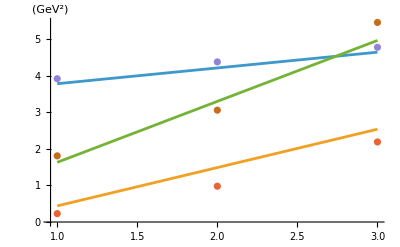

```mathematica
Block[{n},ff[n_]=EulerMatrix[{α,β,γ}].v3/.bestfitparams];
data=Table[Table[{n,ff[n][[i]]},{n,1,3}],{i,1,3}]
traj1=Table[bestfitmas[[j]],{j,2,Length[bestfitmas],3}];
traj2=Table[bestfitmas[[j]],{j,3,Length[bestfitmas],3}];
traj3=Table[bestfitmas[[j]],{j,4,Length[bestfitmas],3}];
m1=Table[{i,traj1[[i]][[1]]},{i,1,Length[traj1]}];
m2=Table[{i,traj2[[i]][[1]]},{i,1,Length[traj2]}];
m3=Table[{i,traj3[[i]][[1]]},{i,1,Length[traj3]}];
δ1=traj1[[All,2]]
δ2=traj2[[All,2]]
δ3=traj3[[All,2]]
data=Join[data,{m1},{m2},{m3}];
ListPlot[data,Joined->{True,True,True,False,False,False},AxesLabel->{"","(GeV^2)"}]
```

Get the mathematical trajectories:

```mathematica
mathmass=v3/.bestfitparams
Table[mathmass[[1]]/.{n->i},{i,1,3}]
Table[mathmass[[2]]/.{n->i},{i,1,3}]
Table[mathmass[[3]]/.{n->i},{i,1,3}]
```

{0.0963188+1.42585 n,0.429973+1.42585 n,3.37891+8.70717×10^-7 n}

{1.52217,2.94802,4.37388}

{1.85583,3.28168,4.70753}

{3.37891,3.37891,3.37891}

Not let’s see if there is a better solution for negative initial masses as the first we get is the one at n=1.

```mathematica
signs={{1,1,1,1,1},{-1,1,1,1,1},{1,-1,1,1,1}{1,1,-1,1,1},{-1,-1,1,1,1},{1,-1,-1,1,1},{-1,1,-1,1,1},{-1,-1,-1,1,1}}; (*To get the signs of the interesting solutions*)
t=0; (*to count the number of reasonable trajectories*)
goodtrajectories={};
For[i=1,i≤Length[trajectories],i++,
	M=trajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	params={m02,m02s,m02p,μp,μ,α,β,γ}/.fit["BestFitParameters"];
	params=params[[1;;5]];
	sign=Sign[params];
	If[MemberQ[signs,sign],
		AppendTo[goodtrajectories,M];
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
		Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1
	];
]
t
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,1.81},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{0.861345 (0.291792+0.291505 (2+n))+0.507419 (-0.946498+0.476667 (2+n))+0.024703 (1.69412+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.501716 (0.291792+0.291505 (1+n))+0.842013 (-0.946498+0.476667 (1+n))+0.198232 (1.69412+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0797864 (0.291792+0.291505 n)-0.18314 (-0.946498+0.476667 n)+0.979844 (1.69412+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.946498
m02s→1.69412
m02p→0.291792
μp→0.874516
μ→1.43
α→-0.527437
β→1.49093
γ→1.38602)

(0.443069 | -0.00428272 | 0.180739 | -0.253026 | 0.0048202 | -0.00078424 | 0.0814661 | 0.103769
-0.00428272 | 0.216109 | 0.0663326 | -0.287321 | 0.00359285 | -0.0888634 | 0.0651873 | -0.0266726
0.180739 | 0.0663326 | 0.102621 | -0.16837 | -0.00522432 | -0.00760107 | 0.054784 | 0.0381579
-0.253026 | -0.287321 | -0.16837 | 1.01757 | -0.118091 | 0.326835 | -0.225254 | -0.00985202
0.0048202 | 0.00359285 | -0.00522432 | -0.118091 | 0.0361092 | -0.0561149 | 0.0216706 | -0.00146211
-0.00078424 | -0.0888634 | -0.00760107 | 0.326835 | -0.0561149 | 0.142041 | -0.058185 | 0.0216832
0.0814661 | 0.0651873 | 0.054784 | -0.225254 | 0.0216706 | -0.058185 | 0.0585581 | 0.01025
0.103769 | -0.0266726 | 0.0381579 | -0.00985202 | -0.00146211 | 0.0216832 | 0.01025 | 0.0317911)

R^2=0.999919

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,3.92},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.973942 (3.37891+2.90239×10^-7 (2+n))+0.204633 (0.0963188+0.475284 (2+n))+0.0977848 (0.429973+0.475284 (2+n)), Mod[n,3]==2&&n>0}, {-0.179005 (3.37891+2.90239×10^-7 (1+n))+0.958337 (0.0963188+0.475284 (1+n))-0.222594 (0.429973+0.475284 (1+n)), Mod[n,3]==1&&n>0}, {-0.139261 (3.37891+2.90239×10^-7 n)+0.199289 (0.0963188+0.475284 n)+0.969995 (0.429973+0.475284 n), Mod[n,3]==0&&n>0}, {1.42585, n==0}, {0, True}}]

(m02→0.0963188
m02s→0.429973
m02p→3.37891
μp→8.70717×10^-7
μ→1.42585
α→-47.3057
β→-177.64
γ→-101.899)

(2.12254×10^12 | 2.09903×10^12 | -3.27609×10^11 | -1.78144×10^12 | 237346. | -4.95126×10^11 | -7.34925×10^11 | -6.89517×10^10
2.09903×10^12 | 2.07578×10^12 | -3.2398×10^11 | -1.76171×10^12 | 234716. | -4.89641×10^11 | -7.26783×10^11 | -6.81878×10^10
-3.27609×10^11 | -3.2398×10^11 | 5.05657×10^10 | 2.74961×10^11 | -36633.8 | 7.64215×10^10 | 1.13434×10^11 | 1.06425×10^10
-1.78144×10^12 | -1.76171×10^12 | 2.74961×10^11 | 1.49516×10^12 | -199203. | 4.15558×10^11 | 6.1682×10^11 | 5.78709×10^10
237346. | 234716. | -36633.8 | -199203. | 0.0608232 | -55365.6 | -82180.2 | -7710.25
-4.95126×10^11 | -4.89641×10^11 | 7.64215×10^10 | 4.15558×10^11 | -55365.6 | 1.15498×10^11 | 1.71436×10^11 | 1.60844×10^10
-7.34925×10^11 | -7.26783×10^11 | 1.13434×10^11 | 6.1682×10^11 | -82180.2 | 1.71436×10^11 | 2.54465×10^11 | 2.38743×10^10
-6.89517×10^10 | -6.81878×10^10 | 1.06425×10^10 | 5.78709×10^10 | -7710.25 | 1.60844×10^10 | 2.38743×10^10 | 2.23992×10^9)

R^2=0.999864

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,1.81},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.902198 (-0.653766+0.364524 (2+n))+0.367884 (-1.2462+0.476667 (2+n))+0.225165 (1.87477+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.403121 (-0.653766+0.364524 (1+n))+0.904857 (-1.2462+0.476667 (1+n))+0.136844 (1.87477+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.1534 (-0.653766+0.364524 n)-0.21423 (-1.2462+0.476667 n)+0.964663 (1.87477+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.2462
m02s→1.87477
m02p→-0.653766
μp→1.09357
μ→1.43
α→-0.420207
β→1.7248
γ→1.35227)

(0.34198 | -0.0275867 | 0.258216 | -0.0399206 | -0.0228765 | 0.0475573 | -0.00818324 | 0.0832503
-0.0275867 | 0.145949 | 0.00134948 | -0.0826992 | -0.0221112 | -0.010196 | 0.0352724 | -0.0182649
0.258216 | 0.00134948 | 0.201599 | -0.0557197 | -0.0198004 | 0.0360417 | 0.00563127 | 0.0627039
-0.0399206 | -0.0826992 | -0.0557197 | 0.684805 | -0.0961685 | 0.184731 | -0.192797 | 0.0251762
-0.0228765 | -0.0221112 | -0.0198004 | -0.0961685 | 0.0367718 | -0.0409248 | 0.0250252 | -0.00660514
0.0475573 | -0.010196 | 0.0360417 | 0.184731 | -0.0409248 | 0.071614 | -0.0501011 | 0.0237884
-0.00818324 | 0.0352724 | 0.00563127 | -0.192797 | 0.0250252 | -0.0501011 | 0.0611739 | -0.0117552
0.0832503 | -0.0182649 | 0.0627039 | 0.0251762 | -0.00660514 | 0.0237884 | -0.0117552 | 0.0261969)

R^2=0.999918

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{-0.793379 (-1.55547+1.21685×10^-7 (2+n))+0.580912 (-0.0677009+0.446023 (2+n))-0.18191 (1.37492+0.446023 (2+n)), Mod[n,3]==2&&n>0}, {0.573195 (-1.55547+1.21685×10^-7 (1+n))+0.813535 (-0.0677009+0.446023 (1+n))+0.0980268 (1.37492+0.446023 (1+n)), Mod[n,3]==1&&n>0}, {-0.204935 (-1.55547+1.21685×10^-7 n)+0.0264973 (-0.0677009+0.446023 n)+0.978417 (1.37492+0.446023 n), Mod[n,3]==0&&n>0}, {1.33807, n==0}, {0, True}}]

(m02→1.37492
m02s→-0.0677009
m02p→-1.55547
μp→3.65054×10^-7
μ→1.33807
α→-79.1655
β→-299.816
γ→-172.815)

(7.99086×10^12 | 1.19745×10^13 | 6.54213×10^12 | 1.71749×10^13 | -1.0977×10^6 | -7.72028×10^12 | -5.34378×10^12 | -1.58216×10^12
1.19745×10^13 | 1.79442×10^13 | 9.80357×10^12 | 2.57371×10^13 | -1.64494×10^6 | -1.15691×10^13 | -8.00781×10^12 | -2.37091×10^12
6.54213×10^12 | 9.80357×10^12 | 5.35605×10^12 | 1.40611×10^13 | -898691. | -6.32061×10^12 | -4.37496×10^12 | -1.29531×10^12
1.71749×10^13 | 2.57371×10^13 | 1.40611×10^13 | 3.69143×10^13 | -2.35931×10^6 | -1.65933×10^13 | -1.14855×10^13 | -3.40056×10^12
-1.0977×10^6 | -1.64494×10^6 | -898691. | -2.35931×10^6 | 0.321835 | 1.06053×10^6 | 734074. | 217340.
-7.72028×10^12 | -1.15691×10^13 | -6.32061×10^12 | -1.65933×10^13 | 1.06053×10^6 | 7.45887×10^12 | 5.16283×10^12 | 1.52858×10^12
-5.34378×10^12 | -8.00781×10^12 | -4.37496×10^12 | -1.14855×10^13 | 734074. | 5.16283×10^12 | 3.57358×10^12 | 1.05804×10^12
-1.58216×10^12 | -2.37091×10^12 | -1.29531×10^12 | -3.40056×10^12 | 217340. | 1.52858×10^12 | 1.05804×10^12 | 3.1326×10^11)

R^2=0.99928

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{0.984193 (0.92307+0.412724 (2+n))-0.149587 (-0.86779+0.476667 (2+n))-0.0948015 (0.0751448+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.121832 (0.92307+0.412724 (1+n))+0.960397 (-0.86779+0.476667 (1+n))-0.250589 (0.0751448+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.128532 (0.92307+0.412724 n)+0.235078 (-0.86779+0.476667 n)+0.963441 (0.0751448+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.86779
m02s→0.0751448
m02p→0.92307
μp→1.23817
μ→1.43
α→-18.7264
β→-67.6731
γ→-35.889)

(2.26431 | 1.94671 | 0.852759 | -2.34026 | 0.228849 | -0.894643 | 0.857468 | -0.0737338
1.94671 | 2.40826 | 1.45049 | -2.77829 | 0.223582 | -1.06905 | 0.820136 | -0.414628
0.852759 | 1.45049 | 1.49937 | -2.17063 | 0.196943 | -0.464967 | 0.551681 | -0.171796
-2.34026 | -2.77829 | -2.17063 | 4.51968 | -0.703527 | 1.24571 | -1.48924 | 0.24405
0.228849 | 0.223582 | 0.196943 | -0.703527 | 0.304576 | -0.184713 | 0.29576 | 0.0219405
-0.894643 | -1.06905 | -0.464967 | 1.24571 | -0.184713 | 0.592208 | -0.420597 | 0.241441
0.857468 | 0.820136 | 0.551681 | -1.48924 | 0.29576 | -0.420597 | 0.557784 | -0.0204039
-0.0737338 | -0.414628 | -0.171796 | 0.24405 | 0.0219405 | 0.241441 | -0.0204039 | 0.267577)

R^2=0.999319

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{-0.4474 (-0.467852+0.391857 (2+n))+0.366196 (-0.453017+0.476667 (2+n))+0.815925 (0.727968+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.22116 (-0.467852+0.391857 (1+n))+0.929293 (-0.453017+0.476667 (1+n))-0.295808 (0.727968+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.866557 (-0.467852+0.391857 n)-0.0481054 (-0.453017+0.476667 n)+0.496754 (0.727968+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.727968
m02s→-0.453017
m02p→-0.467852
μp→1.17557
μ→1.43
α→-22.4502
β→-68.5925
γ→-34.461)

(1.57251 | 0.194921 | -0.263606 | -1.6054 | -0.145806 | 0.584593 | 0.9262 | -0.442962
0.194921 | 1.13357 | -0.211117 | -1.31374 | 0.0467809 | 0.757171 | 0.568503 | -0.942431
-0.263606 | -0.211117 | 2.77824 | 0.666178 | -0.272169 | -1.74511 | -0.634816 | 1.39513
-1.6054 | -1.31374 | 0.666178 | 5.78763 | -0.794604 | -1.94603 | -2.91068 | 2.31027
-0.145806 | 0.0467809 | -0.272169 | -0.794604 | 0.326613 | 0.309161 | 0.430742 | -0.404186
0.584593 | 0.757171 | -1.74511 | -1.94603 | 0.309161 | 1.61163 | 1.12467 | -1.53961
0.9262 | 0.568503 | -0.634816 | -2.91068 | 0.430742 | 1.12467 | 1.53831 | -1.24681
-0.442962 | -0.942431 | 1.39513 | 2.31027 | -0.404186 | -1.53961 | -1.24681 | 1.6219)

R^2=0.999269

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.38}}}

Piecewise[{{-0.346417 (-1.64995+7.91268×10^-8 (2+n))+0.937407 (-1.24462+0.448828 (2+n))-0.0355423 (1.29058+0.448828 (2+n)), Mod[n,3]==2&&n>0}, {0.738435 (-1.64995+7.91268×10^-8 (1+n))+0.295862 (-1.24462+0.448828 (1+n))+0.605953 (1.29058+0.448828 (1+n)), Mod[n,3]==1&&n>0}, {-0.57854 (-1.64995+7.91268×10^-8 n)-0.183667 (-1.24462+0.448828 n)+0.794706 (1.29058+0.448828 n), Mod[n,3]==0&&n>0}, {1.34648, n==0}, {0, True}}]

(m02→1.29058
m02s→-1.24462
m02p→-1.64995
μp→2.3738×10^-7
μ→1.34648
α→-79.672
β→-299.405
γ→-172.56)

(7.5987×10^13 | 6.81242×10^13 | 8.04751×10^12 | 1.17606×10^14 | -4.5023×10^6 | -6.20345×10^13 | -3.55741×10^13 | -3.58895×10^13
6.81242×10^13 | 6.1075×10^13 | 7.21479×10^12 | 1.05436×10^14 | -4.03642×10^6 | -5.56155×10^13 | -3.18931×10^13 | -3.21758×10^13
8.04751×10^12 | 7.21479×10^12 | 8.52282×10^11 | 1.24552×10^13 | -476822. | -6.56985×10^12 | -3.76753×10^12 | -3.80092×10^12
1.17606×10^14 | 1.05436×10^14 | 1.24552×10^13 | 1.8202×10^14 | -6.96825×10^6 | -9.60114×10^13 | -5.50584×10^13 | -5.55465×10^13
-4.5023×10^6 | -4.03642×10^6 | -476822. | -6.96825×10^6 | 0.614239 | 3.6756×10^6 | 2.1078×10^6 | 2.12648×10^6
-6.20345×10^13 | -5.56155×10^13 | -6.56985×10^12 | -9.60114×10^13 | 3.6756×10^6 | 5.06439×10^13 | 2.90421×10^13 | 2.92996×10^13
-3.55741×10^13 | -3.18931×10^13 | -3.76753×10^12 | -5.50584×10^13 | 2.1078×10^6 | 2.90421×10^13 | 1.66544×10^13 | 1.6802×10^13
-3.58895×10^13 | -3.21758×10^13 | -3.80092×10^12 | -5.55465×10^13 | 2.12648×10^6 | 2.92996×10^13 | 1.6802×10^13 | 1.6951×10^13)

R^2=0.998626

{Trajectory 1,{{1,0.23},{4,0.98},{7,1.81}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.524929 (0.515389+2.76729×10^-8 (2+n))+0.833118 (-0.244305+0.436092 (2+n))+0.174255 (2.0951+0.436092 (2+n)), Mod[n,3]==2&&n>0}, {-0.85114 (0.515389+2.76729×10^-8 (1+n))+0.514564 (-0.244305+0.436092 (1+n))+0.103845 (2.0951+0.436092 (1+n)), Mod[n,3]==1&&n>0}, {-0.00314994 (0.515389+2.76729×10^-8 n)-0.202827 (-0.244305+0.436092 n)+0.97921 (2.0951+0.436092 n), Mod[n,3]==0&&n>0}, {1.30828, n==0}, {0, True}}]

(m02→-0.244305
m02s→2.0951
m02p→0.515389
μp→8.30188×10^-8
μ→1.30828
α→71.2385
β→300.019
γ→174.154)

(2.55556×10^13 | 7.61321×10^12 | -1.88344×10^13 | -8.41965×10^13 | 813867. | -5.15508×10^13 | -4.40749×10^12 | -1.62385×10^11
7.61321×10^12 | 2.26803×10^12 | -5.61093×10^12 | -2.50828×10^13 | 242457. | -1.53574×10^13 | -1.31303×10^12 | -4.83757×10^10
-1.88344×10^13 | -5.61093×10^12 | 1.3881×10^13 | 6.20527×10^13 | -599819. | 3.79929×10^13 | 3.24831×10^12 | 1.19677×10^11
-8.41965×10^13 | -2.50828×10^13 | 6.20527×10^13 | 2.77397×10^14 | -2.6814×10^6 | 1.69841×10^14 | 1.45211×10^13 | 5.34999×10^11
813867. | 242457. | -599819. | -2.6814×10^6 | 0.0850764 | -1.64174×10^6 | -140365. | -5171.41
-5.15508×10^13 | -1.53574×10^13 | 3.79929×10^13 | 1.69841×10^14 | -1.64174×10^6 | 1.03988×10^14 | 8.8908×10^12 | 3.27563×10^11
-4.40749×10^12 | -1.31303×10^12 | 3.24831×10^12 | 1.45211×10^13 | -140365. | 8.8908×10^12 | 7.60145×10^11 | 2.8006×10^10
-1.62385×10^11 | -4.83757×10^10 | 1.19677×10^11 | 5.34999×10^11 | -5171.41 | 3.27563×10^11 | 2.8006×10^10 | 1.03182×10^9)

R^2=0.99981

{Trajectory 1,{{1,0.23},{4,0.98},{7,3.06}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{-0.294888 (-1.9655+4.70096×10^-8 (2+n))+0.920264 (-0.20505+0.45638 (2+n))-0.257205 (1.23474+0.45638 (2+n)), Mod[n,3]==2&&n>0}, {0.744053 (-1.9655+4.70096×10^-8 (1+n))+0.390034 (-0.20505+0.45638 (1+n))+0.542456 (1.23474+0.45638 (1+n)), Mod[n,3]==1&&n>0}, {-0.599522 (-1.9655+4.70096×10^-8 n)+0.0314097 (-0.20505+0.45638 n)+0.799742 (1.23474+0.45638 n), Mod[n,3]==0&&n>0}, {1.36914, n==0}, {0, True}}]

(m02→1.23474
m02s→-0.20505
m02p→-1.9655
μp→1.41029×10^-7
μ→1.36914
α→-79.7333
β→-299.379
γ→-172.827)

(2.00664×10^14 | 2.12209×10^14 | 1.0392×10^14 | 2.87601×10^14 | -4.28601×10^6 | -1.29788×10^14 | -1.06251×10^14 | -7.78109×10^13
2.12209×10^14 | 2.24419×10^14 | 1.09899×10^14 | 3.04149×10^14 | -4.53261×10^6 | -1.37256×10^14 | -1.12365×10^14 | -8.22879×10^13
1.0392×10^14 | 1.09899×10^14 | 5.38181×10^13 | 1.48943×10^14 | -2.21964×10^6 | -6.72148×10^13 | -5.50255×10^13 | -4.02968×10^13
2.87601×10^14 | 3.04149×10^14 | 1.48943×10^14 | 4.12204×10^14 | -6.14292×10^6 | -1.86019×10^14 | -1.52285×10^14 | -1.11522×10^14
-4.28601×10^6 | -4.53261×10^6 | -2.21964×10^6 | -6.14292×10^6 | 0.316376 | 2.77217×10^6 | 2.26944×10^6 | 1.66197×10^6
-1.29788×10^14 | -1.37256×10^14 | -6.72148×10^13 | -1.86019×10^14 | 2.77217×10^6 | 8.39463×10^13 | 6.87227×10^13 | 5.03277×10^13
-1.06251×10^14 | -1.12365×10^14 | -5.50255×10^13 | -1.52285×10^14 | 2.26944×10^6 | 6.87227×10^13 | 5.62599×10^13 | 4.12008×10^13
-7.78109×10^13 | -8.22879×10^13 | -4.02968×10^13 | -1.11522×10^14 | 1.66197×10^6 | 5.03277×10^13 | 4.12008×10^13 | 3.01725×10^13)

R^2=0.999292

{Trajectory 1,{{1,0.23},{4,0.98},{7,3.06}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,4.38}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{-0.535604 (-1.93078+7.09786×10^-8 (2+n))+0.797703 (-0.0782322+0.44533 (2+n))-0.277126 (1.45656+0.44533 (2+n)), Mod[n,3]==2&&n>0}, {0.710713 (-1.93078+7.09786×10^-8 (1+n))+0.603044 (-0.0782322+0.44533 (1+n))+0.362249 (1.45656+0.44533 (1+n)), Mod[n,3]==1&&n>0}, {-0.456087 (-1.93078+7.09786×10^-8 n)+0.00293514 (-0.0782322+0.44533 n)+0.889931 (1.45656+0.44533 n), Mod[n,3]==0&&n>0}, {1.33599, n==0}, {0, True}}]

(m02→1.45656
m02s→-0.0782322
m02p→-1.93078
μp→2.12936×10^-7
μ→1.33599
α→-79.4648
β→-299.549
γ→-172.791)

(5.18596×10^13 | 6.72019×10^13 | 3.63994×10^13 | 8.23838×10^13 | -1.86133×10^6 | -3.90105×10^13 | -2.6974×10^13 | -1.77922×10^13
6.72019×10^13 | 8.70831×10^13 | 4.7168×10^13 | 1.06756×10^14 | -2.412×10^6 | -5.05515×10^13 | -3.49541×10^13 | -2.30558×10^13
3.63994×10^13 | 4.7168×10^13 | 2.55482×10^13 | 5.78239×10^13 | -1.30644×10^6 | -2.73808×10^13 | -1.89327×10^13 | -1.2488×10^13
8.23838×10^13 | 1.06756×10^14 | 5.78239×10^13 | 1.30874×10^14 | -2.9569×10^6 | -6.19718×10^13 | -4.28508×10^13 | -2.82645×10^13
-1.86133×10^6 | -2.412×10^6 | -1.30644×10^6 | -2.9569×10^6 | 0.235642 | 1.40015×10^6 | 968146. | 638592.
-3.90105×10^13 | -5.05515×10^13 | -2.73808×10^13 | -6.19718×10^13 | 1.40015×10^6 | 2.93449×10^13 | 2.02908×10^13 | 1.33838×10^13
-2.6974×10^13 | -3.49541×10^13 | -1.89327×10^13 | -4.28508×10^13 | 968146. | 2.02908×10^13 | 1.40302×10^13 | 9.25435×10^12
-1.77922×10^13 | -2.30558×10^13 | -1.2488×10^13 | -2.82645×10^13 | 638592. | 1.33838×10^13 | 9.25435×10^12 | 6.10419×10^12)

R^2=0.999473

{Trajectory 1,{{1,0.23},{4,0.98},{7,3.06}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.0898785 (-3.01465+6.201×10^-8 (2+n))+0.992028 (-0.341233+0.44846 (2+n))-0.0883361 (0.395795+0.44846 (2+n)), Mod[n,3]==2&&n>0}, {0.408658 (-3.01465+6.201×10^-8 (1+n))+0.0441513 (-0.341233+0.44846 (1+n))+0.911619 (0.395795+0.44846 (1+n)), Mod[n,3]==1&&n>0}, {-0.908251 (-3.01465+6.201×10^-8 n)+0.118034 (-0.341233+0.44846 n)+0.401432 (0.395795+0.44846 n), Mod[n,3]==0&&n>0}, {1.34538, n==0}, {0, True}}]

(m02→0.395795
m02s→-0.341233
m02p→-3.01465
μp→1.8603×10^-7
μ→1.34538
α→-80.3271
β→-298.883
γ→-173.074)

(4.75819×10^14 | 3.01863×10^14 | 2.83023×10^13 | 3.47065×10^14 | -9.45524×10^6 | -1.2318×10^14 | -1.79672×10^14 | -1.11878×10^14
3.01863×10^14 | 1.91504×10^14 | 1.79552×10^13 | 2.2018×10^14 | -5.99847×10^6 | -7.8146×10^13 | -1.13985×10^14 | -7.09762×10^13
2.83023×10^13 | 1.79552×10^13 | 1.68346×10^12 | 2.06439×10^13 | -562409. | -7.32688×10^12 | -1.06871×10^13 | -6.65465×10^12
3.47065×10^14 | 2.2018×10^14 | 2.06439×10^13 | 2.53151×10^14 | -6.8967×10^6 | -8.98478×10^13 | -1.31054×10^14 | -8.16044×10^13
-9.45524×10^6 | -5.99847×10^6 | -562409. | -6.8967×10^6 | 0.476815 | 2.44776×10^6 | 3.57036×10^6 | 2.22318×10^6
-1.2318×10^14 | -7.8146×10^13 | -7.32688×10^12 | -8.98478×10^13 | 2.44776×10^6 | 3.18886×10^13 | 4.65133×10^13 | 2.89629×10^13
-1.79672×10^14 | -1.13985×10^14 | -1.06871×10^13 | -1.31054×10^14 | 3.57036×10^6 | 4.65133×10^13 | 6.78453×10^13 | 4.22458×10^13
-1.11878×10^14 | -7.09762×10^13 | -6.65465×10^12 | -8.16044×10^13 | 2.22318×10^6 | 2.89629×10^13 | 4.22458×10^13 | 2.63056×10^13)

R^2=0.998934

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{-0.310068 (-0.15424+0.390222 (2+n))+0.266776 (-0.392557+0.476667 (2+n))+0.912518 (0.528634+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.0026416 (-0.15424+0.390222 (1+n))+0.960061 (-0.392557+0.476667 (1+n))-0.279778 (0.528634+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.950711 (-0.15424+0.390222 n)+0.0843397 (-0.392557+0.476667 n)+0.298389 (0.528634+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.528634
m02s→-0.392557
m02p→-0.15424
μp→1.17067
μ→1.43
α→75.3897
β→294.994
γ→175.654)

(0.742588 | 0.104359 | 0.07059 | -0.886354 | -0.00921626 | 0.0842712 | -0.453023 | -0.0329147
0.104359 | 0.687542 | -0.0418982 | -0.638697 | 0.0237444 | 0.00774399 | -0.342602 | -0.224331
0.07059 | -0.0418982 | 1.61144 | -0.408977 | -0.0920197 | -0.232316 | 0.189212 | 0.237077
-0.886354 | -0.638697 | -0.408977 | 2.78922 | -0.414164 | -0.0362184 | 1.3005 | 0.303427
-0.00921626 | 0.0237444 | -0.0920197 | -0.414164 | 0.169527 | 0.00990696 | -0.232931 | -0.0736831
0.0842712 | 0.00774399 | -0.232316 | -0.0362184 | 0.00990696 | 0.0470736 | -0.0771747 | -0.0332234
-0.453023 | -0.342602 | 0.189212 | 1.3005 | -0.232931 | -0.0771747 | 0.713746 | 0.214661
-0.0329147 | -0.224331 | 0.237077 | 0.303427 | -0.0736831 | -0.0332234 | 0.214661 | 0.125268)

R^2=0.999621

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,2.19},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.017623 (0.634075+0.409035 (2+n))+0.278566 (-0.563902+0.476667 (2+n))+0.960255 (-0.057037+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.000778312 (0.634075+0.409035 (1+n))+0.9604 (-0.563902+0.476667 (1+n))-0.278622 (-0.057037+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.999844 (0.634075+0.409035 n)-0.00565754 (-0.563902+0.476667 n)-0.0167083 (-0.057037+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.057037
m02s→-0.563902
m02p→0.634075
μp→1.22711
μ→1.43
α→-34.5134
β→-125.681
γ→-72.5831)

(1.25283 | 0.418219 | 0.135047 | -1.29545 | 0.164154 | -0.0443379 | 0.723651 | -0.0231969
0.418219 | 0.588658 | 0.0689387 | -0.615159 | 0.0414552 | -0.0936229 | 0.341804 | -0.089168
0.135047 | 0.0689387 | 2.35501 | -1.49866 | 0.0516335 | -0.00796285 | 0.118165 | -0.0218377
-1.29545 | -0.615159 | -1.49866 | 2.57721 | -0.396872 | 0.120466 | -0.992337 | 0.106822
0.164154 | 0.0414552 | 0.0516335 | -0.396872 | 0.170281 | -0.0312443 | 0.218621 | -0.0272228
-0.0443379 | -0.0936229 | -0.00796285 | 0.120466 | -0.0312443 | 0.0233902 | -0.0687929 | 0.0227784
0.723651 | 0.341804 | 0.118165 | -0.992337 | 0.218621 | -0.0687929 | 0.55016 | -0.0561615
-0.0231969 | -0.089168 | -0.0218377 | 0.106822 | -0.0272228 | 0.0227784 | -0.0561615 | 0.0226624)

R^2=0.999619

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{0.616065 (-2.02783+8.31646×10^-8 (2+n))+0.151577 (-0.39664+0.444358 (2+n))+0.772974 (0.809918+0.444358 (2+n)), Mod[n,3]==2&&n>0}, {0.0190101 (-2.02783+8.31646×10^-8 (1+n))+0.978164 (-0.39664+0.444358 (1+n))-0.206965 (0.809918+0.444358 (1+n)), Mod[n,3]==1&&n>0}, {-0.787466 (-2.02783+8.31646×10^-8 n)+0.142198 (-0.39664+0.444358 n)+0.599731 (0.809918+0.444358 n), Mod[n,3]==0&&n>0}, {1.33308, n==0}, {0, True}}]

(m02→-0.39664
m02s→0.809918
m02p→-2.02783
μp→2.49494×10^-7
μ→1.33308
α→78.5707
β→311.682
γ→180.874)

(4.97175×10^13 | 6.69044×10^13 | 1.69971×10^13 | 7.66662×10^13 | -3.19683×10^6 | 2.63556×10^13 | 3.77595×10^13 | 2.07541×10^13
6.69044×10^13 | 9.00326×10^13 | 2.28728×10^13 | 1.03169×10^14 | -4.30194×10^6 | 3.54665×10^13 | 5.08126×10^13 | 2.79286×10^13
1.69971×10^13 | 2.28728×10^13 | 5.81084×10^12 | 2.62101×10^13 | -1.09291×10^6 | 9.01026×10^12 | 1.2909×10^13 | 7.09527×10^12
7.66662×10^13 | 1.03169×10^14 | 2.62101×10^13 | 1.18222×10^14 | -4.92962×10^6 | 4.06413×10^13 | 5.82266×10^13 | 3.20036×10^13
-3.19683×10^6 | -4.30194×10^6 | -1.09291×10^6 | -4.92962×10^6 | 0.461306 | -1.69466×10^6 | -2.42793×10^6 | -1.33449×10^6
2.63556×10^13 | 3.54665×10^13 | 9.01026×10^12 | 4.06413×10^13 | -1.69466×10^6 | 1.39713×10^13 | 2.00166×10^13 | 1.10019×10^13
3.77595×10^13 | 5.08126×10^13 | 1.2909×10^13 | 5.82266×10^13 | -2.42793×10^6 | 2.00166×10^13 | 2.86776×10^13 | 1.57624×10^13
2.07541×10^13 | 2.79286×10^13 | 7.09527×10^12 | 3.20036×10^13 | -1.33449×10^6 | 1.10019×10^13 | 1.57624×10^13 | 8.66362×10^12)

R^2=0.998968

{Trajectory 1,{{1,0.23},{4,0.98},{7,5.46}}}

{Trajectory 2,{{2,2.19},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.825313 (-0.351236+0.35871 (2+n))-0.174618 (-0.699103+0.476667 (2+n))+0.536998 (0.89902+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.336761 (-0.351236+0.35871 (1+n))+0.915564 (-0.699103+0.476667 (1+n))-0.21985 (0.89902+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.453266 (-0.351236+0.35871 n)+0.362285 (-0.699103+0.476667 n)+0.814432 (0.89902+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.699103
m02s→0.89902
m02p→-0.351236
μp→1.07613
μ→1.43
α→0.387418
β→2.04122
γ→1.98934)

(1.43986 | 0.0719448 | 0.340199 | -0.646562 | -0.135786 | -0.586476 | 0.163977 | -0.114747
0.0719448 | 3.47204 | -1.204 | -3.24267 | -0.1698 | -1.07358 | 1.62 | -1.2902
0.340199 | -1.204 | 1.73932 | 0.482596 | -0.16435 | 1.05041 | -0.692174 | 1.00855
-0.646562 | -3.24267 | 0.482596 | 10.5092 | -1.43941 | 1.73392 | -4.64279 | 1.25714
-0.135786 | -0.1698 | -0.16435 | -1.43941 | 0.541606 | -0.227341 | 0.68463 | -0.0730347
-0.586476 | -1.07358 | 1.05041 | 1.73392 | -0.227341 | 1.20399 | -1.03006 | 0.848841
0.163977 | 1.62 | -0.692174 | -4.64279 | 0.68463 | -1.03006 | 2.20165 | -0.807172
-0.114747 | -1.2902 | 1.00855 | 1.25714 | -0.0730347 | 0.848841 | -0.807172 | 0.777938)

R^2=0.998789

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{-0.000666187 (-1.63248+0.476667 (2+n))-0.226395 (1.56819+0.476667 (2+n))+0.974035 (-0.624809+0.59778 (2+n)), Mod[n,3]==2&&n>0}, {0.941097 (-1.63248+0.476667 (1+n))+0.329214 (1.56819+0.476667 (1+n))+0.0771628 (-0.624809+0.59778 (1+n)), Mod[n,3]==1&&n>0}, {-0.338136 (-1.63248+0.476667 n)+0.916713 (1.56819+0.476667 n)+0.21284 (-0.624809+0.59778 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.63248
m02s→1.56819
m02p→-0.624809
μp→1.79334
μ→1.43
α→0.0790546
β→1.35632
γ→1.21742)

(0.367735 | -0.149033 | 0.237465 | -0.0289586 | -0.0164704 | 0.00219777 | -0.0527785 | 0.0760129
-0.149033 | 0.29572 | 0.0192326 | -0.140052 | -0.0226379 | -0.0167532 | 0.0576 | -0.0326205
0.237465 | 0.0192326 | 0.222713 | -0.127841 | -0.0137852 | 0.00202517 | 0.00189567 | 0.0590467
-0.0289586 | -0.140052 | -0.127841 | 0.542189 | -0.137975 | 0.141934 | -0.134797 | -0.042498
-0.0164704 | -0.0226379 | -0.0137852 | -0.137975 | 0.0865162 | -0.0602129 | 0.0353427 | 0.0194322
0.00219777 | -0.0167532 | 0.00202517 | 0.141934 | -0.0602129 | 0.0834199 | -0.0198424 | -0.000404285
-0.0527785 | 0.0576 | 0.00189567 | -0.134797 | 0.0353427 | -0.0198424 | 0.0529472 | 0.00438472
0.0760129 | -0.0326205 | 0.0590467 | -0.042498 | 0.0194322 | -0.000404285 | 0.00438472 | 0.0293489)

R^2=0.999806

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.0763094 (-1.12968+0.476667 (2+n))-0.336024 (0.208929+0.476667 (2+n))+0.938757 (-1.72119+0.869387 (2+n)), Mod[n,3]==2&&n>0}, {0.937874 (-1.12968+0.476667 (1+n))+0.343803 (0.208929+0.476667 (1+n))+0.046825 (-1.72119+0.869387 (1+n)), Mod[n,3]==1&&n>0}, {-0.338482 (-1.12968+0.476667 n)+0.876862 (0.208929+0.476667 n)+0.341383 (-1.72119+0.869387 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.12968
m02s→0.208929
m02p→-1.72119
μp→2.60816
μ→1.43
α→0.0498385
β→1.22241
γ→1.2024)

(0.105231 | -0.0667153 | 0.127919 | -0.0507414 | -0.0229137 | -0.00247724 | -0.0326262 | 0.0101123
-0.0667153 | 0.325463 | 0.0346434 | -0.0657835 | -0.0446683 | 0.01164 | 0.0664843 | -0.0104206
0.127919 | 0.0346434 | 0.378307 | -0.290223 | 0.00961703 | 0.0120901 | 0.0588641 | 0.0880376
-0.0507414 | -0.0657835 | -0.290223 | 0.353239 | -0.0811781 | 0.0344943 | -0.101082 | -0.0927243
-0.0229137 | -0.0446683 | 0.00961703 | -0.0811781 | 0.0740299 | -0.0315273 | 0.0322131 | 0.0332685
-0.00247724 | 0.01164 | 0.0120901 | 0.0344943 | -0.0315273 | 0.0351254 | -0.000977354 | -0.00167008
-0.0326262 | 0.0664843 | 0.0588641 | -0.101082 | 0.0322131 | -0.000977354 | 0.0581049 | 0.0311266
0.0101123 | -0.0104206 | 0.0880376 | -0.0927243 | 0.0332685 | -0.00167008 | 0.0311266 | 0.0376858)

R^2=0.999834

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0545451 (-1.0427+0.476667 (2+n))-0.109961 (0.505112+0.476667 (2+n))+0.992438 (-2.31712+0.912343 (2+n)), Mod[n,3]==2&&n>0}, {0.965543 (-1.0427+0.476667 (1+n))+0.247482 (0.505112+0.476667 (1+n))+0.0804878 (-2.31712+0.912343 (1+n)), Mod[n,3]==1&&n>0}, {-0.254462 (-1.0427+0.476667 n)+0.962632 (0.505112+0.476667 n)+0.0926733 (-2.31712+0.912343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.0427
m02s→0.505112
m02p→-2.31712
μp→2.73703
μ→1.43
α→0.0809239
β→1.47799
γ→1.31237)

(0.0684277 | -0.0147792 | 0.130385 | -0.0393815 | -0.0296133 | 0.00150852 | -0.0264978 | 0.00198279
-0.0147792 | 0.362428 | -0.0555219 | -0.0338386 | -0.0723412 | 0.0221652 | 0.0670068 | -0.0100996
0.130385 | -0.0555219 | 0.362365 | -0.221536 | -0.00244385 | 0.0107413 | 0.00871581 | 0.0522397
-0.0393815 | -0.0338386 | -0.221536 | 0.34713 | -0.0845889 | 0.0314725 | -0.107198 | -0.0627188
-0.0296133 | -0.0723412 | -0.00244385 | -0.0845889 | 0.0809518 | -0.0278437 | 0.0355224 | 0.0252641
0.00150852 | 0.0221652 | 0.0107413 | 0.0314725 | -0.0278437 | 0.0272793 | -0.0036061 | 0.00201178
-0.0264978 | 0.0670068 | 0.00871581 | -0.107198 | 0.0355224 | -0.0036061 | 0.0669554 | 0.0231488
0.00198279 | -0.0100996 | 0.0522397 | -0.0627188 | 0.0252641 | 0.00201178 | 0.0231488 | 0.022387)

R^2=0.999819

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{0.995151 (-0.00983145+0.346608 (2+n))+0.0631962 (-2.8958+0.476667 (2+n))-0.0753743 (2.6321+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.0139118 (-0.00983145+0.346608 (1+n))+0.849023 (-2.8958+0.476667 (1+n))+0.528173 (2.6321+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0973731 (-0.00983145+0.346608 n)-0.524563 (-2.8958+0.476667 n)+0.845785 (2.6321+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.8958
m02s→2.6321
m02p→-0.00983145
μp→1.03982
μ→1.43
α→-0.0139787
β→1.47327
γ→1.01565)

(0.254199 | -0.0848107 | 0.0563454 | 0.0356677 | 0.000343356 | 0.00912638 | -0.0224814 | 0.0405403
-0.0848107 | 0.0558201 | -0.00827785 | -0.0344728 | 0.000379463 | -0.0124151 | 0.00963763 | -0.0127062
0.0563454 | -0.00827785 | 0.0165842 | -0.00132069 | 0.000456875 | -0.00156489 | -0.00391962 | 0.00939417
0.0356677 | -0.0344728 | -0.00132069 | 0.0885649 | -0.0175338 | 0.0384981 | -0.0140584 | 0.00460801
0.000343356 | 0.000379463 | 0.000456875 | -0.0175338 | 0.00637485 | -0.00841358 | 0.0022676 | 0.000971821
0.00912638 | -0.0124151 | -0.00156489 | 0.0384981 | -0.00841358 | 0.0182805 | -0.00501619 | 0.0011374
-0.0224814 | 0.00963763 | -0.00391962 | -0.0140584 | 0.0022676 | -0.00501619 | 0.00388147 | -0.00335709
0.0405403 | -0.0127062 | 0.00939417 | 0.00460801 | 0.000971821 | 0.0011374 | -0.00335709 | 0.00693554)

R^2=0.999986

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.0881266 (-1.73306+0.476667 (2+n))-0.341105 (1.37992+0.476667 (2+n))+0.935885 (-0.00504427+0.550986 (2+n)), Mod[n,3]==2&&n>0}, {0.921873 (-1.73306+0.476667 (1+n))+0.383838 (1.37992+0.476667 (1+n))+0.0530914 (-0.00504427+0.550986 (1+n)), Mod[n,3]==1&&n>0}, {-0.377338 (-1.73306+0.476667 n)+0.858088 (1.37992+0.476667 n)+0.348282 (-0.00504427+0.550986 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.73306
m02s→1.37992
m02p→-0.00504427
μp→1.65296
μ→1.43
α→0.0566679
β→1.21506
γ→1.15651)

(0.296889 | -0.0827926 | 0.110805 | -0.0494609 | 0.00174188 | -0.0133561 | -0.0188859 | 0.0699374
-0.0827926 | 0.17503 | 0.0761733 | -0.140273 | 0.002214 | -0.0282287 | 0.0364516 | -0.0131992
0.110805 | 0.0761733 | 0.125354 | -0.142797 | 0.00720969 | -0.0183002 | 0.0258267 | 0.0380012
-0.0494609 | -0.140273 | -0.142797 | 0.372816 | -0.0882879 | 0.107201 | -0.0773628 | -0.0432729
0.00174188 | 0.002214 | 0.00720969 | -0.0882879 | 0.0510267 | -0.0427533 | 0.0173949 | 0.016261
-0.0133561 | -0.0282287 | -0.0183002 | 0.107201 | -0.0427533 | 0.0679589 | -0.00829603 | -0.00563227
-0.0188859 | 0.0364516 | 0.0258267 | -0.0773628 | 0.0173949 | -0.00829603 | 0.0267036 | 0.00737939
0.0699374 | -0.0131992 | 0.0380012 | -0.0432729 | 0.016261 | -0.00563227 | 0.00737939 | 0.0270569)

R^2=0.999886

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.0562861 (-2.00712+0.476667 (2+n))-0.148726 (1.6281+0.476667 (2+n))+0.987275 (-1.00313+0.616353 (2+n)), Mod[n,3]==2&&n>0}, {0.891192 (-2.00712+0.476667 (1+n))+0.45329 (1.6281+0.476667 (1+n))+0.0174768 (-1.00313+0.616353 (1+n)), Mod[n,3]==1&&n>0}, {-0.450121 (-2.00712+0.476667 n)+0.878868 (1.6281+0.476667 n)+0.158058 (-1.00313+0.616353 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.00712
m02s→1.6281
m02p→-1.00313
μp→1.84906
μ→1.43
α→0.0177002
β→1.41207
γ→1.09747)

(0.78492 | -0.235591 | 0.569685 | -0.0466579 | -0.0343123 | 0.00469335 | -0.13648 | 0.153539
-0.235591 | 0.457726 | 0.0141716 | -0.170973 | -0.0623672 | -0.00721349 | 0.08384 | -0.0446528
0.569685 | 0.0141716 | 0.518877 | -0.19917 | -0.0325691 | -0.00252459 | -0.0470868 | 0.128627
-0.0466579 | -0.170973 | -0.19917 | 0.976549 | -0.261811 | 0.271813 | -0.23775 | -0.0868929
-0.0343123 | -0.0623672 | -0.0325691 | -0.261811 | 0.169267 | -0.116639 | 0.0646525 | 0.042362
0.00469335 | -0.00721349 | -0.00252459 | 0.271813 | -0.116639 | 0.141291 | -0.0426915 | -0.0138549
-0.13648 | 0.08384 | -0.0470868 | -0.23775 | 0.0646525 | -0.0426915 | 0.10351 | -0.000797511
0.153539 | -0.0446528 | 0.128627 | -0.0868929 | 0.042362 | -0.0138549 | -0.000797511 | 0.0560656)

R^2=0.999621

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{0.841044 (-1.69566+0.476667 (2+n))-0.311578 (-0.50845+0.476667 (2+n))+0.442226 (-0.777799+0.902193 (2+n)), Mod[n,3]==2&&n>0}, {0.322496 (-1.69566+0.476667 (1+n))+0.945111 (-0.50845+0.476667 (1+n))+0.0525558 (-0.777799+0.902193 (1+n)), Mod[n,3]==1&&n>0}, {-0.434328 (-1.69566+0.476667 n)+0.0984144 (-0.50845+0.476667 n)+0.895363 (-0.777799+0.902193 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69566
m02s→-0.50845
m02p→-0.777799
μp→2.70658
μ→1.43
α→0.118289
β→0.461552
γ→0.222828)

(0.221585 | -0.0121512 | -0.0225018 | -0.0168707 | -0.0135161 | -0.00893452 | -0.0396583 | 0.0223027
-0.0121512 | 0.0482514 | 0.0457862 | -0.0128703 | -0.0293355 | 0.0100168 | 0.00878113 | -0.017233
-0.0225018 | 0.0457862 | 0.46996 | -0.286379 | 0.0486428 | -0.0845502 | -0.00943346 | 0.0910857
-0.0168707 | -0.0128703 | -0.286379 | 0.220995 | -0.0538028 | 0.0735096 | 0.0238711 | -0.0633162
-0.0135161 | -0.0293355 | 0.0486428 | -0.0538028 | 0.0509166 | -0.0402914 | -0.0214234 | 0.0246306
-0.00893452 | 0.0100168 | -0.0845502 | 0.0735096 | -0.0402914 | 0.0418008 | 0.0237001 | -0.0246202
-0.0396583 | 0.00878113 | -0.00943346 | 0.0238711 | -0.0214234 | 0.0237001 | 0.0252811 | -0.0087913
0.0223027 | -0.017233 | 0.0910857 | -0.0633162 | 0.0246306 | -0.0246202 | -0.0087913 | 0.0360707)

R^2=0.999886

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,4.78}}}

Piecewise[{{0.122644 (-1.32708+0.476667 (2+n))-0.329956 (0.450905+0.476667 (2+n))+0.935996 (-1.71419+0.876607 (2+n)), Mod[n,3]==2&&n>0}, {0.912011 (-1.32708+0.476667 (1+n))+0.409414 (0.450905+0.476667 (1+n))+0.0248254 (-1.71419+0.876607 (1+n)), Mod[n,3]==1&&n>0}, {-0.391401 (-1.32708+0.476667 n)+0.850593 (0.450905+0.476667 n)+0.351135 (-1.71419+0.876607 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.32708
m02s→0.450905
m02p→-1.71419
μp→2.62982
μ→1.43
α→0.0265168
β→1.21201
γ→1.13953)

(0.0397157 | -0.0305788 | 0.0368074 | -0.00756168 | -0.00606442 | -0.00192939 | -0.013176 | 0.00309891
-0.0305788 | 0.112297 | 0.0181665 | -0.0277947 | -0.0137356 | 0.0037786 | 0.0227205 | -0.00218183
0.0368074 | 0.0181665 | 0.0868977 | -0.0642676 | 0.00108187 | -0.00146475 | 0.0125182 | 0.0192455
-0.00756168 | -0.0277947 | -0.0642676 | 0.106501 | -0.0280333 | 0.0174814 | -0.0341255 | -0.0234035
-0.00606442 | -0.0137356 | 0.00108187 | -0.0280333 | 0.0257771 | -0.0116747 | 0.010407 | 0.0118634
-0.00192939 | 0.0037786 | -0.00146475 | 0.0174814 | -0.0116747 | 0.0115916 | -0.00155256 | -0.00269082
-0.013176 | 0.0227205 | 0.0125182 | -0.0341255 | 0.010407 | -0.00155256 | 0.0197666 | 0.00837371
0.00309891 | -0.00218183 | 0.0192455 | -0.0234035 | 0.0118634 | -0.00269082 | 0.00837371 | 0.0110102)

R^2=0.999942

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{0.0677425 (-1.262+0.476667 (2+n))-0.242427 (0.416025+0.476667 (2+n))+0.967802 (-2.0186+0.8955 (2+n)), Mod[n,3]==2&&n>0}, {0.922433 (-1.262+0.476667 (1+n))+0.384843 (0.416025+0.476667 (1+n))+0.0318332 (-2.0186+0.8955 (1+n)), Mod[n,3]==1&&n>0}, {-0.380169 (-1.262+0.476667 n)+0.890576 (0.416025+0.476667 n)+0.249692 (-2.0186+0.8955 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.262
m02s→0.416025
m02p→-2.0186
μp→2.6865
μ→1.43
α→0.0328804
β→1.31843
γ→1.16733)

(0.0426795 | -0.0269656 | 0.0589555 | -0.021233 | -0.00885803 | -0.000474131 | -0.0134506 | 0.00391749
-0.0269656 | 0.133873 | 0.00219978 | -0.0225228 | -0.0222792 | 0.00660607 | 0.0271651 | -0.00413442
0.0589555 | 0.00219978 | 0.139232 | -0.101321 | 0.000946246 | 0.00156642 | 0.0137081 | 0.0280777
-0.021233 | -0.0225228 | -0.101321 | 0.140421 | -0.0343021 | 0.0167124 | -0.0402242 | -0.0338193
-0.00885803 | -0.0222792 | 0.000946246 | -0.0343021 | 0.0322212 | -0.0132699 | 0.013517 | 0.0136136
-0.000474131 | 0.00660607 | 0.00156642 | 0.0167124 | -0.0132699 | 0.0125987 | -0.00170538 | -0.00171627
-0.0134506 | 0.0271651 | 0.0137081 | -0.0402242 | 0.013517 | -0.00170538 | 0.0242557 | 0.0115876
0.00391749 | -0.00413442 | 0.0280777 | -0.0338193 | 0.0136136 | -0.00171627 | 0.0115876 | 0.0133866)

R^2=0.999928

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{0.328045 (-1.47725+0.476667 (2+n))-0.486089 (0.125456+0.476667 (2+n))+0.810002 (-1.32989+0.900318 (2+n)), Mod[n,3]==2&&n>0}, {0.823612 (-1.47725+0.476667 (1+n))+0.567113 (0.125456+0.476667 (1+n))+0.00677192 (-1.32989+0.900318 (1+n)), Mod[n,3]==1&&n>0}, {-0.462654 (-1.47725+0.476667 n)+0.664906 (0.125456+0.476667 n)+0.586388 (-1.32989+0.900318 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.47725
m02s→0.125456
m02p→-1.32989
μp→2.70096
μ→1.43
α→0.00836017
β→0.944204
γ→0.962882)

(0.112155 | -0.0688819 | 0.0443715 | -0.0173643 | -0.0105524 | -0.00213877 | -0.0220733 | 0.016018
-0.0688819 | 0.135086 | 0.0756125 | -0.0534565 | -0.0111463 | -0.000498817 | 0.0278398 | -0.00395483
0.0443715 | 0.0756125 | 0.204756 | -0.156891 | 0.0106702 | -0.00989881 | 0.0386863 | 0.0570376
-0.0173643 | -0.0534565 | -0.156891 | 0.175193 | -0.0414766 | 0.0323652 | -0.0427936 | -0.0565487
-0.0105524 | -0.0111463 | 0.0106702 | -0.0414766 | 0.03917 | -0.0232033 | 0.0113804 | 0.0241347
-0.00213877 | -0.000498817 | -0.00989881 | 0.0323652 | -0.0232033 | 0.0238514 | -0.000823379 | -0.0105333
-0.0220733 | 0.0278398 | 0.0386863 | -0.0427936 | 0.0113804 | -0.000823379 | 0.0221901 | 0.0148116
0.016018 | -0.00395483 | 0.0570376 | -0.0565487 | 0.0241347 | -0.0105333 | 0.0148116 | 0.0320375)

R^2=0.999912

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.177486 (-1.28003+0.476667 (2+n))+0.981568 (-1.20821+0.476667 (2+n))+0.0708688 (-0.594045+0.819906 (2+n)), Mod[n,3]==2&&n>0}, {0.892869 (-1.28003+0.476667 (1+n))-0.190894 (-1.20821+0.476667 (1+n))+0.407853 (-0.594045+0.819906 (1+n)), Mod[n,3]==1&&n>0}, {-0.413864 (-1.28003+0.476667 n)+0.00911139 (-1.20821+0.476667 n)+0.910293 (-0.594045+0.819906 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.20821
m02s→-1.28003
m02p→-0.594045
μp→2.45972
μ→1.43
α→-48.8667
β→-175.502
γ→-102.124)

(0.193461 | 0.135009 | 0.0974302 | -0.109676 | -0.0335702 | 0.0491906 | -0.0525805 | 0.0429222
0.135009 | 0.23868 | 0.0294911 | -0.12076 | 0.00364769 | 0.0810184 | -0.088229 | -0.00984395
0.0974302 | 0.0294911 | 0.654763 | -0.430324 | 0.0604174 | 0.0845034 | -0.0903879 | 0.0447221
-0.109676 | -0.12076 | -0.430324 | 0.358884 | -0.0684507 | -0.106626 | 0.111973 | -0.0267753
-0.0335702 | 0.00364769 | 0.0604174 | -0.0684507 | 0.0588704 | 0.0306436 | -0.0357006 | -0.00718945
0.0491906 | 0.0810184 | 0.0845034 | -0.106626 | 0.0306436 | 0.0525855 | -0.0559259 | 0.00512358
-0.0525805 | -0.088229 | -0.0903879 | 0.111973 | -0.0357006 | -0.0559259 | 0.0613958 | -0.00425193
0.0429222 | -0.00984395 | 0.0447221 | -0.0267753 | -0.00718945 | 0.00512358 | -0.00425193 | 0.02278)

R^2=0.999868

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0368688 (-1.18775+0.476667 (2+n))-0.160103 (0.485462+0.476667 (2+n))+0.986412 (-2.0423+0.863817 (2+n)), Mod[n,3]==2&&n>0}, {0.949971 (-1.18775+0.476667 (1+n))+0.30074 (0.485462+0.476667 (1+n))+0.0843195 (-2.0423+0.863817 (1+n)), Mod[n,3]==1&&n>0}, {-0.310154 (-1.18775+0.476667 n)+0.940171 (0.485462+0.476667 n)+0.141005 (-2.0423+0.863817 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18775
m02s→0.485462
m02p→-2.0423
μp→2.59145
μ→1.43
α→0.0852737
β→1.42932
γ→1.25215)

(0.0237482 | -0.0147869 | 0.0370257 | -0.0109876 | -0.00595481 | 0.000476926 | -0.00842436 | 0.00262568
-0.0147869 | 0.0906393 | -0.00835313 | -0.0142106 | -0.0153093 | 0.00433855 | 0.018596 | -0.00408185
0.0370257 | -0.00835313 | 0.0861301 | -0.0579429 | -0.000175893 | 0.00316268 | 0.00555209 | 0.0161472
-0.0109876 | -0.0142106 | -0.0579429 | 0.0922838 | -0.0219521 | 0.00878981 | -0.0293613 | -0.0184992
-0.00595481 | -0.0153093 | -0.000175893 | -0.0219521 | 0.0198908 | -0.00765318 | 0.00908602 | 0.00710788
0.000476926 | 0.00433855 | 0.00316268 | 0.00878981 | -0.00765318 | 0.00759643 | -0.00128678 | 0.0000943871
-0.00842436 | 0.018596 | 0.00555209 | -0.0293613 | 0.00908602 | -0.00128678 | 0.0174778 | 0.00616386
0.00262568 | -0.00408185 | 0.0161472 | -0.0184992 | 0.00710788 | 0.0000943871 | 0.00616386 | 0.00694119)

R^2=0.999956

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.932313 (-1.3604+0.433139 (2+n))-0.314423 (-1.40172+0.476667 (2+n))+0.178691 (2.44222+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.274198 (-1.3604+0.433139 (1+n))+0.936724 (-1.40172+0.476667 (1+n))+0.217632 (2.44222+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.235812 (-1.3604+0.433139 n)-0.153905 (-1.40172+0.476667 n)+0.959534 (2.44222+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.40172
m02s→2.44222
m02p→-1.3604
μp→1.29942
μ→1.43
α→0.28604
β→1.80885
γ→1.41176)

(0.490355 | -0.460088 | 0.482452 | 0.230434 | -0.0201954 | 0.097155 | -0.137186 | 0.120433
-0.460088 | 0.615721 | -0.457689 | -0.178587 | -0.0223713 | -0.0743153 | 0.116868 | -0.116714
0.482452 | -0.457689 | 0.476188 | 0.229572 | -0.0193527 | 0.0992151 | -0.134529 | 0.12009
0.230434 | -0.178587 | 0.229572 | 0.263938 | -0.0469237 | 0.101696 | -0.101831 | 0.0649094
-0.0201954 | -0.0223713 | -0.0193527 | -0.0469237 | 0.0213194 | -0.0188374 | 0.0142815 | -0.0039028
0.097155 | -0.0743153 | 0.0992151 | 0.101696 | -0.0188374 | 0.0456766 | -0.0384721 | 0.0290794
-0.137186 | 0.116868 | -0.134529 | -0.101831 | 0.0142815 | -0.0384721 | 0.0485746 | -0.034921
0.120433 | -0.116714 | 0.12009 | 0.0649094 | -0.0039028 | 0.0290794 | -0.034921 | 0.0320823)

R^2=0.999952

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,5.46}}}

Piecewise[{{-0.266661 (-1.19644+0.476667 (2+n))-0.0220873 (1.69798+0.476667 (2+n))+0.963537 (-0.944112+0.55287 (2+n)), Mod[n,3]==2&&n>0}, {0.953402 (-1.19644+0.476667 (1+n))+0.140344 (1.69798+0.476667 (1+n))+0.267074 (-0.944112+0.55287 (1+n)), Mod[n,3]==1&&n>0}, {-0.141126 (-1.19644+0.476667 n)+0.989856 (1.69798+0.476667 n)-0.0163663 (-0.944112+0.55287 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.19644
m02s→1.69798
m02p→-0.944112
μp→1.65861
μ→1.43
α→0.270392
β→1.58716
γ→1.42918)

(0.177937 | -0.07807 | 0.172888 | 0.0197329 | -0.0241932 | 0.0211625 | -0.0438552 | 0.0411122
-0.07807 | 0.218756 | -0.0442154 | -0.0557527 | -0.0314996 | -0.0026999 | 0.0338891 | -0.0286258
0.172888 | -0.0442154 | 0.188723 | -0.0154167 | -0.0259924 | 0.0389787 | -0.024957 | 0.0488009
0.0197329 | -0.0557527 | -0.0154167 | 0.411437 | -0.0993968 | 0.0861811 | -0.130493 | -0.00250676
-0.0241932 | -0.0314996 | -0.0259924 | -0.0993968 | 0.0576435 | -0.0368055 | 0.0328469 | 0.00282866
0.0211625 | -0.0026999 | 0.0389787 | 0.0861811 | -0.0368055 | 0.0629938 | -0.0194479 | 0.0177888
-0.0438552 | 0.0338891 | -0.024957 | -0.130493 | 0.0328469 | -0.0194479 | 0.053948 | -0.00341444
0.0411122 | -0.0286258 | 0.0488009 | -0.00250676 | 0.00282866 | 0.0177888 | -0.00341444 | 0.0195332)

R^2=0.999871

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.38}}}

Piecewise[{{-0.277129 (-0.831813+0.476667 (2+n))+0.313039 (1.67293+0.476667 (2+n))+0.908409 (-2.31139+0.602515 (2+n)), Mod[n,3]==2&&n>0}, {0.959983 (-0.831813+0.476667 (1+n))+0.129953 (1.67293+0.476667 (1+n))+0.248081 (-2.31139+0.602515 (1+n)), Mod[n,3]==1&&n>0}, {-0.0403914 (-0.831813+0.476667 n)+0.940808 (1.67293+0.476667 n)-0.336526 (-2.31139+0.602515 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.831813
m02s→1.67293
m02p→-2.31139
μp→1.80755
μ→1.43
α→0.266594
β→1.91402
γ→1.52789)

(0.482211 | 0.165641 | 0.778073 | 0.26115 | -0.148472 | 0.117686 | -0.274084 | 0.117948
0.165641 | 0.680001 | -0.0462803 | 0.361252 | -0.252818 | 0.121234 | -0.111381 | 0.000425522
0.778073 | -0.0462803 | 1.46173 | 0.231032 | -0.129552 | 0.194908 | -0.403489 | 0.237709
0.26115 | 0.361252 | 0.231032 | 1.07003 | -0.284214 | 0.221246 | -0.422564 | 0.0583133
-0.148472 | -0.252818 | -0.129552 | -0.284214 | 0.179626 | -0.0913257 | 0.114143 | -0.00753665
0.117686 | 0.121234 | 0.194908 | 0.221246 | -0.0913257 | 0.127387 | -0.0938398 | 0.055111
-0.274084 | -0.111381 | -0.403489 | -0.422564 | 0.114143 | -0.0938398 | 0.254442 | -0.0670767
0.117948 | 0.000425522 | 0.237709 | 0.0583133 | -0.00753665 | 0.055111 | -0.0670767 | 0.0546966)

R^2=0.999598

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.349355 (-1.48809+0.476667 (2+n))-0.482232 (0.0863246+0.476667 (2+n))+0.80337 (-1.3072+0.889616 (2+n)), Mod[n,3]==2&&n>0}, {0.807238 (-1.48809+0.476667 (1+n))+0.590217 (0.0863246+0.476667 (1+n))+0.00324742 (-1.3072+0.889616 (1+n)), Mod[n,3]==1&&n>0}, {-0.475728 (-1.48809+0.476667 n)+0.647376 (0.0863246+0.476667 n)+0.595472 (-1.3072+0.889616 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.48809
m02s→0.0863246
m02p→-1.3072
μp→2.66885
μ→1.43
α→0.00404223
β→0.932944
γ→0.937058)

(0.068992 | -0.0424452 | 0.0197356 | -0.00606477 | -0.00690009 | -0.00176631 | -0.0148702 | 0.00786074
-0.0424452 | 0.0814482 | 0.0494838 | -0.0335299 | -0.00689398 | -0.000423067 | 0.0170355 | -0.00187716
0.0197356 | 0.0494838 | 0.120775 | -0.0930543 | 0.00739967 | -0.00823526 | 0.0239202 | 0.0334771
-0.00606477 | -0.0335299 | -0.0930543 | 0.106192 | -0.0262595 | 0.0220919 | -0.0259851 | -0.0338759
-0.00690009 | -0.00689398 | 0.00739967 | -0.0262595 | 0.0245044 | -0.0150531 | 0.00681949 | 0.0154489
-0.00176631 | -0.000423067 | -0.00823526 | 0.0220919 | -0.0150531 | 0.0155026 | -0.000585808 | -0.00764319
-0.0148702 | 0.0170355 | 0.0239202 | -0.0259851 | 0.00681949 | -0.000585808 | 0.0138468 | 0.00892836
0.00786074 | -0.00187716 | 0.0334771 | -0.0338759 | 0.0154489 | -0.00764319 | 0.00892836 | 0.0195997)

R^2=0.999945

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.145722 (-1.61592+0.476667 (2+n))-0.256214 (0.449009+0.476667 (2+n))+0.955573 (-1.87263+0.874939 (2+n)), Mod[n,3]==2&&n>0}, {0.846613 (-1.61592+0.476667 (1+n))+0.532037 (0.449009+0.476667 (1+n))+0.013547 (-1.87263+0.874939 (1+n)), Mod[n,3]==1&&n>0}, {-0.511871 (-1.61592+0.476667 n)+0.807026 (0.449009+0.476667 n)+0.294443 (-1.87263+0.874939 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.61592
m02s→0.449009
m02p→-1.87263
μp→2.62482
μ→1.43
α→0.0141759
β→1.27192
γ→1.00556)

(0.105564 | -0.0756039 | 0.0875836 | -0.0197909 | -0.00883494 | -0.000801282 | -0.0322396 | 0.0135545
-0.0756039 | 0.173031 | 0.020101 | -0.0563977 | -0.0219348 | 0.00493256 | 0.0476856 | -0.00643985
0.0875836 | 0.020101 | 0.172148 | -0.13354 | 0.00236441 | -0.00422551 | 0.0189816 | 0.0416394
-0.0197909 | -0.0563977 | -0.13354 | 0.199941 | -0.0471442 | 0.0303191 | -0.059611 | -0.0507027
-0.00883494 | -0.0219348 | 0.00236441 | -0.0471442 | 0.0432675 | -0.0211641 | 0.0163666 | 0.0212284
-0.000801282 | 0.00493256 | -0.00422551 | 0.0303191 | -0.0211641 | 0.0183588 | -0.00430121 | -0.00686922
-0.0322396 | 0.0476856 | 0.0189816 | -0.059611 | 0.0163666 | -0.00430121 | 0.0366634 | 0.0142437
0.0135545 | -0.00643985 | 0.0416394 | -0.0507027 | 0.0212284 | -0.00686922 | 0.0142437 | 0.0224277)

R^2=0.999903

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{0.397683 (-1.23876+0.476667 (2+n))+0.044394 (1.70786+0.476667 (2+n))+0.916448 (-1.32726+0.484634 (2+n)), Mod[n,3]==2&&n>0}, {0.902629 (-1.23876+0.476667 (1+n))+0.160308 (1.70786+0.476667 (1+n))-0.399452 (-1.32726+0.484634 (1+n)), Mod[n,3]==1&&n>0}, {-0.164647 (-1.23876+0.476667 n)+0.986068 (1.70786+0.476667 n)+0.0236805 (-1.32726+0.484634 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.23876
m02s→1.70786
m02p→-1.32726
μp→1.4539
μ→1.43
α→-0.411042
β→1.54711
γ→1.40535)

(0.265045 | -0.0312128 | 0.281126 | -0.0364314 | -0.0398417 | 0.0246334 | -0.0505758 | 0.0523599
-0.0312128 | 0.205521 | -0.0344997 | 0.0265369 | -0.05578 | 0.0237602 | 0.00889235 | -0.0219225
0.281126 | -0.0344997 | 0.30548 | -0.0874247 | -0.03459 | 0.0222133 | -0.036257 | 0.0601603
-0.0364314 | 0.0265369 | -0.0874247 | 0.706762 | -0.119452 | 0.1456 | -0.200002 | -0.0337436
-0.0398417 | -0.05578 | -0.03459 | -0.119452 | 0.0607241 | -0.0439049 | 0.0401758 | 0.00621448
0.0246334 | 0.0237602 | 0.0222133 | 0.1456 | -0.0439049 | 0.0492603 | -0.0428982 | 0.000488836
-0.0505758 | 0.00889235 | -0.036257 | -0.200002 | 0.0401758 | -0.0428982 | 0.0746739 | -0.00198617
0.0523599 | -0.0219225 | 0.0601603 | -0.0337436 | 0.00621448 | 0.000488836 | -0.00198617 | 0.0173021)

R^2=0.999864

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{0.749373 (-0.32068+0.325782 (2+n))+0.615449 (-3.23383+0.476667 (2+n))+0.244258 (2.48822+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.635542 (-0.32068+0.325782 (1+n))+0.565019 (-3.23383+0.476667 (1+n))+0.526155 (2.48822+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.185812 (-0.32068+0.325782 n)-0.549523 (-3.23383+0.476667 n)+0.814554 (2.48822+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-3.23383
m02s→2.48822
m02p→-0.32068
μp→0.977345
μ→1.43
α→-0.703389
β→1.3839
γ→0.977301)

(2.48404 | -0.509284 | 0.695665 | 0.154943 | -0.00434638 | 0.0140959 | -0.237017 | 0.390805
-0.509284 | 0.490288 | -0.000428481 | -0.423038 | -0.00541559 | -0.118968 | 0.117974 | -0.0483391
0.695665 | -0.000428481 | 0.248379 | -0.128572 | 0.00180951 | -0.048664 | -0.0350919 | 0.123321
0.154943 | -0.423038 | -0.128572 | 1.33179 | -0.185043 | 0.494406 | -0.244385 | -0.0727211
-0.00434638 | -0.00541559 | 0.00180951 | -0.185043 | 0.0632346 | -0.0891849 | 0.0287166 | 0.0221175
0.0140959 | -0.118968 | -0.048664 | 0.494406 | -0.0891849 | 0.200182 | -0.0816768 | -0.0375077
-0.237017 | 0.117974 | -0.0350919 | -0.244385 | 0.0287166 | -0.0816768 | 0.0657209 | -0.0212675
0.390805 | -0.0483391 | 0.123321 | -0.0727211 | 0.0221175 | -0.0375077 | -0.0212675 | 0.0741343)

R^2=0.999859

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.907595 (-1.11617+0.440116 (2+n))+0.419173 (-1.15337+0.476667 (2+n))+0.0237794 (1.73557+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.417947 (-1.11617+0.440116 (1+n))+0.896654 (-1.15337+0.476667 (1+n))+0.146054 (1.73557+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0398999 (-1.11617+0.440116 n)-0.142496 (-1.15337+0.476667 n)+0.988991 (1.73557+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.15337
m02s→1.73557
m02p→-1.11617
μp→1.32035
μ→1.43
α→-0.431551
β→1.53089
γ→1.4277)

(0.458466 | -0.0568712 | 0.454541 | -0.191686 | -0.0515862 | 0.0241144 | -0.0387995 | 0.0981497
-0.0568712 | 0.253805 | -0.0525378 | 0.00547833 | -0.0619843 | 0.02203 | 0.021911 | -0.0310828
0.454541 | -0.0525378 | 0.460192 | -0.260063 | -0.0430762 | 0.0183783 | -0.0140867 | 0.102755
-0.191686 | 0.00547833 | -0.260063 | 1.25685 | -0.158331 | 0.243884 | -0.323457 | -0.0791389
-0.0515862 | -0.0619843 | -0.0430762 | -0.158331 | 0.0730952 | -0.0595568 | 0.0511507 | 0.00584243
0.0241144 | 0.02203 | 0.0183783 | 0.243884 | -0.0595568 | 0.0780888 | -0.0675203 | -0.00121894
-0.0387995 | 0.021911 | -0.0140867 | -0.323457 | 0.0511507 | -0.0675203 | 0.106379 | 0.00302981
0.0981497 | -0.0310828 | 0.102755 | -0.0791389 | 0.00584243 | -0.00121894 | 0.00302981 | 0.0292595)

R^2=0.999837

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.513642 (1.38699+0.406671 (2+n))+0.851485 (-2.90974+0.476667 (2+n))+0.10557 (0.891516+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.44995 (1.38699+0.406671 (1+n))+0.16255 (-2.90974+0.476667 (1+n))+0.878136 (0.891516+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.730559 (1.38699+0.406671 n)-0.498548 (-2.90974+0.476667 n)+0.466618 (0.891516+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.90974
m02s→0.891516
m02p→1.38699
μp→1.22001
μ→1.43
α→-0.719396
β→0.751656
γ→0.752328)

(2.27013 | -0.50834 | -0.870652 | 0.245752 | 0.0592558 | -0.282994 | -0.247011 | 0.453027
-0.50834 | 0.828992 | 1.00636 | -0.752482 | 0.069702 | -0.239269 | 0.123868 | 0.119369
-0.870652 | 1.00636 | 1.25707 | -0.899962 | 0.0795091 | -0.243579 | 0.174547 | 0.0837328
0.245752 | -0.752482 | -0.899962 | 0.839634 | -0.125188 | 0.334987 | -0.104678 | -0.204237
0.0592558 | 0.069702 | 0.0795091 | -0.125188 | 0.0534023 | -0.0907633 | 0.00123739 | 0.0682903
-0.282994 | -0.239269 | -0.243579 | 0.334987 | -0.0907633 | 0.223717 | 0.00316389 | -0.184328
-0.247011 | 0.123868 | 0.174547 | -0.104678 | 0.00123739 | 0.00316389 | 0.0383849 | -0.0271972
0.453027 | 0.119369 | 0.0837328 | -0.204237 | 0.0682903 | -0.184328 | -0.0271972 | 0.183779)

R^2=0.999881

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{0.852048 (-1.75405+0.358768 (2+n))+0.437007 (-1.94289+0.476667 (2+n))+0.288164 (2.53999+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.496824 (-1.75405+0.358768 (1+n))+0.8485 (-1.94289+0.476667 (1+n))+0.182248 (2.53999+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.164864 (-1.75405+0.358768 n)-0.29845 (-1.94289+0.476667 n)+0.940078 (2.53999+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.94289
m02s→2.53999
m02p→-1.75405
μp→1.0763
μ→1.43
α→-0.527896
β→1.73642
γ→1.26339)

(1.91952 | -0.798765 | 1.60742 | 0.771452 | -0.0762643 | 0.321506 | -0.471061 | 0.366552
-0.798765 | 0.843101 | -0.698878 | -0.0871348 | -0.096585 | -0.0215702 | 0.154177 | -0.160555
1.60742 | -0.698878 | 1.34917 | 0.615715 | -0.0553868 | 0.260827 | -0.386713 | 0.308092
0.771452 | -0.0871348 | 0.615715 | 1.11739 | -0.15504 | 0.37353 | -0.372618 | 0.148954
-0.0762643 | -0.096585 | -0.0553868 | -0.15504 | 0.0583463 | -0.0656298 | 0.0417129 | -0.00695529
0.321506 | -0.0215702 | 0.260827 | 0.37353 | -0.0656298 | 0.141237 | -0.129019 | 0.0618116
-0.471061 | 0.154177 | -0.386713 | -0.372618 | 0.0417129 | -0.129019 | 0.160423 | -0.0907216
0.366552 | -0.160555 | 0.308092 | 0.148954 | -0.00695529 | 0.0618116 | -0.0907216 | 0.0740054)

R^2=0.99987

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{0.517348 (-2.43578+0.476667 (2+n))+0.0852938 (1.47963+0.476667 (2+n))+0.851514 (-1.18144+0.582657 (2+n)), Mod[n,3]==2&&n>0}, {0.690661 (-2.43578+0.476667 (1+n))+0.545915 (1.47963+0.476667 (1+n))-0.474303 (-1.18144+0.582657 (1+n)), Mod[n,3]==1&&n>0}, {-0.505309 (-2.43578+0.476667 n)+0.833488 (1.47963+0.476667 n)+0.223519 (-1.18144+0.582657 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.43578
m02s→1.47963
m02p→-1.18144
μp→1.74797
μ→1.43
α→-0.508211
β→1.34537
γ→1.02579)

(0.431856 | -0.0183573 | 0.327465 | -0.122187 | -0.0132186 | -0.0228585 | -0.0532911 | 0.0916376
-0.0183573 | 0.185093 | 0.0805749 | -0.101078 | -0.0285836 | -0.00456738 | 0.0272602 | 0.00182493
0.327465 | 0.0805749 | 0.303928 | -0.200185 | -0.00854506 | -0.0337116 | -0.0113071 | 0.0814951
-0.122187 | -0.101078 | -0.200185 | 0.609455 | -0.125135 | 0.16061 | -0.135837 | -0.0924134
-0.0132186 | -0.0285836 | -0.00854506 | -0.125135 | 0.0764798 | -0.0572127 | 0.0324052 | 0.0285163
-0.0228585 | -0.00456738 | -0.0337116 | 0.16061 | -0.0572127 | 0.0590368 | -0.0322024 | -0.0275991
-0.0532911 | 0.0272602 | -0.0113071 | -0.135837 | 0.0324052 | -0.0322024 | 0.0514061 | 0.00578972
0.0916376 | 0.00182493 | 0.0814951 | -0.0924134 | 0.0285163 | -0.0275991 | 0.00578972 | 0.0378875)

R^2=0.999829

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{-0.0369703 (-0.475355+0.476667 (2+n))-0.242816 (0.35333+0.476667 (2+n))+0.969368 (-1.61442+0.813138 (2+n)), Mod[n,3]==2&&n>0}, {0.997002 (-0.475355+0.476667 (1+n))+0.0570109 (0.35333+0.476667 (1+n))+0.0523049 (-1.61442+0.813138 (1+n)), Mod[n,3]==1&&n>0}, {-0.067965 (-0.475355+0.476667 n)+0.968396 (0.35333+0.476667 n)+0.23998 (-1.61442+0.813138 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.475355
m02s→0.35333
m02p→-1.61442
μp→2.43941
μ→1.43
α→0.0539054
β→1.32845
γ→1.50073)

(0.150699 | 0.146866 | 0.245844 | -0.0879647 | -0.0955262 | 0.0126199 | -0.0289938 | 0.00440829
0.146866 | 0.950149 | -0.0889935 | -0.11739 | -0.143457 | 0.083945 | 0.209723 | 0.0406293
0.245844 | -0.0889935 | 1.21271 | -0.770046 | -0.00326987 | 0.0930791 | 0.0717718 | 0.1509
-0.0879647 | -0.11739 | -0.770046 | 1.10619 | -0.231553 | 0.0496877 | -0.326914 | -0.159755
-0.0955262 | -0.143457 | -0.00326987 | -0.231553 | 0.197501 | -0.0738729 | 0.0920352 | 0.0447964
0.0126199 | 0.083945 | 0.0930791 | 0.0496877 | -0.0738729 | 0.0910353 | 0.00310602 | 0.0178169
-0.0289938 | 0.209723 | 0.0717718 | -0.326914 | 0.0920352 | 0.00310602 | 0.188232 | 0.0598401
0.00440829 | 0.0406293 | 0.1509 | -0.159755 | 0.0447964 | 0.0178169 | 0.0598401 | 0.045385)

R^2=0.999558

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{0.765895 (1.11661+5.18347×10^-8 (2+n))+0.639453 (-2.21513+0.472952 (2+n))+0.0671126 (2.83114+0.472952 (2+n)), Mod[n,3]==2&&n>0}, {-0.571907 (1.11661+5.18347×10^-8 (1+n))+0.629831 (-2.21513+0.472952 (1+n))+0.52558 (2.83114+0.472952 (1+n)), Mod[n,3]==1&&n>0}, {0.293814 (1.11661+5.18347×10^-8 n)-0.440921 (-2.21513+0.472952 n)+0.848093 (2.83114+0.472952 n), Mod[n,3]==0&&n>0}, {1.41886, n==0}, {0, True}}]

(m02→-2.21513
m02s→2.83114
m02p→1.11661
μp→1.55504×10^-7
μ→1.41886
α→-0.641397
β→1.27258
γ→1.09136)

(2.28501×10^13 | 1.86947×10^13 | -2.06977×10^12 | -5.27904×10^13 | 1.49908×10^6 | -2.70746×10^13 | 5.41516×10^12 | 7.95492×10^12
1.86947×10^13 | 1.52949×10^13 | -1.69337×10^12 | -4.31901×10^13 | 1.22646×10^6 | -2.21509×10^13 | 4.43037×10^12 | 6.50826×10^12
-2.06977×10^12 | -1.69337×10^12 | 1.87481×10^11 | 4.78178×10^12 | -135788. | 2.45243×10^12 | -4.90507×10^11 | -7.2056×10^11
-5.27904×10^13 | -4.31901×10^13 | 4.78178×10^12 | 1.21961×10^14 | -3.46332×10^6 | 6.25503×10^13 | -1.25106×10^13 | -1.83782×10^13
1.49908×10^6 | 1.22646×10^6 | -135788. | -3.46332×10^6 | 0.189787 | -1.77623×10^6 | 355261. | 521883.
-2.70746×10^13 | -2.21509×10^13 | 2.45243×10^12 | 6.25503×10^13 | -1.77623×10^6 | 3.20802×10^13 | -6.41631×10^12 | -9.42562×10^12
5.41516×10^12 | 4.43037×10^12 | -4.90507×10^11 | -1.25106×10^13 | 355261. | -6.41631×10^12 | 1.28332×10^12 | 1.8852×10^12
7.95492×10^12 | 6.50826×10^12 | -7.2056×10^11 | -1.83782×10^13 | 521883. | -9.42562×10^12 | 1.8852×10^12 | 2.76938×10^12)

R^2=0.999576

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,4.78}}}

Piecewise[{{0.295926 (-1.19409+0.476667 (2+n))-0.294384 (0.584159+0.476667 (2+n))+0.908717 (-1.67615+0.833543 (2+n)), Mod[n,3]==2&&n>0}, {0.861589 (-1.19409+0.476667 (1+n))+0.493008 (0.584159+0.476667 (1+n))-0.120866 (-1.67615+0.833543 (1+n)), Mod[n,3]==1&&n>0}, {-0.412423 (-1.19409+0.476667 n)+0.818707 (0.584159+0.476667 n)+0.399532 (-1.67615+0.833543 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.19409
m02s→0.584159
m02p→-1.67615
μp→2.50063
μ→1.43
α→-0.132231
β→1.15979
γ→1.10415)

(0.345224 | -0.200402 | 0.442903 | -0.162833 | -0.0561638 | -0.000197259 | -0.0973139 | 0.0447617
-0.200402 | 0.842129 | 0.0668115 | -0.153589 | -0.12393 | 0.0589183 | 0.206818 | 0.0040392
0.442903 | 0.0668115 | 0.928597 | -0.683692 | -0.00318013 | -0.0041756 | 0.0916085 | 0.197963
-0.162833 | -0.153589 | -0.683692 | 1.05635 | -0.232299 | 0.150405 | -0.294262 | -0.251207
-0.0561638 | -0.12393 | -0.00318013 | -0.232299 | 0.20311 | -0.104657 | 0.0758137 | 0.0936585
-0.000197259 | 0.0589183 | -0.0041756 | 0.150405 | -0.104657 | 0.0927764 | -0.015693 | -0.0353202
-0.0973139 | 0.206818 | 0.0916085 | -0.294262 | 0.0758137 | -0.015693 | 0.175202 | 0.0723365
0.0447617 | 0.0040392 | 0.197963 | -0.251207 | 0.0936585 | -0.0353202 | 0.0723365 | 0.0961346)

R^2=0.999546

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.984715 (-1.36657+0.383011 (2+n))+0.0320155 (-1.24149+0.476667 (2+n))+0.171208 (2.47008+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.0715896 (-1.36657+0.383011 (1+n))+0.970489 (-1.24149+0.476667 (1+n))+0.230274 (2.47008+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.158783 (-1.36657+0.383011 n)-0.239011 (-1.24149+0.476667 n)+0.957947 (2.47008+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.24149
m02s→2.47008
m02p→-1.36657
μp→1.14903
μ→1.43
α→-0.0725732
β→1.73025
γ→1.32628)

(7.09476 | -5.81093 | 6.95315 | 3.56476 | -0.319668 | 1.38783 | -2.0616 | 1.47927
-5.81093 | 7.29495 | -5.86937 | -2.2634 | -0.311112 | -0.693537 | 1.65593 | -1.21054
6.95315 | -5.86937 | 6.8447 | 3.4 | -0.271927 | 1.3602 | -1.98786 | 1.45911
3.56476 | -2.2634 | 3.4 | 4.42107 | -0.652883 | 1.46108 | -1.60625 | 0.768164
-0.319668 | -0.311112 | -0.271927 | -0.652883 | 0.262302 | -0.282005 | 0.16344 | -0.0466254
1.38783 | -0.693537 | 1.3602 | 1.46108 | -0.282005 | 0.635777 | -0.509836 | 0.31575
-2.0616 | 1.65593 | -1.98786 | -1.60625 | 0.16344 | -0.509836 | 0.75349 | -0.429515
1.47927 | -1.21054 | 1.45911 | 0.768164 | -0.0466254 | 0.31575 | -0.429515 | 0.325047)

R^2=0.999413

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.172767 (-0.813361+0.476667 (2+n))-0.338839 (0.422159+0.476667 (2+n))+0.924846 (-1.60959+0.8342 (2+n)), Mod[n,3]==2&&n>0}, {0.94943 (-0.813361+0.476667 (1+n))+0.307218 (0.422159+0.476667 (1+n))-0.0648026 (-1.60959+0.8342 (1+n)), Mod[n,3]==1&&n>0}, {-0.262172 (-0.813361+0.476667 n)+0.889272 (0.422159+0.476667 n)+0.374781 (-1.60959+0.8342 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.813361
m02s→0.422159
m02p→-1.60959
μp→2.5026
μ→1.43
α→-0.0699542
β→1.18664
γ→1.2841)

(0.240169 | -0.0771097 | 0.430181 | -0.165122 | -0.0805177 | 0.00828021 | -0.0724443 | 0.0250996
-0.0771097 | 1.03319 | 0.000701925 | -0.124172 | -0.146765 | 0.0810098 | 0.233531 | 0.0170239
0.430181 | 0.000701925 | 1.23631 | -0.864002 | 0.00219413 | 0.0505311 | 0.122098 | 0.222713
-0.165122 | -0.124172 | -0.864002 | 1.18792 | -0.252135 | 0.107923 | -0.333713 | -0.248613
-0.0805177 | -0.146765 | 0.00219413 | -0.252135 | 0.220627 | -0.0990289 | 0.0920933 | 0.0828573
0.00828021 | 0.0810098 | 0.0505311 | 0.107923 | -0.0990289 | 0.101007 | -0.00249744 | -0.00848114
-0.0724443 | 0.233531 | 0.122098 | -0.333713 | 0.0920933 | -0.00249744 | 0.197982 | 0.0815289
0.0250996 | 0.0170239 | 0.222713 | -0.248613 | 0.0828573 | -0.00848114 | 0.0815289 | 0.0841929)

R^2=0.999507

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.38}}}

Piecewise[{{0.883841 (-2.20594+0.476667 (2+n))+0.011795 (-0.633626+0.476667 (2+n))+0.467638 (-0.729388+0.855596 (2+n)), Mod[n,3]==2&&n>0}, {-0.0837775 (-2.20594+0.476667 (1+n))+0.98751 (-0.633626+0.476667 (1+n))+0.133433 (-0.729388+0.855596 (1+n)), Mod[n,3]==1&&n>0}, {-0.460224 (-2.20594+0.476667 n)-0.157111 (-0.633626+0.476667 n)+0.873791 (-0.729388+0.855596 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.20594
m02s→-0.633626
m02p→-0.729388
μp→2.56679
μ→1.43
α→0.277948
β→19.3574
γ→12.2374)

(1.27161 | 0.301432 | -0.045491 | -0.0941643 | -0.0738519 | 0.0926304 | -0.285079 | -0.0262432
0.301432 | 0.187936 | 0.244161 | -0.167763 | -0.0798597 | 0.00779297 | -0.0606155 | -0.0103234
-0.045491 | 0.244161 | 2.56144 | -1.68982 | 0.29273 | -0.395651 | -0.138968 | 0.557901
-0.0941643 | -0.167763 | -1.68982 | 1.39356 | -0.292222 | 0.284446 | 0.146006 | -0.368487
-0.0738519 | -0.0798597 | 0.29273 | -0.292222 | 0.262263 | -0.126649 | -0.130736 | 0.107701
0.0926304 | 0.00779297 | -0.395651 | 0.284446 | -0.126649 | 0.0952129 | 0.0488222 | -0.0960174
-0.285079 | -0.0606155 | -0.138968 | 0.146006 | -0.130736 | 0.0488222 | 0.185095 | -0.0311395
-0.0262432 | -0.0103234 | 0.557901 | -0.368487 | 0.107701 | -0.0960174 | -0.0311395 | 0.164037)

R^2=0.999413

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{0.873908 (0.759417+0.243892 (2+n))+0.476712 (-2.23265+0.476667 (2+n))-0.0950311 (2.39369+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.342267 (0.759417+0.243892 (1+n))+0.742283 (-2.23265+0.476667 (1+n))+0.576081 (2.39369+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.345164 (0.759417+0.243892 n)-0.470915 (-2.23265+0.476667 n)+0.81185 (2.39369+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.23265
m02s→2.39369
m02p→0.759417
μp→0.731676
μ→1.43
α→-0.373288
β→1.21838
γ→1.04517)

(11.3581 | -5.23282 | -1.03165 | 1.91276 | 0.212036 | 0.296922 | -0.696581 | 1.93261
-5.23282 | 5.36756 | 1.74452 | -4.84581 | 0.170542 | -1.66539 | 0.838891 | -0.539846
-1.03165 | 1.74452 | 0.645189 | -1.85849 | 0.0858278 | -0.646618 | 0.29821 | -0.026667
1.91276 | -4.84581 | -1.85849 | 7.89314 | -0.84916 | 3.21573 | -1.02205 | -0.317784
0.212036 | 0.170542 | 0.0858278 | -0.84916 | 0.217241 | -0.443558 | 0.0683737 | 0.13832
0.296922 | -1.66539 | -0.646618 | 3.21573 | -0.443558 | 1.48468 | -0.330046 | -0.227423
-0.696581 | 0.838891 | 0.29821 | -1.02205 | 0.0683737 | -0.330046 | 0.184724 | -0.0432444
1.93261 | -0.539846 | -0.026667 | -0.317784 | 0.13832 | -0.227423 | -0.0432444 | 0.399684)

R^2=0.999514

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.951628 (-2.18207+0.425506 (2+n))+0.0287604 (-1.77691+0.476667 (2+n))+0.305905 (2.55683+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.133156 (-2.18207+0.425506 (1+n))+0.93586 (-1.77691+0.476667 (1+n))+0.326244 (2.55683+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.276901 (-2.18207+0.425506 n)-0.351196 (-1.77691+0.476667 n)+0.89442 (2.55683+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.77691
m02s→2.55683
m02p→-2.18207
μp→1.27652
μ→1.43
α→-0.139022
β→1.85136
γ→1.19664)

(10.9276 | -4.9042 | 11.8565 | 2.74354 | -0.425645 | 1.4853 | -2.63209 | 2.09606
-4.9042 | 5.47858 | -5.72409 | 0.33506 | -0.601754 | 0.0696018 | 0.94537 | -0.865708
11.8565 | -5.72409 | 12.9253 | 2.72221 | -0.35849 | 1.53343 | -2.79917 | 2.27105
2.74354 | 0.33506 | 2.72221 | 3.59826 | -0.761527 | 1.28334 | -1.24292 | 0.572858
-0.425645 | -0.601754 | -0.35849 | -0.761527 | 0.339896 | -0.338735 | 0.195643 | -0.0627297
1.4853 | 0.0696018 | 1.53343 | 1.28334 | -0.338735 | 0.607108 | -0.488789 | 0.314813
-2.63209 | 0.94537 | -2.79917 | -1.24292 | 0.195643 | -0.488789 | 0.781641 | -0.513719
2.09606 | -0.865708 | 2.27105 | 0.572858 | -0.0627297 | 0.314813 | -0.513719 | 0.425528)

R^2=0.99924

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.125478 (-0.869475+0.476667 (2+n))-0.200697 (0.564742+0.476667 (2+n))+0.971584 (-1.97359+0.843215 (2+n)), Mod[n,3]==2&&n>0}, {0.952221 (-0.869475+0.476667 (1+n))+0.299223 (0.564742+0.476667 (1+n))-0.0611674 (-1.97359+0.843215 (1+n)), Mod[n,3]==1&&n>0}, {-0.278444 (-0.869475+0.476667 n)+0.932838 (0.564742+0.476667 n)+0.228653 (-1.97359+0.843215 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.869475
m02s→0.564742
m02p→-1.97359
μp→2.52965
μ→1.43
α→-0.0628734
β→1.3401
γ→1.28072)

(0.189781 | -0.00864487 | 0.363407 | -0.106632 | -0.0835855 | 0.0164512 | -0.0647975 | 0.0140028
-0.00864487 | 0.907512 | -0.0863829 | -0.0448818 | -0.172559 | 0.0828717 | 0.176974 | 0.0121738
0.363407 | -0.0863829 | 0.990883 | -0.630504 | -0.0125537 | 0.0280135 | 0.0411473 | 0.144444
-0.106632 | -0.0448818 | -0.630504 | 1.04138 | -0.233585 | 0.107319 | -0.314525 | -0.179759
-0.0835855 | -0.172559 | -0.0125537 | -0.233585 | 0.206604 | -0.0863605 | 0.0873835 | 0.0659283
0.0164512 | 0.0828717 | 0.0280135 | 0.107319 | -0.0863605 | 0.0764736 | -0.0126036 | -0.00605624
-0.0647975 | 0.176974 | 0.0411473 | -0.314525 | 0.0873835 | -0.0126036 | 0.190409 | 0.0623752
0.0140028 | 0.0121738 | 0.144444 | -0.179759 | 0.0659283 | -0.00605624 | 0.0623752 | 0.0604634)

R^2=0.999538

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.979093 (-1.3891+0.476667 (2+n))+0.148309 (-1.22645+0.476667 (2+n))+0.139221 (-0.655354+0.843774 (2+n)), Mod[n,3]==2&&n>0}, {-0.190582 (-1.3891+0.476667 (1+n))+0.908061 (-1.22645+0.476667 (1+n))+0.372967 (-0.655354+0.843774 (1+n)), Mod[n,3]==1&&n>0}, {-0.0711065 (-1.3891+0.476667 n)-0.391702 (-1.22645+0.476667 n)+0.917341 (-0.655354+0.843774 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.3891
m02s→-1.22645
m02p→-0.655354
μp→2.53132
μ→1.43
α→-49.0519
β→-175.52
γ→-101.922)

(0.115206 | 0.0747099 | 0.027992 | -0.0422949 | -0.0206368 | 0.019284 | -0.0225055 | 0.0185682
0.0747099 | 0.124354 | -0.00348574 | -0.0499003 | 0.00109907 | 0.0307915 | -0.0406318 | -0.0122316
0.027992 | -0.00348574 | 0.426186 | -0.261677 | 0.0416853 | 0.0224361 | -0.0435729 | 0.0333695
-0.0422949 | -0.0499003 | -0.261677 | 0.204994 | -0.0467459 | -0.0359131 | 0.0551716 | -0.0173322
-0.0206368 | 0.00109907 | 0.0416853 | -0.0467459 | 0.0413737 | 0.0139402 | -0.0242748 | -0.00119605
0.019284 | 0.0307915 | 0.0224361 | -0.0359131 | 0.0139402 | 0.0152526 | -0.0207344 | 0.00116546
-0.0225055 | -0.0406318 | -0.0435729 | 0.0551716 | -0.0242748 | -0.0207344 | 0.030579 | -0.000862751
0.0185682 | -0.0122316 | 0.0333695 | -0.0173322 | -0.00119605 | 0.00116546 | -0.000862751 | 0.0131131)

R^2=0.999907

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0563893 (-1.58102+0.476667 (2+n))-0.281727 (1.48048+0.476667 (2+n))+0.957836 (-0.0263759+0.512952 (2+n)), Mod[n,3]==2&&n>0}, {0.950374 (-1.58102+0.476667 (1+n))+0.278844 (1.48048+0.476667 (1+n))+0.137966 (-0.0263759+0.512952 (1+n)), Mod[n,3]==1&&n>0}, {-0.305955 (-1.58102+0.476667 n)+0.918083 (1.48048+0.476667 n)+0.252023 (-0.0263759+0.512952 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.58102
m02s→1.48048
m02p→-0.0263759
μp→1.53886
μ→1.43
α→0.143055
β→1.31603
γ→1.24912)

(0.129292 | -0.0424526 | 0.0509412 | -0.0177247 | -0.00019613 | -0.00131044 | -0.00783119 | 0.0311939
-0.0424526 | 0.0888729 | 0.0279019 | -0.0682433 | -0.000188939 | -0.0138502 | 0.0187166 | -0.0102112
0.0509412 | 0.0279019 | 0.0520971 | -0.0587264 | 0.00115124 | -0.00137331 | 0.0125971 | 0.0167015
-0.0177247 | -0.0682433 | -0.0587264 | 0.19473 | -0.0440468 | 0.05177 | -0.0457715 | -0.0139587
-0.00019613 | -0.000188939 | 0.00115124 | -0.0440468 | 0.0236999 | -0.0200452 | 0.00990589 | 0.00519143
-0.00131044 | -0.0138502 | -0.00137331 | 0.05177 | -0.0200452 | 0.0369238 | -0.00463744 | 0.00312463
-0.00783119 | 0.0187166 | 0.0125971 | -0.0457715 | 0.00990589 | -0.00463744 | 0.0156106 | 0.00349425
0.0311939 | -0.0102112 | 0.0167015 | -0.0139587 | 0.00519143 | 0.00312463 | 0.00349425 | 0.0123469)

R^2=0.999947

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{-0.135347 (-0.853909+0.476667 (2+n))-0.294348 (0.381043+0.476667 (2+n))+0.946066 (-1.71892+0.907704 (2+n)), Mod[n,3]==2&&n>0}, {0.982999 (-0.853909+0.476667 (1+n))+0.0796794 (0.381043+0.476667 (1+n))+0.165422 (-1.71892+0.907704 (1+n)), Mod[n,3]==1&&n>0}, {-0.124074 (-0.853909+0.476667 n)+0.952371 (0.381043+0.476667 n)+0.27856 (-1.71892+0.907704 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.853909
m02s→0.381043
m02p→-1.71892
μp→2.72311
μ→1.43
α→0.173102
β→1.2885
γ→1.44125)

(0.0465449 | -0.00456515 | 0.0807147 | -0.0309921 | -0.0183348 | -0.00302262 | -0.0135256 | 0.00202414
-0.00456515 | 0.291579 | 0.009888 | -0.053523 | -0.0360297 | 0.00908361 | 0.0473426 | -0.0065142
0.0807147 | 0.009888 | 0.272114 | -0.182413 | 0.00112126 | 0.0228688 | 0.0312464 | 0.0508416
-0.0309921 | -0.053523 | -0.182413 | 0.251245 | -0.0588701 | 0.0128682 | -0.0784604 | -0.0472125
-0.0183348 | -0.0360297 | 0.00112126 | -0.0588701 | 0.0560524 | -0.0177592 | 0.0255684 | 0.0182268
-0.00302262 | 0.00908361 | 0.0228688 | 0.0128682 | -0.0177592 | 0.0262466 | 0.00150575 | 0.00678162
-0.0135256 | 0.0473426 | 0.0312464 | -0.0784604 | 0.0255684 | 0.00150575 | 0.0412191 | 0.0172274
0.00202414 | -0.0065142 | 0.0508416 | -0.0472125 | 0.0182268 | 0.00678162 | 0.0172274 | 0.0192461)

R^2=0.999875

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{-0.0402166 (-1.06286+0.476667 (2+n))-0.178583 (0.414002+0.476667 (2+n))+0.983103 (-2.05196+0.877308 (2+n)), Mod[n,3]==2&&n>0}, {0.962649 (-1.06286+0.476667 (1+n))+0.256726 (0.414002+0.476667 (1+n))+0.086015 (-2.05196+0.877308 (1+n)), Mod[n,3]==1&&n>0}, {-0.267749 (-1.06286+0.476667 n)+0.949842 (0.414002+0.476667 n)+0.161588 (-2.05196+0.877308 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.06286
m02s→0.414002
m02p→-2.05196
μp→2.63192
μ→1.43
α→0.0872711
β→1.4085
γ→1.29604)

(0.010344 | -0.00388466 | 0.0177987 | -0.00625149 | -0.00362682 | 0.0000687661 | -0.00353177 | 0.000646292
-0.00388466 | 0.0473672 | -0.00364554 | -0.00567464 | -0.00847346 | 0.00258965 | 0.00871351 | -0.00143667
0.0177987 | -0.00364554 | 0.0481925 | -0.0331142 | 0.000169002 | 0.00189242 | 0.00376281 | 0.00855214
-0.00625149 | -0.00567464 | -0.0331142 | 0.0479324 | -0.0115879 | 0.00418913 | -0.0144485 | -0.00982128
-0.00362682 | -0.00847346 | 0.000169002 | -0.0115879 | 0.0106638 | -0.00389898 | 0.00485558 | 0.00369574
0.0000687661 | 0.00258965 | 0.00189242 | 0.00418913 | -0.00389898 | 0.00410455 | -0.000386461 | 0.000261327
-0.00353177 | 0.00871351 | 0.00376281 | -0.0144485 | 0.00485558 | -0.000386461 | 0.00852861 | 0.00351856
0.000646292 | -0.00143667 | 0.00855214 | -0.00982128 | 0.00369574 | 0.000261327 | 0.00351856 | 0.00356034)

R^2=0.999976

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,5.46}}}

Piecewise[{{-0.0688855 (-1.52549+0.476667 (2+n))-0.170434 (1.62015+0.476667 (2+n))+0.982958 (-0.805206+0.598298 (2+n)), Mod[n,3]==2&&n>0}, {0.953092 (-1.52549+0.476667 (1+n))+0.279853 (1.62015+0.476667 (1+n))+0.115316 (-0.805206+0.598298 (1+n)), Mod[n,3]==1&&n>0}, {-0.294738 (-1.52549+0.476667 n)+0.944793 (1.62015+0.476667 n)+0.143162 (-0.805206+0.598298 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.52549
m02s→1.62015
m02p→-0.805206
μp→1.79489
μ→1.43
α→0.116781
β→1.42714
γ→1.2684)

(0.329675 | -0.141869 | 0.252374 | -0.0123534 | -0.0228788 | 0.0116426 | -0.0573571 | 0.0685435
-0.141869 | 0.307114 | -0.0130012 | -0.11268 | -0.032992 | -0.00914189 | 0.054948 | -0.035918
0.252374 | -0.0130012 | 0.244319 | -0.0930341 | -0.0230385 | 0.0171643 | -0.0125859 | 0.0611171
-0.0123534 | -0.11268 | -0.0930341 | 0.548132 | -0.140232 | 0.135419 | -0.148296 | -0.0316346
-0.0228788 | -0.032992 | -0.0230385 | -0.140232 | 0.0880075 | -0.0581672 | 0.03953 | 0.015668
0.0116426 | -0.00914189 | 0.0171643 | 0.135419 | -0.0581672 | 0.0804497 | -0.0229315 | 0.00552891
-0.0573571 | 0.054948 | -0.0125859 | -0.148296 | 0.03953 | -0.0229315 | 0.0601378 | 0.00186739
0.0685435 | -0.035918 | 0.0611171 | -0.0316346 | 0.015668 | 0.00552891 | 0.00186739 | 0.0271664)

R^2=0.999803

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.425651 (-0.240586+0.476667 (2+n))-0.472392 (0.0846319+0.476667 (2+n))+0.771795 (-1.98068+0.890598 (2+n)), Mod[n,3]==2&&n>0}, {-0.441047 (-0.240586+0.476667 (1+n))+0.636442 (0.0846319+0.476667 (1+n))+0.632787 (-1.98068+0.890598 (1+n)), Mod[n,3]==1&&n>0}, {0.790126 (-0.240586+0.476667 n)+0.609744 (0.0846319+0.476667 n)-0.062555 (-1.98068+0.890598 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.0846319
m02s→-0.240586
m02p→-1.98068
μp→2.67179
μ→1.43
α→0.686752
β→1.63339
γ→2.22804)

(0.0154993 | 0.0116298 | -0.00314953 | -0.00119543 | -0.00387206 | -0.000109151 | 0.00133039 | 0.00106275
0.0116298 | 0.0125909 | 0.0018201 | -0.00358742 | -0.00323255 | 0.00256362 | 0.0017496 | 0.0023571
-0.00314953 | 0.0018201 | 0.0196222 | -0.0111866 | 0.000227199 | 0.00134059 | 0.000210011 | 0.000210518
-0.00119543 | -0.00358742 | -0.0111866 | 0.0202418 | -0.00520579 | -0.000297336 | -0.0070151 | -0.00026507
-0.00387206 | -0.00323255 | 0.000227199 | -0.00520579 | 0.00486322 | -0.000574514 | 0.00252156 | -0.000361513
-0.000109151 | 0.00256362 | 0.00134059 | -0.000297336 | -0.000574514 | 0.00205744 | 0.000169606 | 0.00117166
0.00133039 | 0.0017496 | 0.000210011 | -0.0070151 | 0.00252156 | 0.000169606 | 0.00363675 | 0.0003788
0.00106275 | 0.0023571 | 0.000210518 | -0.00026507 | -0.000361513 | 0.00117166 | 0.0003788 | 0.000833504)

R^2=0.999989

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{-0.152761 (-0.790888+0.476667 (2+n))+0.0110925 (0.489607+0.476667 (2+n))+0.988201 (-2.45346+0.905239 (2+n)), Mod[n,3]==2&&n>0}, {0.982557 (-0.790888+0.476667 (1+n))+0.109 (0.489607+0.476667 (1+n))+0.150665 (-2.45346+0.905239 (1+n)), Mod[n,3]==1&&n>0}, {-0.106043 (-0.790888+0.476667 n)+0.99398 (0.489607+0.476667 n)-0.02755 (-2.45346+0.905239 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.790888
m02s→0.489607
m02p→-2.45346
μp→2.71572
μ→1.43
α→0.151299
β→1.59835
γ→1.46451)

(0.0565582 | 0.0437587 | 0.0984443 | -0.0241351 | -0.0412062 | 0.00379253 | -0.0200516 | -0.00258021
0.0437587 | 0.382338 | -0.0994297 | -0.0244792 | -0.0842193 | 0.025808 | 0.0693079 | -0.00560523
0.0984443 | -0.0994297 | 0.401347 | -0.206387 | -0.0035235 | 0.017279 | -0.0116702 | 0.0435338
-0.0241351 | -0.0244792 | -0.206387 | 0.364599 | -0.0871686 | 0.0236894 | -0.120975 | -0.0487832
-0.0412062 | -0.0842193 | -0.0035235 | -0.0871686 | 0.0827711 | -0.024735 | 0.0379928 | 0.018163
0.00379253 | 0.025808 | 0.017279 | 0.0236894 | -0.024735 | 0.0268655 | -0.00292061 | 0.00685769
-0.0200516 | 0.0693079 | -0.0116702 | -0.120975 | 0.0379928 | -0.00292061 | 0.0772697 | 0.0189261
-0.00258021 | -0.00560523 | 0.0435338 | -0.0487832 | 0.018163 | 0.00685769 | 0.0189261 | 0.0167501)

R^2=0.999815

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{0.864506 (1.33701+0.390757 (2+n))+0.35678 (-2.77169+0.476667 (2+n))-0.354031 (1.57656+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.0396291 (1.33701+0.390757 (1+n))+0.750558 (-2.77169+0.476667 (1+n))+0.659616 (1.57656+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.501058 (1.33701+0.390757 n)-0.556212 (-2.77169+0.476667 n)+0.663 (1.57656+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.77169
m02s→1.57656
m02p→1.33701
μp→1.17227
μ→1.43
α→-0.0458081
β→1.04597
γ→0.872763)

(0.321942 | -0.101048 | -0.0855149 | 0.0426166 | 0.00755378 | -0.0157152 | -0.0224895 | 0.0549758
-0.101048 | 0.0936809 | 0.0801116 | -0.0768159 | 0.00748124 | -0.0235127 | 0.0109638 | -0.00850498
-0.0855149 | 0.0801116 | 0.0686513 | -0.0665773 | 0.00683774 | -0.0203351 | 0.00963855 | -0.0068366
0.0426166 | -0.0768159 | -0.0665773 | 0.089302 | -0.0161564 | 0.0356245 | -0.00903876 | -0.00360619
0.00755378 | 0.00748124 | 0.00683774 | -0.0161564 | 0.00662226 | -0.00919906 | 0.000669105 | 0.00459299
-0.0157152 | -0.0235127 | -0.0203351 | 0.0356245 | -0.00919906 | 0.0193615 | -0.000859157 | -0.00776638
-0.0224895 | 0.0109638 | 0.00963855 | -0.00903876 | 0.000669105 | -0.000859157 | 0.00260211 | -0.00294768
0.0549758 | -0.00850498 | -0.0068366 | -0.00360619 | 0.00459299 | -0.00776638 | -0.00294768 | 0.0115999)

R^2=0.999985

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{0.0319301 (-2.00455+0.476667 (2+n))-0.125995 (1.62757+0.476667 (2+n))+0.991517 (-1.08562+0.614497 (2+n)), Mod[n,3]==2&&n>0}, {0.893736 (-2.00455+0.476667 (1+n))+0.447711 (1.62757+0.476667 (1+n))+0.0281108 (-1.08562+0.614497 (1+n)), Mod[n,3]==1&&n>0}, {-0.447455 (-2.00455+0.476667 n)+0.885257 (1.62757+0.476667 n)+0.126902 (-1.08562+0.614497 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.00455
m02s→1.62757
m02p→-1.08562
μp→1.84349
μ→1.43
α→0.0283437
β→1.44355
γ→1.1028)

(0.751233 | -0.216655 | 0.570684 | -0.0376337 | -0.0361133 | 0.0112204 | -0.136671 | 0.149525
-0.216655 | 0.442685 | 0.00540149 | -0.136842 | -0.0686568 | 0.000824274 | 0.0732891 | -0.0428501
0.570684 | 0.00540149 | 0.526242 | -0.172626 | -0.0362494 | 0.00675582 | -0.0568579 | 0.129568
-0.0376337 | -0.136842 | -0.172626 | 0.951271 | -0.257109 | 0.262272 | -0.23965 | -0.0785517
-0.0361133 | -0.0686568 | -0.0362494 | -0.257109 | 0.165727 | -0.113177 | 0.065624 | 0.039257
0.0112204 | 0.000824274 | 0.00675582 | 0.262272 | -0.113177 | 0.135423 | -0.0446402 | -0.0103046
-0.136671 | 0.0732891 | -0.0568579 | -0.23965 | 0.065624 | -0.0446402 | 0.105983 | -0.00303478
0.149525 | -0.0428501 | 0.129568 | -0.0785517 | 0.039257 | -0.0103046 | -0.00303478 | 0.0546958)

R^2=0.999629

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{0.148084 (-1.59927+0.476667 (2+n))+0.977762 (-1.36824+0.476667 (2+n))+0.148503 (-0.394229+0.796024 (2+n)), Mod[n,3]==2&&n>0}, {0.852519 (-1.59927+0.476667 (1+n))-0.202315 (-1.36824+0.476667 (1+n))+0.481955 (-0.394229+0.796024 (1+n)), Mod[n,3]==1&&n>0}, {-0.501282 (-1.59927+0.476667 n)-0.0552321 (-1.36824+0.476667 n)+0.86352 (-0.394229+0.796024 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.36824
m02s→-1.59927
m02p→-0.394229
μp→2.38807
μ→1.43
α→-48.9936
β→-175.401
γ→-101.992)

(0.200783 | 0.189893 | 0.0706174 | -0.0895979 | -0.0381819 | 0.0382267 | -0.0547047 | 0.03287
0.189893 | 0.367342 | -0.0393252 | -0.0912497 | 0.00465006 | 0.08614 | -0.11145 | -0.0458633
0.0706174 | -0.0393252 | 1.00336 | -0.633655 | 0.113653 | 0.100092 | -0.099991 | 0.0376149
-0.0895979 | -0.0912497 | -0.633655 | 0.475304 | -0.107247 | -0.109343 | 0.113144 | -0.00680974
-0.0381819 | 0.00465006 | 0.113653 | -0.107247 | 0.0895505 | 0.0432755 | -0.0504711 | -0.0202047
0.0382267 | 0.08614 | 0.100092 | -0.109343 | 0.0432755 | 0.0493178 | -0.0562037 | -0.0114519
-0.0547047 | -0.11145 | -0.099991 | 0.113144 | -0.0504711 | -0.0562037 | 0.069038 | 0.013307
0.03287 | -0.0458633 | 0.0376149 | -0.00680974 | -0.0202047 | -0.0114519 | 0.013307 | 0.0392095)

R^2=0.9998

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.686359 (-1.96542+0.476138 (2+n))-0.510722 (-0.344657+0.476667 (2+n))+0.517758 (1.58329+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.561099 (-1.96542+0.476138 (1+n))+0.824802 (-0.344657+0.476667 (1+n))+0.0697802 (1.58329+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.462686 (-1.96542+0.476138 n)+0.242619 (-0.344657+0.476667 n)+0.852677 (1.58329+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.344657
m02s→1.58329
m02p→-1.96542
μp→1.42841
μ→1.43
α→-8.73946
β→-27.1846
γ→-13.86)

(0.249366 | 0.145988 | 0.338157 | 0.271935 | -0.110347 | 0.0430756 | 0.180566 | 0.0415819
0.145988 | 0.370015 | -0.0175526 | 0.238776 | -0.142477 | 0.0669889 | 0.0878561 | 0.0093056
0.338157 | -0.0175526 | 0.760673 | 0.273793 | -0.0954244 | 0.145221 | 0.257437 | 0.129841
0.271935 | 0.238776 | 0.273793 | 0.847827 | -0.19266 | 0.0902582 | 0.370805 | 0.0485423
-0.110347 | -0.142477 | -0.0954244 | -0.19266 | 0.0962233 | -0.0436257 | -0.0875058 | -0.013975
0.0430756 | 0.0669889 | 0.145221 | 0.0902582 | -0.0436257 | 0.123445 | 0.049338 | 0.0594404
0.180566 | 0.0878561 | 0.257437 | 0.370805 | -0.0875058 | 0.049338 | 0.195988 | 0.0391796
0.0415819 | 0.0093056 | 0.129841 | 0.0485423 | -0.013975 | 0.0594404 | 0.0391796 | 0.0377468)

R^2=0.999785

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{0.11721 (-1.45698+0.476667 (2+n))+0.987324 (-1.25699+0.476667 (2+n))+0.107021 (-0.405514+0.785771 (2+n)), Mod[n,3]==2&&n>0}, {0.886031 (-1.45698+0.476667 (1+n))-0.152638 (-1.25699+0.476667 (1+n))+0.437779 (-0.405514+0.785771 (1+n)), Mod[n,3]==1&&n>0}, {-0.448565 (-1.45698+0.476667 n)-0.0435116 (-1.25699+0.476667 n)+0.89269 (-0.405514+0.785771 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.25699
m02s→-1.45698
m02p→-0.405514
μp→2.35731
μ→1.43
α→-48.9344
β→-175.462
γ→-102.005)

(0.306839 | 0.244473 | 0.174261 | -0.193074 | -0.0462854 | 0.0738844 | -0.0943778 | 0.0693801
0.244473 | 0.416695 | 0.0533382 | -0.196393 | 0.00776568 | 0.117997 | -0.149884 | -0.0172971
0.174261 | 0.0533382 | 1.16019 | -0.771059 | 0.115571 | 0.14894 | -0.160622 | 0.0638734
-0.193074 | -0.196393 | -0.771059 | 0.622864 | -0.11868 | -0.16531 | 0.183871 | -0.0365152
-0.0462854 | 0.00776568 | 0.115571 | -0.11868 | 0.0978201 | 0.0470052 | -0.0585719 | -0.0176354
0.0738844 | 0.117997 | 0.14894 | -0.16531 | 0.0470052 | 0.0691841 | -0.0808804 | 0.00419218
-0.0943778 | -0.149884 | -0.160622 | 0.183871 | -0.0585719 | -0.0808804 | 0.0996012 | -0.00339043
0.0693801 | -0.0172971 | 0.0638734 | -0.0365152 | -0.0176354 | 0.00419218 | -0.00339043 | 0.0424174)

R^2=0.999781

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.38}}}

Piecewise[{{0.231202 (-2.6788+0.476667 (2+n))+0.958139 (-0.178608+0.476667 (2+n))-0.168866 (1.01888+0.550094 (2+n)), Mod[n,3]==2&&n>0}, {0.736705 (-2.6788+0.476667 (1+n))-0.0590454 (-0.178608+0.476667 (1+n))+0.673631 (1.01888+0.550094 (1+n)), Mod[n,3]==1&&n>0}, {-0.635461 (-2.6788+0.476667 n)+0.280149 (-0.178608+0.476667 n)+0.719517 (1.01888+0.550094 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.178608
m02s→-2.6788
m02p→1.01888
μp→1.65028
μ→1.43
α→-48.4491
β→-175.161
γ→-102.517)

(0.499788 | 0.544737 | 0.748902 | -0.588979 | 0.11764 | 0.369527 | -0.14243 | -0.238081
0.544737 | 1.6235 | 0.372649 | -0.282273 | 0.0965888 | 0.468282 | -0.330987 | -0.458895
0.748902 | 0.372649 | 1.39131 | -1.14505 | 0.274569 | 0.588977 | -0.132431 | -0.354776
-0.588979 | -0.282273 | -1.14505 | 1.12497 | -0.284691 | -0.541293 | 0.0845389 | 0.297137
0.11764 | 0.0965888 | 0.274569 | -0.284691 | 0.164273 | 0.191883 | -0.0457267 | -0.142616
0.369527 | 0.468282 | 0.588977 | -0.541293 | 0.191883 | 0.38521 | -0.136844 | -0.251735
-0.14243 | -0.330987 | -0.132431 | 0.0845389 | -0.0457267 | -0.136844 | 0.0912521 | 0.101314
-0.238081 | -0.458895 | -0.354776 | 0.297137 | -0.142616 | -0.251735 | 0.101314 | 0.248608)

R^2=0.999633

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.38}}}

Piecewise[{{0.0381478 (-1.42345+0.476667 (2+n))-0.290308 (0.395054+0.476667 (2+n))+0.956172 (-1.57093+0.82127 (2+n)), Mod[n,3]==2&&n>0}, {0.914279 (-1.42345+0.476667 (1+n))+0.396312 (0.395054+0.476667 (1+n))+0.0838498 (-1.57093+0.82127 (1+n)), Mod[n,3]==1&&n>0}, {-0.403285 (-1.42345+0.476667 n)+0.87101 (0.395054+0.476667 n)+0.280541 (-1.57093+0.82127 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.42345
m02s→0.395054
m02p→-1.57093
μp→2.46381
μ→1.43
α→0.0874694
β→1.28644
γ→1.13718)

(0.180758 | -0.146591 | 0.127783 | 0.00458101 | -0.0193851 | -0.00277401 | -0.0641229 | 0.0260391
-0.146591 | 0.39614 | 0.0582675 | -0.125966 | -0.0416342 | 0.00596255 | 0.0902071 | -0.022778
0.127783 | 0.0582675 | 0.282026 | -0.216839 | 0.00709519 | -0.00297738 | 0.0465375 | 0.0718196
0.00458101 | -0.125966 | -0.216839 | 0.431583 | -0.101865 | 0.0652084 | -0.15963 | -0.0726117
-0.0193851 | -0.0416342 | 0.00709519 | -0.101865 | 0.0877535 | -0.0410188 | 0.0389168 | 0.0394888
-0.00277401 | 0.00596255 | -0.00297738 | 0.0652084 | -0.0410188 | 0.0409995 | -0.0103535 | -0.00727253
-0.0641229 | 0.0902071 | 0.0465375 | -0.15963 | 0.0389168 | -0.0103535 | 0.0899758 | 0.0223242
0.0260391 | -0.022778 | 0.0718196 | -0.0726117 | 0.0394888 | -0.00727253 | 0.0223242 | 0.0418283)

R^2=0.999804

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{-0.0426229 (-1.34323+0.476667 (2+n))-0.18432 (0.477898+0.476667 (2+n))+0.981942 (-1.77338+0.815244 (2+n)), Mod[n,3]==2&&n>0}, {0.933807 (-1.34323+0.476667 (1+n))+0.3421 (0.477898+0.476667 (1+n))+0.104749 (-1.77338+0.815244 (1+n)), Mod[n,3]==1&&n>0}, {-0.35523 (-1.34323+0.476667 n)+0.921409 (0.477898+0.476667 n)+0.157538 (-1.77338+0.815244 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.34323
m02s→0.477898
m02p→-1.77338
μp→2.44573
μ→1.43
α→0.106274
β→1.4126
γ→1.20283)

(0.233703 | -0.18442 | 0.267627 | -0.0638957 | -0.0302374 | 0.00705617 | -0.0733918 | 0.0428302
-0.18442 | 0.599617 | -0.0210618 | -0.15665 | -0.0778577 | 0.0145781 | 0.143145 | -0.0421687
0.267627 | -0.0210618 | 0.534456 | -0.388619 | 0.00192166 | 0.0250513 | 0.0554882 | 0.126461
-0.0638957 | -0.15665 | -0.388619 | 0.649888 | -0.145034 | 0.0623572 | -0.218948 | -0.131738
-0.0302374 | -0.0778577 | 0.00192166 | -0.145034 | 0.124026 | -0.0530102 | 0.0588614 | 0.047758
0.00705617 | 0.0145781 | 0.0250513 | 0.0623572 | -0.0530102 | 0.0554808 | -0.0111835 | 0.00120408
-0.0733918 | 0.143145 | 0.0554882 | -0.218948 | 0.0588614 | -0.0111835 | 0.124128 | 0.0384295
0.0428302 | -0.0421687 | 0.126461 | -0.131738 | 0.047758 | 0.00120408 | 0.0384295 | 0.0562475)

R^2=0.999723

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.940774 (0.744484+0.401927 (2+n))+0.195308 (-3.32118+0.476667 (2+n))-0.277127 (1.59825+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.0513266 (0.744484+0.401927 (1+n))+0.725933 (-3.32118+0.476667 (1+n))+0.685848 (1.59825+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.335127 (0.744484+0.401927 n)-0.659452 (-3.32118+0.476667 n)+0.672914 (1.59825+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-3.32118
m02s→1.59825
m02p→0.744484
μp→1.20578
μ→1.43
α→-47.0694
β→-177.158
γ→-102.877)

(5.74585 | -1.27672 | -0.19111 | 0.436462 | 0.0568063 | -0.163639 | 0.440415 | 0.889248
-1.27672 | 0.836579 | 0.462624 | -0.628165 | 0.0822351 | -0.202808 | -0.130061 | -0.119947
-0.19111 | 0.462624 | 0.327278 | -0.433642 | 0.0768745 | -0.181025 | -0.0432815 | 0.0320556
0.436462 | -0.628165 | -0.433642 | 0.867191 | -0.198197 | 0.361765 | 0.11008 | -0.0233368
0.0568063 | 0.0822351 | 0.0768745 | -0.198197 | 0.0835602 | -0.103883 | -0.0132142 | 0.0421028
-0.163639 | -0.202808 | -0.181025 | 0.361765 | -0.103883 | 0.188296 | 0.0135686 | -0.0674929
0.440415 | -0.130061 | -0.0432815 | 0.11008 | -0.0132142 | 0.0135686 | 0.0482822 | 0.0603314
0.889248 | -0.119947 | 0.0320556 | -0.0233368 | 0.0421028 | -0.0674929 | 0.0603314 | 0.158536)

R^2=0.999813

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.33921 (-1.69804+0.476667 (2+n))-0.438976 (0.0871878+0.476667 (2+n))+0.832008 (-1.19878+0.840025 (2+n)), Mod[n,3]==2&&n>0}, {0.766039 (-1.69804+0.476667 (1+n))+0.642246 (0.0871878+0.476667 (1+n))+0.0265418 (-1.19878+0.840025 (1+n)), Mod[n,3]==1&&n>0}, {-0.546005 (-1.69804+0.476667 n)+0.628347 (0.0871878+0.476667 n)+0.554129 (-1.19878+0.840025 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69804
m02s→0.0871878
m02p→-1.19878
μp→2.52008
μ→1.43
α→0.0318901
β→0.98348
γ→0.8554)

(0.318437 | -0.168572 | 0.0624264 | -0.0102344 | -0.0243026 | -0.0066878 | -0.0636151 | 0.0434333
-0.168572 | 0.270694 | 0.190113 | -0.140248 | -0.0180714 | -0.00770174 | 0.0634282 | -0.00396178
0.0624264 | 0.190113 | 0.418549 | -0.343167 | 0.0331096 | -0.0448202 | 0.0847566 | 0.122336
-0.0102344 | -0.140248 | -0.343167 | 0.415275 | -0.103547 | 0.0951372 | -0.101235 | -0.127161
-0.0243026 | -0.0180714 | 0.0331096 | -0.103547 | 0.0912396 | -0.0596799 | 0.0235044 | 0.0579581
-0.0066878 | -0.00770174 | -0.0448202 | 0.0951372 | -0.0596799 | 0.0598328 | -0.00472255 | -0.0339551
-0.0636151 | 0.0634282 | 0.0847566 | -0.101235 | 0.0235044 | -0.00472255 | 0.0532046 | 0.0289306
0.0434333 | -0.00396178 | 0.122336 | -0.127161 | 0.0579581 | -0.0339551 | 0.0289306 | 0.0766217)

R^2=0.999796

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{-0.227434 (-1.12904+0.476667 (2+n))-0.46982 (0.0242167+0.476667 (2+n))+0.852961 (-0.846569+0.836069 (2+n)), Mod[n,3]==2&&n>0}, {0.93423 (-1.12904+0.476667 (1+n))+0.141864 (0.0242167+0.476667 (1+n))+0.327244 (-0.846569+0.836069 (1+n)), Mod[n,3]==1&&n>0}, {-0.27475 (-1.12904+0.476667 n)+0.871288 (0.0242167+0.476667 n)+0.406656 (-0.846569+0.836069 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.12904
m02s→0.0242167
m02p→-0.846569
μp→2.50821
μ→1.43
α→0.366338
β→1.15201
γ→1.26533)

(0.121548 | -0.0812093 | 0.00565606 | -0.0127105 | -0.0117358 | -0.021743 | -0.0229727 | 0.0238444
-0.0812093 | 0.237867 | 0.141133 | -0.12235 | -0.0102095 | -0.0221156 | 0.0241487 | -0.0336286
0.00565606 | 0.141133 | 0.205916 | -0.205475 | 0.0153596 | -0.0387851 | 0.0424167 | 0.0320821
-0.0127105 | -0.12235 | -0.205475 | 0.309211 | -0.0583799 | 0.0871421 | -0.0602526 | -0.0503293
-0.0117358 | -0.0102095 | 0.0153596 | -0.0583799 | 0.0511989 | -0.0235709 | 0.0211525 | 0.0205247
-0.021743 | -0.0221156 | -0.0387851 | 0.0871421 | -0.0235709 | 0.0404468 | -0.00710475 | -0.0138867
-0.0229727 | 0.0241487 | 0.0424167 | -0.0602526 | 0.0211525 | -0.00710475 | 0.0240252 | 0.0115503
0.0238444 | -0.0336286 | 0.0320821 | -0.0503293 | 0.0205247 | -0.0138867 | 0.0115503 | 0.0337332)

R^2=0.999885

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{-0.136086 (-1.35239+0.476667 (2+n))-0.519705 (0.288962+0.476667 (2+n))+0.843438 (-0.503944+0.77269 (2+n)), Mod[n,3]==2&&n>0}, {0.922892 (-1.35239+0.476667 (1+n))+0.243044 (0.288962+0.476667 (1+n))+0.298663 (-0.503944+0.77269 (1+n)), Mod[n,3]==1&&n>0}, {-0.360209 (-1.35239+0.476667 n)+0.819046 (0.288962+0.476667 n)+0.446557 (-0.503944+0.77269 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.35239
m02s→0.288962
m02p→-0.503944
μp→2.31807
μ→1.43
α→0.340324
β→1.10788
γ→1.15646)

(0.0723882 | 0.00406959 | 0.0480193 | -0.0415789 | -0.00396812 | -0.0225562 | -0.00899517 | 0.0192962
0.00406959 | 0.0223065 | 0.0244735 | -0.0456939 | -0.0017054 | -0.0127763 | 0.00583717 | -0.00133232
0.0480193 | 0.0244735 | 0.0807876 | -0.107837 | 0.00967099 | -0.0293818 | 0.0161344 | 0.0294225
-0.0415789 | -0.0456939 | -0.107837 | 0.199808 | -0.0399605 | 0.0675704 | -0.0305785 | -0.0423767
-0.00396812 | -0.0017054 | 0.00967099 | -0.0399605 | 0.0323885 | -0.0187696 | 0.0113304 | 0.0135048
-0.0225562 | -0.0127763 | -0.0293818 | 0.0675704 | -0.0187696 | 0.0338751 | -0.00374093 | -0.01407
-0.00899517 | 0.00583717 | 0.0161344 | -0.0305785 | 0.0113304 | -0.00374093 | 0.0128731 | 0.00772952
0.0192962 | -0.00133232 | 0.0294225 | -0.0423767 | 0.0135048 | -0.01407 | 0.00772952 | 0.0217243)

R^2=0.999928

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0776829 (-1.66836+0.476667 (2+n))-0.271525 (0.800158+0.476667 (2+n))+0.959291 (-1.3112+0.761919 (2+n)), Mod[n,3]==2&&n>0}, {0.861316 (-1.66836+0.476667 (1+n))+0.466303 (0.800158+0.476667 (1+n))+0.201734 (-1.3112+0.761919 (1+n)), Mod[n,3]==1&&n>0}, {-0.502096 (-1.66836+0.476667 n)+0.841924 (0.800158+0.476667 n)+0.197645 (-1.3112+0.761919 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.66836
m02s→0.800158
m02p→-1.3112
μp→2.28576
μ→1.43
α→0.207275
β→1.37184
γ→1.03305)

(0.288472 | 0.0489743 | 0.371907 | -0.247046 | -0.0303419 | -0.0376961 | -0.0127789 | 0.0885329
0.0489743 | 0.0798061 | 0.0781648 | -0.0729138 | -0.0674418 | -0.0109945 | -0.00244662 | -0.022794
0.371907 | 0.0781648 | 0.555399 | -0.520704 | -0.0025494 | -0.0748688 | 0.0599241 | 0.160978
-0.247046 | -0.0729138 | -0.520704 | 1.17097 | -0.235954 | 0.355448 | -0.212712 | -0.249057
-0.0303419 | -0.0674418 | -0.0025494 | -0.235954 | 0.188578 | -0.104764 | 0.0698002 | 0.0687381
-0.0376961 | -0.0109945 | -0.0748688 | 0.355448 | -0.104764 | 0.176072 | -0.0372949 | -0.0545647
-0.0127789 | -0.00244662 | 0.0599241 | -0.212712 | 0.0698002 | -0.0372949 | 0.0844798 | 0.0534513
0.0885329 | -0.022794 | 0.160978 | -0.249057 | 0.0687381 | -0.0545647 | 0.0534513 | 0.0948431)

R^2=0.999578

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.0465901 (-1.1534+0.476667 (2+n))-0.352558 (-0.17511+0.476667 (2+n))+0.93463 (-1.73295+0.852955 (2+n)), Mod[n,3]==2&&n>0}, {0.830564 (-1.1534+0.476667 (1+n))+0.533494 (-0.17511+0.476667 (1+n))+0.15984 (-1.73295+0.852955 (1+n)), Mod[n,3]==1&&n>0}, {-0.554972 (-1.1534+0.476667 n)+0.768822 (-0.17511+0.476667 n)+0.317677 (-1.73295+0.852955 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.1534
m02s→-0.17511
m02p→-1.73295
μp→2.55886
μ→1.43
α→0.169381
β→1.24752
γ→0.945558)

(0.639754 | -0.433389 | 0.23287 | 0.0496874 | -0.147267 | 0.0172565 | -0.298977 | -0.0721443
-0.433389 | 1.21443 | 0.0942949 | -0.119278 | -0.211937 | 0.0621538 | 0.295554 | -0.071101
0.23287 | 0.0942949 | 1.70074 | -1.47242 | 0.119433 | -0.17825 | 0.351158 | 0.498392
0.0496874 | -0.119278 | -1.47242 | 1.93811 | -0.382221 | 0.537216 | -0.417041 | -0.593434
-0.147267 | -0.211937 | 0.119433 | -0.382221 | 0.341976 | -0.182645 | 0.113076 | 0.16432
0.0172565 | 0.0621538 | -0.17825 | 0.537216 | -0.182645 | 0.283452 | -0.0438207 | -0.131685
-0.298977 | 0.295554 | 0.351158 | -0.417041 | 0.113076 | -0.0438207 | 0.273745 | 0.174103
-0.0721443 | -0.071101 | 0.498392 | -0.593434 | 0.16432 | -0.131685 | 0.174103 | 0.234427)

R^2=0.999235

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{0.00587095 (-1.63652+0.476667 (2+n))-0.232846 (0.325271+0.476667 (2+n))+0.972496 (-1.88244+0.853343 (2+n)), Mod[n,3]==2&&n>0}, {0.769356 (-1.63652+0.476667 (1+n))+0.622297 (0.325271+0.476667 (1+n))+0.144353 (-1.88244+0.853343 (1+n)), Mod[n,3]==1&&n>0}, {-0.638793 (-1.63652+0.476667 n)+0.747348 (0.325271+0.476667 n)+0.182795 (-1.88244+0.853343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.63652
m02s→0.325271
m02p→-1.88244
μp→2.56003
μ→1.43
α→0.147359
β→1.38697
γ→0.863553)

(0.227513 | -0.161494 | 0.161683 | -0.0385417 | -0.0188813 | -0.00486546 | -0.0721736 | 0.0157454
-0.161494 | 0.282172 | -0.0144298 | -0.0400695 | -0.0451144 | 0.0123689 | 0.0779813 | -0.0209777
0.161683 | -0.0144298 | 0.284507 | -0.249054 | 0.00861924 | -0.040174 | 0.0281569 | 0.0788619
-0.0385417 | -0.0400695 | -0.249054 | 0.460155 | -0.0979917 | 0.143725 | -0.0987247 | -0.129163
-0.0188813 | -0.0451144 | 0.00861924 | -0.0979917 | 0.0877138 | -0.0470564 | 0.0298768 | 0.0417343
-0.00486546 | 0.0123689 | -0.040174 | 0.143725 | -0.0470564 | 0.06853 | -0.0188018 | -0.0344481
-0.0721736 | 0.0779813 | 0.0281569 | -0.0987247 | 0.0298768 | -0.0188018 | 0.0641661 | 0.0356562
0.0157454 | -0.0209777 | 0.0788619 | -0.129163 | 0.0417343 | -0.0344481 | 0.0356562 | 0.0516866)

R^2=0.999804

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.068993 (-1.69733+0.476667 (2+n))-0.262462 (0.262238+0.476667 (2+n))+0.962473 (-2.03021+0.909761 (2+n)), Mod[n,3]==2&&n>0}, {0.730077 (-1.69733+0.476667 (1+n))+0.670773 (0.262238+0.476667 (1+n))+0.130582 (-2.03021+0.909761 (1+n)), Mod[n,3]==1&&n>0}, {-0.679873 (-1.69733+0.476667 n)+0.69367 (0.262238+0.476667 n)+0.237896 (-2.03021+0.909761 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69733
m02s→0.262238
m02p→-2.03021
μp→2.72928
μ→1.43
α→0.13485
β→1.3306
γ→0.795442)

(0.122291 | -0.0439003 | 0.132358 | -0.0672426 | -0.0153096 | 0.00011303 | -0.0212348 | 0.0173197
-0.0439003 | 0.115748 | 0.0134654 | -0.00928389 | -0.0340338 | 0.0100098 | 0.0200448 | -0.0162615
0.132358 | 0.0134654 | 0.28143 | -0.249407 | 0.00840329 | -0.0300351 | 0.0341366 | 0.0799965
-0.0672426 | -0.00928389 | -0.249407 | 0.369134 | -0.0720826 | 0.101826 | -0.0621646 | -0.115957
-0.0153096 | -0.0340338 | 0.00840329 | -0.0720826 | 0.068788 | -0.0364879 | 0.0203958 | 0.0357242
0.00011303 | 0.0100098 | -0.0300351 | 0.101826 | -0.0364879 | 0.0505779 | -0.0122927 | -0.028661
-0.0212348 | 0.0200448 | 0.0341366 | -0.0621646 | 0.0203958 | -0.0122927 | 0.0301631 | 0.0283012
0.0173197 | -0.0162615 | 0.0799965 | -0.115957 | 0.0357242 | -0.028661 | 0.0283012 | 0.0488103)

R^2=0.999846

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0396874 (3.76747+0.166987 (2+n))-0.171627 (-0.778439+0.476667 (2+n))+0.984362 (-0.468084+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.00838827 (3.76747+0.166987 (1+n))+0.985161 (-0.778439+0.476667 (1+n))+0.171428 (-0.468084+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.999177 (3.76747+0.166987 n)+0.00145357 (-0.778439+0.476667 n)+0.0405381 (-0.468084+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.468084
m02s→-0.778439
m02p→3.76747
μp→0.500961
μ→1.43
α→-78.3315
β→-301.552
γ→-172.823)

(11.7591 | 0.771319 | 1.60035 | -4.39808 | 0.332087 | 0.603164 | 2.90966 | -1.2482
0.771319 | 0.0879661 | 0.101096 | -0.285695 | 0.00792493 | 0.0316829 | 0.190282 | -0.0840548
1.60035 | 0.101096 | 1.15506 | -0.965218 | 0.0428972 | 0.0800678 | 0.390238 | -0.160743
-4.39808 | -0.285695 | -0.965218 | 1.81018 | -0.127379 | -0.223974 | -1.08923 | 0.464439
0.332087 | 0.00792493 | 0.0428972 | -0.127379 | 0.0223118 | 0.0201616 | 0.0852865 | -0.0343907
0.603164 | 0.0316829 | 0.0800678 | -0.223974 | 0.0201616 | 0.0334592 | 0.148383 | -0.0626906
2.90966 | 0.190282 | 0.390238 | -1.08923 | 0.0852865 | 0.148383 | 0.722454 | -0.309988
-1.2482 | -0.0840548 | -0.160743 | 0.464439 | -0.0343907 | -0.0626906 | -0.309988 | 0.133663)

R^2=0.99995

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.108468 (-1.45374+0.441472 (2+n))+0.972008 (-0.21369+0.476667 (2+n))-0.208412 (1.56996+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.948779 (-1.45374+0.441472 (1+n))-0.038643 (-0.21369+0.476667 (1+n))+0.313567 (1.56996+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.296736 (-1.45374+0.441472 n)+0.231749 (-0.21369+0.476667 n)+0.926412 (1.56996+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→1.56996
m02s→-0.21369
m02p→-1.45374
μp→1.32442
μ→1.43
α→79.9968
β→312.287
γ→181.967)

(0.117565 | 0.0245002 | -0.0417238 | 0.0435407 | -0.0360599 | -0.0101737 | 0.00483738 | 0.00569645
0.0245002 | 0.0760054 | 0.103103 | 0.0819358 | -0.0339064 | -0.01448 | 0.0521788 | -0.0101513
-0.0417238 | 0.103103 | 0.214562 | 0.102431 | -0.0339586 | -0.0393038 | 0.0826984 | -0.0312701
0.0435407 | 0.0819358 | 0.102431 | 0.419207 | -0.0696643 | -0.0563322 | 0.149067 | -0.0276458
-0.0360599 | -0.0339064 | -0.0339586 | -0.0696643 | 0.0322603 | 0.0178976 | -0.0299175 | 0.00483183
-0.0101737 | -0.01448 | -0.0393038 | -0.0563322 | 0.0178976 | 0.0313581 | -0.0245635 | 0.0144429
0.00483738 | 0.0521788 | 0.0826984 | 0.149067 | -0.0299175 | -0.0245635 | 0.0667097 | -0.0147245
0.00569645 | -0.0101513 | -0.0312701 | -0.0276458 | 0.00483183 | 0.0144429 | -0.0147245 | 0.0088043)

R^2=0.999928

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{0.384012 (-1.57337+0.476667 (2+n))-0.371585 (0.513542+0.476667 (2+n))+0.845257 (-1.03643+0.779829 (2+n)), Mod[n,3]==2&&n>0}, {0.825802 (-1.57337+0.476667 (1+n))+0.547714 (0.513542+0.476667 (1+n))-0.134391 (-1.03643+0.779829 (1+n)), Mod[n,3]==1&&n>0}, {-0.413021 (-1.57337+0.476667 n)+0.749622 (0.513542+0.476667 n)+0.517185 (-1.03643+0.779829 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.57337
m02s→0.513542
m02p→-1.03643
μp→2.33949
μ→1.43
α→-0.157675
β→1.02724
γ→1.06721)

(0.0267352 | -0.000294234 | 0.0271135 | -0.0156908 | -0.00199307 | -0.00431698 | -0.00182481 | 0.00810081
-0.000294234 | 0.0061573 | 0.00324308 | -0.00817276 | -0.00255489 | -0.00268797 | 0.000926081 | -0.00155201
0.0271135 | 0.00324308 | 0.0360995 | -0.0355953 | 0.0017597 | -0.00853578 | 0.00421318 | 0.012635
-0.0156908 | -0.00817276 | -0.0355953 | 0.0642477 | -0.0140827 | 0.0224545 | -0.0122565 | -0.0185511
-0.00199307 | -0.00255489 | 0.0017597 | -0.0140827 | 0.0115197 | -0.00705373 | 0.00418806 | 0.00635967
-0.00431698 | -0.00268797 | -0.00853578 | 0.0224545 | -0.00705373 | 0.0147653 | -0.0017791 | -0.00711355
-0.00182481 | 0.000926081 | 0.00421318 | -0.0122565 | 0.00418806 | -0.0017791 | 0.00509478 | 0.00335368
0.00810081 | -0.00155201 | 0.012635 | -0.0185511 | 0.00635967 | -0.00711355 | 0.00335368 | 0.00877158)

R^2=0.999974

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.474351 (-1.96557+0.476667 (2+n))-0.265752 (0.465216+0.476667 (2+n))+0.839266 (-0.853346+0.706467 (2+n)), Mod[n,3]==2&&n>0}, {0.685701 (-1.96557+0.476667 (1+n))+0.709415 (0.465216+0.476667 (1+n))-0.162922 (-0.853346+0.706467 (1+n)), Mod[n,3]==1&&n>0}, {-0.552091 (-1.96557+0.476667 n)+0.652768 (0.465216+0.476667 n)+0.518738 (-0.853346+0.706467 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.96557
m02s→0.465216
m02p→-0.853346
μp→2.1194
μ→1.43
α→-0.19174
β→1.02542
γ→0.868763)

(0.341608 | 0.0930238 | 0.370814 | -0.293581 | -0.0168192 | -0.0607696 | 0.00630075 | 0.129161
0.0930238 | 0.0623493 | 0.133994 | -0.15767 | -0.0080036 | -0.0517106 | 0.00681581 | 0.0363516
0.370814 | 0.133994 | 0.482503 | -0.513017 | 0.0343774 | -0.141655 | 0.0473308 | 0.19676
-0.293581 | -0.15767 | -0.513017 | 0.759921 | -0.144544 | 0.286228 | -0.0923181 | -0.268412
-0.0168192 | -0.0080036 | 0.0343774 | -0.144544 | 0.107114 | -0.0809627 | 0.0299831 | 0.0672714
-0.0607696 | -0.0517106 | -0.141655 | 0.286228 | -0.0809627 | 0.172025 | -0.0191136 | -0.0998263
0.00630075 | 0.00681581 | 0.0473308 | -0.0923181 | 0.0299831 | -0.0191136 | 0.0316719 | 0.03494
0.129161 | 0.0363516 | 0.19676 | -0.268412 | 0.0672714 | -0.0998263 | 0.03494 | 0.119546)

R^2=0.99976

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{0.398211 (-2.30013+0.476667 (2+n))-0.165229 (0.513716+0.476667 (2+n))+0.90229 (-1.43795+0.793508 (2+n)), Mod[n,3]==2&&n>0}, {0.640934 (-2.30013+0.476667 (1+n))+0.753809 (0.513716+0.476667 (1+n))-0.144827 (-1.43795+0.793508 (1+n)), Mod[n,3]==1&&n>0}, {-0.656225 (-2.30013+0.476667 n)+0.63598 (0.513716+0.476667 n)+0.406076 (-1.43795+0.793508 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.30013
m02s→0.513716
m02p→-1.43795
μp→2.38052
μ→1.43
α→-0.159152
β→1.15264
γ→0.769732)

(0.180591 | 0.064316 | 0.235513 | -0.153753 | -0.0145091 | -0.0233632 | -0.00457385 | 0.0601319
0.064316 | 0.0445138 | 0.101057 | -0.0946277 | -0.012913 | -0.0215103 | 0.00222948 | 0.0159827
0.235513 | 0.101057 | 0.357535 | -0.333258 | 0.0185954 | -0.0806109 | 0.0225289 | 0.113786
-0.153753 | -0.0946277 | -0.333258 | 0.49724 | -0.103181 | 0.17443 | -0.0649562 | -0.15695
-0.0145091 | -0.012913 | 0.0185954 | -0.103181 | 0.0858831 | -0.0562198 | 0.0222436 | 0.0499571
-0.0233632 | -0.0215103 | -0.0806109 | 0.17443 | -0.0562198 | 0.0976444 | -0.0159029 | -0.0579048
-0.00457385 | 0.00222948 | 0.0225289 | -0.0649562 | 0.0222436 | -0.0159029 | 0.0239314 | 0.020498
0.0601319 | 0.0159827 | 0.113786 | -0.15695 | 0.0499571 | -0.0579048 | 0.020498 | 0.0678868)

R^2=0.999808

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.39199 (-1.5187+0.476667 (2+n))-0.402479 (0.467157+0.476667 (2+n))+0.827257 (-1.0013+0.793408 (2+n)), Mod[n,3]==2&&n>0}, {0.831157 (-1.5187+0.476667 (1+n))+0.540406 (0.467157+0.476667 (1+n))-0.130918 (-1.0013+0.793408 (1+n)), Mod[n,3]==1&&n>0}, {-0.394362 (-1.5187+0.476667 n)+0.738899 (0.467157+0.476667 n)+0.546357 (-1.0013+0.793408 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.5187
m02s→0.467157
m02p→-1.0013
μp→2.38022
μ→1.43
α→-0.156954
β→0.992788
γ→1.08054)

(0.10746 | -0.00383846 | 0.109969 | -0.067705 | -0.00735789 | -0.0159454 | -0.00516907 | 0.034316
-0.00383846 | 0.0229956 | 0.00883386 | -0.0274628 | -0.00880559 | -0.010263 | 0.00258666 | -0.00658427
0.109969 | 0.00883386 | 0.1464 | -0.142163 | 0.00705167 | -0.0306027 | 0.0170945 | 0.0526604
-0.067705 | -0.0274628 | -0.142163 | 0.235428 | -0.0501696 | 0.0794953 | -0.0427191 | -0.072481
-0.00735789 | -0.00880559 | 0.00705167 | -0.0501696 | 0.0417534 | -0.0255207 | 0.0149795 | 0.0234938
-0.0159454 | -0.010263 | -0.0306027 | 0.0794953 | -0.0255207 | 0.0546622 | -0.00533445 | -0.0260502
-0.00516907 | 0.00258666 | 0.0170945 | -0.0427191 | 0.0149795 | -0.00533445 | 0.0176275 | 0.0128657
0.034316 | -0.00658427 | 0.0526604 | -0.072481 | 0.0234938 | -0.0260502 | 0.0128657 | 0.0350746)

R^2=0.999907

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.339615 (-1.7336+0.476667 (2+n))-0.273824 (0.646901+0.476667 (2+n))+0.899823 (-1.27816+0.767174 (2+n)), Mod[n,3]==2&&n>0}, {0.817554 (-1.7336+0.476667 (1+n))+0.558957 (0.646901+0.476667 (1+n))-0.138469 (-1.27816+0.767174 (1+n)), Mod[n,3]==1&&n>0}, {-0.465046 (-1.7336+0.476667 n)+0.78268 (0.646901+0.476667 n)+0.413696 (-1.27816+0.767174 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.7336
m02s→0.646901
m02p→-1.27816
μp→2.30152
μ→1.43
α→-0.152687
β→1.14429
γ→1.03467)

(0.0431662 | 0.00216614 | 0.0476215 | -0.0237622 | -0.00354269 | -0.00580294 | -0.00422607 | 0.0123972
0.00216614 | 0.00982185 | 0.00690707 | -0.0121441 | -0.00634003 | -0.00279589 | 0.00146945 | -0.0030151
0.0476215 | 0.00690707 | 0.0637613 | -0.0572257 | 0.00159623 | -0.0131609 | 0.00547875 | 0.0195915
-0.0237622 | -0.0121441 | -0.0572257 | 0.118068 | -0.0259092 | 0.0397541 | -0.0252429 | -0.0299059
-0.00354269 | -0.00634003 | 0.00159623 | -0.0259092 | 0.0208498 | -0.0123094 | 0.00790936 | 0.010669
-0.00580294 | -0.00279589 | -0.0131609 | 0.0397541 | -0.0123094 | 0.0236003 | -0.00463547 | -0.0112581
-0.00422607 | 0.00146945 | 0.00547875 | -0.0252429 | 0.00790936 | -0.00463547 | 0.0106092 | 0.00541613
0.0123972 | -0.0030151 | 0.0195915 | -0.0299059 | 0.010669 | -0.0112581 | 0.00541613 | 0.013326)

R^2=0.999953

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.433056 (-2.20796+0.476667 (2+n))-0.199811 (0.494795+0.476667 (2+n))+0.878941 (-1.23435+0.764806 (2+n)), Mod[n,3]==2&&n>0}, {0.649118 (-2.20796+0.476667 (1+n))+0.745691 (0.494795+0.476667 (1+n))-0.150302 (-1.23435+0.764806 (1+n)), Mod[n,3]==1&&n>0}, {-0.625387 (-2.20796+0.476667 n)+0.635626 (0.494795+0.476667 n)+0.452627 (-1.23435+0.764806 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.20796
m02s→0.494795
m02p→-1.23435
μp→2.29442
μ→1.43
α→-0.169366
β→1.10109
γ→0.793518)

(0.108516 | 0.0361818 | 0.133915 | -0.093729 | -0.00788773 | -0.0158524 | -0.00081816 | 0.0373335
0.0361818 | 0.0245868 | 0.0553363 | -0.0561171 | -0.00555367 | -0.0149764 | 0.00152795 | 0.0109174
0.133915 | 0.0553363 | 0.194812 | -0.19094 | 0.0118831 | -0.0494421 | 0.0141169 | 0.067468
-0.093729 | -0.0561171 | -0.19094 | 0.281738 | -0.0574434 | 0.102656 | -0.0343173 | -0.0933372
-0.00788773 | -0.00555367 | 0.0118831 | -0.0574434 | 0.0460837 | -0.0317461 | 0.0120169 | 0.0277417
-0.0158524 | -0.0149764 | -0.0494421 | 0.102656 | -0.0317461 | 0.0587904 | -0.00832135 | -0.0349647
-0.00081816 | 0.00152795 | 0.0141169 | -0.0343173 | 0.0120169 | -0.00832135 | 0.0121102 | 0.0120527
0.0373335 | 0.0109174 | 0.067468 | -0.0933372 | 0.0277417 | -0.0349647 | 0.0120527 | 0.0405544)

R^2=0.999897

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{-0.0442338 (-1.11605+0.476667 (2+n))-0.375876 (-0.130666+0.476667 (2+n))+0.925614 (-2.021+0.964331 (2+n)), Mod[n,3]==2&&n>0}, {0.821721 (-1.11605+0.476667 (1+n))+0.513249 (-0.130666+0.476667 (1+n))+0.247691 (-2.021+0.964331 (1+n)), Mod[n,3]==1&&n>0}, {-0.568171 (-1.11605+0.476667 n)+0.771552 (-0.130666+0.476667 n)+0.286162 (-2.021+0.964331 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.11605
m02s→-0.130666
m02p→-2.021
μp→2.89299
μ→1.43
α→0.26147
β→1.28058
γ→0.936056)

(0.623173 | -0.430063 | 0.352123 | -0.0608258 | -0.167005 | 0.00523287 | -0.307792 | -0.110564
-0.430063 | 1.4027 | -0.0100591 | -0.0873021 | -0.259309 | 0.0460873 | 0.330173 | -0.029863
0.352123 | -0.0100591 | 2.16947 | -1.73592 | 0.10899 | -0.094873 | 0.326457 | 0.554249
-0.0608258 | -0.0873021 | -1.73592 | 2.01643 | -0.387314 | 0.41086 | -0.375878 | -0.586057
-0.167005 | -0.259309 | 0.10899 | -0.387314 | 0.391782 | -0.18416 | 0.113662 | 0.175568
0.00523287 | 0.0460873 | -0.094873 | 0.41086 | -0.18416 | 0.237472 | -0.0149764 | -0.0741241
-0.307792 | 0.330173 | 0.326457 | -0.375878 | 0.113662 | -0.0149764 | 0.284248 | 0.199039
-0.110564 | -0.029863 | 0.554249 | -0.586057 | 0.175568 | -0.0741241 | 0.199039 | 0.24778)

R^2=0.999124

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.1013 (-1.50996+0.476667 (2+n))-0.23207 (0.413361+0.476667 (2+n))+0.96741 (-2.43464+1.01915 (2+n)), Mod[n,3]==2&&n>0}, {0.785329 (-1.50996+0.476667 (1+n))+0.578303 (0.413361+0.476667 (1+n))+0.220962 (-2.43464+1.01915 (1+n)), Mod[n,3]==1&&n>0}, {-0.610734 (-1.50996+0.476667 n)+0.782119 (0.413361+0.476667 n)+0.123669 (-2.43464+1.01915 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.50996
m02s→0.413361
m02p→-2.43464
μp→3.05745
μ→1.43
α→0.224554
β→1.44681
γ→0.907828)

(0.310649 | -0.256803 | 0.357603 | -0.126787 | -0.0380542 | -0.00398308 | -0.108172 | 0.00627724
-0.256803 | 0.62194 | -0.100308 | -0.0345202 | -0.118024 | 0.0313935 | 0.14883 | -0.0230472
0.357603 | -0.100308 | 0.759744 | -0.564589 | 0.00356256 | -0.0347145 | 0.0326739 | 0.148518
-0.126787 | -0.0345202 | -0.564589 | 0.815631 | -0.168181 | 0.175384 | -0.153804 | -0.213739
-0.0380542 | -0.118024 | 0.00356256 | -0.168181 | 0.179792 | -0.077665 | 0.0546168 | 0.0773296
-0.00398308 | 0.0313935 | -0.0347145 | 0.175384 | -0.077665 | 0.0880412 | -0.0175652 | -0.0326648
-0.108172 | 0.14883 | 0.0326739 | -0.153804 | 0.0546168 | -0.0175652 | 0.111703 | 0.07084
0.00627724 | -0.0230472 | 0.148518 | -0.213739 | 0.0773296 | -0.0326648 | 0.07084 | 0.089468)

R^2=0.999598

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0874751 (-1.44406+0.476667 (2+n))-0.599533 (0.206164+0.476667 (2+n))+0.795555 (-0.792984+0.90823 (2+n)), Mod[n,3]==2&&n>0}, {0.889892 (-1.44406+0.476667 (1+n))+0.311892 (0.206164+0.476667 (1+n))+0.33289 (-0.792984+0.90823 (1+n)), Mod[n,3]==1&&n>0}, {-0.447706 (-1.44406+0.476667 n)+0.737078 (0.206164+0.476667 n)+0.506237 (-0.792984+0.90823 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.44406
m02s→0.206164
m02p→-0.792984
μp→2.72469
μ→1.43
α→0.396299
β→1.03998
γ→1.02495)

(0.216297 | 0.00467296 | 0.190001 | -0.131103 | -0.0192378 | -0.0431498 | -0.0269704 | 0.0595566
0.00467296 | 0.063902 | 0.0480915 | -0.0951194 | -0.0114278 | -0.0340159 | 0.000798827 | -0.0229415
0.190001 | 0.0480915 | 0.371893 | -0.382847 | 0.0320617 | -0.0552394 | 0.0567822 | 0.139134
-0.131103 | -0.0951194 | -0.382847 | 0.541132 | -0.112611 | 0.144675 | -0.0716872 | -0.145067
-0.0192378 | -0.0114278 | 0.0320617 | -0.112611 | 0.107284 | -0.0587927 | 0.0270981 | 0.0490219
-0.0431498 | -0.0340159 | -0.0552394 | 0.144675 | -0.0587927 | 0.0993421 | 0.0113586 | -0.0161714
-0.0269704 | 0.000798827 | 0.0567822 | -0.0716872 | 0.0270981 | 0.0113586 | 0.0413559 | 0.0368089
0.0595566 | -0.0229415 | 0.139134 | -0.145067 | 0.0490219 | -0.0161714 | 0.0368089 | 0.0934396)

R^2=0.99976

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.995638 (-1.20836+0.476667 (2+n))+0.00888726 (0.766856+0.476667 (2+n))+0.0928771 (-1.60649+0.921897 (2+n)), Mod[n,3]==2&&n>0}, {-0.0929095 (-1.20836+0.476667 (1+n))+0.00330115 (0.766856+0.476667 (1+n))+0.995669 (-1.60649+0.921897 (1+n)), Mod[n,3]==1&&n>0}, {-0.00854217 (-1.20836+0.476667 n)+0.999955 (0.766856+0.476667 n)-0.00411247 (-1.60649+0.921897 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.766856
m02s→-1.20836
m02p→-1.60649
μp→2.76569
μ→1.43
α→17.1857
β→73.8233
γ→43.9908)

(0.141556 | -0.027751 | -0.00018892 | -0.0348421 | -0.104998 | -0.0277464 | -0.0238091 | 0.0358935
-0.027751 | 0.316273 | 0.39446 | -0.220281 | -0.0396084 | 0.0866353 | 0.063062 | 0.0145782
-0.00018892 | 0.39446 | 0.655866 | -0.521863 | -0.0203283 | 0.0420701 | 0.00736508 | -0.0650203
-0.0348421 | -0.220281 | -0.521863 | 1.06146 | -0.222975 | -0.0963507 | 0.238173 | 0.0929133
-0.104998 | -0.0396084 | -0.0203283 | -0.222975 | 0.215623 | 0.0511466 | -0.105249 | -0.053398
-0.0277464 | 0.0866353 | 0.0420701 | -0.0963507 | 0.0511466 | 0.0998115 | -0.011024 | 0.0394529
-0.0238091 | 0.063062 | 0.00736508 | 0.238173 | -0.105249 | -0.011024 | 0.116837 | 0.0288915
0.0358935 | 0.0145782 | -0.0650203 | 0.0929133 | -0.053398 | 0.0394529 | 0.0288915 | 0.0678181)

R^2=0.999518

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.0150068 (-1.46316+0.476667 (2+n))-0.345837 (0.146409+0.476667 (2+n))+0.938174 (-2.2036+1.00311 (2+n)), Mod[n,3]==2&&n>0}, {0.747241 (-1.46316+0.476667 (1+n))+0.627327 (0.146409+0.476667 (1+n))+0.219298 (-2.2036+1.00311 (1+n)), Mod[n,3]==1&&n>0}, {-0.664384 (-1.46316+0.476667 n)+0.697752 (0.146409+0.476667 n)+0.267838 (-2.2036+1.00311 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.46316
m02s→0.146409
m02p→-2.2036
μp→3.00934
μ→1.43
α→0.229626
β→1.29965
γ→0.80989)

(0.420856 | -0.305488 | 0.335915 | -0.11504 | -0.0596165 | 0.0037551 | -0.153406 | -0.0153625
-0.305488 | 0.660416 | 0.0146518 | -0.0802819 | -0.123582 | 0.0219195 | 0.171157 | -0.0143659
0.335915 | 0.0146518 | 0.945147 | -0.781571 | 0.0313735 | -0.0731406 | 0.10648 | 0.246713
-0.11504 | -0.0802819 | -0.781571 | 1.01255 | -0.204817 | 0.238814 | -0.176927 | -0.313729
-0.0596165 | -0.123582 | 0.0313735 | -0.204817 | 0.215512 | -0.103682 | 0.057751 | 0.110041
0.0037551 | 0.0219195 | -0.0731406 | 0.238814 | -0.103682 | 0.120863 | -0.0185914 | -0.0593885
-0.153406 | 0.171157 | 0.10648 | -0.176927 | 0.057751 | -0.0185914 | 0.137639 | 0.101643
-0.0153625 | -0.0143659 | 0.246713 | -0.313729 | 0.110041 | -0.0593885 | 0.101643 | 0.146408)

R^2=0.999518

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0234658 (-1.16139+0.476667 (2+n))-0.577722 (-0.0598568+0.476667 (2+n))+0.815896 (-0.660032+0.817926 (2+n)), Mod[n,3]==2&&n>0}, {0.941285 (-1.16139+0.476667 (1+n))+0.262175 (-0.0598568+0.476667 (1+n))+0.212714 (-0.660032+0.817926 (1+n)), Mod[n,3]==1&&n>0}, {-0.336797 (-1.16139+0.476667 n)+0.772982 (-0.0598568+0.476667 n)+0.537648 (-0.660032+0.817926 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.16139
m02s→-0.0598568
m02p→-0.660032
μp→2.45378
μ→1.43
α→-31.1609
β→-118.377
γ→-67.9552)

(0.274154 | -0.121715 | 0.00390698 | -0.0764355 | -0.0187168 | -0.0773516 | -0.0370929 | 0.0793733
-0.121715 | 0.336744 | 0.299059 | -0.24167 | -0.0123453 | -0.0564453 | 0.0274943 | -0.038325
0.00390698 | 0.299059 | 0.489347 | -0.483472 | 0.0340536 | -0.131252 | 0.0736659 | 0.0878961
-0.0764355 | -0.24167 | -0.483472 | 0.675454 | -0.100943 | 0.248167 | -0.0833193 | -0.151834
-0.0187168 | -0.0123453 | 0.0340536 | -0.100943 | 0.0866058 | -0.0500551 | 0.0290724 | 0.04101
-0.0773516 | -0.0564453 | -0.131252 | 0.248167 | -0.0500551 | 0.128819 | -0.00844679 | -0.0679297
-0.0370929 | 0.0274943 | 0.0736659 | -0.0833193 | 0.0290724 | -0.00844679 | 0.0328395 | 0.0195749
0.0793733 | -0.038325 | 0.0878961 | -0.151834 | 0.04101 | -0.0679297 | 0.0195749 | 0.0862716)

R^2=0.999806

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.0229619 (-1.56883+0.476667 (2+n))-0.393328 (0.594183+0.476667 (2+n))+0.919112 (-0.753768+0.707822 (2+n)), Mod[n,3]==2&&n>0}, {0.882951 (-1.56883+0.476667 (1+n))+0.43918 (0.594183+0.476667 (1+n))+0.165886 (-0.753768+0.707822 (1+n)), Mod[n,3]==1&&n>0}, {-0.468903 (-1.56883+0.476667 n)+0.807722 (0.594183+0.476667 n)+0.357374 (-0.753768+0.707822 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.56883
m02s→0.594183
m02p→-0.753768
μp→2.12347
μ→1.43
α→0.178562
β→1.20534
γ→1.04482)

(0.39469 | 0.0884375 | 0.436483 | -0.439569 | -0.0232313 | -0.132506 | 0.00608589 | 0.150175
0.0884375 | 0.0947569 | 0.141753 | -0.247105 | -0.0246203 | -0.093095 | 0.012413 | 0.0236173
0.436483 | 0.141753 | 0.608051 | -0.777502 | 0.028944 | -0.204867 | 0.0967894 | 0.241425
-0.439569 | -0.247105 | -0.777502 | 1.53047 | -0.23129 | 0.559662 | -0.198762 | -0.385456
-0.0232313 | -0.0246203 | 0.028944 | -0.23129 | 0.171726 | -0.109401 | 0.0608569 | 0.0733381
-0.132506 | -0.093095 | -0.204867 | 0.559662 | -0.109401 | 0.292939 | -0.0294732 | -0.113758
0.00608589 | 0.012413 | 0.0967894 | -0.198762 | 0.0608569 | -0.0294732 | 0.0744277 | 0.0665259
0.150175 | 0.0236173 | 0.241425 | -0.385456 | 0.0733381 | -0.113758 | 0.0665259 | 0.143033)

R^2=0.999616

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.11444 (-1.18695+0.476667 (2+n))-0.340613 (-0.171951+0.476667 (2+n))+0.933213 (-1.70786+0.828202 (2+n)), Mod[n,3]==2&&n>0}, {0.81738 (-1.18695+0.476667 (1+n))+0.566185 (-0.171951+0.476667 (1+n))+0.106416 (-1.70786+0.828202 (1+n)), Mod[n,3]==1&&n>0}, {-0.564618 (-1.18695+0.476667 n)+0.750611 (-0.171951+0.476667 n)+0.343205 (-1.70786+0.828202 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18695
m02s→-0.171951
m02p→-1.70786
μp→2.48461
μ→1.43
α→0.113542
β→1.22047
γ→0.925882)

(0.650101 | -0.416361 | 0.229469 | 0.0341653 | -0.147003 | 0.00247682 | -0.304747 | -0.0656769
-0.416361 | 1.15672 | 0.144597 | -0.139579 | -0.212341 | 0.0701726 | 0.298139 | -0.0653444
0.229469 | 0.144597 | 1.67875 | -1.66027 | 0.123544 | -0.347051 | 0.359236 | 0.540178
0.0341653 | -0.139579 | -1.66027 | 2.44653 | -0.392359 | 0.840671 | -0.451846 | -0.737703
-0.147003 | -0.212341 | 0.123544 | -0.392359 | 0.340859 | -0.191464 | 0.113916 | 0.173352
0.00247682 | 0.0701726 | -0.347051 | 0.840671 | -0.191464 | 0.424275 | -0.0689532 | -0.224315
-0.304747 | 0.298139 | 0.359236 | -0.451846 | 0.113916 | -0.0689532 | 0.284263 | 0.183084
-0.0656769 | -0.0653444 | 0.540178 | -0.737703 | 0.173352 | -0.224315 | 0.183084 | 0.273198)

R^2=0.999238

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.105098 (-1.72766+0.476667 (2+n))-0.228895 (0.261796+0.476667 (2+n))+0.967761 (-2.12528+0.915556 (2+n)), Mod[n,3]==2&&n>0}, {0.724501 (-1.72766+0.476667 (1+n))+0.684239 (0.261796+0.476667 (1+n))+0.083156 (-2.12528+0.915556 (1+n)), Mod[n,3]==1&&n>0}, {-0.681214 (-1.72766+0.476667 n)+0.692405 (0.261796+0.476667 n)+0.237747 (-2.12528+0.915556 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.72766
m02s→0.261796
m02p→-2.12528
μp→2.74667
μ→1.43
α→0.0857156
β→1.33075
γ→0.793545)

(0.219033 | -0.073 | 0.250927 | -0.137216 | -0.0280596 | -0.00692179 | -0.0372743 | 0.0330836
-0.073 | 0.210589 | 0.0236443 | -0.00846894 | -0.0663177 | 0.0232973 | 0.0346276 | -0.0321225
0.250927 | 0.0236443 | 0.542902 | -0.516184 | 0.0146408 | -0.0877153 | 0.0642931 | 0.157733
-0.137216 | -0.00846894 | -0.516184 | 0.823301 | -0.132049 | 0.261909 | -0.127453 | -0.249783
-0.0280596 | -0.0663177 | 0.0146408 | -0.132049 | 0.126816 | -0.0669046 | 0.0382341 | 0.067114
-0.00692179 | 0.0232973 | -0.0877153 | 0.261909 | -0.0669046 | 0.127502 | -0.0312508 | -0.0737406
-0.0372743 | 0.0346276 | 0.0642931 | -0.127453 | 0.0382341 | -0.0312508 | 0.0562148 | 0.0549704
0.0330836 | -0.0321225 | 0.157733 | -0.249783 | 0.067114 | -0.0737406 | 0.0549704 | 0.0981878)

R^2=0.999716

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.177244 (-1.89426+0.476667 (2+n))-0.392572 (0.545603+0.476667 (2+n))+0.902481 (-0.881508+0.73917 (2+n)), Mod[n,3]==2&&n>0}, {0.783442 (-1.89426+0.476667 (1+n))+0.611282 (0.545603+0.476667 (1+n))+0.112038 (-0.881508+0.73917 (1+n)), Mod[n,3]==1&&n>0}, {-0.595654 (-1.89426+0.476667 n)+0.687183 (0.545603+0.476667 n)+0.415904 (-0.881508+0.73917 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.89426
m02s→0.545603
m02p→-0.881508
μp→2.21751
μ→1.43
α→0.123512
β→1.14186
γ→0.856627)

(0.438005 | 0.121668 | 0.507529 | -0.434479 | -0.0296646 | -0.126056 | -0.00682092 | 0.169502
0.121668 | 0.121045 | 0.21865 | -0.32611 | -0.0196772 | -0.122583 | 0.0104583 | 0.0486751
0.507529 | 0.21865 | 0.760187 | -0.940479 | 0.0515668 | -0.302722 | 0.0768156 | 0.301443
-0.434479 | -0.32611 | -0.940479 | 1.7168 | -0.266726 | 0.692481 | -0.163626 | -0.478116
-0.0296646 | -0.0196772 | 0.0515668 | -0.266726 | 0.206807 | -0.141295 | 0.0522919 | 0.105931
-0.126056 | -0.122583 | -0.302722 | 0.692481 | -0.141295 | 0.358646 | -0.028181 | -0.178608
-0.00682092 | 0.0104583 | 0.0768156 | -0.163626 | 0.0522919 | -0.028181 | 0.0650218 | 0.0592149
0.169502 | 0.0486751 | 0.301443 | -0.478116 | 0.105931 | -0.178608 | 0.0592149 | 0.1853)

R^2=0.999537

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.101191 (-1.46506+0.476667 (2+n))-0.273634 (0.101247+0.476667 (2+n))+0.956496 (-1.81919+0.840441 (2+n)), Mod[n,3]==2&&n>0}, {0.776583 (-1.46506+0.476667 (1+n))+0.622662 (0.101247+0.476667 (1+n))+0.0959734 (-1.81919+0.840441 (1+n)), Mod[n,3]==1&&n>0}, {-0.621835 (-1.46506+0.476667 n)+0.733087 (0.101247+0.476667 n)+0.275507 (-1.81919+0.840441 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.46506
m02s→0.101247
m02p→-1.81919
μp→2.52132
μ→1.43
α→0.100004
β→1.29168
γ→0.867324)

(0.395901 | -0.268455 | 0.250725 | -0.0632772 | -0.0534936 | -0.0132319 | -0.145829 | 0.00811311
-0.268455 | 0.569534 | 0.0388832 | -0.0843297 | -0.101317 | 0.030356 | 0.155822 | -0.0353609
0.250725 | 0.0388832 | 0.692881 | -0.717904 | 0.0374414 | -0.160969 | 0.123856 | 0.23092
-0.0632772 | -0.0843297 | -0.717904 | 1.24248 | -0.205837 | 0.437646 | -0.240084 | -0.374521
-0.0534936 | -0.101317 | 0.0374414 | -0.205837 | 0.181462 | -0.100858 | 0.0629635 | 0.0961314
-0.0132319 | 0.030356 | -0.160969 | 0.437646 | -0.100858 | 0.212483 | -0.049331 | -0.118459
-0.145829 | 0.155822 | 0.123856 | -0.240084 | 0.0629635 | -0.049331 | 0.145713 | 0.0964406
0.00811311 | -0.0353609 | 0.23092 | -0.374521 | 0.0961314 | -0.118459 | 0.0964406 | 0.144988)

R^2=0.999594

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0857887 (-1.89043+0.476667 (2+n))-0.440176 (0.561652+0.476667 (2+n))+0.893804 (-0.981739+0.810845 (2+n)), Mod[n,3]==2&&n>0}, {0.793967 (-1.89043+0.476667 (1+n))+0.511745 (0.561652+0.476667 (1+n))+0.328228 (-0.981739+0.810845 (1+n)), Mod[n,3]==1&&n>0}, {-0.601878 (-1.89043+0.476667 n)+0.737809 (0.561652+0.476667 n)+0.305583 (-0.981739+0.810845 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.89043
m02s→0.561652
m02p→-0.981739
μp→2.43254
μ→1.43
α→0.351938
β→1.26025
γ→0.886516)

(0.163986 | 0.0343853 | 0.186651 | -0.120357 | -0.0134306 | -0.0221778 | -0.0127719 | 0.0510479
0.0343853 | 0.0456501 | 0.0750399 | -0.102385 | -0.00924029 | -0.0254624 | 0.00825999 | 0.00459572
0.186651 | 0.0750399 | 0.301486 | -0.312848 | 0.0205756 | -0.0583451 | 0.0359815 | 0.101603
-0.120357 | -0.102385 | -0.312848 | 0.550825 | -0.118779 | 0.165718 | -0.0758538 | -0.134946
-0.0134306 | -0.00924029 | 0.0205756 | -0.118779 | 0.101026 | -0.059253 | 0.0257879 | 0.0421166
-0.0221778 | -0.0254624 | -0.0583451 | 0.165718 | -0.059253 | 0.0844011 | -0.00623718 | -0.0284551
-0.0127719 | 0.00825999 | 0.0359815 | -0.0758538 | 0.0257879 | -0.00623718 | 0.0351385 | 0.0277983
0.0510479 | 0.00459572 | 0.101603 | -0.134946 | 0.0421166 | -0.0284551 | 0.0277983 | 0.0635181)

R^2=0.999774

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.112216 (-1.58738+0.476667 (2+n))-0.295466 (0.319535+0.476667 (2+n))+0.94874 (-1.84959+0.905841 (2+n)), Mod[n,3]==2&&n>0}, {0.767904 (-1.58738+0.476667 (1+n))+0.580177 (0.319535+0.476667 (1+n))+0.271511 (-1.84959+0.905841 (1+n)), Mod[n,3]==1&&n>0}, {-0.63066 (-1.58738+0.476667 n)+0.759009 (0.319535+0.476667 n)+0.161785 (-1.84959+0.905841 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.58738
m02s→0.319535
m02p→-1.84959
μp→2.71752
μ→1.43
α→0.278731
β→1.4083
γ→0.877496)

(0.21212 | -0.165898 | 0.136445 | -0.0291496 | -0.0163784 | -0.00276872 | -0.0649391 | 0.0130195
-0.165898 | 0.274093 | -0.0117076 | -0.0453246 | -0.0361505 | 0.00590137 | 0.0707077 | -0.0186052
0.136445 | -0.0117076 | 0.257844 | -0.217649 | 0.00781107 | -0.0248965 | 0.0277202 | 0.0715111
-0.0291496 | -0.0453246 | -0.217649 | 0.373878 | -0.0835614 | 0.101213 | -0.0785795 | -0.102824
-0.0163784 | -0.0361505 | 0.00781107 | -0.0835614 | 0.0793986 | -0.0396732 | 0.0253872 | 0.03555
-0.00276872 | 0.00590137 | -0.0248965 | 0.101213 | -0.0396732 | 0.0482157 | -0.0109966 | -0.0204515
-0.0649391 | 0.0707077 | 0.0277202 | -0.0785795 | 0.0253872 | -0.0109966 | 0.0523467 | 0.0306654
0.0130195 | -0.0186052 | 0.0715111 | -0.102824 | 0.03555 | -0.0204515 | 0.0306654 | 0.0455567)

R^2=0.999822

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.000752454 (-1.69373+0.476667 (2+n))-0.364388 (0.206779+0.476667 (2+n))+0.931247 (-1.82075+0.929591 (2+n)), Mod[n,3]==2&&n>0}, {0.71209 (-1.69373+0.476667 (1+n))+0.654012 (0.206779+0.476667 (1+n))+0.255334 (-1.82075+0.929591 (1+n)), Mod[n,3]==1&&n>0}, {-0.702088 (-1.69373+0.476667 n)+0.66294 (0.206779+0.476667 n)+0.259969 (-1.82075+0.929591 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69373
m02s→0.206779
m02p→-1.82075
μp→2.78877
μ→1.43
α→0.267608
β→1.30781
γ→0.756727)

(0.159123 | -0.0638005 | 0.141914 | -0.0722809 | -0.0177137 | 0.00297249 | -0.0253815 | 0.0236598
-0.0638005 | 0.126439 | 0.0266854 | -0.0292223 | -0.0286465 | 0.00228254 | 0.024045 | -0.0146417
0.141914 | 0.0266854 | 0.328081 | -0.290516 | 0.0132247 | -0.0271084 | 0.0461961 | 0.102955
-0.0722809 | -0.0292223 | -0.290516 | 0.398917 | -0.0793219 | 0.0970248 | -0.0635464 | -0.129597
-0.0177137 | -0.0286465 | 0.0132247 | -0.0793219 | 0.0773464 | -0.041222 | 0.0197142 | 0.0394646
0.00297249 | 0.00228254 | -0.0271084 | 0.0970248 | -0.041222 | 0.0500747 | -0.0078738 | -0.0246193
-0.0253815 | 0.024045 | 0.0461961 | -0.0635464 | 0.0197142 | -0.0078738 | 0.0319177 | 0.0322017
0.0236598 | -0.0146417 | 0.102955 | -0.129597 | 0.0394646 | -0.0246193 | 0.0322017 | 0.0602705)

R^2=0.999827

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.11657 (-1.66267+0.476667 (2+n))-0.569303 (0.239265+0.476667 (2+n))+0.813821 (-0.551452+0.818429 (2+n)), Mod[n,3]==2&&n>0}, {0.851063 (-1.66267+0.476667 (1+n))+0.365126 (0.239265+0.476667 (1+n))+0.377326 (-0.551452+0.818429 (1+n)), Mod[n,3]==1&&n>0}, {-0.511961 (-1.66267+0.476667 n)+0.736598 (0.239265+0.476667 n)+0.44195 (-0.551452+0.818429 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.66267
m02s→0.239265
m02p→-0.551452
μp→2.45529
μ→1.43
α→0.434145
β→1.11302
γ→0.963411)

(0.0714929 | 0.00511233 | 0.0447673 | -0.0261768 | -0.00432131 | -0.0158763 | -0.013159 | 0.0171444
0.00511233 | 0.0215618 | 0.0307943 | -0.0481388 | 0.00011193 | -0.012648 | 0.00529739 | 0.000089823
0.0447673 | 0.0307943 | 0.0878977 | -0.109522 | 0.0130777 | -0.0315839 | 0.0119561 | 0.0284537
-0.0261768 | -0.0481388 | -0.109522 | 0.182926 | -0.0389095 | 0.0604913 | -0.0222592 | -0.0364832
-0.00432131 | 0.00011193 | 0.0130777 | -0.0389095 | 0.0334035 | -0.0201865 | 0.00800809 | 0.0145974
-0.0158763 | -0.012648 | -0.0315839 | 0.0604913 | -0.0201865 | 0.0285023 | -0.00187116 | -0.013186
-0.013159 | 0.00529739 | 0.0119561 | -0.0222592 | 0.00800809 | -0.00187116 | 0.0109981 | 0.00528047
0.0171444 | 0.000089823 | 0.0284537 | -0.0364832 | 0.0145974 | -0.013186 | 0.00528047 | 0.0211747)

R^2=0.999925

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{-0.213255 (-1.72561+0.476667 (2+n))-0.413501 (0.582462+0.476667 (2+n))+0.885177 (-0.853264+0.783828 (2+n)), Mod[n,3]==2&&n>0}, {0.832994 (-1.72561+0.476667 (1+n))+0.396488 (0.582462+0.476667 (1+n))+0.385898 (-0.853264+0.783828 (1+n)), Mod[n,3]==1&&n>0}, {-0.510532 (-1.72561+0.476667 n)+0.819642 (0.582462+0.476667 n)+0.259891 (-0.853264+0.783828 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.72561
m02s→0.582462
m02p→-0.853264
μp→2.35149
μ→1.43
α→0.411114
β→1.30789
γ→1.01373)

(0.113467 | 0.0247905 | 0.125838 | -0.0950934 | -0.00851807 | -0.0199507 | -0.00637004 | 0.0328209
0.0247905 | 0.0308655 | 0.0506222 | -0.072002 | -0.00689038 | -0.0165718 | 0.00767239 | 0.00360679
0.125838 | 0.0506222 | 0.209744 | -0.225277 | 0.012523 | -0.0283267 | 0.0363537 | 0.0738437
-0.0950934 | -0.072002 | -0.225277 | 0.405395 | -0.0855825 | 0.107668 | -0.0671278 | -0.0950314
-0.00851807 | -0.00689038 | 0.012523 | -0.0855825 | 0.0703657 | -0.0395729 | 0.0225207 | 0.0257338
-0.0199507 | -0.0165718 | -0.0283267 | 0.107668 | -0.0395729 | 0.0625367 | -0.0021811 | -0.0090428
-0.00637004 | 0.00767239 | 0.0363537 | -0.0671278 | 0.0225207 | -0.0021811 | 0.0297116 | 0.0256789
0.0328209 | 0.00360679 | 0.0738437 | -0.0950314 | 0.0257338 | -0.0090428 | 0.0256789 | 0.0458615)

R^2=0.999843

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.0275186 (-1.49979+0.476667 (2+n))-0.412297 (0.0214726+0.476667 (2+n))+0.910634 (-1.71478+0.916684 (2+n)), Mod[n,3]==2&&n>0}, {0.733726 (-1.49979+0.476667 (1+n))+0.627018 (0.0214726+0.476667 (1+n))+0.261715 (-1.71478+0.916684 (1+n)), Mod[n,3]==1&&n>0}, {-0.678888 (-1.49979+0.476667 n)+0.660953 (0.0214726+0.476667 n)+0.319768 (-1.71478+0.916684 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.49979
m02s→0.0214726
m02p→-1.71478
μp→2.75005
μ→1.43
α→0.279857
β→1.24531
γ→0.772013)

(0.497335 | -0.334555 | 0.181998 | -0.0245996 | -0.052155 | 0.00802972 | -0.152924 | 0.00578936
-0.334555 | 0.515012 | 0.0922732 | -0.111532 | -0.0710304 | 0.00424766 | 0.133511 | -0.0327184
0.181998 | 0.0922732 | 0.696709 | -0.61956 | 0.0447265 | -0.0840672 | 0.13006 | 0.231544
-0.0245996 | -0.111532 | -0.61956 | 0.846122 | -0.181231 | 0.237309 | -0.156774 | -0.281132
-0.052155 | -0.0710304 | 0.0447265 | -0.181231 | 0.174264 | -0.0952154 | 0.0443025 | 0.0923281
0.00802972 | 0.00424766 | -0.0840672 | 0.237309 | -0.0952154 | 0.118265 | -0.0165124 | -0.0628368
-0.152924 | 0.133511 | 0.13006 | -0.156774 | 0.0443025 | -0.0165124 | 0.110425 | 0.079701
0.00578936 | -0.0327184 | 0.231544 | -0.281132 | 0.0923281 | -0.0628368 | 0.079701 | 0.138054)

R^2=0.99961

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{-0.471612 (-0.0870002+0.476667 (2+n))+0.418704 (1.50587+0.476667 (2+n))+0.77606 (-1.7016+0.555124 (2+n)), Mod[n,3]==2&&n>0}, {0.829795 (-0.0870002+0.476667 (1+n))-0.0870573 (1.50587+0.476667 (1+n))+0.551237 (-1.7016+0.555124 (1+n)), Mod[n,3]==1&&n>0}, {0.298366 (-0.0870002+0.476667 n)+0.90394 (1.50587+0.476667 n)-0.306381 (-1.7016+0.555124 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.0870002
m02s→1.50587
m02p→-1.7016
μp→1.66537
μ→1.43
α→79.1574
β→312.277
γ→180.96)

(0.0570805 | 0.0396885 | 0.0786237 | 0.0468673 | -0.0348478 | 0.00539863 | 0.0362769 | 0.00473112
0.0396885 | 0.137055 | -0.0460525 | 0.0389568 | -0.041929 | 0.0141071 | 0.0028459 | -0.00513854
0.0786237 | -0.0460525 | 0.234705 | 0.080396 | -0.0353243 | 0.024549 | 0.0773992 | 0.0287391
0.0468673 | 0.0389568 | 0.080396 | 0.305141 | -0.0667056 | 0.0631051 | 0.115265 | 0.0114928
-0.0348478 | -0.041929 | -0.0353243 | -0.0667056 | 0.0388425 | -0.0137289 | -0.0303499 | -0.00257507
0.00539863 | 0.0141071 | 0.024549 | 0.0631051 | -0.0137289 | 0.0293572 | 0.0195795 | 0.0105196
0.0362769 | 0.0028459 | 0.0773992 | 0.115265 | -0.0303499 | 0.0195795 | 0.0573092 | 0.00825626
0.00473112 | -0.00513854 | 0.0287391 | 0.0114928 | -0.00257507 | 0.0105196 | 0.00825626 | 0.00795691)

R^2=0.999913

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{0.248609 (-1.60697+0.476667 (2+n))-0.42942 (0.482906+0.476667 (2+n))+0.868212 (-1.17013+0.852456 (2+n)), Mod[n,3]==2&&n>0}, {0.858676 (-1.60697+0.476667 (1+n))+0.512462 (0.482906+0.476667 (1+n))+0.00758623 (-1.17013+0.852456 (1+n)), Mod[n,3]==1&&n>0}, {-0.448183 (-1.60697+0.476667 n)+0.743627 (0.482906+0.476667 n)+0.496136 (-1.17013+0.852456 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.60697
m02s→0.482906
m02p→-1.17013
μp→2.55737
μ→1.43
α→0.00873754
β→1.05165
γ→1.02839)

(0.125993 | -0.00585547 | 0.143182 | -0.0773163 | -0.00985155 | -0.0059365 | -0.00588547 | 0.0397613
-0.00585547 | 0.0272292 | 0.0086824 | -0.0277652 | -0.0123687 | -0.00679235 | 0.00331445 | -0.0114341
0.143182 | 0.0086824 | 0.21011 | -0.182444 | 0.0084249 | -0.0207 | 0.0233259 | 0.0685162
-0.0773163 | -0.0277652 | -0.182444 | 0.274593 | -0.0619933 | 0.0690876 | -0.0527985 | -0.0824016
-0.00985155 | -0.0123687 | 0.0084249 | -0.0619933 | 0.0554334 | -0.0312797 | 0.0178457 | 0.0291596
-0.0059365 | -0.00679235 | -0.0207 | 0.0690876 | -0.0312797 | 0.0451884 | -0.00475889 | -0.0193186
-0.00588547 | 0.00331445 | 0.0233259 | -0.0527985 | 0.0178457 | -0.00475889 | 0.0222479 | 0.016561
0.0397613 | -0.0114341 | 0.0685162 | -0.0824016 | 0.0291596 | -0.0193186 | 0.016561 | 0.0418119)

R^2=0.999876

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.348668 (-1.895+0.476667 (2+n))-0.374653 (0.408899+0.476667 (2+n))+0.859107 (-0.746473+0.725141 (2+n)), Mod[n,3]==2&&n>0}, {0.7514 (-1.895+0.476667 (1+n))+0.65962 (0.408899+0.476667 (1+n))-0.0172979 (-0.746473+0.725141 (1+n)), Mod[n,3]==1&&n>0}, {-0.560204 (-1.895+0.476667 n)+0.651565 (0.408899+0.476667 n)+0.511503 (-0.746473+0.725141 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.895
m02s→0.408899
m02p→-0.746473
μp→2.17542
μ→1.43
α→-0.020132
β→1.03386
γ→0.86065)

(0.425119 | 0.105099 | 0.481008 | -0.384941 | -0.0166831 | -0.0331861 | 0.0292398 | 0.181589
0.105099 | 0.0642057 | 0.155614 | -0.173641 | -0.00465573 | -0.0379493 | 0.0129422 | 0.0438747
0.481008 | 0.155614 | 0.644953 | -0.645892 | 0.0398016 | -0.0978519 | 0.0826121 | 0.268042
-0.384941 | -0.173641 | -0.645892 | 0.834891 | -0.14605 | 0.215571 | -0.114427 | -0.312501
-0.0166831 | -0.00465573 | 0.0398016 | -0.14605 | 0.111091 | -0.0818697 | 0.0275192 | 0.0657061
-0.0331861 | -0.0379493 | -0.0978519 | 0.215571 | -0.0818697 | 0.130779 | -0.0101827 | -0.069119
0.0292398 | 0.0129422 | 0.0826121 | -0.114427 | 0.0275192 | -0.0101827 | 0.0375753 | 0.0486539
0.181589 | 0.0438747 | 0.268042 | -0.312501 | 0.0657061 | -0.069119 | 0.0486539 | 0.14763)

R^2=0.999752

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{0.303967 (-2.23336+0.476667 (2+n))-0.265416 (0.506033+0.476667 (2+n))+0.914964 (-1.35011+0.808572 (2+n)), Mod[n,3]==2&&n>0}, {0.686046 (-2.23336+0.476667 (1+n))+0.727362 (0.506033+0.476667 (1+n))-0.0169204 (-1.35011+0.808572 (1+n)), Mod[n,3]==1&&n>0}, {-0.661019 (-2.23336+0.476667 n)+0.63285 (0.506033+0.476667 n)+0.403182 (-1.35011+0.808572 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.23336
m02s→0.506033
m02p→-1.35011
μp→2.42572
μ→1.43
α→-0.0184908
β→1.15581
γ→0.763631)

(0.0909128 | 0.0286832 | 0.117034 | -0.0739313 | -0.00737061 | -0.00736023 | -0.00205353 | 0.0307266
0.0286832 | 0.0209078 | 0.0469844 | -0.0447911 | -0.00559123 | -0.00814766 | 0.00173823 | 0.00681331
0.117034 | 0.0469844 | 0.178661 | -0.162353 | 0.0100969 | -0.0306819 | 0.0125753 | 0.0570681
-0.0739313 | -0.0447911 | -0.162353 | 0.232474 | -0.051829 | 0.0696621 | -0.031019 | -0.0737218
-0.00737061 | -0.00559123 | 0.0100969 | -0.051829 | 0.0439589 | -0.0282593 | 0.0103871 | 0.0245248
-0.00736023 | -0.00814766 | -0.0306819 | 0.0696621 | -0.0282593 | 0.0373774 | -0.00569662 | -0.0225845
-0.00205353 | 0.00173823 | 0.0125753 | -0.031019 | 0.0103871 | -0.00569662 | 0.0120742 | 0.0102245
0.0307266 | 0.00681331 | 0.0570681 | -0.0737218 | 0.0245248 | -0.0225845 | 0.0102245 | 0.0331274)

R^2=0.999902

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.27372 (-1.65749+0.476667 (2+n))-0.425735 (0.465245+0.476667 (2+n))+0.862454 (-1.11299+0.839248 (2+n)), Mod[n,3]==2&&n>0}, {0.840028 (-1.65749+0.476667 (1+n))+0.542541 (0.465245+0.476667 (1+n))+0.00121308 (-1.11299+0.839248 (1+n)), Mod[n,3]==1&&n>0}, {-0.468433 (-1.65749+0.476667 n)+0.724154 (0.465245+0.476667 n)+0.506133 (-1.11299+0.839248 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.65749
m02s→0.465245
m02p→-1.11299
μp→2.51774
μ→1.43
α→0.00140654
β→1.0401
γ→0.996625)

(0.098604 | -0.00231314 | 0.104789 | -0.0537333 | -0.00790398 | -0.00673246 | -0.00657478 | 0.029941
-0.00231314 | 0.0218363 | 0.0124401 | -0.0281583 | -0.00868172 | -0.00642652 | 0.00369221 | -0.00721054
0.104789 | 0.0124401 | 0.152034 | -0.137937 | 0.00814171 | -0.0214772 | 0.0174117 | 0.0511203
-0.0537333 | -0.0281583 | -0.137937 | 0.217591 | -0.0507526 | 0.0606604 | -0.041346 | -0.06418
-0.00790398 | -0.00868172 | 0.00814171 | -0.0507526 | 0.044679 | -0.0263438 | 0.0137401 | 0.0241289
-0.00673246 | -0.00642652 | -0.0214772 | 0.0606604 | -0.0263438 | 0.0381522 | -0.00405175 | -0.0179588
-0.00657478 | 0.00369221 | 0.0174117 | -0.041346 | 0.0137401 | -0.00405175 | 0.0177988 | 0.0124661
0.029941 | -0.00721054 | 0.0511203 | -0.06418 | 0.0241289 | -0.0179588 | 0.0124661 | 0.0331629)

R^2=0.9999

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.130499 (-1.73432+0.476667 (2+n))-0.24486 (0.746646+0.476667 (2+n))+0.960736 (-1.56844+0.807915 (2+n)), Mod[n,3]==2&&n>0}, {0.864717 (-1.73432+0.476667 (1+n))+0.50215 (0.746646+0.476667 (1+n))+0.0105249 (-1.56844+0.807915 (1+n)), Mod[n,3]==1&&n>0}, {-0.48501 (-1.73432+0.476667 n)+0.829391 (0.746646+0.476667 n)+0.277264 (-1.56844+0.807915 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.73432
m02s→0.746646
m02p→-1.56844
μp→2.42375
μ→1.43
α→0.0109546
β→1.28985
γ→1.04164)

(0.0785957 | -0.00121227 | 0.0925265 | -0.022463 | -0.0070493 | -0.00316649 | -0.0180491 | 0.0215861
-0.00121227 | 0.0224035 | 0.00704655 | -0.0166324 | -0.0174888 | 0.000928266 | 0.00541368 | -0.0110288
0.0925265 | 0.00704655 | 0.130717 | -0.0856932 | -0.000530566 | -0.0108148 | 0.00184659 | 0.0338904
-0.022463 | -0.0166324 | -0.0856932 | 0.218709 | -0.0497325 | 0.0553317 | -0.0602617 | -0.0404275
-0.0070493 | -0.0174888 | -0.000530566 | -0.0497325 | 0.0421464 | -0.0220972 | 0.0159957 | 0.0182225
-0.00316649 | 0.000928266 | -0.0108148 | 0.0553317 | -0.0220972 | 0.0289788 | -0.00851112 | -0.0114971
-0.0180491 | 0.00541368 | 0.00184659 | -0.0602617 | 0.0159957 | -0.00851112 | 0.0300284 | 0.00653729
0.0215861 | -0.0110288 | 0.0338904 | -0.0404275 | 0.0182225 | -0.0114971 | 0.00653729 | 0.0209707)

R^2=0.999906

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{0.252168 (-2.21813+0.476667 (2+n))-0.232405 (0.582866+0.476667 (2+n))+0.939361 (-1.53844+0.823943 (2+n)), Mod[n,3]==2&&n>0}, {0.710999 (-2.21813+0.476667 (1+n))+0.702989 (0.582866+0.476667 (1+n))-0.0169406 (-1.53844+0.823943 (1+n)), Mod[n,3]==1&&n>0}, {-0.656423 (-2.21813+0.476667 n)+0.672157 (0.582866+0.476667 n)+0.342511 (-1.53844+0.823943 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.21813
m02s→0.582866
m02p→-1.53844
μp→2.47183
μ→1.43
α→-0.0180322
β→1.22121
γ→0.79724)

(0.120461 | 0.0367653 | 0.161972 | -0.0980748 | -0.00975268 | -0.00850497 | -0.00411666 | 0.0398072
0.0367653 | 0.0276703 | 0.0595852 | -0.0515008 | -0.0126404 | -0.00654377 | 0.00151779 | 0.00449503
0.161972 | 0.0595852 | 0.24888 | -0.214717 | 0.00927238 | -0.0346377 | 0.0163821 | 0.0728024
-0.0980748 | -0.0515008 | -0.214717 | 0.323403 | -0.072746 | 0.0915513 | -0.0498251 | -0.0956022
-0.00975268 | -0.0126404 | 0.00927238 | -0.072746 | 0.0628726 | -0.038079 | 0.0167439 | 0.0329888
-0.00850497 | -0.00654377 | -0.0346377 | 0.0915513 | -0.038079 | 0.0482394 | -0.00952399 | -0.027714
-0.00411666 | 0.00151779 | 0.0163821 | -0.0498251 | 0.0167439 | -0.00952399 | 0.0198833 | 0.0144765
0.0398072 | 0.00449503 | 0.0728024 | -0.0956022 | 0.0329888 | -0.027714 | 0.0144765 | 0.0419607)

R^2=0.999859

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{-0.228901 (-1.38514+0.476667 (2+n))-0.519747 (0.291715+0.476667 (2+n))+0.823084 (-0.630125+0.83468 (2+n)), Mod[n,3]==2&&n>0}, {0.897928 (-1.38514+0.476667 (1+n))+0.213804 (0.291715+0.476667 (1+n))+0.384725 (-0.630125+0.83468 (1+n)), Mod[n,3]==1&&n>0}, {-0.375938 (-1.38514+0.476667 n)+0.827134 (0.291715+0.476667 n)+0.417756 (-0.630125+0.83468 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.38514
m02s→0.291715
m02p→-0.630125
μp→2.50404
μ→1.43
α→0.437245
β→1.13982
γ→1.1442)

(0.0911204 | -0.000450494 | 0.0634888 | -0.0395978 | -0.00652626 | -0.017904 | -0.0130544 | 0.0199505
-0.000450494 | 0.0287421 | 0.0215464 | -0.0449173 | -0.00349034 | -0.0134932 | 0.00541305 | -0.0096869
0.0634888 | 0.0215464 | 0.144101 | -0.146246 | 0.0127301 | -0.00274786 | 0.0351242 | 0.0561545
-0.0395978 | -0.0449173 | -0.146246 | 0.226242 | -0.0536448 | 0.0467982 | -0.0473268 | -0.054062
-0.00652626 | -0.00349034 | 0.0127301 | -0.0536448 | 0.046968 | -0.024801 | 0.0154577 | 0.0184842
-0.017904 | -0.0134932 | -0.00274786 | 0.0467982 | -0.024801 | 0.0451871 | 0.00587084 | 0.00497273
-0.0130544 | 0.00541305 | 0.0351242 | -0.0473268 | 0.0154577 | 0.00587084 | 0.0233805 | 0.0196394
0.0199505 | -0.0096869 | 0.0561545 | -0.054062 | 0.0184842 | 0.00497273 | 0.0196394 | 0.0394476)

R^2=0.999895

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.027998 (-1.15525+0.476667 (2+n))-0.425138 (-0.19708+0.476667 (2+n))+0.904695 (-1.66538+0.884156 (2+n)), Mod[n,3]==2&&n>0}, {0.801651 (-1.15525+0.476667 (1+n))+0.5502 (-0.19708+0.476667 (1+n))+0.233743 (-1.66538+0.884156 (1+n)), Mod[n,3]==1&&n>0}, {-0.597136 (-1.15525+0.476667 n)+0.718706 (-0.19708+0.476667 n)+0.356217 (-1.66538+0.884156 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.15525
m02s→-0.19708
m02p→-1.66538
μp→2.65247
μ→1.43
α→0.252838
β→1.20658
γ→0.877526)

(0.844095 | -0.58751 | 0.405618 | -0.11383 | -0.151379 | 0.0485499 | -0.300171 | -0.00668886
-0.58751 | 1.26288 | -0.0318728 | -0.034211 | -0.196316 | -0.0025079 | 0.262211 | -0.132245
0.405618 | -0.0318728 | 2.67999 | -2.04906 | 0.128241 | 0.00415552 | 0.46924 | 0.772456
-0.11383 | -0.034211 | -2.04906 | 2.06566 | -0.381942 | 0.305437 | -0.414828 | -0.696518
-0.151379 | -0.196316 | 0.128241 | -0.381942 | 0.354227 | -0.193656 | 0.094324 | 0.170339
0.0485499 | -0.0025079 | 0.00415552 | 0.305437 | -0.193656 | 0.241008 | -0.000281938 | -0.0504564
-0.300171 | 0.262211 | 0.46924 | -0.414828 | 0.094324 | -0.000281938 | 0.261993 | 0.191486
-0.00668886 | -0.132245 | 0.772456 | -0.696518 | 0.170339 | -0.0504564 | 0.191486 | 0.304302)

R^2=0.999208

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{0.0373671 (-1.74707+0.476667 (2+n))-0.318883 (0.298821+0.476667 (2+n))+0.947057 (-1.99344+0.942265 (2+n)), Mod[n,3]==2&&n>0}, {0.700709 (-1.74707+0.476667 (1+n))+0.684052 (0.298821+0.476667 (1+n))+0.20268 (-1.99344+0.942265 (1+n)), Mod[n,3]==1&&n>0}, {-0.712468 (-1.74707+0.476667 n)+0.656038 (0.298821+0.476667 n)+0.249005 (-1.99344+0.942265 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.74707
m02s→0.298821
m02p→-1.99344
μp→2.82679
μ→1.43
α→0.21083
β→1.31914
γ→0.744187)

(0.287427 | -0.181972 | 0.1935 | -0.0641092 | -0.020119 | 0.00241562 | -0.0800938 | 0.01614
-0.181972 | 0.2748 | 0.0153576 | -0.0595144 | -0.0409172 | 0.0056811 | 0.0824435 | -0.00789899
0.1935 | 0.0153576 | 0.380822 | -0.311669 | 0.0114989 | -0.0271448 | 0.0360378 | 0.102477
-0.0641092 | -0.0595144 | -0.311669 | 0.421574 | -0.0974658 | 0.0989373 | -0.0783171 | -0.134785
-0.020119 | -0.0409172 | 0.0114989 | -0.0974658 | 0.0963342 | -0.0508332 | 0.0241599 | 0.0492349
0.00241562 | 0.0056811 | -0.0271448 | 0.0989373 | -0.0508332 | 0.0516899 | -0.00937123 | -0.0269718
-0.0800938 | 0.0824435 | 0.0360378 | -0.0783171 | 0.0241599 | -0.00937123 | 0.0595768 | 0.0379459
0.01614 | -0.00789899 | 0.102477 | -0.134785 | 0.0492349 | -0.0269718 | 0.0379459 | 0.0623774)

R^2=0.999785

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.171333 (-1.5789+0.476667 (2+n))-0.655748 (0.00603914+0.476667 (2+n))+0.735282 (-0.480995+0.851343 (2+n)), Mod[n,3]==2&&n>0}, {0.825746 (-1.5789+0.476667 (1+n))+0.502663 (0.00603914+0.476667 (1+n))+0.255877 (-0.480995+0.851343 (1+n)), Mod[n,3]==1&&n>0}, {-0.53739 (-1.5789+0.476667 n)+0.563316 (0.00603914+0.476667 n)+0.627604 (-0.480995+0.851343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.5789
m02s→0.00603914
m02p→-0.480995
μp→2.55403
μ→1.43
α→0.334891
β→0.892324
γ→0.808948)

(0.157776 | 0.0104304 | 0.106846 | -0.0623095 | -0.0110672 | -0.0242295 | -0.0166969 | 0.0522964
0.0104304 | 0.0391315 | 0.0463489 | -0.0654319 | -0.00405664 | -0.0223166 | -0.00317842 | -0.010089
0.106846 | 0.0463489 | 0.235993 | -0.248925 | 0.0362779 | -0.0576803 | 0.0313628 | 0.0973215
-0.0623095 | -0.0654319 | -0.248925 | 0.322437 | -0.0769035 | 0.103987 | -0.029849 | -0.0983931
-0.0110672 | -0.00405664 | 0.0362779 | -0.0769035 | 0.0686761 | -0.0486689 | 0.00626127 | 0.0373233
-0.0242295 | -0.0223166 | -0.0576803 | 0.103987 | -0.0486689 | 0.0701891 | 0.0113097 | -0.0263179
-0.0166969 | -0.00317842 | 0.0313628 | -0.029849 | 0.00626127 | 0.0113097 | 0.0231832 | 0.018243
0.0522964 | -0.010089 | 0.0973215 | -0.0983931 | 0.0373233 | -0.0263179 | 0.018243 | 0.0724547)

R^2=0.999846

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.105838 (-1.88472+0.476667 (2+n))-0.486185 (0.481064+0.476667 (2+n))+0.867423 (-1.05153+0.859726 (2+n)), Mod[n,3]==2&&n>0}, {0.774402 (-1.88472+0.476667 (1+n))+0.587509 (0.481064+0.476667 (1+n))+0.234807 (-1.05153+0.859726 (1+n)), Mod[n,3]==1&&n>0}, {-0.623778 (-1.88472+0.476667 n)+0.646883 (0.481064+0.476667 n)+0.438684 (-1.05153+0.859726 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.88472
m02s→0.481064
m02p→-1.05153
μp→2.57918
μ→1.43
α→0.26436
β→1.11666
γ→0.803579)

(0.470582 | -0.0355615 | 0.376443 | -0.0681777 | -0.0318273 | -0.0280951 | -0.108388 | 0.125625
-0.0355615 | 0.125888 | 0.106916 | -0.219824 | -0.0211451 | -0.0385015 | 0.0493104 | -0.024004
0.376443 | 0.106916 | 0.579578 | -0.534234 | 0.0473724 | -0.110319 | 0.0417374 | 0.190846
-0.0681777 | -0.219824 | -0.534234 | 0.95155 | -0.21666 | 0.261735 | -0.17495 | -0.210515
-0.0318273 | -0.0211451 | 0.0473724 | -0.21666 | 0.195386 | -0.118485 | 0.037188 | 0.0969288
-0.0280951 | -0.0385015 | -0.110319 | 0.261735 | -0.118485 | 0.142531 | -0.00316063 | -0.064926
-0.108388 | 0.0493104 | 0.0417374 | -0.17495 | 0.037188 | -0.00316063 | 0.102636 | 0.0256565
0.125625 | -0.024004 | 0.190846 | -0.210515 | 0.0969288 | -0.064926 | 0.0256565 | 0.12972)

R^2=0.999563

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{0.019122 (-1.91692+0.476667 (2+n))-0.289482 (0.414534+0.476667 (2+n))+0.956993 (-2.07243+0.953269 (2+n)), Mod[n,3]==2&&n>0}, {0.679204 (-1.91692+0.476667 (1+n))+0.706164 (0.414534+0.476667 (1+n))+0.200037 (-2.07243+0.953269 (1+n)), Mod[n,3]==1&&n>0}, {-0.733701 (-1.91692+0.476667 n)+0.646168 (0.414534+0.476667 n)+0.21012 (-2.07243+0.953269 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.91692
m02s→0.414534
m02p→-2.07243
μp→2.85981
μ→1.43
α→0.20606
β→1.3591
γ→0.722047)

(0.24614 | -0.148002 | 0.170817 | -0.0556794 | -0.0125536 | 0.000318676 | -0.0641186 | 0.0174679
-0.148002 | 0.201351 | 0.000531876 | -0.046552 | -0.0284084 | 0.00376121 | 0.0630313 | -0.00622293
0.170817 | 0.000531876 | 0.282509 | -0.221852 | 0.00592924 | -0.0196855 | 0.0147498 | 0.0690813
-0.0556794 | -0.046552 | -0.221852 | 0.310847 | -0.0729971 | 0.0740641 | -0.054175 | -0.094327
-0.0125536 | -0.0284084 | 0.00592924 | -0.0729971 | 0.0729922 | -0.0381191 | 0.0173388 | 0.035816
0.000318676 | 0.00376121 | -0.0196855 | 0.0740641 | -0.0381191 | 0.0378695 | -0.0072115 | -0.0197109
-0.0641186 | 0.0630313 | 0.0147498 | -0.054175 | 0.0173388 | -0.0072115 | 0.0423837 | 0.0242372
0.0174679 | -0.00622293 | 0.0690813 | -0.094327 | 0.035816 | -0.0197109 | 0.0242372 | 0.0422584)

R^2=0.999837

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{-0.156842 (-1.59732+0.476667 (2+n))-0.462755 (0.442466+0.476667 (2+n))+0.872501 (-0.457279+0.716901 (2+n)), Mod[n,3]==2&&n>0}, {0.870482 (-1.59732+0.476667 (1+n))+0.352552 (0.442466+0.476667 (1+n))+0.343465 (-0.457279+0.716901 (1+n)), Mod[n,3]==1&&n>0}, {-0.466542 (-1.59732+0.476667 n)+0.813366 (0.442466+0.476667 n)+0.347525 (-0.457279+0.716901 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.59732
m02s→0.442466
m02p→-0.457279
μp→2.1507
μ→1.43
α→0.375025
β→1.21587
γ→1.05002)

(0.306919 | 0.0791919 | 0.285072 | -0.276463 | -0.0125528 | -0.0865491 | -0.00942766 | 0.0950113
0.0791919 | 0.081249 | 0.138926 | -0.215859 | 0.000579486 | -0.0649664 | 0.0203753 | 0.0250545
0.285072 | 0.138926 | 0.478133 | -0.576107 | 0.0444088 | -0.0870279 | 0.108161 | 0.198768
-0.276463 | -0.215859 | -0.576107 | 0.990543 | -0.190649 | 0.28576 | -0.155516 | -0.252632
-0.0125528 | 0.000579486 | 0.0444088 | -0.190649 | 0.143367 | -0.0907398 | 0.0464546 | 0.0555524
-0.0865491 | -0.0649664 | -0.0870279 | 0.28576 | -0.0907398 | 0.184755 | 0.00616903 | -0.0258115
-0.00942766 | 0.0203753 | 0.108161 | -0.155516 | 0.0464546 | 0.00616903 | 0.0708035 | 0.0676717
0.0950113 | 0.0250545 | 0.198768 | -0.252632 | 0.0555524 | -0.0258115 | 0.0676717 | 0.122796)

R^2=0.999679

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.0650268 (-1.18441+0.476667 (2+n))-0.404608 (-0.173713+0.476667 (2+n))+0.912175 (-1.77166+0.894337 (2+n)), Mod[n,3]==2&&n>0}, {0.794866 (-1.18441+0.476667 (1+n))+0.573645 (-0.173713+0.476667 (1+n))+0.197784 (-1.77166+0.894337 (1+n)), Mod[n,3]==1&&n>0}, {-0.60329 (-1.18441+0.476667 n)+0.712196 (-0.173713+0.476667 n)+0.358911 (-1.77166+0.894337 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18441
m02s→-0.173713
m02p→-1.77166
μp→2.68301
μ→1.43
α→0.213522
β→1.2037
γ→0.867997)

(0.824512 | -0.55583 | 0.282447 | 0.0292191 | -0.168415 | 0.0372816 | -0.352309 | -0.0896785
-0.55583 | 1.32504 | 0.100122 | -0.107221 | -0.232013 | 0.0504425 | 0.318941 | -0.0808532
0.282447 | 0.100122 | 2.13537 | -1.77221 | 0.13534 | -0.194603 | 0.402315 | 0.634541
0.0292191 | -0.107221 | -1.77221 | 2.17351 | -0.421022 | 0.581204 | -0.409107 | -0.699569
-0.168415 | -0.232013 | 0.13534 | -0.421022 | 0.394968 | -0.214299 | 0.107247 | 0.196819
0.0372816 | 0.0504425 | -0.194603 | 0.581204 | -0.214299 | 0.310029 | -0.0319726 | -0.145797
-0.352309 | 0.318941 | 0.402315 | -0.409107 | 0.107247 | -0.0319726 | 0.291235 | 0.199738
-0.0896785 | -0.0808532 | 0.634541 | -0.699569 | 0.196819 | -0.145797 | 0.199738 | 0.297117)

R^2=0.999117

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.0266693 (-1.65442+0.476667 (2+n))-0.293021 (0.281516+0.476667 (2+n))+0.955734 (-2.01088+0.926147 (2+n)), Mod[n,3]==2&&n>0}, {0.733199 (-1.65442+0.476667 (1+n))+0.655608 (0.281516+0.476667 (1+n))+0.180545 (-2.01088+0.926147 (1+n)), Mod[n,3]==1&&n>0}, {-0.679491 (-1.65442+0.476667 n)+0.695928 (0.281516+0.476667 n)+0.232327 (-2.01088+0.926147 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.65442
m02s→0.281516
m02p→-2.01088
μp→2.77844
μ→1.43
α→0.186707
β→1.33633
γ→0.797349)

(0.166629 | -0.0658438 | 0.180427 | -0.0916957 | -0.0209534 | 0.000924142 | -0.0295872 | 0.0227728
-0.0658438 | 0.1644 | 0.0141686 | -0.0135177 | -0.0462956 | 0.0114569 | 0.0284885 | -0.0219234
0.180427 | 0.0141686 | 0.390814 | -0.342185 | 0.0107578 | -0.0357348 | 0.0466305 | 0.109705
-0.0916957 | -0.0135177 | -0.342185 | 0.501542 | -0.0978779 | 0.131184 | -0.0815594 | -0.153991
-0.0209534 | -0.0462956 | 0.0107578 | -0.0978779 | 0.0950867 | -0.0494315 | 0.0270406 | 0.0478429
0.000924142 | 0.0114569 | -0.0357348 | 0.131184 | -0.0494315 | 0.0652052 | -0.0140302 | -0.0343624
-0.0295872 | 0.0284885 | 0.0466305 | -0.0815594 | 0.0270406 | -0.0140302 | 0.0408157 | 0.0382637
0.0227728 | -0.0219234 | 0.109705 | -0.153991 | 0.0478429 | -0.0343624 | 0.0382637 | 0.0655034)

R^2=0.999787

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.192211 (-1.52095+0.476667 (2+n))-0.678007 (-0.119479+0.476667 (2+n))+0.70948 (-0.253488+0.804371 (2+n)), Mod[n,3]==2&&n>0}, {0.835552 (-1.52095+0.476667 (1+n))+0.492239 (-0.119479+0.476667 (1+n))+0.244037 (-0.253488+0.804371 (1+n)), Mod[n,3]==1&&n>0}, {-0.514692 (-1.52095+0.476667 n)+0.545901 (-0.119479+0.476667 n)+0.661123 (-0.253488+0.804371 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.52095
m02s→-0.119479
m02p→-0.253488
μp→2.41311
μ→1.43
α→0.331289
β→0.848481
γ→0.814816)

(0.180203 | 0.0359582 | 0.10141 | -0.0884869 | -0.00772092 | -0.0641173 | -0.0299152 | 0.0578159
0.0359582 | 0.0483775 | 0.0792863 | -0.103569 | -0.00256594 | -0.0385191 | -0.00585443 | 0.0047017
0.10141 | 0.0792863 | 0.255811 | -0.315477 | 0.0475357 | -0.122979 | 0.0132167 | 0.0957026
-0.0884869 | -0.103569 | -0.315477 | 0.43738 | -0.0884461 | 0.188021 | -0.00801983 | -0.119372
-0.00772092 | -0.00256594 | 0.0475357 | -0.0884461 | 0.074626 | -0.05814 | 0.004509 | 0.0422847
-0.0641173 | -0.0385191 | -0.122979 | 0.188021 | -0.05814 | 0.109844 | 0.0138851 | -0.0639953
-0.0299152 | -0.00585443 | 0.0132167 | -0.00801983 | 0.004509 | 0.0138851 | 0.0189959 | 0.00363087
0.0578159 | 0.0047017 | 0.0957026 | -0.119372 | 0.0422847 | -0.0639953 | 0.00363087 | 0.0718821)

R^2=0.999833

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.0169838 (-1.82901+0.476667 (2+n))-0.257881 (0.4363+0.476667 (2+n))+0.966027 (-1.89907+0.882687 (2+n)), Mod[n,3]==2&&n>0}, {0.721919 (-1.82901+0.476667 (1+n))+0.665298 (0.4363+0.476667 (1+n))+0.190293 (-1.89907+0.882687 (1+n)), Mod[n,3]==1&&n>0}, {-0.691769 (-1.82901+0.476667 n)+0.700626 (0.4363+0.476667 n)+0.17487 (-1.89907+0.882687 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.82901
m02s→0.4363
m02p→-1.89907
μp→2.64806
μ→1.43
α→0.194495
β→1.39502
γ→0.791759)

(0.297009 | -0.195379 | 0.193797 | -0.04931 | -0.0158728 | -0.00631339 | -0.0833772 | 0.0236024
-0.195379 | 0.272587 | -0.0187204 | -0.0509548 | -0.0380092 | 0.00628874 | 0.0813213 | -0.0184569
0.193797 | -0.0187204 | 0.289673 | -0.243554 | 0.00655484 | -0.0400612 | 0.014495 | 0.0752946
-0.04931 | -0.0509548 | -0.243554 | 0.452395 | -0.0979273 | 0.142079 | -0.0831908 | -0.122191
-0.0158728 | -0.0380092 | 0.00655484 | -0.0979273 | 0.0906705 | -0.0490141 | 0.0259858 | 0.0421947
-0.00631339 | 0.00628874 | -0.0400612 | 0.142079 | -0.0490141 | 0.0664351 | -0.0158919 | -0.0330507
-0.0833772 | 0.0813213 | 0.014495 | -0.0831908 | 0.0259858 | -0.0158919 | 0.058272 | 0.0298786
0.0236024 | -0.0184569 | 0.0752946 | -0.122191 | 0.0421947 | -0.0330507 | 0.0298786 | 0.0498234)

R^2=0.999797

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{-0.274209 (-1.88652+0.476667 (2+n))-0.480486 (0.477591+0.476667 (2+n))+0.833032 (-0.769511+0.828171 (2+n)), Mod[n,3]==2&&n>0}, {0.772372 (-1.88652+0.476667 (1+n))+0.406039 (0.477591+0.476667 (1+n))+0.488441 (-0.769511+0.828171 (1+n)), Mod[n,3]==1&&n>0}, {-0.572932 (-1.88652+0.476667 n)+0.777346 (0.477591+0.476667 n)+0.259774 (-0.769511+0.828171 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.88652
m02s→0.477591
m02p→-0.769511
μp→2.48451
μ→1.43
α→0.530316
β→1.30801
γ→0.935643)

(0.229598 | 0.0511084 | 0.224345 | -0.154659 | -0.0158288 | -0.0437006 | -0.0313961 | 0.0526484
0.0511084 | 0.0707842 | 0.128528 | -0.174093 | -0.000217055 | -0.0378413 | 0.0201862 | 0.0146668
0.224345 | 0.128528 | 0.432211 | -0.460482 | 0.0386709 | -0.0579655 | 0.0704791 | 0.151616
-0.154659 | -0.174093 | -0.460482 | 0.744683 | -0.16093 | 0.183416 | -0.111558 | -0.171884
-0.0158288 | -0.000217055 | 0.0386709 | -0.16093 | 0.139802 | -0.0777122 | 0.0359295 | 0.0500314
-0.0437006 | -0.0378413 | -0.0579655 | 0.183416 | -0.0777122 | 0.114706 | 0.00749304 | -0.00467509
-0.0313961 | 0.0201862 | 0.0704791 | -0.111558 | 0.0359295 | 0.00749304 | 0.0569092 | 0.050571
0.0526484 | 0.0146668 | 0.151616 | -0.171884 | 0.0500314 | -0.00467509 | 0.050571 | 0.0998298)

R^2=0.999687

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.088028 (-1.6768+0.476667 (2+n))-0.402865 (0.269538+0.476667 (2+n))+0.911017 (-1.82414+0.974645 (2+n)), Mod[n,3]==2&&n>0}, {0.704344 (-1.6768+0.476667 (1+n))+0.62154 (0.269538+0.476667 (1+n))+0.342912 (-1.82414+0.974645 (1+n)), Mod[n,3]==1&&n>0}, {-0.70438 (-1.6768+0.476667 n)+0.671855 (0.269538+0.476667 n)+0.229042 (-1.82414+0.974645 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.6768
m02s→0.269538
m02p→-1.82414
μp→2.92394
μ→1.43
α→0.360002
β→1.3397
γ→0.761769)

(0.663347 | -0.463223 | 0.344067 | -0.0923653 | -0.041849 | 0.0043957 | -0.171876 | 0.0391748
-0.463223 | 0.621356 | 0.0363423 | -0.137631 | -0.0688899 | -0.00157154 | 0.166736 | -0.0300603
0.344067 | 0.0363423 | 0.769234 | -0.645222 | 0.0282895 | -0.054651 | 0.0996287 | 0.233316
-0.0923653 | -0.137631 | -0.645222 | 0.91353 | -0.196255 | 0.218404 | -0.16273 | -0.281617
-0.041849 | -0.0688899 | 0.0282895 | -0.196255 | 0.200643 | -0.100871 | 0.0473041 | 0.0948324
0.0043957 | -0.00157154 | -0.054651 | 0.218404 | -0.100871 | 0.109876 | -0.0125881 | -0.0451725
-0.171876 | 0.166736 | 0.0996287 | -0.16273 | 0.0473041 | -0.0125881 | 0.11732 | 0.0820165
0.0391748 | -0.0300603 | 0.233316 | -0.281617 | 0.0948324 | -0.0451725 | 0.0820165 | 0.142155)

R^2=0.999551

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{-0.134897 (-1.57344+0.476667 (2+n))-0.394705 (0.236435+0.476667 (2+n))+0.908852 (-1.73203+0.949585 (2+n)), Mod[n,3]==2&&n>0}, {0.732566 (-1.57344+0.476667 (1+n))+0.577893 (0.236435+0.476667 (1+n))+0.359704 (-1.73203+0.949585 (1+n)), Mod[n,3]==1&&n>0}, {-0.667196 (-1.57344+0.476667 n)+0.714316 (0.236435+0.476667 n)+0.211191 (-1.73203+0.949585 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.57344
m02s→0.236435
m02p→-1.73203
μp→2.84875
μ→1.43
α→0.376862
β→1.358
γ→0.819493)

(0.333747 | -0.155495 | 0.336591 | -0.186806 | -0.0347239 | 0.0173759 | -0.0362234 | 0.0718315
-0.155495 | 0.29173 | 0.026774 | -0.05298 | -0.0571582 | -0.00354888 | 0.0458898 | -0.0417883
0.336591 | 0.026774 | 0.864122 | -0.727193 | 0.023742 | 0.00850252 | 0.14943 | 0.289273
-0.186806 | -0.05298 | -0.727193 | 0.901032 | -0.15928 | 0.135436 | -0.168376 | -0.302255
-0.0347239 | -0.0571582 | 0.023742 | -0.15928 | 0.158654 | -0.0791495 | 0.042293 | 0.0725423
0.0173759 | -0.00354888 | 0.00850252 | 0.135436 | -0.0791495 | 0.0979128 | 0.000552344 | -0.0118704
-0.0362234 | 0.0458898 | 0.14943 | -0.168376 | 0.042293 | 0.000552344 | 0.0790954 | 0.0878389
0.0718315 | -0.0417883 | 0.289273 | -0.302255 | 0.0725423 | -0.0118704 | 0.0878389 | 0.151557)

R^2=0.999645

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{-0.155441 (-1.98082+0.476667 (2+n))-0.515233 (0.439014+0.476667 (2+n))+0.842836 (-0.842217+0.848043 (2+n)), Mod[n,3]==2&&n>0}, {0.749746 (-1.98082+0.476667 (1+n))+0.494011 (0.439014+0.476667 (1+n))+0.440266 (-0.842217+0.848043 (1+n)), Mod[n,3]==1&&n>0}, {-0.64321 (-1.98082+0.476667 n)+0.700349 (0.439014+0.476667 n)+0.309504 (-0.842217+0.848043 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.98082
m02s→0.439014
m02p→-0.842217
μp→2.54413
μ→1.43
α→0.481377
β→1.25612
γ→0.827901)

(0.278087 | 0.0569594 | 0.284185 | -0.170671 | -0.021337 | -0.0372378 | -0.0370377 | 0.0785408
0.0569594 | 0.0844195 | 0.151804 | -0.201011 | 0.000258464 | -0.0481357 | 0.0175275 | 0.0152041
0.284185 | 0.151804 | 0.522316 | -0.540336 | 0.0503174 | -0.0937623 | 0.0616806 | 0.178604
-0.170671 | -0.201011 | -0.540336 | 0.848259 | -0.184907 | 0.23236 | -0.104351 | -0.203822
-0.021337 | 0.000258464 | 0.0503174 | -0.184907 | 0.164485 | -0.0947783 | 0.0327088 | 0.0656281
-0.0372378 | -0.0481357 | -0.0937623 | 0.23236 | -0.0947783 | 0.124784 | 0.00388924 | -0.0288303
-0.0370377 | 0.0175275 | 0.0616806 | -0.104351 | 0.0327088 | 0.00388924 | 0.057595 | 0.0458915
0.0785408 | 0.0152041 | 0.178604 | -0.203822 | 0.0656281 | -0.0288303 | 0.0458915 | 0.114178)

R^2=0.999632

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.120231 (-1.82196+0.476667 (2+n))-0.373094 (0.402416+0.476667 (2+n))+0.91997 (-1.82678+0.963623 (2+n)), Mod[n,3]==2&&n>0}, {0.691314 (-1.82196+0.476667 (1+n))+0.63361 (0.402416+0.476667 (1+n))+0.347309 (-1.82678+0.963623 (1+n)), Mod[n,3]==1&&n>0}, {-0.712481 (-1.82196+0.476667 n)+0.677746 (0.402416+0.476667 n)+0.181746 (-1.82678+0.963623 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.82196
m02s→0.402416
m02p→-1.82678
μp→2.89087
μ→1.43
α→0.36098
β→1.38803
γ→0.760418)

(0.563281 | -0.379399 | 0.301922 | -0.0767478 | -0.0257464 | -0.00276878 | -0.139007 | 0.0419769
-0.379399 | 0.465516 | -0.00130161 | -0.110472 | -0.0463562 | -0.00217046 | 0.130855 | -0.0248845
0.301922 | -0.00130161 | 0.515595 | -0.42742 | 0.0154669 | -0.0443917 | 0.0426742 | 0.143091
-0.0767478 | -0.110472 | -0.42742 | 0.667268 | -0.148999 | 0.170438 | -0.112898 | -0.186026
-0.0257464 | -0.0463562 | 0.0154669 | -0.148999 | 0.150608 | -0.0758463 | 0.0353337 | 0.0669407
-0.00276878 | -0.00217046 | -0.0443917 | 0.170438 | -0.0758463 | 0.0819851 | -0.0115992 | -0.0335585
-0.139007 | 0.130855 | 0.0426742 | -0.112898 | 0.0353337 | -0.0115992 | 0.0835446 | 0.0495448
0.0419769 | -0.0248845 | 0.143091 | -0.186026 | 0.0669407 | -0.0335585 | 0.0495448 | 0.0899383)

R^2=0.999663

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{-0.034403 (-3.59187+1.59821×10^-8 (2+n))+0.992188 (-0.68154+0.467598 (2+n))-0.119912 (0.936434+0.467598 (2+n)), Mod[n,3]==2&&n>0}, {0.411835 (-3.59187+1.59821×10^-8 (1+n))+0.123397 (-0.68154+0.467598 (1+n))+0.902865 (0.936434+0.467598 (1+n)), Mod[n,3]==1&&n>0}, {-0.910609 (-3.59187+1.59821×10^-8 n)+0.0183227 (-0.68154+0.467598 n)+0.412863 (0.936434+0.467598 n), Mod[n,3]==0&&n>0}, {1.40279, n==0}, {0, True}}]

(m02→0.936434
m02s→-0.68154
m02p→-3.59187
μp→4.79464×10^-8
μ→1.40279
α→80.194
β→311.444
γ→182.168)

(1.0284×10^14 | 6.49397×10^13 | 1.44893×10^13 | 6.55257×10^13 | -668513. | -4.06332×10^13 | 2.94046×10^13 | -3.7001×10^13
6.49397×10^13 | 4.10072×10^13 | 9.14947×10^12 | 4.13772×10^13 | -422143. | -2.56585×10^13 | 1.8568×10^13 | -2.33648×10^13
1.44893×10^13 | 9.14947×10^12 | 2.04142×10^12 | 9.23202×10^12 | -94187.9 | -5.72488×10^12 | 4.14287×10^12 | -5.21312×10^12
6.55257×10^13 | 4.13772×10^13 | 9.23202×10^12 | 4.17505×10^13 | -425952. | -2.589×10^13 | 1.87355×10^13 | -2.35756×10^13
-668513. | -422143. | -94187.9 | -425952. | 0.00727935 | 264137. | -191146. | 240526.
-4.06332×10^13 | -2.56585×10^13 | -5.72488×10^12 | -2.589×10^13 | 264137. | 1.60547×10^13 | -1.16181×10^13 | 1.46195×10^13
2.94046×10^13 | 1.8568×10^13 | 4.14287×10^12 | 1.87355×10^13 | -191146. | -1.16181×10^13 | 8.40757×10^12 | -1.05796×10^13
-3.7001×10^13 | -2.33648×10^13 | -5.21312×10^12 | -2.35756×10^13 | 240526. | 1.46195×10^13 | -1.05796×10^13 | 1.33127×10^13)

R^2=0.999984

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{0.621677 (-1.68987+0.476667 (2+n))-0.324907 (0.337224+0.476667 (2+n))+0.712709 (-0.663761+0.720357 (2+n)), Mod[n,3]==2&&n>0}, {0.654899 (-1.68987+0.476667 (1+n))+0.71476 (0.337224+0.476667 (1+n))-0.245409 (-0.663761+0.720357 (1+n)), Mod[n,3]==1&&n>0}, {-0.429681 (-1.68987+0.476667 n)+0.619317 (0.337224+0.476667 n)+0.657131 (-0.663761+0.720357 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.68987
m02s→0.337224
m02p→-0.663761
μp→2.16107
μ→1.43
α→-0.331617
β→0.85379
γ→0.964245)

(0.0824795 | 0.00596314 | 0.0688761 | -0.0466891 | -0.00330788 | -0.00927555 | -0.00232166 | 0.0293317
0.00596314 | 0.0108695 | 0.0156947 | -0.0225245 | -0.00143762 | -0.00428452 | 0.00269794 | 0.00150869
0.0688761 | 0.0156947 | 0.0820314 | -0.0863889 | 0.00769114 | -0.018876 | 0.0102594 | 0.0370194
-0.0466891 | -0.0225245 | -0.0863889 | 0.125062 | -0.0274474 | 0.0365371 | -0.0211957 | -0.0467983
-0.00330788 | -0.00143762 | 0.00769114 | -0.0274474 | 0.0207398 | -0.0168474 | 0.00604627 | 0.0150148
-0.00927555 | -0.00428452 | -0.018876 | 0.0365371 | -0.0168474 | 0.0215973 | -0.00350293 | -0.0167311
-0.00232166 | 0.00269794 | 0.0102594 | -0.0211957 | 0.00604627 | -0.00350293 | 0.0078645 | 0.00669258
0.0293317 | 0.00150869 | 0.0370194 | -0.0467983 | 0.0150148 | -0.0167311 | 0.00669258 | 0.0263509)

R^2=0.999954

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.636721 (-1.54895+0.476667 (2+n))-0.365392 (0.282062+0.476667 (2+n))+0.679025 (-0.538878+0.708744 (2+n)), Mod[n,3]==2&&n>0}, {0.66806 (-1.54895+0.476667 (1+n))+0.701161 (0.282062+0.476667 (1+n))-0.249136 (-0.538878+0.708744 (1+n)), Mod[n,3]==1&&n>0}, {-0.385074 (-1.54895+0.476667 n)+0.61226 (0.282062+0.476667 n)+0.690548 (-0.538878+0.708744 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.54895
m02s→0.282062
m02p→-0.538878
μp→2.12623
μ→1.43
α→-0.351652
β→0.80855
γ→1.00937)

(0.289808 | 0.0152011 | 0.238977 | -0.189543 | -0.00707922 | -0.0333921 | 0.00416708 | 0.119456
0.0152011 | 0.0269027 | 0.0390403 | -0.0566857 | -0.00262495 | -0.0121003 | 0.00618692 | 0.00520475
0.238977 | 0.0390403 | 0.260682 | -0.273954 | 0.0189745 | -0.0530359 | 0.0341884 | 0.130853
-0.189543 | -0.0566857 | -0.273954 | 0.3625 | -0.06568 | 0.0976396 | -0.0573264 | -0.154449
-0.00707922 | -0.00262495 | 0.0189745 | -0.06568 | 0.048829 | -0.041381 | 0.0148342 | 0.0367932
-0.0333921 | -0.0121003 | -0.0530359 | 0.0976396 | -0.041381 | 0.0576097 | -0.0090918 | -0.0473844
0.00416708 | 0.00618692 | 0.0341884 | -0.0573264 | 0.0148342 | -0.0090918 | 0.0191435 | 0.021266
0.119456 | 0.00520475 | 0.130853 | -0.154449 | 0.0367932 | -0.0473844 | 0.021266 | 0.0903075)

R^2=0.999891

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.409421 (-1.74946+0.476667 (2+n))-0.218083 (0.673411+0.476667 (2+n))+0.885898 (-1.33802+0.752892 (2+n)), Mod[n,3]==2&&n>0}, {0.79315 (-1.74946+0.476667 (1+n))+0.564946 (0.673411+0.476667 (1+n))-0.227483 (-1.33802+0.752892 (1+n)), Mod[n,3]==1&&n>0}, {-0.450874 (-1.74946+0.476667 n)+0.795786 (0.673411+0.476667 n)+0.404273 (-1.33802+0.752892 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.74946
m02s→0.673411
m02p→-1.33802
μp→2.25868
μ→1.43
α→-0.251352
β→1.15461
γ→1.05532)

(0.0610709 | 0.00441236 | 0.0706802 | -0.0381208 | -0.00420569 | -0.00238374 | -0.00392037 | 0.0174222
0.00441236 | 0.0105429 | 0.0087844 | -0.00965128 | -0.00834718 | 0.00117082 | 0.000943459 | -0.00432357
0.0706802 | 0.0087844 | 0.0931041 | -0.0764819 | 0.00129788 | -0.00700041 | 0.00699403 | 0.0259496
-0.0381208 | -0.00965128 | -0.0764819 | 0.134683 | -0.0307631 | 0.027573 | -0.0316535 | -0.0341312
-0.00420569 | -0.00834718 | 0.00129788 | -0.0307631 | 0.0242951 | -0.0142805 | 0.00983736 | 0.0124726
-0.00238374 | 0.00117082 | -0.00700041 | 0.027573 | -0.0142805 | 0.0137566 | -0.00526723 | -0.00806714
-0.00392037 | 0.000943459 | 0.00699403 | -0.0316535 | 0.00983736 | -0.00526723 | 0.0130843 | 0.00662089
0.0174222 | -0.00432357 | 0.0259496 | -0.0341312 | 0.0124726 | -0.00806714 | 0.00662089 | 0.0152135)

R^2=0.999946

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.762763 (-1.92127+0.476667 (2+n))-0.243027 (0.0445569+0.476667 (2+n))+0.599275 (-0.493738+0.741905 (2+n)), Mod[n,3]==2&&n>0}, {0.438128 (-1.92127+0.476667 (1+n))+0.875811 (0.0445569+0.476667 (1+n))-0.202482 (-0.493738+0.741905 (1+n)), Mod[n,3]==1&&n>0}, {-0.475643 (-1.92127+0.476667 n)+0.417005 (0.0445569+0.476667 n)+0.774513 (-0.493738+0.741905 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.92127
m02s→0.0445569
m02p→-0.493738
μp→2.22572
μ→1.43
α→-0.325835
β→0.684851
γ→0.719802)

(0.199038 | 0.0346616 | 0.156121 | -0.103316 | -0.00891579 | -0.038157 | -0.0169966 | 0.0758627
0.0346616 | 0.0279706 | 0.058759 | -0.06125 | -0.0031374 | -0.0148886 | 0.000804374 | 0.0136793
0.156121 | 0.058759 | 0.227568 | -0.233744 | 0.0344106 | -0.0883462 | 0.00549727 | 0.115001
-0.103316 | -0.06125 | -0.233744 | 0.27767 | -0.0613928 | 0.111625 | -0.0161073 | -0.125344
-0.00891579 | -0.0031374 | 0.0344106 | -0.0613928 | 0.0477773 | -0.0483265 | 0.00222743 | 0.042081
-0.038157 | -0.0148886 | -0.0883462 | 0.111625 | -0.0483265 | 0.0741537 | 0.00386481 | -0.0656327
-0.0169966 | 0.000804374 | 0.00549727 | -0.0161073 | 0.00222743 | 0.00386481 | 0.0118623 | 0.00131484
0.0758627 | 0.0136793 | 0.115001 | -0.125344 | 0.042081 | -0.0656327 | 0.00131484 | 0.082475)

R^2=0.999893

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.0969999 (-1.09491+0.476667 (2+n))+0.0115179 (0.856531+0.476667 (2+n))+0.995218 (-2.2125+0.779028 (2+n)), Mod[n,3]==2&&n>0}, {0.978982 (-1.09491+0.476667 (1+n))+0.179137 (0.856531+0.476667 (1+n))-0.0974907 (-2.2125+0.779028 (1+n)), Mod[n,3]==1&&n>0}, {-0.179404 (-1.09491+0.476667 n)+0.983757 (0.856531+0.476667 n)+0.00610048 (-2.2125+0.779028 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.09491
m02s→0.856531
m02p→-2.2125
μp→2.33708
μ→1.43
α→-0.0976476
β→1.5647
γ→1.39041)

(0.109567 | 0.0298138 | 0.193172 | -0.0301469 | -0.0360172 | 0.0137888 | -0.0408246 | 0.0185208
0.0298138 | 0.0963545 | -0.00264338 | 0.09821 | -0.0883357 | 0.0269946 | -0.0376983 | -0.0306594
0.193172 | -0.00264338 | 0.406791 | -0.190667 | -0.0163736 | 0.0195362 | -0.0203654 | 0.0631398
-0.0301469 | 0.09821 | -0.190667 | 0.488092 | -0.107097 | 0.0569691 | -0.162054 | -0.0484548
-0.0360172 | -0.0883357 | -0.0163736 | -0.107097 | 0.0875159 | -0.0331293 | 0.0452014 | 0.0213909
0.0137888 | 0.0269946 | 0.0195362 | 0.0569691 | -0.0331293 | 0.0294169 | -0.0202852 | -0.000204441
-0.0408246 | -0.0376983 | -0.0203654 | -0.162054 | 0.0452014 | -0.0202852 | 0.0851522 | 0.00555525
0.0185208 | -0.0306594 | 0.0631398 | -0.0484548 | 0.0213909 | -0.000204441 | 0.00555525 | 0.0227332)

R^2=0.999804

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.371795 (-1.758+0.476667 (2+n))-0.183053 (0.720159+0.476667 (2+n))+0.910088 (-1.48833+0.761941 (2+n)), Mod[n,3]==2&&n>0}, {0.809863 (-1.758+0.476667 (1+n))+0.543151 (0.720159+0.476667 (1+n))-0.221603 (-1.48833+0.761941 (1+n)), Mod[n,3]==1&&n>0}, {-0.45375 (-1.758+0.476667 n)+0.819438 (0.720159+0.476667 n)+0.350189 (-1.48833+0.761941 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.758
m02s→0.720159
m02p→-1.48833
μp→2.28582
μ→1.43
α→-0.238848
β→1.21302
γ→1.06509)

(0.0745226 | 0.00659268 | 0.0914714 | -0.0468221 | -0.00573159 | -0.00215183 | -0.00576497 | 0.0206523
0.00659268 | 0.0143102 | 0.0110596 | -0.00776145 | -0.0134254 | 0.0030019 | -0.000202546 | -0.00680532
0.0914714 | 0.0110596 | 0.124891 | -0.0961945 | 0.000273956 | -0.00723389 | 0.0074245 | 0.0319223
-0.0468221 | -0.00776145 | -0.0961945 | 0.17572 | -0.0406289 | 0.034506 | -0.0431359 | -0.0415066
-0.00573159 | -0.0134254 | 0.000273956 | -0.0406289 | 0.0324721 | -0.0181812 | 0.0134825 | 0.0157001
-0.00215183 | 0.0030019 | -0.00723389 | 0.034506 | -0.0181812 | 0.0167716 | -0.00714027 | -0.00929409
-0.00576497 | -0.000202546 | 0.0074245 | -0.0431359 | 0.0134825 | -0.00714027 | 0.0183957 | 0.00816165
0.0206523 | -0.00680532 | 0.0319223 | -0.0415066 | 0.0157001 | -0.00929409 | 0.00816165 | 0.0181562)

R^2=0.999927

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.423734 (-1.92627+0.476667 (2+n))-0.313748 (0.447904+0.476667 (2+n))+0.849713 (-0.796071+0.708991 (2+n)), Mod[n,3]==2&&n>0}, {0.71744 (-1.92627+0.476667 (1+n))+0.688903 (0.447904+0.476667 (1+n))-0.103402 (-0.796071+0.708991 (1+n)), Mod[n,3]==1&&n>0}, {-0.552928 (-1.92627+0.476667 n)+0.653433 (0.447904+0.476667 n)+0.517007 (-0.796071+0.708991 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.92627
m02s→0.447904
m02p→-0.796071
μp→2.12697
μ→1.43
α→-0.121095
β→1.02745
γ→0.868519)

(0.266429 | 0.0687058 | 0.286613 | -0.224876 | -0.0129731 | -0.0401449 | 0.00671022 | 0.102203
0.0687058 | 0.0473165 | 0.100707 | -0.119102 | -0.00517187 | -0.036107 | 0.00582911 | 0.0264509
0.286613 | 0.100707 | 0.374935 | -0.395871 | 0.0284813 | -0.0976312 | 0.0406561 | 0.154453
-0.224876 | -0.119102 | -0.395871 | 0.577573 | -0.114152 | 0.202054 | -0.0727488 | -0.204589
-0.0129731 | -0.00517187 | 0.0284813 | -0.114152 | 0.0848943 | -0.0639515 | 0.0228063 | 0.0521869
-0.0401449 | -0.036107 | -0.0976312 | 0.202054 | -0.0639515 | 0.119469 | -0.0124027 | -0.0686855
0.00671022 | 0.00582911 | 0.0406561 | -0.0727488 | 0.0228063 | -0.0124027 | 0.025623 | 0.0284097
0.102203 | 0.0264509 | 0.154453 | -0.204589 | 0.0521869 | -0.0686855 | 0.0284097 | 0.0931208)

R^2=0.99981

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.35109 (-1.56575+0.476667 (2+n))-0.427604 (0.441634+0.476667 (2+n))+0.833001 (-1.06151+0.828807 (2+n)), Mod[n,3]==2&&n>0}, {0.836006 (-1.56575+0.476667 (1+n))+0.543815 (0.441634+0.476667 (1+n))-0.0732002 (-1.06151+0.828807 (1+n)), Mod[n,3]==1&&n>0}, {-0.421698 (-1.56575+0.476667 n)+0.722094 (0.441634+0.476667 n)+0.548408 (-1.06151+0.828807 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.56575
m02s→0.441634
m02p→-1.06151
μp→2.48642
μ→1.43
α→-0.0876502
β→0.990337
γ→1.04223)

(0.149259 | -0.00670921 | 0.159644 | -0.0944199 | -0.0103916 | -0.0138234 | -0.00593598 | 0.0483071
-0.00670921 | 0.0296874 | 0.0102019 | -0.0327135 | -0.0116883 | -0.0108359 | 0.00292181 | -0.0105761
0.159644 | 0.0102019 | 0.221312 | -0.203397 | 0.0104649 | -0.0339332 | 0.0242424 | 0.0776215
-0.0944199 | -0.0327135 | -0.203397 | 0.306086 | -0.0659386 | 0.0904571 | -0.0539521 | -0.0973224
-0.0103916 | -0.0116883 | 0.0104649 | -0.0659386 | 0.0573256 | -0.034406 | 0.0188113 | 0.0322527
-0.0138234 | -0.0108359 | -0.0339332 | 0.0904571 | -0.034406 | 0.0611691 | -0.00539721 | -0.0290894
-0.00593598 | 0.00292181 | 0.0242424 | -0.0539521 | 0.0188113 | -0.00539721 | 0.0224203 | 0.0175108
0.0483071 | -0.0105761 | 0.0776215 | -0.0973224 | 0.0322527 | -0.0290894 | 0.0175108 | 0.0489329)

R^2=0.999872

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.371741 (-2.15103+0.476667 (2+n))-0.23901 (0.524066+0.476667 (2+n))+0.897041 (-1.25255+0.774681 (2+n)), Mod[n,3]==2&&n>0}, {0.690888 (-2.15103+0.476667 (1+n))+0.716644 (0.524066+0.476667 (1+n))-0.0953653 (-1.25255+0.774681 (1+n)), Mod[n,3]==1&&n>0}, {-0.620066 (-2.15103+0.476667 n)+0.655206 (0.524066+0.476667 n)+0.431535 (-1.25255+0.774681 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.15103
m02s→0.524066
m02p→-1.25255
μp→2.32404
μ→1.43
α→-0.105913
β→1.1246
γ→0.812946)

(0.0798555 | 0.0245226 | 0.0996203 | -0.0689346 | -0.00581512 | -0.00942492 | -0.000089064 | 0.0273735
0.0245226 | 0.0169421 | 0.0375983 | -0.0374269 | -0.00495425 | -0.00852816 | 0.00106765 | 0.00611832
0.0996203 | 0.0375983 | 0.144524 | -0.138294 | 0.00791356 | -0.0302588 | 0.0114045 | 0.0484435
-0.0689346 | -0.0374269 | -0.138294 | 0.203838 | -0.0430256 | 0.0674067 | -0.0267143 | -0.0660269
-0.00581512 | -0.00495425 | 0.00791356 | -0.0430256 | 0.0349627 | -0.023308 | 0.00933855 | 0.0201204
-0.00942492 | -0.00852816 | -0.0302588 | 0.0674067 | -0.023308 | 0.0373564 | -0.00580608 | -0.0220262
-0.000089064 | 0.00106765 | 0.0114045 | -0.0267143 | 0.00933855 | -0.00580608 | 0.00955669 | 0.00936224
0.0273735 | 0.00611832 | 0.0484435 | -0.0660269 | 0.0201204 | -0.0220262 | 0.00936224 | 0.0286204)

R^2=0.999922

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.270912 (-1.54133+0.476667 (2+n))-0.370488 (0.571791+0.476667 (2+n))+0.888451 (-1.17245+0.802007 (2+n)), Mod[n,3]==2&&n>0}, {0.871287 (-1.54133+0.476667 (1+n))+0.486753 (0.571791+0.476667 (1+n))-0.0627003 (-1.17245+0.802007 (1+n)), Mod[n,3]==1&&n>0}, {-0.409226 (-1.54133+0.476667 n)+0.791082 (0.571791+0.476667 n)+0.454668 (-1.17245+0.802007 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.54133
m02s→0.571791
m02p→-1.17245
μp→2.40602
μ→1.43
α→-0.0704557
β→1.0988
γ→1.09341)

(0.0328594 | -0.00121125 | 0.0363045 | -0.0190182 | -0.00285965 | -0.00381071 | -0.00269588 | 0.009405
-0.00121125 | 0.00859293 | 0.00245965 | -0.00837927 | -0.00456523 | -0.00210005 | 0.00112717 | -0.0033715
0.0363045 | 0.00245965 | 0.0509448 | -0.0458523 | 0.00153295 | -0.00792385 | 0.00550801 | 0.0157527
-0.0190182 | -0.00837927 | -0.0458523 | 0.0848491 | -0.0194202 | 0.0254284 | -0.0178542 | -0.0222521
-0.00285965 | -0.00456523 | 0.00153295 | -0.0194202 | 0.0163375 | -0.00912387 | 0.00613219 | 0.00816967
-0.00381071 | -0.00210005 | -0.00792385 | 0.0254284 | -0.00912387 | 0.0157772 | -0.00237396 | -0.00684677
-0.00269588 | 0.00112717 | 0.00550801 | -0.0178542 | 0.00613219 | -0.00237396 | 0.00761706 | 0.00455662
0.009405 | -0.0033715 | 0.0157527 | -0.0222521 | 0.00816967 | -0.00684677 | 0.00455662 | 0.010356)

R^2=0.999963

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{0.420858 (-2.46483+0.476667 (2+n))-0.203712 (0.349712+0.476667 (2+n))+0.883957 (-1.34586+0.818505 (2+n)), Mod[n,3]==2&&n>0}, {0.56122 (-2.46483+0.476667 (1+n))+0.82405 (0.349712+0.476667 (1+n))-0.0772943 (-1.34586+0.818505 (1+n)), Mod[n,3]==1&&n>0}, {-0.712679 (-2.46483+0.476667 n)+0.528624 (0.349712+0.476667 n)+0.461135 (-1.34586+0.818505 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.46483
m02s→0.349712
m02p→-1.34586
μp→2.45551
μ→1.43
α→-0.0872194
β→1.09152
γ→0.638195)

(0.195648 | 0.0753314 | 0.249336 | -0.145473 | -0.0190138 | -0.0206404 | -0.0130588 | 0.0640866
0.0753314 | 0.0567097 | 0.132329 | -0.1249 | -0.00339613 | -0.0304809 | 0.00257173 | 0.028166
0.249336 | 0.132329 | 0.412883 | -0.376959 | 0.0339398 | -0.0996362 | 0.0147256 | 0.137488
-0.145473 | -0.1249 | -0.376959 | 0.503768 | -0.109107 | 0.176211 | -0.0485159 | -0.168895
-0.0190138 | -0.00339613 | 0.0339398 | -0.109107 | 0.0936759 | -0.0640269 | 0.0153233 | 0.0580472
-0.0206404 | -0.0304809 | -0.0996362 | 0.176211 | -0.0640269 | 0.0972636 | -0.00827714 | -0.0646346
-0.0130588 | 0.00257173 | 0.0147256 | -0.0485159 | 0.0153233 | -0.00827714 | 0.022289 | 0.0144246
0.0640866 | 0.028166 | 0.137488 | -0.168895 | 0.0580472 | -0.0646346 | 0.0144246 | 0.079804)

R^2=0.99979

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.374809 (-1.93397+0.476667 (2+n))-0.3044 (0.531478+0.476667 (2+n))+0.875705 (-1.17546+0.785789 (2+n)), Mod[n,3]==2&&n>0}, {0.749006 (-1.93397+0.476667 (1+n))+0.65607 (0.531478+0.476667 (1+n))-0.0925275 (-1.17546+0.785789 (1+n)), Mod[n,3]==1&&n>0}, {-0.546358 (-1.93397+0.476667 n)+0.690588 (0.531478+0.476667 n)+0.473899 (-1.17546+0.785789 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.93397
m02s→0.531478
m02p→-1.17546
μp→2.35737
μ→1.43
α→-0.10527
β→1.07708
γ→0.901476)

(0.0393601 | 0.00356078 | 0.0400068 | -0.0180086 | -0.00301882 | -0.0044831 | -0.00446129 | 0.0114184
0.00356078 | 0.00825365 | 0.0101871 | -0.0153925 | -0.00313089 | -0.00369329 | 0.0019887 | -0.000582152
0.0400068 | 0.0101871 | 0.0550825 | -0.0518663 | 0.0035512 | -0.0136212 | 0.00461371 | 0.0187609
-0.0180086 | -0.0153925 | -0.0518663 | 0.0943897 | -0.0217238 | 0.0326033 | -0.0176141 | -0.0264478
-0.00301882 | -0.00313089 | 0.0035512 | -0.0217238 | 0.0179059 | -0.0115809 | 0.00529034 | 0.0102367
-0.0044831 | -0.00369329 | -0.0136212 | 0.0326033 | -0.0115809 | 0.0190872 | -0.00280233 | -0.0106161
-0.00446129 | 0.0019887 | 0.00461371 | -0.0176141 | 0.00529034 | -0.00280233 | 0.00772503 | 0.00397018
0.0114184 | -0.000582152 | 0.0187609 | -0.0264478 | 0.0102367 | -0.0106161 | 0.00397018 | 0.0130722)

R^2=0.99996

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{0.244323 (-2.18192+0.476667 (2+n))-0.364983 (0.411101+0.476667 (2+n))+0.898384 (-1.05751+0.792957 (2+n)), Mod[n,3]==2&&n>0}, {0.70387 (-2.18192+0.476667 (1+n))+0.704003 (0.411101+0.476667 (1+n))+0.0945894 (-1.05751+0.792957 (1+n)), Mod[n,3]==1&&n>0}, {-0.666988 (-2.18192+0.476667 n)+0.609235 (0.411101+0.476667 n)+0.428905 (-1.05751+0.792957 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.18192
m02s→0.411101
m02p→-1.05751
μp→2.37887
μ→1.43
α→0.104902
β→1.12752
γ→0.740175)

(0.229241 | 0.0706537 | 0.27833 | -0.180157 | -0.0171724 | -0.0153306 | -0.00252909 | 0.0845793
0.0706537 | 0.0546444 | 0.124047 | -0.129518 | -0.00381057 | -0.0260151 | 0.00857659 | 0.0260378
0.27833 | 0.124047 | 0.434905 | -0.412706 | 0.0339499 | -0.0740579 | 0.0396321 | 0.155102
-0.180157 | -0.129518 | -0.412706 | 0.560239 | -0.122185 | 0.157727 | -0.0709199 | -0.184145
-0.0171724 | -0.00381057 | 0.0339499 | -0.122185 | 0.10163 | -0.067952 | 0.0199899 | 0.0558994
-0.0153306 | -0.0260151 | -0.0740579 | 0.157727 | -0.067952 | 0.0873356 | -0.00726564 | -0.0483941
-0.00252909 | 0.00857659 | 0.0396321 | -0.0709199 | 0.0199899 | -0.00726564 | 0.0287583 | 0.0259561
0.0845793 | 0.0260378 | 0.155102 | -0.184145 | 0.0558994 | -0.0483941 | 0.0259561 | 0.0872697)

R^2=0.999773

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.43531 (-0.26734+0.476667 (2+n))+0.22283 (0.608195+0.476667 (2+n))+0.872268 (-2.14922+0.865798 (2+n)), Mod[n,3]==2&&n>0}, {0.866155 (-0.26734+0.476667 (1+n))-0.160572 (0.608195+0.476667 (1+n))+0.473279 (-2.14922+0.865798 (1+n)), Mod[n,3]==1&&n>0}, {0.245522 (-0.26734+0.476667 n)+0.961542 (0.608195+0.476667 n)-0.123106 (-2.14922+0.865798 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.26734
m02s→0.608195
m02p→-2.14922
μp→2.59739
μ→1.43
α→0.497131
β→1.69422
γ→1.8208)

(0.0735154 | 0.0647196 | 0.0760913 | 0.033085 | -0.0723686 | -0.00574062 | -0.0409605 | -0.0144027
0.0647196 | 0.116527 | -0.00886031 | 0.100395 | -0.108884 | 0.0231508 | -0.0336972 | -0.0145143
0.0760913 | -0.00886031 | 0.556141 | -0.286708 | -0.0218105 | 0.0665187 | -0.00444363 | 0.0743495
0.033085 | 0.100395 | -0.286708 | 0.563624 | -0.128455 | 0.0243135 | -0.161943 | -0.0531779
-0.0723686 | -0.108884 | -0.0218105 | -0.128455 | 0.11666 | -0.0235534 | 0.0599875 | 0.0105878
-0.00574062 | 0.0231508 | 0.0665187 | 0.0243135 | -0.0235534 | 0.0585544 | -0.0053403 | 0.0241556
-0.0409605 | -0.0336972 | -0.00444363 | -0.161943 | 0.0599875 | -0.0053403 | 0.0793461 | 0.0115025
-0.0144027 | -0.0145143 | 0.0743495 | -0.0531779 | 0.0105878 | 0.0241556 | 0.0115025 | 0.02537)

R^2=0.999739

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.248735 (-2.0685+0.476667 (2+n))-0.399537 (0.382867+0.476667 (2+n))+0.882327 (-0.892803+0.773489 (2+n)), Mod[n,3]==2&&n>0}, {0.733144 (-2.0685+0.476667 (1+n))+0.672968 (0.382867+0.476667 (1+n))+0.0980555 (-0.892803+0.773489 (1+n)), Mod[n,3]==1&&n>0}, {-0.632954 (-2.0685+0.476667 n)+0.622482 (0.382867+0.476667 n)+0.460309 (-0.892803+0.773489 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.0685
m02s→0.382867
m02p→-0.892803
μp→2.32047
μ→1.43
α→0.110679
β→1.09245
γ→0.777057)

(0.357893 | 0.108043 | 0.44479 | -0.329897 | -0.0192918 | -0.0146664 | 0.0216521 | 0.154381
0.108043 | 0.0710042 | 0.178531 | -0.185918 | -0.0027149 | -0.0316971 | 0.015425 | 0.0472042
0.44479 | 0.178531 | 0.675163 | -0.646425 | 0.0435323 | -0.0802467 | 0.0810601 | 0.261581
-0.329897 | -0.185918 | -0.646425 | 0.802309 | -0.14646 | 0.182997 | -0.107682 | -0.290005
-0.0192918 | -0.0027149 | 0.0435323 | -0.14646 | 0.118831 | -0.0818073 | 0.0240804 | 0.0659812
-0.0146664 | -0.0316971 | -0.0802467 | 0.182997 | -0.0818073 | 0.110949 | -0.00534767 | -0.0536445
0.0216521 | 0.015425 | 0.0810601 | -0.107682 | 0.0240804 | -0.00534767 | 0.0374514 | 0.0459769
0.154381 | 0.0472042 | 0.261581 | -0.290005 | 0.0659812 | -0.0536445 | 0.0459769 | 0.138415)

R^2=0.999734

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.0941242 (-1.83726+0.476667 (2+n))-0.337319 (0.63263+0.476667 (2+n))+0.936673 (-1.3716+0.833804 (2+n)), Mod[n,3]==2&&n>0}, {0.836128 (-1.83726+0.476667 (1+n))+0.537485 (0.63263+0.476667 (1+n))+0.109541 (-1.3716+0.833804 (1+n)), Mod[n,3]==1&&n>0}, {-0.540398 (-1.83726+0.476667 n)+0.772868 (0.63263+0.476667 n)+0.332632 (-1.3716+0.833804 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.83726
m02s→0.63263
m02p→-1.3716
μp→2.50141
μ→1.43
α→0.116418
β→1.2317
γ→0.9606)

(0.194412 | -0.00756047 | 0.201829 | -0.0465289 | -0.0144587 | -0.00761474 | -0.042503 | 0.0552282
-0.00756047 | 0.0507873 | 0.0302194 | -0.0728568 | -0.0239821 | -0.00694656 | 0.0217817 | -0.0172666
0.201829 | 0.0302194 | 0.288124 | -0.220021 | 0.008306 | -0.0310003 | 0.0161021 | 0.0851038
-0.0465289 | -0.0728568 | -0.220021 | 0.469103 | -0.107524 | 0.116739 | -0.117995 | -0.0963132
-0.0144587 | -0.0239821 | 0.008306 | -0.107524 | 0.0940428 | -0.051602 | 0.0301193 | 0.0433568
-0.00761474 | -0.00694656 | -0.0310003 | 0.116739 | -0.051602 | 0.0626932 | -0.0129797 | -0.0259952
-0.042503 | 0.0217817 | 0.0161021 | -0.117995 | 0.0301193 | -0.0129797 | 0.0592777 | 0.0155332
0.0552282 | -0.0172666 | 0.0851038 | -0.0963132 | 0.0433568 | -0.0259952 | 0.0155332 | 0.0543237)

R^2=0.99979

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{0.235145 (-2.24989+0.476667 (2+n))-0.340625 (0.431825+0.476667 (2+n))+0.910319 (-1.20402+0.815784 (2+n)), Mod[n,3]==2&&n>0}, {0.687475 (-2.24989+0.476667 (1+n))+0.720362 (0.431825+0.476667 (1+n))+0.0919637 (-1.20402+0.815784 (1+n)), Mod[n,3]==1&&n>0}, {-0.687084 (-2.24989+0.476667 n)+0.604197 (0.431825+0.476667 n)+0.403561 (-1.20402+0.815784 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.24989
m02s→0.431825
m02p→-1.20402
μp→2.44735
μ→1.43
α→0.100682
β→1.15539
γ→0.721296)

(0.283815 | 0.0878186 | 0.353883 | -0.214611 | -0.0226382 | -0.0168099 | -0.0097063 | 0.101156
0.0878186 | 0.0691855 | 0.158123 | -0.159709 | -0.00738727 | -0.0292883 | 0.0107532 | 0.0298206
0.353883 | 0.158123 | 0.562562 | -0.514101 | 0.0396533 | -0.0895283 | 0.0436583 | 0.189596
-0.214611 | -0.159709 | -0.514101 | 0.701124 | -0.153839 | 0.19356 | -0.0909992 | -0.223482
-0.0226382 | -0.00738727 | 0.0396533 | -0.153839 | 0.131643 | -0.085117 | 0.0257244 | 0.071454
-0.0168099 | -0.0292883 | -0.0895283 | 0.19356 | -0.085117 | 0.104824 | -0.0103549 | -0.0599077
-0.0097063 | 0.0107532 | 0.0436583 | -0.0909992 | 0.0257244 | -0.0103549 | 0.0384111 | 0.0298308
0.101156 | 0.0298206 | 0.189596 | -0.223482 | 0.071454 | -0.0599077 | 0.0298308 | 0.105595)

R^2=0.999706

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.222062 (-1.91619+0.476667 (2+n))-0.421713 (0.43792+0.476667 (2+n))+0.879117 (-1.13918+0.84917 (2+n)), Mod[n,3]==2&&n>0}, {0.786088 (-1.91619+0.476667 (1+n))+0.610853 (0.43792+0.476667 (1+n))+0.0944638 (-1.13918+0.84917 (1+n)), Mod[n,3]==1&&n>0}, {-0.576848 (-1.91619+0.476667 n)+0.670087 (0.43792+0.476667 n)+0.467151 (-1.13918+0.84917 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.91619
m02s→0.43792
m02p→-1.13918
μp→2.54751
μ→1.43
α→0.107042
β→1.08473
γ→0.860033)

(0.213563 | 0.0117728 | 0.219885 | -0.0961354 | -0.0171297 | -0.0112917 | -0.0217632 | 0.0654767
0.0117728 | 0.045134 | 0.0568341 | -0.0850505 | -0.0121788 | -0.0160694 | 0.0125854 | -0.00422423
0.219885 | 0.0568341 | 0.335404 | -0.30242 | 0.0241317 | -0.0533336 | 0.0335716 | 0.114324
-0.0961354 | -0.0850505 | -0.30242 | 0.466202 | -0.110183 | 0.129845 | -0.0832065 | -0.134498
-0.0171297 | -0.0121788 | 0.0241317 | -0.110183 | 0.0981439 | -0.0597859 | 0.0237236 | 0.052765
-0.0112917 | -0.0160694 | -0.0533336 | 0.129845 | -0.0597859 | 0.074991 | -0.00696319 | -0.0385078
-0.0217632 | 0.0125854 | 0.0335716 | -0.0832065 | 0.0237236 | -0.00696319 | 0.0384932 | 0.0224372
0.0654767 | -0.00422423 | 0.114324 | -0.134498 | 0.052765 | -0.0385078 | 0.0224372 | 0.0730209)

R^2=0.99978

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{-0.0287066 (-1.11055+0.476667 (2+n))-0.379423 (-0.149094+0.476667 (2+n))+0.924778 (-1.86168+0.918499 (2+n)), Mod[n,3]==2&&n>0}, {0.825696 (-1.11055+0.476667 (1+n))+0.512435 (-0.149094+0.476667 (1+n))+0.235876 (-1.86168+0.918499 (1+n)), Mod[n,3]==1&&n>0}, {-0.563385 (-1.11055+0.476667 n)+0.770356 (-0.149094+0.476667 n)+0.298578 (-1.86168+0.918499 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.11055
m02s→-0.149094
m02p→-1.86168
μp→2.7555
μ→1.43
α→0.249737
β→1.26759
γ→0.939351)

(0.630061 | -0.4425 | 0.306643 | -0.0349368 | -0.153407 | 0.00997457 | -0.298099 | -0.0858885
-0.4425 | 1.30561 | 0.0165386 | -0.0989377 | -0.226532 | 0.0366808 | 0.308324 | -0.0483912
0.306643 | 0.0165386 | 2.00611 | -1.59629 | 0.109655 | -0.0672938 | 0.336626 | 0.530521
-0.0349368 | -0.0989377 | -1.59629 | 1.83017 | -0.372129 | 0.36124 | -0.371284 | -0.546214
-0.153407 | -0.226532 | 0.109655 | -0.372129 | 0.358532 | -0.177705 | 0.107062 | 0.161774
0.00997457 | 0.0366808 | -0.0672938 | 0.36124 | -0.177705 | 0.223009 | -0.0139304 | -0.0655259
-0.298099 | 0.308324 | 0.336626 | -0.371284 | 0.107062 | -0.0139304 | 0.269342 | 0.179627
-0.0858885 | -0.0483912 | 0.530521 | -0.546214 | 0.161774 | -0.0655259 | 0.179627 | 0.227331)

R^2=0.999198

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.910057 (-0.0474334+0.476667 (2+n))-0.401739 (0.397374+0.476667 (2+n))+0.101994 (-1.47455+0.861395 (2+n)), Mod[n,3]==2&&n>0}, {-0.0784739 (-0.0474334+0.476667 (1+n))+0.074623 (0.397374+0.476667 (1+n))+0.994119 (-1.47455+0.861395 (1+n)), Mod[n,3]==1&&n>0}, {0.406988 (-0.0474334+0.476667 n)+0.912709 (0.397374+0.476667 n)-0.0363851 (-1.47455+0.861395 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.397374
m02s→-0.0474334
m02p→-1.47455
μp→2.58418
μ→1.43
α→10.8933
β→42.3751
γ→24.7133)

(0.0660398 | 0.0092078 | -0.0219364 | 0.0287496 | -0.0489531 | -0.0322233 | -0.00304309 | -0.00951378
0.0092078 | 0.103164 | 0.0560289 | -0.0342991 | -0.0394928 | 0.0725028 | 0.0215165 | 0.0440894
-0.0219364 | 0.0560289 | 0.258624 | -0.176795 | -0.0119219 | 0.0194482 | 0.0145554 | 0.00281082
0.0287496 | -0.0342991 | -0.176795 | 0.396144 | -0.0878328 | -0.0504651 | 0.09003 | -0.00828367
-0.0489531 | -0.0394928 | -0.0119219 | -0.0878328 | 0.0793623 | 0.0120611 | -0.0418925 | -0.00433459
-0.0322233 | 0.0725028 | 0.0194482 | -0.0504651 | 0.0120611 | 0.085589 | 0.00431048 | 0.0430104
-0.00304309 | 0.0215165 | 0.0145554 | 0.09003 | -0.0418925 | 0.00431048 | 0.0480427 | 0.00804331
-0.00951378 | 0.0440894 | 0.00281082 | -0.00828367 | -0.00433459 | 0.0430104 | 0.00804331 | 0.0257272)

R^2=0.999822

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.0128697 (-1.43135+0.476667 (2+n))-0.332051 (0.14728+0.476667 (2+n))+0.943174 (-2.10052+0.96518 (2+n)), Mod[n,3]==2&&n>0}, {0.762029 (-1.43135+0.476667 (1+n))+0.613983 (0.14728+0.476667 (1+n))+0.205759 (-2.10052+0.96518 (1+n)), Mod[n,3]==1&&n>0}, {-0.647415 (-1.43135+0.476667 n)+0.716077 (0.14728+0.476667 n)+0.260934 (-2.10052+0.96518 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.43135
m02s→0.14728
m02p→-2.10052
μp→2.89554
μ→1.43
α→0.214791
β→1.30681
γ→0.835713)

(0.383044 | -0.278432 | 0.306833 | -0.0990148 | -0.054478 | 0.00564389 | -0.13931 | -0.00796423
-0.278432 | 0.611056 | 0.00653809 | -0.0703336 | -0.111737 | 0.0230422 | 0.159174 | -0.0178448
0.306833 | 0.00653809 | 0.843443 | -0.688482 | 0.0292883 | -0.0524341 | 0.103443 | 0.223379
-0.0990148 | -0.0703336 | -0.688482 | 0.890799 | -0.190987 | 0.199954 | -0.173594 | -0.280603
-0.054478 | -0.111737 | 0.0292883 | -0.190987 | 0.19336 | -0.0950693 | 0.0552654 | 0.0972263
0.00564389 | 0.0230422 | -0.0524341 | 0.199954 | -0.0950693 | 0.106127 | -0.017092 | -0.0490483
-0.13931 | 0.159174 | 0.103443 | -0.173594 | 0.0552654 | -0.017092 | 0.131293 | 0.0928896
-0.00796423 | -0.0178448 | 0.223379 | -0.280603 | 0.0972263 | -0.0490483 | 0.0928896 | 0.128832)

R^2=0.999568

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{0.016635 (-1.91989+0.476667 (2+n))-0.279995 (0.430682+0.476667 (2+n))+0.959857 (-2.23548+0.992402 (2+n)), Mod[n,3]==2&&n>0}, {0.678097 (-1.91989+0.476667 (1+n))+0.708643 (0.430682+0.476667 (1+n))+0.194963 (-2.23548+0.992402 (1+n)), Mod[n,3]==1&&n>0}, {-0.734785 (-1.91989+0.476667 n)+0.647633 (0.430682+0.476667 n)+0.201652 (-2.23548+0.992402 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.91989
m02s→0.430682
m02p→-2.23548
μp→2.97721
μ→1.43
α→0.20039
β→1.36775
γ→0.722438)

(0.41449 | -0.259223 | 0.312147 | -0.105724 | -0.0222385 | -0.00161783 | -0.112276 | 0.0240281
-0.259223 | 0.37048 | -0.0088215 | -0.0771634 | -0.0566305 | 0.00775137 | 0.113012 | -0.00965347
0.312147 | -0.0088215 | 0.530576 | -0.412785 | 0.00818877 | -0.0405088 | 0.0203112 | 0.1203
-0.105724 | -0.0771634 | -0.412785 | 0.580967 | -0.129011 | 0.142789 | -0.0939257 | -0.170293
-0.0222385 | -0.0566305 | 0.00818877 | -0.129011 | 0.134298 | -0.0672819 | 0.0314054 | 0.0658141
-0.00161783 | 0.00775137 | -0.0405088 | 0.142789 | -0.0672819 | 0.0704905 | -0.0135711 | -0.0372563
-0.112276 | 0.113012 | 0.0203112 | -0.0939257 | 0.0314054 | -0.0135711 | 0.0749995 | 0.0443894
0.0240281 | -0.00965347 | 0.1203 | -0.170293 | 0.0658141 | -0.0372563 | 0.0443894 | 0.0754582)

R^2=0.9997

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{-0.394718 (-0.906797+0.476667 (2+n))-0.118843 (0.829804+0.476667 (2+n))+0.911084 (-1.76141+0.888221 (2+n)), Mod[n,3]==2&&n>0}, {0.903836 (-0.906797+0.476667 (1+n))+0.128024 (0.829804+0.476667 (1+n))+0.408277 (-1.76141+0.888221 (1+n)), Mod[n,3]==1&&n>0}, {-0.165161 (-0.906797+0.476667 n)+0.984625 (0.829804+0.476667 n)+0.0568816 (-1.76141+0.888221 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.906797
m02s→0.829804
m02p→-1.76141
μp→2.66466
μ→1.43
α→0.421291
β→1.51388
γ→1.4046)

(0.163586 | 0.00954575 | 0.284637 | -0.10893 | -0.059004 | -0.018612 | -0.0527746 | 0.0165016
0.00954575 | 0.168672 | -0.0510238 | 0.0522785 | -0.134904 | 0.0170204 | -0.00517858 | -0.0639205
0.284637 | -0.0510238 | 0.694849 | -0.416878 | -0.0331776 | 0.021061 | 0.00815311 | 0.129265
-0.10893 | 0.0522785 | -0.416878 | 0.957737 | -0.21643 | 0.16655 | -0.238097 | -0.122545
-0.059004 | -0.134904 | -0.0331776 | -0.21643 | 0.201648 | -0.0688274 | 0.0879794 | 0.045767
-0.018612 | 0.0170204 | 0.021061 | 0.16655 | -0.0688274 | 0.108514 | -0.0155983 | 0.0154731
-0.0527746 | -0.00517858 | 0.00815311 | -0.238097 | 0.0879794 | -0.0155983 | 0.119699 | 0.0348556
0.0165016 | -0.0639205 | 0.129265 | -0.122545 | 0.045767 | 0.0154731 | 0.0348556 | 0.0619035)

R^2=0.999549

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.0428121 (-1.70304+0.476667 (2+n))-0.364554 (0.249514+0.476667 (2+n))+0.930197 (-1.73634+0.912756 (2+n)), Mod[n,3]==2&&n>0}, {0.718546 (-1.70304+0.476667 (1+n))+0.635657 (0.249514+0.476667 (1+n))+0.282192 (-1.73634+0.912756 (1+n)), Mod[n,3]==1&&n>0}, {-0.69416 (-1.70304+0.476667 n)+0.680471 (0.249514+0.476667 n)+0.234735 (-1.73634+0.912756 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.70304
m02s→0.249514
m02p→-1.73634
μp→2.73827
μ→1.43
α→0.294543
β→1.33385
γ→0.77544)

(0.278365 | -0.1779 | 0.153157 | -0.0494201 | -0.0172016 | 0.00315419 | -0.0677074 | 0.0259408
-0.1779 | 0.242684 | 0.0251701 | -0.0638058 | -0.0276694 | 0.000432223 | 0.0687436 | -0.0126179
0.153157 | 0.0251701 | 0.325493 | -0.275835 | 0.0128956 | -0.0163463 | 0.0461213 | 0.100401
-0.0494201 | -0.0638058 | -0.275835 | 0.36498 | -0.0837128 | 0.0759268 | -0.0743568 | -0.117616
-0.0172016 | -0.0276694 | 0.0128956 | -0.0837128 | 0.0801497 | -0.0428021 | 0.0210615 | 0.0391244
0.00315419 | 0.000432223 | -0.0163463 | 0.0759268 | -0.0428021 | 0.0438542 | -0.00522537 | -0.0164393
-0.0677074 | 0.0687436 | 0.0461213 | -0.0743568 | 0.0210615 | -0.00522537 | 0.0503844 | 0.0332708
0.0259408 | -0.0126179 | 0.100401 | -0.117616 | 0.0391244 | -0.0164393 | 0.0332708 | 0.0576323)

R^2=0.999821

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.215352 (-1.62305+0.476667 (2+n))-0.525852 (0.326986+0.476667 (2+n))+0.822863 (-0.645048+0.830592 (2+n)), Mod[n,3]==2&&n>0}, {0.853176 (-1.62305+0.476667 (1+n))+0.308634 (0.326986+0.476667 (1+n))+0.420519 (-0.645048+0.830592 (1+n)), Mod[n,3]==1&&n>0}, {-0.475094 (-1.62305+0.476667 n)+0.792606 (0.326986+0.476667 n)+0.382179 (-0.645048+0.830592 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.62305
m02s→0.326986
m02p→-0.645048
μp→2.49177
μ→1.43
α→0.472443
β→1.17864
γ→1.03081)

(0.0688584 | 0.000768538 | 0.0467772 | -0.0218714 | -0.0044346 | -0.0101793 | -0.0117644 | 0.0161289
0.000768538 | 0.0206359 | 0.0236142 | -0.039563 | -0.000883849 | -0.00890472 | 0.00648554 | -0.00345025
0.0467772 | 0.0236142 | 0.101677 | -0.104794 | 0.0107102 | -0.00745266 | 0.022705 | 0.0384394
-0.0218714 | -0.039563 | -0.104794 | 0.163142 | -0.0394133 | 0.0356099 | -0.033214 | -0.0369206
-0.0044346 | -0.000883849 | 0.0107102 | -0.0394133 | 0.0343388 | -0.0190947 | 0.00976556 | 0.0136873
-0.0101793 | -0.00890472 | -0.00745266 | 0.0356099 | -0.0190947 | 0.0291171 | 0.00311766 | 0.00135584
-0.0117644 | 0.00648554 | 0.022705 | -0.033214 | 0.00976556 | 0.00311766 | 0.0168269 | 0.0126004
0.0161289 | -0.00345025 | 0.0384394 | -0.0369206 | 0.0136873 | 0.00135584 | 0.0126004 | 0.0281851)

R^2=0.999923

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{-0.11151 (-1.36015+0.476667 (2+n))-0.360999 (0.0722988+0.476667 (2+n))+0.925875 (-1.70735+0.902732 (2+n)), Mod[n,3]==2&&n>0}, {0.792263 (-1.36015+0.476667 (1+n))+0.530136 (0.0722988+0.476667 (1+n))+0.302118 (-1.70735+0.902732 (1+n)), Mod[n,3]==1&&n>0}, {-0.599905 (-1.36015+0.476667 n)+0.767226 (0.0722988+0.476667 n)+0.22689 (-1.70735+0.902732 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.36015
m02s→0.0722988
m02p→-1.70735
μp→2.7082
μ→1.43
α→0.315412
β→1.34191
γ→0.907181)

(0.443213 | -0.337807 | 0.314358 | -0.114679 | -0.0495112 | 0.0198251 | -0.116972 | 0.0469298
-0.337807 | 0.622569 | 0.00370282 | -0.0838687 | -0.0809756 | 0.000451651 | 0.136903 | -0.0564666
0.314358 | 0.00370282 | 1.04321 | -0.834103 | 0.0360137 | 0.035998 | 0.20086 | 0.336093
-0.114679 | -0.0838687 | -0.834103 | 0.944465 | -0.182561 | 0.108741 | -0.232075 | -0.325744
-0.0495112 | -0.0809756 | 0.0360137 | -0.182561 | 0.172871 | -0.0863149 | 0.0562334 | 0.0806555
0.0198251 | 0.000451651 | 0.035998 | 0.108741 | -0.0863149 | 0.102837 | 0.00209603 | -0.00349163
-0.116972 | 0.136903 | 0.20086 | -0.232075 | 0.0562334 | 0.00209603 | 0.134049 | 0.105729
0.0469298 | -0.0564666 | 0.336093 | -0.325744 | 0.0806555 | -0.00349163 | 0.105729 | 0.159739)

R^2=0.999613

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{-0.0965759 (-1.76083+0.476667 (2+n))-0.479396 (0.517844+0.476667 (2+n))+0.872268 (-1.01383+0.858192 (2+n)), Mod[n,3]==2&&n>0}, {0.820619 (-1.76083+0.476667 (1+n))+0.457586 (0.517844+0.476667 (1+n))+0.342345 (-1.01383+0.858192 (1+n)), Mod[n,3]==1&&n>0}, {-0.563257 (-1.76083+0.476667 n)+0.748862 (0.517844+0.476667 n)+0.34921 (-1.01383+0.858192 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.76083
m02s→0.517844
m02p→-1.01383
μp→2.57457
μ→1.43
α→0.374004
β→1.21407
γ→0.92592)

(0.213371 | -0.0275419 | 0.166216 | -0.0241762 | -0.0136492 | -0.0111823 | -0.0525951 | 0.0572807
-0.0275419 | 0.0671828 | 0.043657 | -0.108164 | -0.0111173 | -0.0166706 | 0.0302391 | -0.0177282
0.166216 | 0.043657 | 0.263374 | -0.237763 | 0.0180276 | -0.0326248 | 0.0288573 | 0.0863023
-0.0241762 | -0.108164 | -0.237763 | 0.449716 | -0.104632 | 0.107111 | -0.0990944 | -0.0841977
-0.0136492 | -0.0111173 | 0.0180276 | -0.104632 | 0.0941894 | -0.052124 | 0.0241125 | 0.0398877
-0.0111823 | -0.0166706 | -0.0326248 | 0.107111 | -0.052124 | 0.0613162 | -0.00286284 | -0.0148173
-0.0525951 | 0.0302391 | 0.0288573 | -0.0990944 | 0.0241125 | -0.00286284 | 0.0539899 | 0.0161663
0.0572807 | -0.0177282 | 0.0863023 | -0.0841977 | 0.0398877 | -0.0148173 | 0.0161663 | 0.0601769)

R^2=0.999789

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.0345633 (-1.90454+0.476667 (2+n))-0.344263 (0.361329+0.476667 (2+n))+0.938237 (-1.82643+0.930383 (2+n)), Mod[n,3]==2&&n>0}, {0.682519 (-1.90454+0.476667 (1+n))+0.677649 (0.361329+0.476667 (1+n))+0.273789 (-1.82643+0.930383 (1+n)), Mod[n,3]==1&&n>0}, {-0.73005 (-1.90454+0.476667 n)+0.649827 (0.361329+0.476667 n)+0.211544 (-1.82643+0.930383 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.90454
m02s→0.361329
m02p→-1.82643
μp→2.79115
μ→1.43
α→0.283929
β→1.35764
γ→0.727326)

(0.27018 | -0.156853 | 0.155287 | -0.0507703 | -0.0122672 | 0.00149146 | -0.0617124 | 0.0262502
-0.156853 | 0.191217 | 0.014537 | -0.0564055 | -0.0204085 | 0.0000145245 | 0.059019 | -0.00754643
0.155287 | 0.014537 | 0.268594 | -0.221514 | 0.00875435 | -0.0158536 | 0.0253428 | 0.0765938
-0.0507703 | -0.0564055 | -0.221514 | 0.299839 | -0.0695816 | 0.0650016 | -0.0550583 | -0.0931831
-0.0122672 | -0.0204085 | 0.00875435 | -0.0695816 | 0.0679065 | -0.0362112 | 0.0159422 | 0.0324611
0.00149146 | 0.0000145245 | -0.0158536 | 0.0650016 | -0.0362112 | 0.0356362 | -0.00482924 | -0.0151881
-0.0617124 | 0.059019 | 0.0253428 | -0.0550583 | 0.0159422 | -0.00482924 | 0.0393514 | 0.0234029
0.0262502 | -0.00754643 | 0.0765938 | -0.0931831 | 0.0324611 | -0.0151881 | 0.0234029 | 0.0441953)

R^2=0.999848

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.237484 (-1.84228+0.476667 (2+n))-0.663849 (-0.130506+0.476667 (2+n))+0.709159 (-0.390983+0.843686 (2+n)), Mod[n,3]==2&&n>0}, {0.734473 (-1.84228+0.476667 (1+n))+0.600492 (-0.130506+0.476667 (1+n))+0.316163 (-0.390983+0.843686 (1+n)), Mod[n,3]==1&&n>0}, {-0.635728 (-1.84228+0.476667 n)+0.445774 (-0.130506+0.476667 n)+0.630186 (-0.390983+0.843686 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.84228
m02s→-0.130506
m02p→-0.390983
μp→2.53106
μ→1.43
α→0.419379
β→0.889003
γ→0.611533)

(0.11663 | 0.0164129 | 0.0707635 | -0.0332267 | -0.00708205 | -0.0169723 | -0.0176249 | 0.0378817
0.0164129 | 0.0263203 | 0.0458109 | -0.0514104 | -0.00070062 | -0.0152572 | -0.00259646 | -0.000473754
0.0707635 | 0.0458109 | 0.184371 | -0.187646 | 0.0336039 | -0.0520492 | 0.0124304 | 0.0706612
-0.0332267 | -0.0514104 | -0.187646 | 0.223702 | -0.0545605 | 0.072818 | -0.0112208 | -0.0659275
-0.00708205 | -0.00070062 | 0.0336039 | -0.0545605 | 0.0482853 | -0.0349652 | -0.00138696 | 0.0262027
-0.0169723 | -0.0152572 | -0.0520492 | 0.072818 | -0.0349652 | 0.0441992 | 0.0100192 | -0.0216533
-0.0176249 | -0.00259646 | 0.0124304 | -0.0112208 | -0.00138696 | 0.0100192 | 0.0156072 | 0.0065871
0.0378817 | -0.000473754 | 0.0706612 | -0.0659275 | 0.0262027 | -0.0216533 | 0.0065871 | 0.0509298)

R^2=0.999892

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,2.19}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{-0.750739 (-0.996205+0.476667 (2+n))+0.254148 (1.88505+0.476667 (2+n))+0.609754 (-1.67799+0.713967 (2+n)), Mod[n,3]==2&&n>0}, {0.655029 (-0.996205+0.476667 (1+n))+0.166775 (1.88505+0.476667 (1+n))+0.736969 (-1.67799+0.713967 (1+n)), Mod[n,3]==1&&n>0}, {0.0856074 (-0.996205+0.476667 n)+0.952678 (1.88505+0.476667 n)-0.291679 (-1.67799+0.713967 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.996205
m02s→1.88505
m02p→-1.67799
μp→2.1419
μ→1.43
α→82.561
β→316.026
γ→183.873)

(0.0922113 | -0.0340524 | 0.149169 | 0.00192799 | -0.0250422 | 0.00663788 | -0.0382478 | 0.0194206
-0.0340524 | 0.195744 | -0.078379 | 0.0124213 | -0.0435986 | 0.000924809 | 0.0114078 | -0.0260035
0.149169 | -0.078379 | 0.251774 | 0.00537473 | -0.0341112 | 0.0176957 | -0.0616679 | 0.0411165
0.00192799 | 0.0124213 | 0.00537473 | 0.35901 | -0.0730561 | 0.0758806 | -0.100001 | 0.00746588
-0.0250422 | -0.0435986 | -0.0341112 | -0.0730561 | 0.054713 | -0.0197155 | 0.0313164 | 0.000179071
0.00663788 | 0.000924809 | 0.0176957 | 0.0758806 | -0.0197155 | 0.0226427 | -0.0229394 | 0.00895425
-0.0382478 | 0.0114078 | -0.0616679 | -0.100001 | 0.0313164 | -0.0229394 | 0.0462287 | -0.0105326
0.0194206 | -0.0260035 | 0.0411165 | 0.00746588 | 0.000179071 | 0.00895425 | -0.0105326 | 0.0139975)

R^2=0.999878

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.314173 (-1.4869+0.476667 (2+n))-0.703145 (-0.511751+0.476667 (2+n))+0.637874 (-0.579071+0.887615 (2+n)), Mod[n,3]==2&&n>0}, {0.725608 (-1.4869+0.476667 (1+n))+0.61112 (-0.511751+0.476667 (1+n))+0.316269 (-0.579071+0.887615 (1+n)), Mod[n,3]==1&&n>0}, {-0.6122 (-1.4869+0.476667 n)+0.363483 (-0.511751+0.476667 n)+0.702204 (-0.579071+0.887615 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.4869
m02s→-0.511751
m02p→-0.579071
μp→2.66284
μ→1.43
α→-12.1061
β→-36.9068
γ→-18.3138)

(0.305433 | -0.0499442 | -0.143698 | 0.0304798 | -0.0151075 | -0.0363113 | -0.0435811 | 0.0567994
-0.0499442 | 0.0825286 | 0.130594 | -0.073199 | -0.0174866 | -0.00584982 | -0.00398552 | -0.0314719
-0.143698 | 0.130594 | 0.502912 | -0.362101 | 0.0542459 | -0.0968358 | 0.00767795 | 0.0420046
0.0304798 | -0.073199 | -0.362101 | 0.36979 | -0.0763289 | 0.131918 | 0.0154957 | -0.0625064
-0.0151075 | -0.0174866 | 0.0542459 | -0.0763289 | 0.0710671 | -0.0509138 | -0.0105949 | 0.0340237
-0.0363113 | -0.00584982 | -0.0968358 | 0.131918 | -0.0509138 | 0.072518 | 0.0247684 | -0.0423975
-0.0435811 | -0.00398552 | 0.00767795 | 0.0154957 | -0.0105949 | 0.0247684 | 0.0219237 | -0.00814383
0.0567994 | -0.0314719 | 0.0420046 | -0.0625064 | 0.0340237 | -0.0423975 | -0.00814383 | 0.0550467)

R^2=0.999841

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{-0.0476982 (-1.64728+0.476667 (2+n))-0.381452 (0.216662+0.476667 (2+n))+0.923157 (-1.76472+0.930964 (2+n)), Mod[n,3]==2&&n>0}, {0.721225 (-1.64728+0.476667 (1+n))+0.626256 (0.216662+0.476667 (1+n))+0.296036 (-1.76472+0.930964 (1+n)), Mod[n,3]==1&&n>0}, {-0.691056 (-1.64728+0.476667 n)+0.679925 (0.216662+0.476667 n)+0.245241 (-1.76472+0.930964 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.64728
m02s→0.216662
m02p→-1.76472
μp→2.79289
μ→1.43
α→0.310317
β→1.32303
γ→0.777279)

(0.162556 | -0.0703234 | 0.141775 | -0.0722837 | -0.0179842 | 0.0031287 | -0.0260554 | 0.0243559
-0.0703234 | 0.135558 | 0.0246691 | -0.0310575 | -0.0288342 | 0.000719235 | 0.0246829 | -0.0163395
0.141775 | 0.0246691 | 0.335332 | -0.296333 | 0.0132472 | -0.022633 | 0.0499682 | 0.106386
-0.0722837 | -0.0310575 | -0.296333 | 0.407438 | -0.0814647 | 0.0936146 | -0.0664988 | -0.129827
-0.0179842 | -0.0288342 | 0.0132472 | -0.0814647 | 0.0795532 | -0.041725 | 0.0205391 | 0.0390505
0.0031287 | 0.000719235 | -0.022633 | 0.0936146 | -0.041725 | 0.049868 | -0.00634541 | -0.020712
-0.0260554 | 0.0246829 | 0.0499682 | -0.0664988 | 0.0205391 | -0.00634541 | 0.0337292 | 0.034007
0.0243559 | -0.0163395 | 0.106386 | -0.129827 | 0.0390505 | -0.020712 | 0.034007 | 0.0615582)

R^2=0.999822

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{-0.544733 (-1.34233+0.476667 (2+n))-0.131245 (0.844502+0.476667 (2+n))+0.828276 (-1.17543+0.787627 (2+n)), Mod[n,3]==2&&n>0}, {0.805054 (-1.34233+0.476667 (1+n))+0.194753 (0.844502+0.476667 (1+n))+0.560321 (-1.17543+0.787627 (1+n)), Mod[n,3]==1&&n>0}, {-0.234849 (-1.34233+0.476667 n)+0.972032 (0.844502+0.476667 n)-0.000428948 (-1.17543+0.787627 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.34233
m02s→0.844502
m02p→-1.17543
μp→2.36288
μ→1.43
α→0.594773
β→1.57123
γ→1.33373)

(0.0967522 | 0.00953558 | 0.109751 | -0.0810802 | -0.0124687 | -0.0254006 | -0.0136425 | 0.00999606
0.00953558 | 0.0336947 | 0.0311814 | -0.0276461 | -0.0280934 | 0.00704925 | 0.00641594 | -0.00265966
0.109751 | 0.0311814 | 0.215064 | -0.198623 | -0.00594498 | 0.0123403 | 0.0336021 | 0.0641349
-0.0810802 | -0.0276461 | -0.198623 | 0.445104 | -0.0942915 | 0.0715983 | -0.104189 | -0.0751049
-0.0124687 | -0.0280934 | -0.00594498 | -0.0942915 | 0.0779019 | -0.0322529 | 0.0366432 | 0.0168797
-0.0254006 | 0.00704925 | 0.0123403 | 0.0715983 | -0.0322529 | 0.0677479 | 0.00131238 | 0.0202165
-0.0136425 | 0.00641594 | 0.0336021 | -0.104189 | 0.0366432 | 0.00131238 | 0.0452307 | 0.0280212
0.00999606 | -0.00265966 | 0.0641349 | -0.0751049 | 0.0168797 | 0.0202165 | 0.0280212 | 0.0415115)

R^2=0.999826

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{-0.0795646 (-1.39152+0.476667 (2+n))-0.379638 (0.0869311+0.476667 (2+n))+0.921707 (-1.84496+0.946952 (2+n)), Mod[n,3]==2&&n>0}, {0.771636 (-1.39152+0.476667 (1+n))+0.561909 (0.0869311+0.476667 (1+n))+0.298053 (-1.84496+0.946952 (1+n)), Mod[n,3]==1&&n>0}, {-0.631068 (-1.39152+0.476667 n)+0.734937 (0.0869311+0.476667 n)+0.248235 (-1.84496+0.946952 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.39152
m02s→0.0869311
m02p→-1.84496
μp→2.84086
μ→1.43
α→0.312757
β→1.31994
γ→0.861291)

(0.498871 | -0.392885 | 0.278226 | -0.0549172 | -0.0609573 | 0.00779034 | -0.16804 | 0.0010843
-0.392885 | 0.730747 | 0.0260192 | -0.101555 | -0.103518 | 0.0128358 | 0.17338 | -0.0442109
0.278226 | 0.0260192 | 0.914647 | -0.759193 | 0.041098 | -0.0520044 | 0.156188 | 0.282001
-0.0549172 | -0.101555 | -0.759193 | 1.02777 | -0.215706 | 0.23731 | -0.213996 | -0.328078
-0.0609573 | -0.103518 | 0.041098 | -0.215706 | 0.214263 | -0.105502 | 0.0627363 | 0.103179
0.00779034 | 0.0128358 | -0.0520044 | 0.23731 | -0.105502 | 0.125299 | -0.0163071 | -0.0486336
-0.16804 | 0.17338 | 0.156188 | -0.213996 | 0.0627363 | -0.0163071 | 0.144666 | 0.106351
0.0010843 | -0.0442109 | 0.282001 | -0.328078 | 0.103179 | -0.0486336 | 0.106351 | 0.15864)

R^2=0.999521

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{-0.288098 (-1.66557+0.476667 (2+n))-0.306265 (0.793488+0.476667 (2+n))+0.907304 (-1.32189+0.834714 (2+n)), Mod[n,3]==2&&n>0}, {0.822739 (-1.66557+0.476667 (1+n))+0.405656 (0.793488+0.476667 (1+n))+0.398177 (-1.32189+0.834714 (1+n)), Mod[n,3]==1&&n>0}, {-0.490001 (-1.66557+0.476667 n)+0.861188 (0.793488+0.476667 n)+0.135107 (-1.32189+0.834714 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.66557
m02s→0.793488
m02p→-1.32189
μp→2.50414
μ→1.43
α→0.413549
β→1.43527
γ→1.0535)

(0.178366 | 0.0224552 | 0.23024 | -0.136626 | -0.018194 | -0.0193857 | -0.0207622 | 0.0484579
0.0224552 | 0.0568479 | 0.0542742 | -0.0658677 | -0.0396684 | -0.00725157 | 0.00799491 | -0.0154357
0.23024 | 0.0542742 | 0.378532 | -0.332543 | -0.000887409 | -0.0269993 | 0.0373464 | 0.105456
-0.136626 | -0.0658677 | -0.332543 | 0.697069 | -0.15218 | 0.172759 | -0.13037 | -0.135162
-0.018194 | -0.0396684 | -0.000887409 | -0.15218 | 0.133245 | -0.0659621 | 0.046159 | 0.0425887
-0.0193857 | -0.00725157 | -0.0269993 | 0.172759 | -0.0659621 | 0.0905651 | -0.0128039 | -0.0112035
-0.0207622 | 0.00799491 | 0.0373464 | -0.13037 | 0.046159 | -0.0128039 | 0.0588829 | 0.0352484
0.0484579 | -0.0154357 | 0.105456 | -0.135162 | 0.0425887 | -0.0112035 | 0.0352484 | 0.0639487)

R^2=0.999702

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.249023 (-1.52103+0.476667 (2+n))-0.196149 (0.544566+0.476667 (2+n))+0.948427 (-2.04868+0.924982 (2+n)), Mod[n,3]==2&&n>0}, {0.795238 (-1.52103+0.476667 (1+n))+0.517537 (0.544566+0.476667 (1+n))+0.315835 (-2.04868+0.924982 (1+n)), Mod[n,3]==1&&n>0}, {-0.552797 (-1.52103+0.476667 n)+0.832875 (0.544566+0.476667 n)+0.0271066 (-2.04868+0.924982 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.52103
m02s→0.544566
m02p→-2.04868
μp→2.77495
μ→1.43
α→0.321459
β→1.54369
γ→0.984836)

(0.154809 | -0.141553 | 0.148108 | -0.0340717 | -0.0126799 | -0.00254787 | -0.0501152 | 0.0119909
-0.141553 | 0.275947 | -0.068376 | -0.0178981 | -0.0400061 | 0.00995251 | 0.0634421 | -0.0214915
0.148108 | -0.068376 | 0.240716 | -0.162147 | -0.00122008 | -0.00943133 | 0.00281991 | 0.0505738
-0.0340717 | -0.0178981 | -0.162147 | 0.314073 | -0.0714882 | 0.0757207 | -0.0691411 | -0.0715727
-0.0126799 | -0.0400061 | -0.00122008 | -0.0714882 | 0.0693622 | -0.0311841 | 0.0242016 | 0.0249212
-0.00254787 | 0.00995251 | -0.00943133 | 0.0757207 | -0.0311841 | 0.0363961 | -0.00922988 | -0.00929282
-0.0501152 | 0.0634421 | 0.00281991 | -0.0691411 | 0.0242016 | -0.00922988 | 0.0457853 | 0.0223968
0.0119909 | -0.0214915 | 0.0505738 | -0.0715727 | 0.0249212 | -0.00929282 | 0.0223968 | 0.0301055)

R^2=0.999845

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{-0.0755642 (-1.75343+0.476667 (2+n))-0.603704 (0.171857+0.476667 (2+n))+0.793619 (-0.529127+0.835295 (2+n)), Mod[n,3]==2&&n>0}, {0.819932 (-1.75343+0.476667 (1+n))+0.415308 (0.171857+0.476667 (1+n))+0.393993 (-0.529127+0.835295 (1+n)), Mod[n,3]==1&&n>0}, {-0.567451 (-1.75343+0.476667 n)+0.680486 (0.171857+0.476667 n)+0.463614 (-0.529127+0.835295 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.75343
m02s→0.171857
m02p→-0.529127
μp→2.50589
μ→1.43
α→0.460804
β→1.08873
γ→0.875729)

(0.120477 | 0.0106214 | 0.0714025 | -0.0371391 | -0.00737952 | -0.0246566 | -0.0241562 | 0.0284742
0.0106214 | 0.0348572 | 0.0548745 | -0.079173 | 0.00130732 | -0.0212837 | 0.00658324 | 0.00116428
0.0714025 | 0.0548745 | 0.152766 | -0.18513 | 0.024879 | -0.0557276 | 0.0160525 | 0.0478606
-0.0371391 | -0.079173 | -0.18513 | 0.290523 | -0.0626422 | 0.0972619 | -0.0285568 | -0.0581375
-0.00737952 | 0.00130732 | 0.024879 | -0.0626422 | 0.0548861 | -0.0340868 | 0.00993563 | 0.0246884
-0.0246566 | -0.0212837 | -0.0557276 | 0.0972619 | -0.0340868 | 0.0458346 | -0.000686661 | -0.0227312
-0.0241562 | 0.00658324 | 0.0160525 | -0.0285568 | 0.00993563 | -0.000686661 | 0.0165665 | 0.00651597
0.0284742 | 0.00116428 | 0.0478606 | -0.0581375 | 0.0246884 | -0.0227312 | 0.00651597 | 0.0353804)

R^2=0.999877

156

Now let’s filter the value of μ

```mathematica
t=0; (*to count the number of reasonable trajectories*)
bettertajectories={};
For[i=1,i≤Length[goodtrajectories],i++,
	M=goodtrajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	slope={μ}/.fit["BestFitParameters"];
	slope=slope[[1]];
	If[1.3≤slope≤1.56,
		AppendTo[bettertajectories,M];
		bestfitparams=fit["BestFitParameters"];
		bestfitmas=M;
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
		Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1;
		Print[fit["FitResiduals"]]
	];
]
t
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,1.81},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{0.861345 (0.291792+0.291505 (2+n))+0.507419 (-0.946498+0.476667 (2+n))+0.024703 (1.69412+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.501716 (0.291792+0.291505 (1+n))+0.842013 (-0.946498+0.476667 (1+n))+0.198232 (1.69412+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0797864 (0.291792+0.291505 n)-0.18314 (-0.946498+0.476667 n)+0.979844 (1.69412+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.946498
m02s→1.69412
m02p→0.291792
μp→0.874516
μ→1.43
α→-0.527437
β→1.49093
γ→1.38602)

(0.443069 | -0.00428272 | 0.180739 | -0.253026 | 0.0048202 | -0.00078424 | 0.0814661 | 0.103769
-0.00428272 | 0.216109 | 0.0663326 | -0.287321 | 0.00359285 | -0.0888634 | 0.0651873 | -0.0266726
0.180739 | 0.0663326 | 0.102621 | -0.16837 | -0.00522432 | -0.00760107 | 0.054784 | 0.0381579
-0.253026 | -0.287321 | -0.16837 | 1.01757 | -0.118091 | 0.326835 | -0.225254 | -0.00985202
0.0048202 | 0.00359285 | -0.00522432 | -0.118091 | 0.0361092 | -0.0561149 | 0.0216706 | -0.00146211
-0.00078424 | -0.0888634 | -0.00760107 | 0.326835 | -0.0561149 | 0.142041 | -0.058185 | 0.0216832
0.0814661 | 0.0651873 | 0.054784 | -0.225254 | 0.0216706 | -0.058185 | 0.0585581 | 0.01025
0.103769 | -0.0266726 | 0.0381579 | -0.00985202 | -0.00146211 | 0.0216832 | 0.01025 | 0.0317911)

R^2=0.999919

{2.22045×10^-16,0.138337,-0.0218394,-0.00565871,-0.160454,0.573966,0.10528,0.000754386,-0.0802293,-0.0237807}

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,3.92},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.973942 (3.37891+2.90239×10^-7 (2+n))+0.204633 (0.0963188+0.475284 (2+n))+0.0977848 (0.429973+0.475284 (2+n)), Mod[n,3]==2&&n>0}, {-0.179005 (3.37891+2.90239×10^-7 (1+n))+0.958337 (0.0963188+0.475284 (1+n))-0.222594 (0.429973+0.475284 (1+n)), Mod[n,3]==1&&n>0}, {-0.139261 (3.37891+2.90239×10^-7 n)+0.199289 (0.0963188+0.475284 n)+0.969995 (0.429973+0.475284 n), Mod[n,3]==0&&n>0}, {1.42585, n==0}, {0, True}}]

(m02→0.0963188
m02s→0.429973
m02p→3.37891
μp→8.70717×10^-7
μ→1.42585
α→-47.3057
β→-177.64
γ→-101.899)

(2.12254×10^12 | 2.09903×10^12 | -3.27609×10^11 | -1.78144×10^12 | 237346. | -4.95126×10^11 | -7.34925×10^11 | -6.89517×10^10
2.09903×10^12 | 2.07578×10^12 | -3.2398×10^11 | -1.76171×10^12 | 234716. | -4.89641×10^11 | -7.26783×10^11 | -6.81878×10^10
-3.27609×10^11 | -3.2398×10^11 | 5.05657×10^10 | 2.74961×10^11 | -36633.8 | 7.64215×10^10 | 1.13434×10^11 | 1.06425×10^10
-1.78144×10^12 | -1.76171×10^12 | 2.74961×10^11 | 1.49516×10^12 | -199203. | 4.15558×10^11 | 6.1682×10^11 | 5.78709×10^10
237346. | 234716. | -36633.8 | -199203. | 0.0608232 | -55365.6 | -82180.2 | -7710.25
-4.95126×10^11 | -4.89641×10^11 | 7.64215×10^10 | 4.15558×10^11 | -55365.6 | 1.15498×10^11 | 1.71436×10^11 | 1.60844×10^10
-7.34925×10^11 | -7.26783×10^11 | 1.13434×10^11 | 6.1682×10^11 | -82180.2 | 1.71436×10^11 | 2.54465×10^11 | 2.38743×10^10
-6.89517×10^10 | -6.81878×10^10 | 1.06425×10^10 | 5.78709×10^10 | -7710.25 | 1.60844×10^10 | 2.38743×10^10 | 2.23992×10^9)

R^2=0.999864

{0.0041473,0.138872,-0.00755793,0.177055,-0.16019,0.0212387,-0.240172,0.000748982,-0.00996476,0.492601}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,1.81},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.902198 (-0.653766+0.364524 (2+n))+0.367884 (-1.2462+0.476667 (2+n))+0.225165 (1.87477+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.403121 (-0.653766+0.364524 (1+n))+0.904857 (-1.2462+0.476667 (1+n))+0.136844 (1.87477+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.1534 (-0.653766+0.364524 n)-0.21423 (-1.2462+0.476667 n)+0.964663 (1.87477+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.2462
m02s→1.87477
m02p→-0.653766
μp→1.09357
μ→1.43
α→-0.420207
β→1.7248
γ→1.35227)

(0.34198 | -0.0275867 | 0.258216 | -0.0399206 | -0.0228765 | 0.0475573 | -0.00818324 | 0.0832503
-0.0275867 | 0.145949 | 0.00134948 | -0.0826992 | -0.0221112 | -0.010196 | 0.0352724 | -0.0182649
0.258216 | 0.00134948 | 0.201599 | -0.0557197 | -0.0198004 | 0.0360417 | 0.00563127 | 0.0627039
-0.0399206 | -0.0826992 | -0.0557197 | 0.684805 | -0.0961685 | 0.184731 | -0.192797 | 0.0251762
-0.0228765 | -0.0221112 | -0.0198004 | -0.0961685 | 0.0367718 | -0.0409248 | 0.0250252 | -0.00660514
0.0475573 | -0.010196 | 0.0360417 | 0.184731 | -0.0409248 | 0.071614 | -0.0501011 | 0.0237884
-0.00818324 | 0.0352724 | 0.00563127 | -0.192797 | 0.0250252 | -0.0501011 | 0.0611739 | -0.0117552
0.0832503 | -0.0182649 | 0.0627039 | 0.0251762 | -0.00660514 | 0.0237884 | -0.0117552 | 0.0261969)

R^2=0.999918

{0.,0.138337,-0.0100919,-0.0211494,-0.160454,0.265228,0.393485,0.000754386,-0.0294522,-0.11188}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{-0.793379 (-1.55547+1.21685×10^-7 (2+n))+0.580912 (-0.0677009+0.446023 (2+n))-0.18191 (1.37492+0.446023 (2+n)), Mod[n,3]==2&&n>0}, {0.573195 (-1.55547+1.21685×10^-7 (1+n))+0.813535 (-0.0677009+0.446023 (1+n))+0.0980268 (1.37492+0.446023 (1+n)), Mod[n,3]==1&&n>0}, {-0.204935 (-1.55547+1.21685×10^-7 n)+0.0264973 (-0.0677009+0.446023 n)+0.978417 (1.37492+0.446023 n), Mod[n,3]==0&&n>0}, {1.33807, n==0}, {0, True}}]

(m02→1.37492
m02s→-0.0677009
m02p→-1.55547
μp→3.65054×10^-7
μ→1.33807
α→-79.1655
β→-299.816
γ→-172.815)

(7.99086×10^12 | 1.19745×10^13 | 6.54213×10^12 | 1.71749×10^13 | -1.0977×10^6 | -7.72028×10^12 | -5.34378×10^12 | -1.58216×10^12
1.19745×10^13 | 1.79442×10^13 | 9.80357×10^12 | 2.57371×10^13 | -1.64494×10^6 | -1.15691×10^13 | -8.00781×10^12 | -2.37091×10^12
6.54213×10^12 | 9.80357×10^12 | 5.35605×10^12 | 1.40611×10^13 | -898691. | -6.32061×10^12 | -4.37496×10^12 | -1.29531×10^12
1.71749×10^13 | 2.57371×10^13 | 1.40611×10^13 | 3.69143×10^13 | -2.35931×10^6 | -1.65933×10^13 | -1.14855×10^13 | -3.40056×10^12
-1.0977×10^6 | -1.64494×10^6 | -898691. | -2.35931×10^6 | 0.321835 | 1.06053×10^6 | 734074. | 217340.
-7.72028×10^12 | -1.15691×10^13 | -6.32061×10^12 | -1.65933×10^13 | 1.06053×10^6 | 7.45887×10^12 | 5.16283×10^12 | 1.52858×10^12
-5.34378×10^12 | -8.00781×10^12 | -4.37496×10^12 | -1.14855×10^13 | 734074. | 5.16283×10^12 | 3.57358×10^12 | 1.05804×10^12
-1.58216×10^12 | -2.37091×10^12 | -1.29531×10^12 | -3.40056×10^12 | 217340. | 1.52858×10^12 | 1.05804×10^12 | 3.1326×10^11)

R^2=0.99928

{0.0919298,0.228731,0.153502,0.0531325,-0.241002,-0.000391193,0.0284869,2.33926,1.19572,-0.236159}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{0.984193 (0.92307+0.412724 (2+n))-0.149587 (-0.86779+0.476667 (2+n))-0.0948015 (0.0751448+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.121832 (0.92307+0.412724 (1+n))+0.960397 (-0.86779+0.476667 (1+n))-0.250589 (0.0751448+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.128532 (0.92307+0.412724 n)+0.235078 (-0.86779+0.476667 n)+0.963441 (0.0751448+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.86779
m02s→0.0751448
m02p→0.92307
μp→1.23817
μ→1.43
α→-18.7264
β→-67.6731
γ→-35.889)

(2.26431 | 1.94671 | 0.852759 | -2.34026 | 0.228849 | -0.894643 | 0.857468 | -0.0737338
1.94671 | 2.40826 | 1.45049 | -2.77829 | 0.223582 | -1.06905 | 0.820136 | -0.414628
0.852759 | 1.45049 | 1.49937 | -2.17063 | 0.196943 | -0.464967 | 0.551681 | -0.171796
-2.34026 | -2.77829 | -2.17063 | 4.51968 | -0.703527 | 1.24571 | -1.48924 | 0.24405
0.228849 | 0.223582 | 0.196943 | -0.703527 | 0.304576 | -0.184713 | 0.29576 | 0.0219405
-0.894643 | -1.06905 | -0.464967 | 1.24571 | -0.184713 | 0.592208 | -0.420597 | 0.241441
0.857468 | 0.820136 | 0.551681 | -1.48924 | 0.29576 | -0.420597 | 0.557784 | -0.0204039
-0.0737338 | -0.414628 | -0.171796 | 0.24405 | 0.0219405 | 0.241441 | -0.0204039 | 0.267577)

R^2=0.999319

{-1.66533×10^-14,0.192545,-1.00513×10^-6,-0.0500694,-0.223329,0.000872417,0.646904,2.4108,-0.00825416,-0.146123}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{-0.4474 (-0.467852+0.391857 (2+n))+0.366196 (-0.453017+0.476667 (2+n))+0.815925 (0.727968+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.22116 (-0.467852+0.391857 (1+n))+0.929293 (-0.453017+0.476667 (1+n))-0.295808 (0.727968+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.866557 (-0.467852+0.391857 n)-0.0481054 (-0.453017+0.476667 n)+0.496754 (0.727968+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.727968
m02s→-0.453017
m02p→-0.467852
μp→1.17557
μ→1.43
α→-22.4502
β→-68.5925
γ→-34.461)

(1.57251 | 0.194921 | -0.263606 | -1.6054 | -0.145806 | 0.584593 | 0.9262 | -0.442962
0.194921 | 1.13357 | -0.211117 | -1.31374 | 0.0467809 | 0.757171 | 0.568503 | -0.942431
-0.263606 | -0.211117 | 2.77824 | 0.666178 | -0.272169 | -1.74511 | -0.634816 | 1.39513
-1.6054 | -1.31374 | 0.666178 | 5.78763 | -0.794604 | -1.94603 | -2.91068 | 2.31027
-0.145806 | 0.0467809 | -0.272169 | -0.794604 | 0.326613 | 0.309161 | 0.430742 | -0.404186
0.584593 | 0.757171 | -1.74511 | -1.94603 | 0.309161 | 1.61163 | 1.12467 | -1.53961
0.9262 | 0.568503 | -0.634816 | -2.91068 | 0.430742 | 1.12467 | 1.53831 | -1.24681
-0.442962 | -0.942431 | 1.39513 | 2.31027 | -0.404186 | -1.53961 | -1.24681 | 1.6219)

R^2=0.999269

{2.22045×10^-16,0.192545,-0.0000344266,0.17174,-0.223329,0.565483,-0.238527,2.4108,-0.138999,0.501206}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.38}}}

Piecewise[{{-0.346417 (-1.64995+7.91268×10^-8 (2+n))+0.937407 (-1.24462+0.448828 (2+n))-0.0355423 (1.29058+0.448828 (2+n)), Mod[n,3]==2&&n>0}, {0.738435 (-1.64995+7.91268×10^-8 (1+n))+0.295862 (-1.24462+0.448828 (1+n))+0.605953 (1.29058+0.448828 (1+n)), Mod[n,3]==1&&n>0}, {-0.57854 (-1.64995+7.91268×10^-8 n)-0.183667 (-1.24462+0.448828 n)+0.794706 (1.29058+0.448828 n), Mod[n,3]==0&&n>0}, {1.34648, n==0}, {0, True}}]

(m02→1.29058
m02s→-1.24462
m02p→-1.64995
μp→2.3738×10^-7
μ→1.34648
α→-79.672
β→-299.405
γ→-172.56)

(7.5987×10^13 | 6.81242×10^13 | 8.04751×10^12 | 1.17606×10^14 | -4.5023×10^6 | -6.20345×10^13 | -3.55741×10^13 | -3.58895×10^13
6.81242×10^13 | 6.1075×10^13 | 7.21479×10^12 | 1.05436×10^14 | -4.03642×10^6 | -5.56155×10^13 | -3.18931×10^13 | -3.21758×10^13
8.04751×10^12 | 7.21479×10^12 | 8.52282×10^11 | 1.24552×10^13 | -476822. | -6.56985×10^12 | -3.76753×10^12 | -3.80092×10^12
1.17606×10^14 | 1.05436×10^14 | 1.24552×10^13 | 1.8202×10^14 | -6.96825×10^6 | -9.60114×10^13 | -5.50584×10^13 | -5.55465×10^13
-4.5023×10^6 | -4.03642×10^6 | -476822. | -6.96825×10^6 | 0.614239 | 3.6756×10^6 | 2.1078×10^6 | 2.12648×10^6
-6.20345×10^13 | -5.56155×10^13 | -6.56985×10^12 | -9.60114×10^13 | 3.6756×10^6 | 5.06439×10^13 | 2.90421×10^13 | 2.92996×10^13
-3.55741×10^13 | -3.18931×10^13 | -3.76753×10^12 | -5.50584×10^13 | 2.1078×10^6 | 2.90421×10^13 | 1.66544×10^13 | 1.6802×10^13
-3.58895×10^13 | -3.21758×10^13 | -3.80092×10^12 | -5.55465×10^13 | 2.12648×10^6 | 2.92996×10^13 | 1.6802×10^13 | 1.6951×10^13)

R^2=0.998626

{0.0835156,0.225068,0.83189,0.0284599,-0.239213,-0.00245668,0.0657053,2.34651,2.0532,-0.297049}

{Trajectory 1,{{1,0.23},{4,0.98},{7,1.81}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.524929 (0.515389+2.76729×10^-8 (2+n))+0.833118 (-0.244305+0.436092 (2+n))+0.174255 (2.0951+0.436092 (2+n)), Mod[n,3]==2&&n>0}, {-0.85114 (0.515389+2.76729×10^-8 (1+n))+0.514564 (-0.244305+0.436092 (1+n))+0.103845 (2.0951+0.436092 (1+n)), Mod[n,3]==1&&n>0}, {-0.00314994 (0.515389+2.76729×10^-8 n)-0.202827 (-0.244305+0.436092 n)+0.97921 (2.0951+0.436092 n), Mod[n,3]==0&&n>0}, {1.30828, n==0}, {0, True}}]

(m02→-0.244305
m02s→2.0951
m02p→0.515389
μp→8.30188×10^-8
μ→1.30828
α→71.2385
β→300.019
γ→174.154)

(2.55556×10^13 | 7.61321×10^12 | -1.88344×10^13 | -8.41965×10^13 | 813867. | -5.15508×10^13 | -4.40749×10^12 | -1.62385×10^11
7.61321×10^12 | 2.26803×10^12 | -5.61093×10^12 | -2.50828×10^13 | 242457. | -1.53574×10^13 | -1.31303×10^12 | -4.83757×10^10
-1.88344×10^13 | -5.61093×10^12 | 1.3881×10^13 | 6.20527×10^13 | -599819. | 3.79929×10^13 | 3.24831×10^12 | 1.19677×10^11
-8.41965×10^13 | -2.50828×10^13 | 6.20527×10^13 | 2.77397×10^14 | -2.6814×10^6 | 1.69841×10^14 | 1.45211×10^13 | 5.34999×10^11
813867. | 242457. | -599819. | -2.6814×10^6 | 0.0850764 | -1.64174×10^6 | -140365. | -5171.41
-5.15508×10^13 | -1.53574×10^13 | 3.79929×10^13 | 1.69841×10^14 | -1.64174×10^6 | 1.03988×10^14 | 8.8908×10^12 | 3.27563×10^11
-4.40749×10^12 | -1.31303×10^12 | 3.24831×10^12 | 1.45211×10^13 | -140365. | 8.8908×10^12 | 7.60145×10^11 | 2.8006×10^10
-1.62385×10^11 | -4.83757×10^10 | 1.19677×10^11 | 5.34999×10^11 | -5171.41 | 3.27563×10^11 | 2.8006×10^10 | 1.03182×10^9)

R^2=0.99981

{0.121724,0.0374455,0.000682391,0.804807,-0.0216047,-0.447239,0.249084,-0.000654945,0.63484,-0.366638}

{Trajectory 1,{{1,0.23},{4,0.98},{7,3.06}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{-0.294888 (-1.9655+4.70096×10^-8 (2+n))+0.920264 (-0.20505+0.45638 (2+n))-0.257205 (1.23474+0.45638 (2+n)), Mod[n,3]==2&&n>0}, {0.744053 (-1.9655+4.70096×10^-8 (1+n))+0.390034 (-0.20505+0.45638 (1+n))+0.542456 (1.23474+0.45638 (1+n)), Mod[n,3]==1&&n>0}, {-0.599522 (-1.9655+4.70096×10^-8 n)+0.0314097 (-0.20505+0.45638 n)+0.799742 (1.23474+0.45638 n), Mod[n,3]==0&&n>0}, {1.36914, n==0}, {0, True}}]

(m02→1.23474
m02s→-0.20505
m02p→-1.9655
μp→1.41029×10^-7
μ→1.36914
α→-79.7333
β→-299.379
γ→-172.827)

(2.00664×10^14 | 2.12209×10^14 | 1.0392×10^14 | 2.87601×10^14 | -4.28601×10^6 | -1.29788×10^14 | -1.06251×10^14 | -7.78109×10^13
2.12209×10^14 | 2.24419×10^14 | 1.09899×10^14 | 3.04149×10^14 | -4.53261×10^6 | -1.37256×10^14 | -1.12365×10^14 | -8.22879×10^13
1.0392×10^14 | 1.09899×10^14 | 5.38181×10^13 | 1.48943×10^14 | -2.21964×10^6 | -6.72148×10^13 | -5.50255×10^13 | -4.02968×10^13
2.87601×10^14 | 3.04149×10^14 | 1.48943×10^14 | 4.12204×10^14 | -6.14292×10^6 | -1.86019×10^14 | -1.52285×10^14 | -1.11522×10^14
-4.28601×10^6 | -4.53261×10^6 | -2.21964×10^6 | -6.14292×10^6 | 0.316376 | 2.77217×10^6 | 2.26944×10^6 | 1.66197×10^6
-1.29788×10^14 | -1.37256×10^14 | -6.72148×10^13 | -1.86019×10^14 | 2.77217×10^6 | 8.39463×10^13 | 6.87227×10^13 | 5.03277×10^13
-1.06251×10^14 | -1.12365×10^14 | -5.50255×10^13 | -1.52285×10^14 | 2.26944×10^6 | 6.87227×10^13 | 5.62599×10^13 | 4.12008×10^13
-7.78109×10^13 | -8.22879×10^13 | -4.02968×10^13 | -1.11522×10^14 | 1.66197×10^6 | 5.03277×10^13 | 4.12008×10^13 | 3.01725×10^13)

R^2=0.999292

{0.0608594,0.25148,0.526248,0.622638,-0.275231,-0.00157397,-0.0553249,0.528058,1.6806,-0.113288}

{Trajectory 1,{{1,0.23},{4,0.98},{7,3.06}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,4.38}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{-0.535604 (-1.93078+7.09786×10^-8 (2+n))+0.797703 (-0.0782322+0.44533 (2+n))-0.277126 (1.45656+0.44533 (2+n)), Mod[n,3]==2&&n>0}, {0.710713 (-1.93078+7.09786×10^-8 (1+n))+0.603044 (-0.0782322+0.44533 (1+n))+0.362249 (1.45656+0.44533 (1+n)), Mod[n,3]==1&&n>0}, {-0.456087 (-1.93078+7.09786×10^-8 n)+0.00293514 (-0.0782322+0.44533 n)+0.889931 (1.45656+0.44533 n), Mod[n,3]==0&&n>0}, {1.33599, n==0}, {0, True}}]

(m02→1.45656
m02s→-0.0782322
m02p→-1.93078
μp→2.12936×10^-7
μ→1.33599
α→-79.4648
β→-299.549
γ→-172.791)

(5.18596×10^13 | 6.72019×10^13 | 3.63994×10^13 | 8.23838×10^13 | -1.86133×10^6 | -3.90105×10^13 | -2.6974×10^13 | -1.77922×10^13
6.72019×10^13 | 8.70831×10^13 | 4.7168×10^13 | 1.06756×10^14 | -2.412×10^6 | -5.05515×10^13 | -3.49541×10^13 | -2.30558×10^13
3.63994×10^13 | 4.7168×10^13 | 2.55482×10^13 | 5.78239×10^13 | -1.30644×10^6 | -2.73808×10^13 | -1.89327×10^13 | -1.2488×10^13
8.23838×10^13 | 1.06756×10^14 | 5.78239×10^13 | 1.30874×10^14 | -2.9569×10^6 | -6.19718×10^13 | -4.28508×10^13 | -2.82645×10^13
-1.86133×10^6 | -2.412×10^6 | -1.30644×10^6 | -2.9569×10^6 | 0.235642 | 1.40015×10^6 | 968146. | 638592.
-3.90105×10^13 | -5.05515×10^13 | -2.73808×10^13 | -6.19718×10^13 | 1.40015×10^6 | 2.93449×10^13 | 2.02908×10^13 | 1.33838×10^13
-2.6974×10^13 | -3.49541×10^13 | -1.89327×10^13 | -4.28508×10^13 | 968146. | 2.02908×10^13 | 1.40302×10^13 | 9.25435×10^12
-1.77922×10^13 | -2.30558×10^13 | -1.2488×10^13 | -2.82645×10^13 | 638592. | 1.33838×10^13 | 9.25435×10^12 | 6.10419×10^12)

R^2=0.999473

{0.09401,0.262022,0.314611,0.55053,-0.2776,-0.000873316,0.21767,0.512777,1.49364,-0.295189}

{Trajectory 1,{{1,0.23},{4,0.98},{7,3.06}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.0898785 (-3.01465+6.201×10^-8 (2+n))+0.992028 (-0.341233+0.44846 (2+n))-0.0883361 (0.395795+0.44846 (2+n)), Mod[n,3]==2&&n>0}, {0.408658 (-3.01465+6.201×10^-8 (1+n))+0.0441513 (-0.341233+0.44846 (1+n))+0.911619 (0.395795+0.44846 (1+n)), Mod[n,3]==1&&n>0}, {-0.908251 (-3.01465+6.201×10^-8 n)+0.118034 (-0.341233+0.44846 n)+0.401432 (0.395795+0.44846 n), Mod[n,3]==0&&n>0}, {1.34538, n==0}, {0, True}}]

(m02→0.395795
m02s→-0.341233
m02p→-3.01465
μp→1.8603×10^-7
μ→1.34538
α→-80.3271
β→-298.883
γ→-173.074)

(4.75819×10^14 | 3.01863×10^14 | 2.83023×10^13 | 3.47065×10^14 | -9.45524×10^6 | -1.2318×10^14 | -1.79672×10^14 | -1.11878×10^14
3.01863×10^14 | 1.91504×10^14 | 1.79552×10^13 | 2.2018×10^14 | -5.99847×10^6 | -7.8146×10^13 | -1.13985×10^14 | -7.09762×10^13
2.83023×10^13 | 1.79552×10^13 | 1.68346×10^12 | 2.06439×10^13 | -562409. | -7.32688×10^12 | -1.06871×10^13 | -6.65465×10^12
3.47065×10^14 | 2.2018×10^14 | 2.06439×10^13 | 2.53151×10^14 | -6.8967×10^6 | -8.98478×10^13 | -1.31054×10^14 | -8.16044×10^13
-9.45524×10^6 | -5.99847×10^6 | -562409. | -6.8967×10^6 | 0.476815 | 2.44776×10^6 | 3.57036×10^6 | 2.22318×10^6
-1.2318×10^14 | -7.8146×10^13 | -7.32688×10^12 | -8.98478×10^13 | 2.44776×10^6 | 3.18886×10^13 | 4.65133×10^13 | 2.89629×10^13
-1.79672×10^14 | -1.13985×10^14 | -1.06871×10^13 | -1.31054×10^14 | 3.57036×10^6 | 4.65133×10^13 | 6.78453×10^13 | 4.22458×10^13
-1.11878×10^14 | -7.09762×10^13 | -6.65465×10^12 | -8.16044×10^13 | 2.22318×10^6 | 2.89629×10^13 | 4.22458×10^13 | 2.63056×10^13)

R^2=0.998934

{0.0846203,0.258961,0.83335,0.364458,-0.276913,-0.00245821,0.125579,0.517213,2.05173,-0.1733}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{-0.310068 (-0.15424+0.390222 (2+n))+0.266776 (-0.392557+0.476667 (2+n))+0.912518 (0.528634+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.0026416 (-0.15424+0.390222 (1+n))+0.960061 (-0.392557+0.476667 (1+n))-0.279778 (0.528634+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.950711 (-0.15424+0.390222 n)+0.0843397 (-0.392557+0.476667 n)+0.298389 (0.528634+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.528634
m02s→-0.392557
m02p→-0.15424
μp→1.17067
μ→1.43
α→75.3897
β→294.994
γ→175.654)

(0.742588 | 0.104359 | 0.07059 | -0.886354 | -0.00921626 | 0.0842712 | -0.453023 | -0.0329147
0.104359 | 0.687542 | -0.0418982 | -0.638697 | 0.0237444 | 0.00774399 | -0.342602 | -0.224331
0.07059 | -0.0418982 | 1.61144 | -0.408977 | -0.0920197 | -0.232316 | 0.189212 | 0.237077
-0.886354 | -0.638697 | -0.408977 | 2.78922 | -0.414164 | -0.0362184 | 1.3005 | 0.303427
-0.00921626 | 0.0237444 | -0.0920197 | -0.414164 | 0.169527 | 0.00990696 | -0.232931 | -0.0736831
0.0842712 | 0.00774399 | -0.232316 | -0.0362184 | 0.00990696 | 0.0470736 | -0.0771747 | -0.0332234
-0.453023 | -0.342602 | 0.189212 | 1.3005 | -0.232931 | -0.0771747 | 0.713746 | 0.214661
-0.0329147 | -0.224331 | 0.237077 | 0.303427 | -0.0736831 | -0.0332234 | 0.214661 | 0.125268)

R^2=0.999621

{2.22045×10^-16,0.104588,-0.0000247521,0.17174,-0.12131,0.406572,-0.238527,2.30279,-0.0568309,0.501206}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,2.19},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.017623 (0.634075+0.409035 (2+n))+0.278566 (-0.563902+0.476667 (2+n))+0.960255 (-0.057037+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.000778312 (0.634075+0.409035 (1+n))+0.9604 (-0.563902+0.476667 (1+n))-0.278622 (-0.057037+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.999844 (0.634075+0.409035 n)-0.00565754 (-0.563902+0.476667 n)-0.0167083 (-0.057037+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.057037
m02s→-0.563902
m02p→0.634075
μp→1.22711
μ→1.43
α→-34.5134
β→-125.681
γ→-72.5831)

(1.25283 | 0.418219 | 0.135047 | -1.29545 | 0.164154 | -0.0443379 | 0.723651 | -0.0231969
0.418219 | 0.588658 | 0.0689387 | -0.615159 | 0.0414552 | -0.0936229 | 0.341804 | -0.089168
0.135047 | 0.0689387 | 2.35501 | -1.49866 | 0.0516335 | -0.00796285 | 0.118165 | -0.0218377
-1.29545 | -0.615159 | -1.49866 | 2.57721 | -0.396872 | 0.120466 | -0.992337 | 0.106822
0.164154 | 0.0414552 | 0.0516335 | -0.396872 | 0.170281 | -0.0312443 | 0.218621 | -0.0272228
-0.0443379 | -0.0936229 | -0.00796285 | 0.120466 | -0.0312443 | 0.0233902 | -0.0687929 | 0.0227784
0.723651 | 0.341804 | 0.118165 | -0.992337 | 0.218621 | -0.0687929 | 0.55016 | -0.0561615
-0.0231969 | -0.089168 | -0.0218377 | 0.106822 | -0.0272228 | 0.0227784 | -0.0561615 | 0.0226624)

R^2=0.999619

{-1.76104×10^-12,0.104588,-0.000173494,-0.0230518,-0.12131,0.796687,0.0320164,2.30279,-0.316453,-0.302915}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,1.81},{5,2.19},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{0.616065 (-2.02783+8.31646×10^-8 (2+n))+0.151577 (-0.39664+0.444358 (2+n))+0.772974 (0.809918+0.444358 (2+n)), Mod[n,3]==2&&n>0}, {0.0190101 (-2.02783+8.31646×10^-8 (1+n))+0.978164 (-0.39664+0.444358 (1+n))-0.206965 (0.809918+0.444358 (1+n)), Mod[n,3]==1&&n>0}, {-0.787466 (-2.02783+8.31646×10^-8 n)+0.142198 (-0.39664+0.444358 n)+0.599731 (0.809918+0.444358 n), Mod[n,3]==0&&n>0}, {1.33308, n==0}, {0, True}}]

(m02→-0.39664
m02s→0.809918
m02p→-2.02783
μp→2.49494×10^-7
μ→1.33308
α→78.5707
β→311.682
γ→180.874)

(4.97175×10^13 | 6.69044×10^13 | 1.69971×10^13 | 7.66662×10^13 | -3.19683×10^6 | 2.63556×10^13 | 3.77595×10^13 | 2.07541×10^13
6.69044×10^13 | 9.00326×10^13 | 2.28728×10^13 | 1.03169×10^14 | -4.30194×10^6 | 3.54665×10^13 | 5.08126×10^13 | 2.79286×10^13
1.69971×10^13 | 2.28728×10^13 | 5.81084×10^12 | 2.62101×10^13 | -1.09291×10^6 | 9.01026×10^12 | 1.2909×10^13 | 7.09527×10^12
7.66662×10^13 | 1.03169×10^14 | 2.62101×10^13 | 1.18222×10^14 | -4.92962×10^6 | 4.06413×10^13 | 5.82266×10^13 | 3.20036×10^13
-3.19683×10^6 | -4.30194×10^6 | -1.09291×10^6 | -4.92962×10^6 | 0.461306 | -1.69466×10^6 | -2.42793×10^6 | -1.33449×10^6
2.63556×10^13 | 3.54665×10^13 | 9.01026×10^12 | 4.06413×10^13 | -1.69466×10^6 | 1.39713×10^13 | 2.00166×10^13 | 1.10019×10^13
3.77595×10^13 | 5.08126×10^13 | 1.2909×10^13 | 5.82266×10^13 | -2.42793×10^6 | 2.00166×10^13 | 2.86776×10^13 | 1.57624×10^13
2.07541×10^13 | 2.79286×10^13 | 7.09527×10^12 | 3.20036×10^13 | -1.33449×10^6 | 1.10019×10^13 | 1.57624×10^13 | 8.66362×10^12)

R^2=0.998968

{0.0969248,0.138776,0.85002,0.0447778,-0.139289,-0.00247573,-0.0842691,2.23265,2.03503,-0.213316}

{Trajectory 1,{{1,0.23},{4,0.98},{7,5.46}}}

{Trajectory 2,{{2,2.19},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.825313 (-0.351236+0.35871 (2+n))-0.174618 (-0.699103+0.476667 (2+n))+0.536998 (0.89902+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.336761 (-0.351236+0.35871 (1+n))+0.915564 (-0.699103+0.476667 (1+n))-0.21985 (0.89902+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.453266 (-0.351236+0.35871 n)+0.362285 (-0.699103+0.476667 n)+0.814432 (0.89902+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.699103
m02s→0.89902
m02p→-0.351236
μp→1.07613
μ→1.43
α→0.387418
β→2.04122
γ→1.98934)

(1.43986 | 0.0719448 | 0.340199 | -0.646562 | -0.135786 | -0.586476 | 0.163977 | -0.114747
0.0719448 | 3.47204 | -1.204 | -3.24267 | -0.1698 | -1.07358 | 1.62 | -1.2902
0.340199 | -1.204 | 1.73932 | 0.482596 | -0.16435 | 1.05041 | -0.692174 | 1.00855
-0.646562 | -3.24267 | 0.482596 | 10.5092 | -1.43941 | 1.73392 | -4.64279 | 1.25714
-0.135786 | -0.1698 | -0.16435 | -1.43941 | 0.541606 | -0.227341 | 0.68463 | -0.0730347
-0.586476 | -1.07358 | 1.05041 | 1.73392 | -0.227341 | 1.20399 | -1.03006 | 0.848841
0.163977 | 1.62 | -0.692174 | -4.64279 | 0.68463 | -1.03006 | 2.20165 | -0.807172
-0.114747 | -1.2902 | 1.00855 | 1.25714 | -0.0730347 | 0.848841 | -0.807172 | 0.777938)

R^2=0.998789

{0.,0.281159,-0.0000970338,-0.0230518,-0.326111,0.783556,0.0320164,2.79662,-0.22279,-0.302915}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{-0.000666187 (-1.63248+0.476667 (2+n))-0.226395 (1.56819+0.476667 (2+n))+0.974035 (-0.624809+0.59778 (2+n)), Mod[n,3]==2&&n>0}, {0.941097 (-1.63248+0.476667 (1+n))+0.329214 (1.56819+0.476667 (1+n))+0.0771628 (-0.624809+0.59778 (1+n)), Mod[n,3]==1&&n>0}, {-0.338136 (-1.63248+0.476667 n)+0.916713 (1.56819+0.476667 n)+0.21284 (-0.624809+0.59778 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.63248
m02s→1.56819
m02p→-0.624809
μp→1.79334
μ→1.43
α→0.0790546
β→1.35632
γ→1.21742)

(0.367735 | -0.149033 | 0.237465 | -0.0289586 | -0.0164704 | 0.00219777 | -0.0527785 | 0.0760129
-0.149033 | 0.29572 | 0.0192326 | -0.140052 | -0.0226379 | -0.0167532 | 0.0576 | -0.0326205
0.237465 | 0.0192326 | 0.222713 | -0.127841 | -0.0137852 | 0.00202517 | 0.00189567 | 0.0590467
-0.0289586 | -0.140052 | -0.127841 | 0.542189 | -0.137975 | 0.141934 | -0.134797 | -0.042498
-0.0164704 | -0.0226379 | -0.0137852 | -0.137975 | 0.0865162 | -0.0602129 | 0.0353427 | 0.0194322
0.00219777 | -0.0167532 | 0.00202517 | 0.141934 | -0.0602129 | 0.0834199 | -0.0198424 | -0.000404285
-0.0527785 | 0.0576 | 0.00189567 | -0.134797 | 0.0353427 | -0.0198424 | 0.0529472 | 0.00438472
0.0760129 | -0.0326205 | 0.0590467 | -0.042498 | 0.0194322 | -0.000404285 | 0.00438472 | 0.0293489)

R^2=0.999806

{-1.33227×10^-15,-0.00502087,0.0464234,-0.00565871,0.0000547604,-0.545656,0.10528,-0.22487,1.00226,-0.0237807}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.0763094 (-1.12968+0.476667 (2+n))-0.336024 (0.208929+0.476667 (2+n))+0.938757 (-1.72119+0.869387 (2+n)), Mod[n,3]==2&&n>0}, {0.937874 (-1.12968+0.476667 (1+n))+0.343803 (0.208929+0.476667 (1+n))+0.046825 (-1.72119+0.869387 (1+n)), Mod[n,3]==1&&n>0}, {-0.338482 (-1.12968+0.476667 n)+0.876862 (0.208929+0.476667 n)+0.341383 (-1.72119+0.869387 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.12968
m02s→0.208929
m02p→-1.72119
μp→2.60816
μ→1.43
α→0.0498385
β→1.22241
γ→1.2024)

(0.105231 | -0.0667153 | 0.127919 | -0.0507414 | -0.0229137 | -0.00247724 | -0.0326262 | 0.0101123
-0.0667153 | 0.325463 | 0.0346434 | -0.0657835 | -0.0446683 | 0.01164 | 0.0664843 | -0.0104206
0.127919 | 0.0346434 | 0.378307 | -0.290223 | 0.00961703 | 0.0120901 | 0.0588641 | 0.0880376
-0.0507414 | -0.0657835 | -0.290223 | 0.353239 | -0.0811781 | 0.0344943 | -0.101082 | -0.0927243
-0.0229137 | -0.0446683 | 0.00961703 | -0.0811781 | 0.0740299 | -0.0315273 | 0.0322131 | 0.0332685
-0.00247724 | 0.01164 | 0.0120901 | 0.0344943 | -0.0315273 | 0.0351254 | -0.000977354 | -0.00167008
-0.0326262 | 0.0664843 | 0.0588641 | -0.101082 | 0.0322131 | -0.000977354 | 0.0581049 | 0.0311266
0.0101123 | -0.0104206 | 0.0880376 | -0.0927243 | 0.0332685 | -0.00167008 | 0.0311266 | 0.0376858)

R^2=0.999834

{-4.2597×10^-12,-0.00502087,-0.0171967,0.17174,0.0000547602,1.30577,-0.238527,-0.22487,-0.371271,0.501206}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0545451 (-1.0427+0.476667 (2+n))-0.109961 (0.505112+0.476667 (2+n))+0.992438 (-2.31712+0.912343 (2+n)), Mod[n,3]==2&&n>0}, {0.965543 (-1.0427+0.476667 (1+n))+0.247482 (0.505112+0.476667 (1+n))+0.0804878 (-2.31712+0.912343 (1+n)), Mod[n,3]==1&&n>0}, {-0.254462 (-1.0427+0.476667 n)+0.962632 (0.505112+0.476667 n)+0.0926733 (-2.31712+0.912343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.0427
m02s→0.505112
m02p→-2.31712
μp→2.73703
μ→1.43
α→0.0809239
β→1.47799
γ→1.31237)

(0.0684277 | -0.0147792 | 0.130385 | -0.0393815 | -0.0296133 | 0.00150852 | -0.0264978 | 0.00198279
-0.0147792 | 0.362428 | -0.0555219 | -0.0338386 | -0.0723412 | 0.0221652 | 0.0670068 | -0.0100996
0.130385 | -0.0555219 | 0.362365 | -0.221536 | -0.00244385 | 0.0107413 | 0.00871581 | 0.0522397
-0.0393815 | -0.0338386 | -0.221536 | 0.34713 | -0.0845889 | 0.0314725 | -0.107198 | -0.0627188
-0.0296133 | -0.0723412 | -0.00244385 | -0.0845889 | 0.0809518 | -0.0278437 | 0.0355224 | 0.0252641
0.00150852 | 0.0221652 | 0.0107413 | 0.0314725 | -0.0278437 | 0.0272793 | -0.0036061 | 0.00201178
-0.0264978 | 0.0670068 | 0.00871581 | -0.107198 | 0.0355224 | -0.0036061 | 0.0669554 | 0.0231488
0.00198279 | -0.0100996 | 0.0522397 | -0.0627188 | 0.0252641 | 0.00201178 | 0.0231488 | 0.022387)

R^2=0.999819

{0.,-0.00502087,-0.0298536,0.00683737,0.0000547602,1.28906,-0.00949635,-0.22487,-0.512029,0.0441699}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{0.995151 (-0.00983145+0.346608 (2+n))+0.0631962 (-2.8958+0.476667 (2+n))-0.0753743 (2.6321+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.0139118 (-0.00983145+0.346608 (1+n))+0.849023 (-2.8958+0.476667 (1+n))+0.528173 (2.6321+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0973731 (-0.00983145+0.346608 n)-0.524563 (-2.8958+0.476667 n)+0.845785 (2.6321+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.8958
m02s→2.6321
m02p→-0.00983145
μp→1.03982
μ→1.43
α→-0.0139787
β→1.47327
γ→1.01565)

(0.254199 | -0.0848107 | 0.0563454 | 0.0356677 | 0.000343356 | 0.00912638 | -0.0224814 | 0.0405403
-0.0848107 | 0.0558201 | -0.00827785 | -0.0344728 | 0.000379463 | -0.0124151 | 0.00963763 | -0.0127062
0.0563454 | -0.00827785 | 0.0165842 | -0.00132069 | 0.000456875 | -0.00156489 | -0.00391962 | 0.00939417
0.0356677 | -0.0344728 | -0.00132069 | 0.0885649 | -0.0175338 | 0.0384981 | -0.0140584 | 0.00460801
0.000343356 | 0.000379463 | 0.000456875 | -0.0175338 | 0.00637485 | -0.00841358 | 0.0022676 | 0.000971821
0.00912638 | -0.0124151 | -0.00156489 | 0.0384981 | -0.00841358 | 0.0182805 | -0.00501619 | 0.0011374
-0.0224814 | 0.00963763 | -0.00391962 | -0.0140584 | 0.0022676 | -0.00501619 | 0.00388147 | -0.00335709
0.0405403 | -0.0127062 | 0.00939417 | 0.00460801 | 0.000971821 | 0.0011374 | -0.00335709 | 0.00693554)

R^2=0.999986

{2.22045×10^-16,-0.00502087,0.014691,0.0751392,0.0000547602,-0.172676,-0.085458,-0.22487,0.059957,0.0339449}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.0881266 (-1.73306+0.476667 (2+n))-0.341105 (1.37992+0.476667 (2+n))+0.935885 (-0.00504427+0.550986 (2+n)), Mod[n,3]==2&&n>0}, {0.921873 (-1.73306+0.476667 (1+n))+0.383838 (1.37992+0.476667 (1+n))+0.0530914 (-0.00504427+0.550986 (1+n)), Mod[n,3]==1&&n>0}, {-0.377338 (-1.73306+0.476667 n)+0.858088 (1.37992+0.476667 n)+0.348282 (-0.00504427+0.550986 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.73306
m02s→1.37992
m02p→-0.00504427
μp→1.65296
μ→1.43
α→0.0566679
β→1.21506
γ→1.15651)

(0.296889 | -0.0827926 | 0.110805 | -0.0494609 | 0.00174188 | -0.0133561 | -0.0188859 | 0.0699374
-0.0827926 | 0.17503 | 0.0761733 | -0.140273 | 0.002214 | -0.0282287 | 0.0364516 | -0.0131992
0.110805 | 0.0761733 | 0.125354 | -0.142797 | 0.00720969 | -0.0183002 | 0.0258267 | 0.0380012
-0.0494609 | -0.140273 | -0.142797 | 0.372816 | -0.0882879 | 0.107201 | -0.0773628 | -0.0432729
0.00174188 | 0.002214 | 0.00720969 | -0.0882879 | 0.0510267 | -0.0427533 | 0.0173949 | 0.016261
-0.0133561 | -0.0282287 | -0.0183002 | 0.107201 | -0.0427533 | 0.0679589 | -0.00829603 | -0.00563227
-0.0188859 | 0.0364516 | 0.0258267 | -0.0773628 | 0.0173949 | -0.00829603 | 0.0267036 | 0.00737939
0.0699374 | -0.0131992 | 0.0380012 | -0.0432729 | 0.016261 | -0.00563227 | 0.00737939 | 0.0270569)

R^2=0.999886

{-7.80642×10^-12,-0.00502087,0.0278519,-0.03945,0.0000547602,-0.327368,0.417381,-0.22487,1.05741,-0.165789}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.0562861 (-2.00712+0.476667 (2+n))-0.148726 (1.6281+0.476667 (2+n))+0.987275 (-1.00313+0.616353 (2+n)), Mod[n,3]==2&&n>0}, {0.891192 (-2.00712+0.476667 (1+n))+0.45329 (1.6281+0.476667 (1+n))+0.0174768 (-1.00313+0.616353 (1+n)), Mod[n,3]==1&&n>0}, {-0.450121 (-2.00712+0.476667 n)+0.878868 (1.6281+0.476667 n)+0.158058 (-1.00313+0.616353 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.00712
m02s→1.6281
m02p→-1.00313
μp→1.84906
μ→1.43
α→0.0177002
β→1.41207
γ→1.09747)

(0.78492 | -0.235591 | 0.569685 | -0.0466579 | -0.0343123 | 0.00469335 | -0.13648 | 0.153539
-0.235591 | 0.457726 | 0.0141716 | -0.170973 | -0.0623672 | -0.00721349 | 0.08384 | -0.0446528
0.569685 | 0.0141716 | 0.518877 | -0.19917 | -0.0325691 | -0.00252459 | -0.0470868 | 0.128627
-0.0466579 | -0.170973 | -0.19917 | 0.976549 | -0.261811 | 0.271813 | -0.23775 | -0.0868929
-0.0343123 | -0.0623672 | -0.0325691 | -0.261811 | 0.169267 | -0.116639 | 0.0646525 | 0.042362
0.00469335 | -0.00721349 | -0.00252459 | 0.271813 | -0.116639 | 0.141291 | -0.0426915 | -0.0138549
-0.13648 | 0.08384 | -0.0470868 | -0.23775 | 0.0646525 | -0.0426915 | 0.10351 | -0.000797511
0.153539 | -0.0446528 | 0.128627 | -0.0868929 | 0.042362 | -0.0138549 | -0.000797511 | 0.0560656)

R^2=0.999621

{0.,-0.00502087,0.0676923,-0.0211494,0.0000547602,-0.795648,0.393485,-0.22487,1.16101,-0.11188}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{0.841044 (-1.69566+0.476667 (2+n))-0.311578 (-0.50845+0.476667 (2+n))+0.442226 (-0.777799+0.902193 (2+n)), Mod[n,3]==2&&n>0}, {0.322496 (-1.69566+0.476667 (1+n))+0.945111 (-0.50845+0.476667 (1+n))+0.0525558 (-0.777799+0.902193 (1+n)), Mod[n,3]==1&&n>0}, {-0.434328 (-1.69566+0.476667 n)+0.0984144 (-0.50845+0.476667 n)+0.895363 (-0.777799+0.902193 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69566
m02s→-0.50845
m02p→-0.777799
μp→2.70658
μ→1.43
α→0.118289
β→0.461552
γ→0.222828)

(0.221585 | -0.0121512 | -0.0225018 | -0.0168707 | -0.0135161 | -0.00893452 | -0.0396583 | 0.0223027
-0.0121512 | 0.0482514 | 0.0457862 | -0.0128703 | -0.0293355 | 0.0100168 | 0.00878113 | -0.017233
-0.0225018 | 0.0457862 | 0.46996 | -0.286379 | 0.0486428 | -0.0845502 | -0.00943346 | 0.0910857
-0.0168707 | -0.0128703 | -0.286379 | 0.220995 | -0.0538028 | 0.0735096 | 0.0238711 | -0.0633162
-0.0135161 | -0.0293355 | 0.0486428 | -0.0538028 | 0.0509166 | -0.0402914 | -0.0214234 | 0.0246306
-0.00893452 | 0.0100168 | -0.0845502 | 0.0735096 | -0.0402914 | 0.0418008 | 0.0237001 | -0.0246202
-0.0396583 | 0.00878113 | -0.00943346 | 0.0238711 | -0.0214234 | 0.0237001 | 0.0252811 | -0.0087913
0.0223027 | -0.017233 | 0.0910857 | -0.0633162 | 0.0246306 | -0.0246202 | -0.0087913 | 0.0360707)

R^2=0.999886

{-1.33227×10^-15,-0.00502087,-0.0137456,-0.123033,0.0000547602,0.112198,0.903953,-0.22487,-0.521859,-0.359061}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,4.78}}}

Piecewise[{{0.122644 (-1.32708+0.476667 (2+n))-0.329956 (0.450905+0.476667 (2+n))+0.935996 (-1.71419+0.876607 (2+n)), Mod[n,3]==2&&n>0}, {0.912011 (-1.32708+0.476667 (1+n))+0.409414 (0.450905+0.476667 (1+n))+0.0248254 (-1.71419+0.876607 (1+n)), Mod[n,3]==1&&n>0}, {-0.391401 (-1.32708+0.476667 n)+0.850593 (0.450905+0.476667 n)+0.351135 (-1.71419+0.876607 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.32708
m02s→0.450905
m02p→-1.71419
μp→2.62982
μ→1.43
α→0.0265168
β→1.21201
γ→1.13953)

(0.0397157 | -0.0305788 | 0.0368074 | -0.00756168 | -0.00606442 | -0.00192939 | -0.013176 | 0.00309891
-0.0305788 | 0.112297 | 0.0181665 | -0.0277947 | -0.0137356 | 0.0037786 | 0.0227205 | -0.00218183
0.0368074 | 0.0181665 | 0.0868977 | -0.0642676 | 0.00108187 | -0.00146475 | 0.0125182 | 0.0192455
-0.00756168 | -0.0277947 | -0.0642676 | 0.106501 | -0.0280333 | 0.0174814 | -0.0341255 | -0.0234035
-0.00606442 | -0.0137356 | 0.00108187 | -0.0280333 | 0.0257771 | -0.0116747 | 0.010407 | 0.0118634
-0.00192939 | 0.0037786 | -0.00146475 | 0.0174814 | -0.0116747 | 0.0115916 | -0.00155256 | -0.00269082
-0.013176 | 0.0227205 | 0.0125182 | -0.0341255 | 0.010407 | -0.00155256 | 0.0197666 | 0.00837371
0.00309891 | -0.00218183 | 0.0192455 | -0.0234035 | 0.0118634 | -0.00269082 | 0.00837371 | 0.0110102)

R^2=0.999942

{0.,-0.00502087,0.00928177,-0.0711152,0.0000547602,-0.0757618,0.918818,-0.22487,0.159195,-0.261249}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{0.0677425 (-1.262+0.476667 (2+n))-0.242427 (0.416025+0.476667 (2+n))+0.967802 (-2.0186+0.8955 (2+n)), Mod[n,3]==2&&n>0}, {0.922433 (-1.262+0.476667 (1+n))+0.384843 (0.416025+0.476667 (1+n))+0.0318332 (-2.0186+0.8955 (1+n)), Mod[n,3]==1&&n>0}, {-0.380169 (-1.262+0.476667 n)+0.890576 (0.416025+0.476667 n)+0.249692 (-2.0186+0.8955 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.262
m02s→0.416025
m02p→-2.0186
μp→2.6865
μ→1.43
α→0.0328804
β→1.31843
γ→1.16733)

(0.0426795 | -0.0269656 | 0.0589555 | -0.021233 | -0.00885803 | -0.000474131 | -0.0134506 | 0.00391749
-0.0269656 | 0.133873 | 0.00219978 | -0.0225228 | -0.0222792 | 0.00660607 | 0.0271651 | -0.00413442
0.0589555 | 0.00219978 | 0.139232 | -0.101321 | 0.000946246 | 0.00156642 | 0.0137081 | 0.0280777
-0.021233 | -0.0225228 | -0.101321 | 0.140421 | -0.0343021 | 0.0167124 | -0.0402242 | -0.0338193
-0.00885803 | -0.0222792 | 0.000946246 | -0.0343021 | 0.0322212 | -0.0132699 | 0.013517 | 0.0136136
-0.000474131 | 0.00660607 | 0.00156642 | 0.0167124 | -0.0132699 | 0.0125987 | -0.00170538 | -0.00171627
-0.0134506 | 0.0271651 | 0.0137081 | -0.0402242 | 0.013517 | -0.00170538 | 0.0242557 | 0.0115876
0.00391749 | -0.00413442 | 0.0280777 | -0.0338193 | 0.0136136 | -0.00171627 | 0.0115876 | 0.0133866)

R^2=0.999928

{-6.68354×10^-14,-0.00502087,-0.013646,0.0630755,0.0000547602,1.03615,-0.0876048,-0.22487,-0.234047,0.231715}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{0.328045 (-1.47725+0.476667 (2+n))-0.486089 (0.125456+0.476667 (2+n))+0.810002 (-1.32989+0.900318 (2+n)), Mod[n,3]==2&&n>0}, {0.823612 (-1.47725+0.476667 (1+n))+0.567113 (0.125456+0.476667 (1+n))+0.00677192 (-1.32989+0.900318 (1+n)), Mod[n,3]==1&&n>0}, {-0.462654 (-1.47725+0.476667 n)+0.664906 (0.125456+0.476667 n)+0.586388 (-1.32989+0.900318 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.47725
m02s→0.125456
m02p→-1.32989
μp→2.70096
μ→1.43
α→0.00836017
β→0.944204
γ→0.962882)

(0.112155 | -0.0688819 | 0.0443715 | -0.0173643 | -0.0105524 | -0.00213877 | -0.0220733 | 0.016018
-0.0688819 | 0.135086 | 0.0756125 | -0.0534565 | -0.0111463 | -0.000498817 | 0.0278398 | -0.00395483
0.0443715 | 0.0756125 | 0.204756 | -0.156891 | 0.0106702 | -0.00989881 | 0.0386863 | 0.0570376
-0.0173643 | -0.0534565 | -0.156891 | 0.175193 | -0.0414766 | 0.0323652 | -0.0427936 | -0.0565487
-0.0105524 | -0.0111463 | 0.0106702 | -0.0414766 | 0.03917 | -0.0232033 | 0.0113804 | 0.0241347
-0.00213877 | -0.000498817 | -0.00989881 | 0.0323652 | -0.0232033 | 0.0238514 | -0.000823379 | -0.0105333
-0.0220733 | 0.0278398 | 0.0386863 | -0.0427936 | 0.0113804 | -0.000823379 | 0.0221901 | 0.0148116
0.016018 | -0.00395483 | 0.0570376 | -0.0565487 | 0.0241347 | -0.0105333 | 0.0148116 | 0.0320375)

R^2=0.999912

{0.,0.0465201,-0.012903,-0.0500694,-0.000507372,0.10532,0.646904,0.582465,-0.996457,-0.146123}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.177486 (-1.28003+0.476667 (2+n))+0.981568 (-1.20821+0.476667 (2+n))+0.0708688 (-0.594045+0.819906 (2+n)), Mod[n,3]==2&&n>0}, {0.892869 (-1.28003+0.476667 (1+n))-0.190894 (-1.20821+0.476667 (1+n))+0.407853 (-0.594045+0.819906 (1+n)), Mod[n,3]==1&&n>0}, {-0.413864 (-1.28003+0.476667 n)+0.00911139 (-1.20821+0.476667 n)+0.910293 (-0.594045+0.819906 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.20821
m02s→-1.28003
m02p→-0.594045
μp→2.45972
μ→1.43
α→-48.8667
β→-175.502
γ→-102.124)

(0.193461 | 0.135009 | 0.0974302 | -0.109676 | -0.0335702 | 0.0491906 | -0.0525805 | 0.0429222
0.135009 | 0.23868 | 0.0294911 | -0.12076 | 0.00364769 | 0.0810184 | -0.088229 | -0.00984395
0.0974302 | 0.0294911 | 0.654763 | -0.430324 | 0.0604174 | 0.0845034 | -0.0903879 | 0.0447221
-0.109676 | -0.12076 | -0.430324 | 0.358884 | -0.0684507 | -0.106626 | 0.111973 | -0.0267753
-0.0335702 | 0.00364769 | 0.0604174 | -0.0684507 | 0.0588704 | 0.0306436 | -0.0357006 | -0.00718945
0.0491906 | 0.0810184 | 0.0845034 | -0.106626 | 0.0306436 | 0.0525855 | -0.0559259 | 0.00512358
-0.0525805 | -0.088229 | -0.0903879 | 0.111973 | -0.0357006 | -0.0559259 | 0.0613958 | -0.00425193
0.0429222 | -0.00984395 | 0.0447221 | -0.0267753 | -0.00718945 | 0.00512358 | -0.00425193 | 0.02278)

R^2=0.999868

{0.,0.0465201,-0.00712904,0.17174,-0.000507372,1.10111,-0.238527,0.582465,-0.270658,0.501206}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0368688 (-1.18775+0.476667 (2+n))-0.160103 (0.485462+0.476667 (2+n))+0.986412 (-2.0423+0.863817 (2+n)), Mod[n,3]==2&&n>0}, {0.949971 (-1.18775+0.476667 (1+n))+0.30074 (0.485462+0.476667 (1+n))+0.0843195 (-2.0423+0.863817 (1+n)), Mod[n,3]==1&&n>0}, {-0.310154 (-1.18775+0.476667 n)+0.940171 (0.485462+0.476667 n)+0.141005 (-2.0423+0.863817 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18775
m02s→0.485462
m02p→-2.0423
μp→2.59145
μ→1.43
α→0.0852737
β→1.42932
γ→1.25215)

(0.0237482 | -0.0147869 | 0.0370257 | -0.0109876 | -0.00595481 | 0.000476926 | -0.00842436 | 0.00262568
-0.0147869 | 0.0906393 | -0.00835313 | -0.0142106 | -0.0153093 | 0.00433855 | 0.018596 | -0.00408185
0.0370257 | -0.00835313 | 0.0861301 | -0.0579429 | -0.000175893 | 0.00316268 | 0.00555209 | 0.0161472
-0.0109876 | -0.0142106 | -0.0579429 | 0.0922838 | -0.0219521 | 0.00878981 | -0.0293613 | -0.0184992
-0.00595481 | -0.0153093 | -0.000175893 | -0.0219521 | 0.0198908 | -0.00765318 | 0.00908602 | 0.00710788
0.000476926 | 0.00433855 | 0.00316268 | 0.00878981 | -0.00765318 | 0.00759643 | -0.00128678 | 0.0000943871
-0.00842436 | 0.018596 | 0.00555209 | -0.0293613 | 0.00908602 | -0.00128678 | 0.0174778 | 0.00616386
0.00262568 | -0.00408185 | 0.0161472 | -0.0184992 | 0.00710788 | 0.0000943871 | 0.00616386 | 0.00694119)

R^2=0.999956

{-6.92779×10^-14,0.0465201,-0.00428058,0.00683737,-0.000507372,0.661151,-0.00949635,0.582465,-0.0734175,0.0441699}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.932313 (-1.3604+0.433139 (2+n))-0.314423 (-1.40172+0.476667 (2+n))+0.178691 (2.44222+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.274198 (-1.3604+0.433139 (1+n))+0.936724 (-1.40172+0.476667 (1+n))+0.217632 (2.44222+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.235812 (-1.3604+0.433139 n)-0.153905 (-1.40172+0.476667 n)+0.959534 (2.44222+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.40172
m02s→2.44222
m02p→-1.3604
μp→1.29942
μ→1.43
α→0.28604
β→1.80885
γ→1.41176)

(0.490355 | -0.460088 | 0.482452 | 0.230434 | -0.0201954 | 0.097155 | -0.137186 | 0.120433
-0.460088 | 0.615721 | -0.457689 | -0.178587 | -0.0223713 | -0.0743153 | 0.116868 | -0.116714
0.482452 | -0.457689 | 0.476188 | 0.229572 | -0.0193527 | 0.0992151 | -0.134529 | 0.12009
0.230434 | -0.178587 | 0.229572 | 0.263938 | -0.0469237 | 0.101696 | -0.101831 | 0.0649094
-0.0201954 | -0.0223713 | -0.0193527 | -0.0469237 | 0.0213194 | -0.0188374 | 0.0142815 | -0.0039028
0.097155 | -0.0743153 | 0.0992151 | 0.101696 | -0.0188374 | 0.0456766 | -0.0384721 | 0.0290794
-0.137186 | 0.116868 | -0.134529 | -0.101831 | 0.0142815 | -0.0384721 | 0.0485746 | -0.034921
0.120433 | -0.116714 | 0.12009 | 0.0649094 | -0.0039028 | 0.0290794 | -0.034921 | 0.0320823)

R^2=0.999952

{0.,0.0465201,0.014691,0.194447,-0.000507372,-0.172676,-0.191184,0.582465,0.059957,0.0431847}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,5.46}}}

Piecewise[{{-0.266661 (-1.19644+0.476667 (2+n))-0.0220873 (1.69798+0.476667 (2+n))+0.963537 (-0.944112+0.55287 (2+n)), Mod[n,3]==2&&n>0}, {0.953402 (-1.19644+0.476667 (1+n))+0.140344 (1.69798+0.476667 (1+n))+0.267074 (-0.944112+0.55287 (1+n)), Mod[n,3]==1&&n>0}, {-0.141126 (-1.19644+0.476667 n)+0.989856 (1.69798+0.476667 n)-0.0163663 (-0.944112+0.55287 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.19644
m02s→1.69798
m02p→-0.944112
μp→1.65861
μ→1.43
α→0.270392
β→1.58716
γ→1.42918)

(0.177937 | -0.07807 | 0.172888 | 0.0197329 | -0.0241932 | 0.0211625 | -0.0438552 | 0.0411122
-0.07807 | 0.218756 | -0.0442154 | -0.0557527 | -0.0314996 | -0.0026999 | 0.0338891 | -0.0286258
0.172888 | -0.0442154 | 0.188723 | -0.0154167 | -0.0259924 | 0.0389787 | -0.024957 | 0.0488009
0.0197329 | -0.0557527 | -0.0154167 | 0.411437 | -0.0993968 | 0.0861811 | -0.130493 | -0.00250676
-0.0241932 | -0.0314996 | -0.0259924 | -0.0993968 | 0.0576435 | -0.0368055 | 0.0328469 | 0.00282866
0.0211625 | -0.0026999 | 0.0389787 | 0.0861811 | -0.0368055 | 0.0629938 | -0.0194479 | 0.0177888
-0.0438552 | 0.0338891 | -0.024957 | -0.130493 | 0.0328469 | -0.0194479 | 0.053948 | -0.00341444
0.0411122 | -0.0286258 | 0.0488009 | -0.00250676 | 0.00282866 | 0.0177888 | -0.00341444 | 0.0195332)

R^2=0.999871

{0.,0.0465201,0.0278519,0.00840622,-0.000507372,-0.327368,-0.318133,0.582465,1.05741,0.0353271}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.38}}}

Piecewise[{{-0.277129 (-0.831813+0.476667 (2+n))+0.313039 (1.67293+0.476667 (2+n))+0.908409 (-2.31139+0.602515 (2+n)), Mod[n,3]==2&&n>0}, {0.959983 (-0.831813+0.476667 (1+n))+0.129953 (1.67293+0.476667 (1+n))+0.248081 (-2.31139+0.602515 (1+n)), Mod[n,3]==1&&n>0}, {-0.0403914 (-0.831813+0.476667 n)+0.940808 (1.67293+0.476667 n)-0.336526 (-2.31139+0.602515 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.831813
m02s→1.67293
m02p→-2.31139
μp→1.80755
μ→1.43
α→0.266594
β→1.91402
γ→1.52789)

(0.482211 | 0.165641 | 0.778073 | 0.26115 | -0.148472 | 0.117686 | -0.274084 | 0.117948
0.165641 | 0.680001 | -0.0462803 | 0.361252 | -0.252818 | 0.121234 | -0.111381 | 0.000425522
0.778073 | -0.0462803 | 1.46173 | 0.231032 | -0.129552 | 0.194908 | -0.403489 | 0.237709
0.26115 | 0.361252 | 0.231032 | 1.07003 | -0.284214 | 0.221246 | -0.422564 | 0.0583133
-0.148472 | -0.252818 | -0.129552 | -0.284214 | 0.179626 | -0.0913257 | 0.114143 | -0.00753665
0.117686 | 0.121234 | 0.194908 | 0.221246 | -0.0913257 | 0.127387 | -0.0938398 | 0.055111
-0.274084 | -0.111381 | -0.403489 | -0.422564 | 0.114143 | -0.0938398 | 0.254442 | -0.0670767
0.117948 | 0.000425522 | 0.237709 | 0.0583133 | -0.00753665 | 0.055111 | -0.0670767 | 0.0546966)

R^2=0.999598

{0.,0.0465201,0.0676923,-0.00465157,-0.000507372,-0.795648,0.176039,0.582465,1.16101,-0.0432712}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.349355 (-1.48809+0.476667 (2+n))-0.482232 (0.0863246+0.476667 (2+n))+0.80337 (-1.3072+0.889616 (2+n)), Mod[n,3]==2&&n>0}, {0.807238 (-1.48809+0.476667 (1+n))+0.590217 (0.0863246+0.476667 (1+n))+0.00324742 (-1.3072+0.889616 (1+n)), Mod[n,3]==1&&n>0}, {-0.475728 (-1.48809+0.476667 n)+0.647376 (0.0863246+0.476667 n)+0.595472 (-1.3072+0.889616 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.48809
m02s→0.0863246
m02p→-1.3072
μp→2.66885
μ→1.43
α→0.00404223
β→0.932944
γ→0.937058)

(0.068992 | -0.0424452 | 0.0197356 | -0.00606477 | -0.00690009 | -0.00176631 | -0.0148702 | 0.00786074
-0.0424452 | 0.0814482 | 0.0494838 | -0.0335299 | -0.00689398 | -0.000423067 | 0.0170355 | -0.00187716
0.0197356 | 0.0494838 | 0.120775 | -0.0930543 | 0.00739967 | -0.00823526 | 0.0239202 | 0.0334771
-0.00606477 | -0.0335299 | -0.0930543 | 0.106192 | -0.0262595 | 0.0220919 | -0.0259851 | -0.0338759
-0.00690009 | -0.00689398 | 0.00739967 | -0.0262595 | 0.0245044 | -0.0150531 | 0.00681949 | 0.0154489
-0.00176631 | -0.000423067 | -0.00823526 | 0.0220919 | -0.0150531 | 0.0155026 | -0.000585808 | -0.00764319
-0.0148702 | 0.0170355 | 0.0239202 | -0.0259851 | 0.00681949 | -0.000585808 | 0.0138468 | 0.00892836
0.00786074 | -0.00187716 | 0.0334771 | -0.0338759 | 0.0154489 | -0.00764319 | 0.00892836 | 0.0195997)

R^2=0.999945

{0.,0.0465201,-0.0137456,-0.0100919,-0.000507372,0.112198,0.265228,0.582465,-0.521859,-0.0294522}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.145722 (-1.61592+0.476667 (2+n))-0.256214 (0.449009+0.476667 (2+n))+0.955573 (-1.87263+0.874939 (2+n)), Mod[n,3]==2&&n>0}, {0.846613 (-1.61592+0.476667 (1+n))+0.532037 (0.449009+0.476667 (1+n))+0.013547 (-1.87263+0.874939 (1+n)), Mod[n,3]==1&&n>0}, {-0.511871 (-1.61592+0.476667 n)+0.807026 (0.449009+0.476667 n)+0.294443 (-1.87263+0.874939 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.61592
m02s→0.449009
m02p→-1.87263
μp→2.62482
μ→1.43
α→0.0141759
β→1.27192
γ→1.00556)

(0.105564 | -0.0756039 | 0.0875836 | -0.0197909 | -0.00883494 | -0.000801282 | -0.0322396 | 0.0135545
-0.0756039 | 0.173031 | 0.020101 | -0.0563977 | -0.0219348 | 0.00493256 | 0.0476856 | -0.00643985
0.0875836 | 0.020101 | 0.172148 | -0.13354 | 0.00236441 | -0.00422551 | 0.0189816 | 0.0416394
-0.0197909 | -0.0563977 | -0.13354 | 0.199941 | -0.0471442 | 0.0303191 | -0.059611 | -0.0507027
-0.00883494 | -0.0219348 | 0.00236441 | -0.0471442 | 0.0432675 | -0.0211641 | 0.0163666 | 0.0212284
-0.000801282 | 0.00493256 | -0.00422551 | 0.0303191 | -0.0211641 | 0.0183588 | -0.00430121 | -0.00686922
-0.0322396 | 0.0476856 | 0.0189816 | -0.059611 | 0.0163666 | -0.00430121 | 0.0366634 | 0.0142437
0.0135545 | -0.00643985 | 0.0416394 | -0.0507027 | 0.0212284 | -0.00686922 | 0.0142437 | 0.0224277)

R^2=0.999903

{0.,0.0465201,-0.013646,-0.0230518,-0.000507372,1.03615,0.0320164,0.582465,-0.234047,-0.302915}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{0.397683 (-1.23876+0.476667 (2+n))+0.044394 (1.70786+0.476667 (2+n))+0.916448 (-1.32726+0.484634 (2+n)), Mod[n,3]==2&&n>0}, {0.902629 (-1.23876+0.476667 (1+n))+0.160308 (1.70786+0.476667 (1+n))-0.399452 (-1.32726+0.484634 (1+n)), Mod[n,3]==1&&n>0}, {-0.164647 (-1.23876+0.476667 n)+0.986068 (1.70786+0.476667 n)+0.0236805 (-1.32726+0.484634 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.23876
m02s→1.70786
m02p→-1.32726
μp→1.4539
μ→1.43
α→-0.411042
β→1.54711
γ→1.40535)

(0.265045 | -0.0312128 | 0.281126 | -0.0364314 | -0.0398417 | 0.0246334 | -0.0505758 | 0.0523599
-0.0312128 | 0.205521 | -0.0344997 | 0.0265369 | -0.05578 | 0.0237602 | 0.00889235 | -0.0219225
0.281126 | -0.0344997 | 0.30548 | -0.0874247 | -0.03459 | 0.0222133 | -0.036257 | 0.0601603
-0.0364314 | 0.0265369 | -0.0874247 | 0.706762 | -0.119452 | 0.1456 | -0.200002 | -0.0337436
-0.0398417 | -0.05578 | -0.03459 | -0.119452 | 0.0607241 | -0.0439049 | 0.0401758 | 0.00621448
0.0246334 | 0.0237602 | 0.0222133 | 0.1456 | -0.0439049 | 0.0492603 | -0.0428982 | 0.000488836
-0.0505758 | 0.00889235 | -0.036257 | -0.200002 | 0.0401758 | -0.0428982 | 0.0746739 | -0.00198617
0.0523599 | -0.0219225 | 0.0601603 | -0.0337436 | 0.00621448 | 0.000488836 | -0.00198617 | 0.0173021)

R^2=0.999864

{-2.71756×10^-11,-0.0819751,-0.00627457,-0.00565871,0.558789,0.96913,0.10528,-0.000447031,-0.135466,-0.0237807}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{0.749373 (-0.32068+0.325782 (2+n))+0.615449 (-3.23383+0.476667 (2+n))+0.244258 (2.48822+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.635542 (-0.32068+0.325782 (1+n))+0.565019 (-3.23383+0.476667 (1+n))+0.526155 (2.48822+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.185812 (-0.32068+0.325782 n)-0.549523 (-3.23383+0.476667 n)+0.814554 (2.48822+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-3.23383
m02s→2.48822
m02p→-0.32068
μp→0.977345
μ→1.43
α→-0.703389
β→1.3839
γ→0.977301)

(2.48404 | -0.509284 | 0.695665 | 0.154943 | -0.00434638 | 0.0140959 | -0.237017 | 0.390805
-0.509284 | 0.490288 | -0.000428481 | -0.423038 | -0.00541559 | -0.118968 | 0.117974 | -0.0483391
0.695665 | -0.000428481 | 0.248379 | -0.128572 | 0.00180951 | -0.048664 | -0.0350919 | 0.123321
0.154943 | -0.423038 | -0.128572 | 1.33179 | -0.185043 | 0.494406 | -0.244385 | -0.0727211
-0.00434638 | -0.00541559 | 0.00180951 | -0.185043 | 0.0632346 | -0.0891849 | 0.0287166 | 0.0221175
0.0140959 | -0.118968 | -0.048664 | 0.494406 | -0.0891849 | 0.200182 | -0.0816768 | -0.0375077
-0.237017 | 0.117974 | -0.0350919 | -0.244385 | 0.0287166 | -0.0816768 | 0.0657209 | -0.0212675
0.390805 | -0.0483391 | 0.123321 | -0.0727211 | 0.0221175 | -0.0375077 | -0.0212675 | 0.0741343)

R^2=0.999859

{0.,-0.0819751,-0.012903,0.0751392,0.558789,0.10532,-0.085458,-0.000447031,-0.996457,0.0339449}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.907595 (-1.11617+0.440116 (2+n))+0.419173 (-1.15337+0.476667 (2+n))+0.0237794 (1.73557+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.417947 (-1.11617+0.440116 (1+n))+0.896654 (-1.15337+0.476667 (1+n))+0.146054 (1.73557+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0398999 (-1.11617+0.440116 n)-0.142496 (-1.15337+0.476667 n)+0.988991 (1.73557+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.15337
m02s→1.73557
m02p→-1.11617
μp→1.32035
μ→1.43
α→-0.431551
β→1.53089
γ→1.4277)

(0.458466 | -0.0568712 | 0.454541 | -0.191686 | -0.0515862 | 0.0241144 | -0.0387995 | 0.0981497
-0.0568712 | 0.253805 | -0.0525378 | 0.00547833 | -0.0619843 | 0.02203 | 0.021911 | -0.0310828
0.454541 | -0.0525378 | 0.460192 | -0.260063 | -0.0430762 | 0.0183783 | -0.0140867 | 0.102755
-0.191686 | 0.00547833 | -0.260063 | 1.25685 | -0.158331 | 0.243884 | -0.323457 | -0.0791389
-0.0515862 | -0.0619843 | -0.0430762 | -0.158331 | 0.0730952 | -0.0595568 | 0.0511507 | 0.00584243
0.0241144 | 0.02203 | 0.0183783 | 0.243884 | -0.0595568 | 0.0780888 | -0.0675203 | -0.00121894
-0.0387995 | 0.021911 | -0.0140867 | -0.323457 | 0.0511507 | -0.0675203 | 0.106379 | 0.00302981
0.0981497 | -0.0310828 | 0.102755 | -0.0791389 | 0.00584243 | -0.00121894 | 0.00302981 | 0.0292595)

R^2=0.999837

{-4.9567×10^-12,-0.0819751,-0.00712904,-0.03945,0.558789,1.10111,0.417381,-0.000447031,-0.270658,-0.165789}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.513642 (1.38699+0.406671 (2+n))+0.851485 (-2.90974+0.476667 (2+n))+0.10557 (0.891516+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.44995 (1.38699+0.406671 (1+n))+0.16255 (-2.90974+0.476667 (1+n))+0.878136 (0.891516+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.730559 (1.38699+0.406671 n)-0.498548 (-2.90974+0.476667 n)+0.466618 (0.891516+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.90974
m02s→0.891516
m02p→1.38699
μp→1.22001
μ→1.43
α→-0.719396
β→0.751656
γ→0.752328)

(2.27013 | -0.50834 | -0.870652 | 0.245752 | 0.0592558 | -0.282994 | -0.247011 | 0.453027
-0.50834 | 0.828992 | 1.00636 | -0.752482 | 0.069702 | -0.239269 | 0.123868 | 0.119369
-0.870652 | 1.00636 | 1.25707 | -0.899962 | 0.0795091 | -0.243579 | 0.174547 | 0.0837328
0.245752 | -0.752482 | -0.899962 | 0.839634 | -0.125188 | 0.334987 | -0.104678 | -0.204237
0.0592558 | 0.069702 | 0.0795091 | -0.125188 | 0.0534023 | -0.0907633 | 0.00123739 | 0.0682903
-0.282994 | -0.239269 | -0.243579 | 0.334987 | -0.0907633 | 0.223717 | 0.00316389 | -0.184328
-0.247011 | 0.123868 | 0.174547 | -0.104678 | 0.00123739 | 0.00316389 | 0.0383849 | -0.0271972
0.453027 | 0.119369 | 0.0837328 | -0.204237 | 0.0682903 | -0.184328 | -0.0271972 | 0.183779)

R^2=0.999881

{-5.40434×10^-12,-0.0819751,-0.00925105,0.194447,0.558789,0.0755111,-0.191184,-0.000447031,-0.199727,0.0431847}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{0.852048 (-1.75405+0.358768 (2+n))+0.437007 (-1.94289+0.476667 (2+n))+0.288164 (2.53999+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.496824 (-1.75405+0.358768 (1+n))+0.8485 (-1.94289+0.476667 (1+n))+0.182248 (2.53999+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.164864 (-1.75405+0.358768 n)-0.29845 (-1.94289+0.476667 n)+0.940078 (2.53999+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.94289
m02s→2.53999
m02p→-1.75405
μp→1.0763
μ→1.43
α→-0.527896
β→1.73642
γ→1.26339)

(1.91952 | -0.798765 | 1.60742 | 0.771452 | -0.0762643 | 0.321506 | -0.471061 | 0.366552
-0.798765 | 0.843101 | -0.698878 | -0.0871348 | -0.096585 | -0.0215702 | 0.154177 | -0.160555
1.60742 | -0.698878 | 1.34917 | 0.615715 | -0.0553868 | 0.260827 | -0.386713 | 0.308092
0.771452 | -0.0871348 | 0.615715 | 1.11739 | -0.15504 | 0.37353 | -0.372618 | 0.148954
-0.0762643 | -0.096585 | -0.0553868 | -0.15504 | 0.0583463 | -0.0656298 | 0.0417129 | -0.00695529
0.321506 | -0.0215702 | 0.260827 | 0.37353 | -0.0656298 | 0.141237 | -0.129019 | 0.0618116
-0.471061 | 0.154177 | -0.386713 | -0.372618 | 0.0417129 | -0.129019 | 0.160423 | -0.0907216
0.366552 | -0.160555 | 0.308092 | 0.148954 | -0.00695529 | 0.0618116 | -0.0907216 | 0.0740054)

R^2=0.99987

{-4.88498×10^-15,-0.0819751,-0.0137456,-0.076912,0.558789,0.112198,0.0430033,-0.000447031,-0.521859,-0.0170814}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{0.517348 (-2.43578+0.476667 (2+n))+0.0852938 (1.47963+0.476667 (2+n))+0.851514 (-1.18144+0.582657 (2+n)), Mod[n,3]==2&&n>0}, {0.690661 (-2.43578+0.476667 (1+n))+0.545915 (1.47963+0.476667 (1+n))-0.474303 (-1.18144+0.582657 (1+n)), Mod[n,3]==1&&n>0}, {-0.505309 (-2.43578+0.476667 n)+0.833488 (1.47963+0.476667 n)+0.223519 (-1.18144+0.582657 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.43578
m02s→1.47963
m02p→-1.18144
μp→1.74797
μ→1.43
α→-0.508211
β→1.34537
γ→1.02579)

(0.431856 | -0.0183573 | 0.327465 | -0.122187 | -0.0132186 | -0.0228585 | -0.0532911 | 0.0916376
-0.0183573 | 0.185093 | 0.0805749 | -0.101078 | -0.0285836 | -0.00456738 | 0.0272602 | 0.00182493
0.327465 | 0.0805749 | 0.303928 | -0.200185 | -0.00854506 | -0.0337116 | -0.0113071 | 0.0814951
-0.122187 | -0.101078 | -0.200185 | 0.609455 | -0.125135 | 0.16061 | -0.135837 | -0.0924134
-0.0132186 | -0.0285836 | -0.00854506 | -0.125135 | 0.0764798 | -0.0572127 | 0.0324052 | 0.0285163
-0.0228585 | -0.00456738 | -0.0337116 | 0.16061 | -0.0572127 | 0.0590368 | -0.0322024 | -0.0275991
-0.0532911 | 0.0272602 | -0.0113071 | -0.135837 | 0.0324052 | -0.0322024 | 0.0514061 | 0.00578972
0.0916376 | 0.00182493 | 0.0814951 | -0.0924134 | 0.0285163 | -0.0275991 | 0.00578972 | 0.0378875)

R^2=0.999829

{-2.22045×10^-16,-0.0819751,-0.013646,-4.44089×10^-16,0.558789,1.03615,4.44089×10^-16,-0.000447031,-0.234047,1.77636×10^-15}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{-0.0369703 (-0.475355+0.476667 (2+n))-0.242816 (0.35333+0.476667 (2+n))+0.969368 (-1.61442+0.813138 (2+n)), Mod[n,3]==2&&n>0}, {0.997002 (-0.475355+0.476667 (1+n))+0.0570109 (0.35333+0.476667 (1+n))+0.0523049 (-1.61442+0.813138 (1+n)), Mod[n,3]==1&&n>0}, {-0.067965 (-0.475355+0.476667 n)+0.968396 (0.35333+0.476667 n)+0.23998 (-1.61442+0.813138 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.475355
m02s→0.35333
m02p→-1.61442
μp→2.43941
μ→1.43
α→0.0539054
β→1.32845
γ→1.50073)

(0.150699 | 0.146866 | 0.245844 | -0.0879647 | -0.0955262 | 0.0126199 | -0.0289938 | 0.00440829
0.146866 | 0.950149 | -0.0889935 | -0.11739 | -0.143457 | 0.083945 | 0.209723 | 0.0406293
0.245844 | -0.0889935 | 1.21271 | -0.770046 | -0.00326987 | 0.0930791 | 0.0717718 | 0.1509
-0.0879647 | -0.11739 | -0.770046 | 1.10619 | -0.231553 | 0.0496877 | -0.326914 | -0.159755
-0.0955262 | -0.143457 | -0.00326987 | -0.231553 | 0.197501 | -0.0738729 | 0.0920352 | 0.0447964
0.0126199 | 0.083945 | 0.0930791 | 0.0496877 | -0.0738729 | 0.0910353 | 0.00310602 | 0.0178169
-0.0289938 | 0.209723 | 0.0717718 | -0.326914 | 0.0920352 | 0.00310602 | 0.188232 | 0.0598401
0.00440829 | 0.0406293 | 0.1509 | -0.159755 | 0.0447964 | 0.0178169 | 0.0598401 | 0.045385)

R^2=0.999558

{4.44089×10^-16,-0.321659,-0.00627457,-0.0500694,0.00350818,0.96913,0.646904,-0.761324,-0.135466,-0.146123}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{0.765895 (1.11661+5.18347×10^-8 (2+n))+0.639453 (-2.21513+0.472952 (2+n))+0.0671126 (2.83114+0.472952 (2+n)), Mod[n,3]==2&&n>0}, {-0.571907 (1.11661+5.18347×10^-8 (1+n))+0.629831 (-2.21513+0.472952 (1+n))+0.52558 (2.83114+0.472952 (1+n)), Mod[n,3]==1&&n>0}, {0.293814 (1.11661+5.18347×10^-8 n)-0.440921 (-2.21513+0.472952 n)+0.848093 (2.83114+0.472952 n), Mod[n,3]==0&&n>0}, {1.41886, n==0}, {0, True}}]

(m02→-2.21513
m02s→2.83114
m02p→1.11661
μp→1.55504×10^-7
μ→1.41886
α→-0.641397
β→1.27258
γ→1.09136)

(2.28501×10^13 | 1.86947×10^13 | -2.06977×10^12 | -5.27904×10^13 | 1.49908×10^6 | -2.70746×10^13 | 5.41516×10^12 | 7.95492×10^12
1.86947×10^13 | 1.52949×10^13 | -1.69337×10^12 | -4.31901×10^13 | 1.22646×10^6 | -2.21509×10^13 | 4.43037×10^12 | 6.50826×10^12
-2.06977×10^12 | -1.69337×10^12 | 1.87481×10^11 | 4.78178×10^12 | -135788. | 2.45243×10^12 | -4.90507×10^11 | -7.2056×10^11
-5.27904×10^13 | -4.31901×10^13 | 4.78178×10^12 | 1.21961×10^14 | -3.46332×10^6 | 6.25503×10^13 | -1.25106×10^13 | -1.83782×10^13
1.49908×10^6 | 1.22646×10^6 | -135788. | -3.46332×10^6 | 0.189787 | -1.77623×10^6 | 355261. | 521883.
-2.70746×10^13 | -2.21509×10^13 | 2.45243×10^12 | 6.25503×10^13 | -1.77623×10^6 | 3.20802×10^13 | -6.41631×10^12 | -9.42562×10^12
5.41516×10^12 | 4.43037×10^12 | -4.90507×10^11 | -1.25106×10^13 | 355261. | -6.41631×10^12 | 1.28332×10^12 | 1.8852×10^12
7.95492×10^12 | 6.50826×10^12 | -7.2056×10^11 | -1.83782×10^13 | 521883. | -9.42562×10^12 | 1.8852×10^12 | 2.76938×10^12)

R^2=0.999576

{0.011143,-0.317142,0.0145786,0.0964392,0.00349402,-0.157938,-0.0812791,-0.765869,0.949546,0.0210026}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,4.78}}}

Piecewise[{{0.295926 (-1.19409+0.476667 (2+n))-0.294384 (0.584159+0.476667 (2+n))+0.908717 (-1.67615+0.833543 (2+n)), Mod[n,3]==2&&n>0}, {0.861589 (-1.19409+0.476667 (1+n))+0.493008 (0.584159+0.476667 (1+n))-0.120866 (-1.67615+0.833543 (1+n)), Mod[n,3]==1&&n>0}, {-0.412423 (-1.19409+0.476667 n)+0.818707 (0.584159+0.476667 n)+0.399532 (-1.67615+0.833543 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.19409
m02s→0.584159
m02p→-1.67615
μp→2.50063
μ→1.43
α→-0.132231
β→1.15979
γ→1.10415)

(0.345224 | -0.200402 | 0.442903 | -0.162833 | -0.0561638 | -0.000197259 | -0.0973139 | 0.0447617
-0.200402 | 0.842129 | 0.0668115 | -0.153589 | -0.12393 | 0.0589183 | 0.206818 | 0.0040392
0.442903 | 0.0668115 | 0.928597 | -0.683692 | -0.00318013 | -0.0041756 | 0.0916085 | 0.197963
-0.162833 | -0.153589 | -0.683692 | 1.05635 | -0.232299 | 0.150405 | -0.294262 | -0.251207
-0.0561638 | -0.12393 | -0.00318013 | -0.232299 | 0.20311 | -0.104657 | 0.0758137 | 0.0936585
-0.000197259 | 0.0589183 | -0.0041756 | 0.150405 | -0.104657 | 0.0927764 | -0.015693 | -0.0353202
-0.0973139 | 0.206818 | 0.0916085 | -0.294262 | 0.0758137 | -0.015693 | 0.175202 | 0.0723365
0.0447617 | 0.0040392 | 0.197963 | -0.251207 | 0.0936585 | -0.0353202 | 0.0723365 | 0.0961346)

R^2=0.999546

{4.44089×10^-16,-0.321659,-0.00428058,-0.0711152,0.00350818,0.661151,0.918818,-0.761324,-0.0734175,-0.261249}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,5.46}}}

Piecewise[{{0.984715 (-1.36657+0.383011 (2+n))+0.0320155 (-1.24149+0.476667 (2+n))+0.171208 (2.47008+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.0715896 (-1.36657+0.383011 (1+n))+0.970489 (-1.24149+0.476667 (1+n))+0.230274 (2.47008+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.158783 (-1.36657+0.383011 n)-0.239011 (-1.24149+0.476667 n)+0.957947 (2.47008+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.24149
m02s→2.47008
m02p→-1.36657
μp→1.14903
μ→1.43
α→-0.0725732
β→1.73025
γ→1.32628)

(7.09476 | -5.81093 | 6.95315 | 3.56476 | -0.319668 | 1.38783 | -2.0616 | 1.47927
-5.81093 | 7.29495 | -5.86937 | -2.2634 | -0.311112 | -0.693537 | 1.65593 | -1.21054
6.95315 | -5.86937 | 6.8447 | 3.4 | -0.271927 | 1.3602 | -1.98786 | 1.45911
3.56476 | -2.2634 | 3.4 | 4.42107 | -0.652883 | 1.46108 | -1.60625 | 0.768164
-0.319668 | -0.311112 | -0.271927 | -0.652883 | 0.262302 | -0.282005 | 0.16344 | -0.0466254
1.38783 | -0.693537 | 1.3602 | 1.46108 | -0.282005 | 0.635777 | -0.509836 | 0.31575
-2.0616 | 1.65593 | -1.98786 | -1.60625 | 0.16344 | -0.509836 | 0.75349 | -0.429515
1.47927 | -1.21054 | 1.45911 | 0.768164 | -0.0466254 | 0.31575 | -0.429515 | 0.325047)

R^2=0.999413

{4.44089×10^-16,-0.321659,0.0464234,0.194447,0.00350818,-0.545656,-0.191184,-0.761324,1.00226,0.0431847}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.172767 (-0.813361+0.476667 (2+n))-0.338839 (0.422159+0.476667 (2+n))+0.924846 (-1.60959+0.8342 (2+n)), Mod[n,3]==2&&n>0}, {0.94943 (-0.813361+0.476667 (1+n))+0.307218 (0.422159+0.476667 (1+n))-0.0648026 (-1.60959+0.8342 (1+n)), Mod[n,3]==1&&n>0}, {-0.262172 (-0.813361+0.476667 n)+0.889272 (0.422159+0.476667 n)+0.374781 (-1.60959+0.8342 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.813361
m02s→0.422159
m02p→-1.60959
μp→2.5026
μ→1.43
α→-0.0699542
β→1.18664
γ→1.2841)

(0.240169 | -0.0771097 | 0.430181 | -0.165122 | -0.0805177 | 0.00828021 | -0.0724443 | 0.0250996
-0.0771097 | 1.03319 | 0.000701925 | -0.124172 | -0.146765 | 0.0810098 | 0.233531 | 0.0170239
0.430181 | 0.000701925 | 1.23631 | -0.864002 | 0.00219413 | 0.0505311 | 0.122098 | 0.222713
-0.165122 | -0.124172 | -0.864002 | 1.18792 | -0.252135 | 0.107923 | -0.333713 | -0.248613
-0.0805177 | -0.146765 | 0.00219413 | -0.252135 | 0.220627 | -0.0990289 | 0.0920933 | 0.0828573
0.00828021 | 0.0810098 | 0.0505311 | 0.107923 | -0.0990289 | 0.101007 | -0.00249744 | -0.00848114
-0.0724443 | 0.233531 | 0.122098 | -0.333713 | 0.0920933 | -0.00249744 | 0.197982 | 0.0815289
0.0250996 | 0.0170239 | 0.222713 | -0.248613 | 0.0828573 | -0.00848114 | 0.0815289 | 0.0841929)

R^2=0.999507

{-2.43063×10^-11,-0.321659,-0.0171967,-0.0100919,0.00350818,1.30577,0.265228,-0.761324,-0.371271,-0.0294522}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.38}}}

Piecewise[{{0.883841 (-2.20594+0.476667 (2+n))+0.011795 (-0.633626+0.476667 (2+n))+0.467638 (-0.729388+0.855596 (2+n)), Mod[n,3]==2&&n>0}, {-0.0837775 (-2.20594+0.476667 (1+n))+0.98751 (-0.633626+0.476667 (1+n))+0.133433 (-0.729388+0.855596 (1+n)), Mod[n,3]==1&&n>0}, {-0.460224 (-2.20594+0.476667 n)-0.157111 (-0.633626+0.476667 n)+0.873791 (-0.729388+0.855596 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.20594
m02s→-0.633626
m02p→-0.729388
μp→2.56679
μ→1.43
α→0.277948
β→19.3574
γ→12.2374)

(1.27161 | 0.301432 | -0.045491 | -0.0941643 | -0.0738519 | 0.0926304 | -0.285079 | -0.0262432
0.301432 | 0.187936 | 0.244161 | -0.167763 | -0.0798597 | 0.00779297 | -0.0606155 | -0.0103234
-0.045491 | 0.244161 | 2.56144 | -1.68982 | 0.29273 | -0.395651 | -0.138968 | 0.557901
-0.0941643 | -0.167763 | -1.68982 | 1.39356 | -0.292222 | 0.284446 | 0.146006 | -0.368487
-0.0738519 | -0.0798597 | 0.29273 | -0.292222 | 0.262263 | -0.126649 | -0.130736 | 0.107701
0.0926304 | 0.00779297 | -0.395651 | 0.284446 | -0.126649 | 0.0952129 | 0.0488222 | -0.0960174
-0.285079 | -0.0606155 | -0.138968 | 0.146006 | -0.130736 | 0.0488222 | 0.185095 | -0.0311395
-0.0262432 | -0.0103234 | 0.557901 | -0.368487 | 0.107701 | -0.0960174 | -0.0311395 | 0.164037)

R^2=0.999413

{-7.57261×10^-12,-0.321659,-0.0298536,-0.0274897,0.00350818,1.28906,0.722463,-0.761324,-0.512029,-0.177585}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{0.873908 (0.759417+0.243892 (2+n))+0.476712 (-2.23265+0.476667 (2+n))-0.0950311 (2.39369+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.342267 (0.759417+0.243892 (1+n))+0.742283 (-2.23265+0.476667 (1+n))+0.576081 (2.39369+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.345164 (0.759417+0.243892 n)-0.470915 (-2.23265+0.476667 n)+0.81185 (2.39369+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.23265
m02s→2.39369
m02p→0.759417
μp→0.731676
μ→1.43
α→-0.373288
β→1.21838
γ→1.04517)

(11.3581 | -5.23282 | -1.03165 | 1.91276 | 0.212036 | 0.296922 | -0.696581 | 1.93261
-5.23282 | 5.36756 | 1.74452 | -4.84581 | 0.170542 | -1.66539 | 0.838891 | -0.539846
-1.03165 | 1.74452 | 0.645189 | -1.85849 | 0.0858278 | -0.646618 | 0.29821 | -0.026667
1.91276 | -4.84581 | -1.85849 | 7.89314 | -0.84916 | 3.21573 | -1.02205 | -0.317784
0.212036 | 0.170542 | 0.0858278 | -0.84916 | 0.217241 | -0.443558 | 0.0683737 | 0.13832
0.296922 | -1.66539 | -0.646618 | 3.21573 | -0.443558 | 1.48468 | -0.330046 | -0.227423
-0.696581 | 0.838891 | 0.29821 | -1.02205 | 0.0683737 | -0.330046 | 0.184724 | -0.0432444
1.93261 | -0.539846 | -0.026667 | -0.317784 | 0.13832 | -0.227423 | -0.0432444 | 0.399684)

R^2=0.999514

{1.42908×10^-12,-0.321659,0.0278519,-0.076912,0.00350818,-0.327368,0.0430033,-0.761324,1.05741,-0.0170814}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.951628 (-2.18207+0.425506 (2+n))+0.0287604 (-1.77691+0.476667 (2+n))+0.305905 (2.55683+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.133156 (-2.18207+0.425506 (1+n))+0.93586 (-1.77691+0.476667 (1+n))+0.326244 (2.55683+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.276901 (-2.18207+0.425506 n)-0.351196 (-1.77691+0.476667 n)+0.89442 (2.55683+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.77691
m02s→2.55683
m02p→-2.18207
μp→1.27652
μ→1.43
α→-0.139022
β→1.85136
γ→1.19664)

(10.9276 | -4.9042 | 11.8565 | 2.74354 | -0.425645 | 1.4853 | -2.63209 | 2.09606
-4.9042 | 5.47858 | -5.72409 | 0.33506 | -0.601754 | 0.0696018 | 0.94537 | -0.865708
11.8565 | -5.72409 | 12.9253 | 2.72221 | -0.35849 | 1.53343 | -2.79917 | 2.27105
2.74354 | 0.33506 | 2.72221 | 3.59826 | -0.761527 | 1.28334 | -1.24292 | 0.572858
-0.425645 | -0.601754 | -0.35849 | -0.761527 | 0.339896 | -0.338735 | 0.195643 | -0.0627297
1.4853 | 0.0696018 | 1.53343 | 1.28334 | -0.338735 | 0.607108 | -0.488789 | 0.314813
-2.63209 | 0.94537 | -2.79917 | -1.24292 | 0.195643 | -0.488789 | 0.781641 | -0.513719
2.09606 | -0.865708 | 2.27105 | 0.572858 | -0.0627297 | 0.314813 | -0.513719 | 0.425528)

R^2=0.99924

{-4.44089×10^-16,-0.321659,0.0676923,-0.0184843,0.00350818,-0.795648,0.0181741,-0.761324,1.16101,-0.00516749}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.125478 (-0.869475+0.476667 (2+n))-0.200697 (0.564742+0.476667 (2+n))+0.971584 (-1.97359+0.843215 (2+n)), Mod[n,3]==2&&n>0}, {0.952221 (-0.869475+0.476667 (1+n))+0.299223 (0.564742+0.476667 (1+n))-0.0611674 (-1.97359+0.843215 (1+n)), Mod[n,3]==1&&n>0}, {-0.278444 (-0.869475+0.476667 n)+0.932838 (0.564742+0.476667 n)+0.228653 (-1.97359+0.843215 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.869475
m02s→0.564742
m02p→-1.97359
μp→2.52965
μ→1.43
α→-0.0628734
β→1.3401
γ→1.28072)

(0.189781 | -0.00864487 | 0.363407 | -0.106632 | -0.0835855 | 0.0164512 | -0.0647975 | 0.0140028
-0.00864487 | 0.907512 | -0.0863829 | -0.0448818 | -0.172559 | 0.0828717 | 0.176974 | 0.0121738
0.363407 | -0.0863829 | 0.990883 | -0.630504 | -0.0125537 | 0.0280135 | 0.0411473 | 0.144444
-0.106632 | -0.0448818 | -0.630504 | 1.04138 | -0.233585 | 0.107319 | -0.314525 | -0.179759
-0.0835855 | -0.172559 | -0.0125537 | -0.233585 | 0.206604 | -0.0863605 | 0.0873835 | 0.0659283
0.0164512 | 0.0828717 | 0.0280135 | 0.107319 | -0.0863605 | 0.0764736 | -0.0126036 | -0.00605624
-0.0647975 | 0.176974 | 0.0411473 | -0.314525 | 0.0873835 | -0.0126036 | 0.190409 | 0.0623752
0.0140028 | 0.0121738 | 0.144444 | -0.179759 | 0.0659283 | -0.00605624 | 0.0623752 | 0.0604634)

R^2=0.999538

{4.44089×10^-16,-0.321659,-0.013646,-0.0218394,0.00350818,1.03615,0.573966,-0.761324,-0.234047,-0.0802293}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.979093 (-1.3891+0.476667 (2+n))+0.148309 (-1.22645+0.476667 (2+n))+0.139221 (-0.655354+0.843774 (2+n)), Mod[n,3]==2&&n>0}, {-0.190582 (-1.3891+0.476667 (1+n))+0.908061 (-1.22645+0.476667 (1+n))+0.372967 (-0.655354+0.843774 (1+n)), Mod[n,3]==1&&n>0}, {-0.0711065 (-1.3891+0.476667 n)-0.391702 (-1.22645+0.476667 n)+0.917341 (-0.655354+0.843774 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.3891
m02s→-1.22645
m02p→-0.655354
μp→2.53132
μ→1.43
α→-49.0519
β→-175.52
γ→-101.922)

(0.115206 | 0.0747099 | 0.027992 | -0.0422949 | -0.0206368 | 0.019284 | -0.0225055 | 0.0185682
0.0747099 | 0.124354 | -0.00348574 | -0.0499003 | 0.00109907 | 0.0307915 | -0.0406318 | -0.0122316
0.027992 | -0.00348574 | 0.426186 | -0.261677 | 0.0416853 | 0.0224361 | -0.0435729 | 0.0333695
-0.0422949 | -0.0499003 | -0.261677 | 0.204994 | -0.0467459 | -0.0359131 | 0.0551716 | -0.0173322
-0.0206368 | 0.00109907 | 0.0416853 | -0.0467459 | 0.0413737 | 0.0139402 | -0.0242748 | -0.00119605
0.019284 | 0.0307915 | 0.0224361 | -0.0359131 | 0.0139402 | 0.0152526 | -0.0207344 | 0.00116546
-0.0225055 | -0.0406318 | -0.0435729 | 0.0551716 | -0.0242748 | -0.0207344 | 0.030579 | -0.000862751
0.0185682 | -0.0122316 | 0.0333695 | -0.0173322 | -0.00119605 | 0.00116546 | -0.000862751 | 0.0131131)

R^2=0.999907

{0.,0.00998283,-0.00627457,0.17174,-0.000108878,0.96913,-0.238527,0.219799,-0.135466,0.501206}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0563893 (-1.58102+0.476667 (2+n))-0.281727 (1.48048+0.476667 (2+n))+0.957836 (-0.0263759+0.512952 (2+n)), Mod[n,3]==2&&n>0}, {0.950374 (-1.58102+0.476667 (1+n))+0.278844 (1.48048+0.476667 (1+n))+0.137966 (-0.0263759+0.512952 (1+n)), Mod[n,3]==1&&n>0}, {-0.305955 (-1.58102+0.476667 n)+0.918083 (1.48048+0.476667 n)+0.252023 (-0.0263759+0.512952 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.58102
m02s→1.48048
m02p→-0.0263759
μp→1.53886
μ→1.43
α→0.143055
β→1.31603
γ→1.24912)

(0.129292 | -0.0424526 | 0.0509412 | -0.0177247 | -0.00019613 | -0.00131044 | -0.00783119 | 0.0311939
-0.0424526 | 0.0888729 | 0.0279019 | -0.0682433 | -0.000188939 | -0.0138502 | 0.0187166 | -0.0102112
0.0509412 | 0.0279019 | 0.0520971 | -0.0587264 | 0.00115124 | -0.00137331 | 0.0125971 | 0.0167015
-0.0177247 | -0.0682433 | -0.0587264 | 0.19473 | -0.0440468 | 0.05177 | -0.0457715 | -0.0139587
-0.00019613 | -0.000188939 | 0.00115124 | -0.0440468 | 0.0236999 | -0.0200452 | 0.00990589 | 0.00519143
-0.00131044 | -0.0138502 | -0.00137331 | 0.05177 | -0.0200452 | 0.0369238 | -0.00463744 | 0.00312463
-0.00783119 | 0.0187166 | 0.0125971 | -0.0457715 | 0.00990589 | -0.00463744 | 0.0156106 | 0.00349425
0.0311939 | -0.0102112 | 0.0167015 | -0.0139587 | 0.00519143 | 0.00312463 | 0.00349425 | 0.0123469)

R^2=0.999947

{0.,0.00998283,0.0125818,-0.03945,-0.000108878,-0.147885,0.417381,0.219799,0.971649,-0.165789}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{-0.135347 (-0.853909+0.476667 (2+n))-0.294348 (0.381043+0.476667 (2+n))+0.946066 (-1.71892+0.907704 (2+n)), Mod[n,3]==2&&n>0}, {0.982999 (-0.853909+0.476667 (1+n))+0.0796794 (0.381043+0.476667 (1+n))+0.165422 (-1.71892+0.907704 (1+n)), Mod[n,3]==1&&n>0}, {-0.124074 (-0.853909+0.476667 n)+0.952371 (0.381043+0.476667 n)+0.27856 (-1.71892+0.907704 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.853909
m02s→0.381043
m02p→-1.71892
μp→2.72311
μ→1.43
α→0.173102
β→1.2885
γ→1.44125)

(0.0465449 | -0.00456515 | 0.0807147 | -0.0309921 | -0.0183348 | -0.00302262 | -0.0135256 | 0.00202414
-0.00456515 | 0.291579 | 0.009888 | -0.053523 | -0.0360297 | 0.00908361 | 0.0473426 | -0.0065142
0.0807147 | 0.009888 | 0.272114 | -0.182413 | 0.00112126 | 0.0228688 | 0.0312464 | 0.0508416
-0.0309921 | -0.053523 | -0.182413 | 0.251245 | -0.0588701 | 0.0128682 | -0.0784604 | -0.0472125
-0.0183348 | -0.0360297 | 0.00112126 | -0.0588701 | 0.0560524 | -0.0177592 | 0.0255684 | 0.0182268
-0.00302262 | 0.00908361 | 0.0228688 | 0.0128682 | -0.0177592 | 0.0262466 | 0.00150575 | 0.00678162
-0.0135256 | 0.0473426 | 0.0312464 | -0.0784604 | 0.0255684 | 0.00150575 | 0.0412191 | 0.0172274
0.00202414 | -0.0065142 | 0.0508416 | -0.0472125 | 0.0182268 | 0.00678162 | 0.0172274 | 0.0192461)

R^2=0.999875

{0.,0.00998283,-0.012903,-0.123033,-0.000108878,0.10532,0.903953,0.219799,-0.996457,-0.359061}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{-0.0402166 (-1.06286+0.476667 (2+n))-0.178583 (0.414002+0.476667 (2+n))+0.983103 (-2.05196+0.877308 (2+n)), Mod[n,3]==2&&n>0}, {0.962649 (-1.06286+0.476667 (1+n))+0.256726 (0.414002+0.476667 (1+n))+0.086015 (-2.05196+0.877308 (1+n)), Mod[n,3]==1&&n>0}, {-0.267749 (-1.06286+0.476667 n)+0.949842 (0.414002+0.476667 n)+0.161588 (-2.05196+0.877308 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.06286
m02s→0.414002
m02p→-2.05196
μp→2.63192
μ→1.43
α→0.0872711
β→1.4085
γ→1.29604)

(0.010344 | -0.00388466 | 0.0177987 | -0.00625149 | -0.00362682 | 0.0000687661 | -0.00353177 | 0.000646292
-0.00388466 | 0.0473672 | -0.00364554 | -0.00567464 | -0.00847346 | 0.00258965 | 0.00871351 | -0.00143667
0.0177987 | -0.00364554 | 0.0481925 | -0.0331142 | 0.000169002 | 0.00189242 | 0.00376281 | 0.00855214
-0.00625149 | -0.00567464 | -0.0331142 | 0.0479324 | -0.0115879 | 0.00418913 | -0.0144485 | -0.00982128
-0.00362682 | -0.00847346 | 0.000169002 | -0.0115879 | 0.0106638 | -0.00389898 | 0.00485558 | 0.00369574
0.0000687661 | 0.00258965 | 0.00189242 | 0.00418913 | -0.00389898 | 0.00410455 | -0.000386461 | 0.000261327
-0.00353177 | 0.00871351 | 0.00376281 | -0.0144485 | 0.00485558 | -0.000386461 | 0.00852861 | 0.00351856
0.000646292 | -0.00143667 | 0.00855214 | -0.00982128 | 0.00369574 | 0.000261327 | 0.00351856 | 0.00356034)

R^2=0.999976

{0.,0.00998283,-0.00428058,0.0630755,-0.000108878,0.661151,-0.0876048,0.219799,-0.0734175,0.231715}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,5.46}}}

Piecewise[{{-0.0688855 (-1.52549+0.476667 (2+n))-0.170434 (1.62015+0.476667 (2+n))+0.982958 (-0.805206+0.598298 (2+n)), Mod[n,3]==2&&n>0}, {0.953092 (-1.52549+0.476667 (1+n))+0.279853 (1.62015+0.476667 (1+n))+0.115316 (-0.805206+0.598298 (1+n)), Mod[n,3]==1&&n>0}, {-0.294738 (-1.52549+0.476667 n)+0.944793 (1.62015+0.476667 n)+0.143162 (-0.805206+0.598298 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.52549
m02s→1.62015
m02p→-0.805206
μp→1.79489
μ→1.43
α→0.116781
β→1.42714
γ→1.2684)

(0.329675 | -0.141869 | 0.252374 | -0.0123534 | -0.0228788 | 0.0116426 | -0.0573571 | 0.0685435
-0.141869 | 0.307114 | -0.0130012 | -0.11268 | -0.032992 | -0.00914189 | 0.054948 | -0.035918
0.252374 | -0.0130012 | 0.244319 | -0.0930341 | -0.0230385 | 0.0171643 | -0.0125859 | 0.0611171
-0.0123534 | -0.11268 | -0.0930341 | 0.548132 | -0.140232 | 0.135419 | -0.148296 | -0.0316346
-0.0228788 | -0.032992 | -0.0230385 | -0.140232 | 0.0880075 | -0.0581672 | 0.03953 | 0.015668
0.0116426 | -0.00914189 | 0.0171643 | 0.135419 | -0.0581672 | 0.0804497 | -0.0229315 | 0.00552891
-0.0573571 | 0.054948 | -0.0125859 | -0.148296 | 0.03953 | -0.0229315 | 0.0601378 | 0.00186739
0.0685435 | -0.035918 | 0.0611171 | -0.0316346 | 0.015668 | 0.00552891 | 0.00186739 | 0.0271664)

R^2=0.999803

{-6.36469×10^-12,0.00998283,0.0464234,0.00840622,-0.000108878,-0.545656,-0.318133,0.219799,1.00226,0.0353271}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.425651 (-0.240586+0.476667 (2+n))-0.472392 (0.0846319+0.476667 (2+n))+0.771795 (-1.98068+0.890598 (2+n)), Mod[n,3]==2&&n>0}, {-0.441047 (-0.240586+0.476667 (1+n))+0.636442 (0.0846319+0.476667 (1+n))+0.632787 (-1.98068+0.890598 (1+n)), Mod[n,3]==1&&n>0}, {0.790126 (-0.240586+0.476667 n)+0.609744 (0.0846319+0.476667 n)-0.062555 (-1.98068+0.890598 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.0846319
m02s→-0.240586
m02p→-1.98068
μp→2.67179
μ→1.43
α→0.686752
β→1.63339
γ→2.22804)

(0.0154993 | 0.0116298 | -0.00314953 | -0.00119543 | -0.00387206 | -0.000109151 | 0.00133039 | 0.00106275
0.0116298 | 0.0125909 | 0.0018201 | -0.00358742 | -0.00323255 | 0.00256362 | 0.0017496 | 0.0023571
-0.00314953 | 0.0018201 | 0.0196222 | -0.0111866 | 0.000227199 | 0.00134059 | 0.000210011 | 0.000210518
-0.00119543 | -0.00358742 | -0.0111866 | 0.0202418 | -0.00520579 | -0.000297336 | -0.0070151 | -0.00026507
-0.00387206 | -0.00323255 | 0.000227199 | -0.00520579 | 0.00486322 | -0.000574514 | 0.00252156 | -0.000361513
-0.000109151 | 0.00256362 | 0.00134059 | -0.000297336 | -0.000574514 | 0.00205744 | 0.000169606 | 0.00117166
0.00133039 | 0.0017496 | 0.000210011 | -0.0070151 | 0.00252156 | 0.000169606 | 0.00363675 | 0.0003788
0.00106275 | 0.0023571 | 0.000210518 | -0.00026507 | -0.000361513 | 0.00117166 | 0.0003788 | 0.000833504)

R^2=0.999989

{-1.51212×10^-13,0.00998283,-0.00925105,-0.0100919,-0.000108878,0.0755111,0.265228,0.219799,-0.199727,-0.0294522}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{-0.152761 (-0.790888+0.476667 (2+n))+0.0110925 (0.489607+0.476667 (2+n))+0.988201 (-2.45346+0.905239 (2+n)), Mod[n,3]==2&&n>0}, {0.982557 (-0.790888+0.476667 (1+n))+0.109 (0.489607+0.476667 (1+n))+0.150665 (-2.45346+0.905239 (1+n)), Mod[n,3]==1&&n>0}, {-0.106043 (-0.790888+0.476667 n)+0.99398 (0.489607+0.476667 n)-0.02755 (-2.45346+0.905239 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.790888
m02s→0.489607
m02p→-2.45346
μp→2.71572
μ→1.43
α→0.151299
β→1.59835
γ→1.46451)

(0.0565582 | 0.0437587 | 0.0984443 | -0.0241351 | -0.0412062 | 0.00379253 | -0.0200516 | -0.00258021
0.0437587 | 0.382338 | -0.0994297 | -0.0244792 | -0.0842193 | 0.025808 | 0.0693079 | -0.00560523
0.0984443 | -0.0994297 | 0.401347 | -0.206387 | -0.0035235 | 0.017279 | -0.0116702 | 0.0435338
-0.0241351 | -0.0244792 | -0.206387 | 0.364599 | -0.0871686 | 0.0236894 | -0.120975 | -0.0487832
-0.0412062 | -0.0842193 | -0.0035235 | -0.0871686 | 0.0827711 | -0.024735 | 0.0379928 | 0.018163
0.00379253 | 0.025808 | 0.017279 | 0.0236894 | -0.024735 | 0.0268655 | -0.00292061 | 0.00685769
-0.0200516 | 0.0693079 | -0.0116702 | -0.120975 | 0.0379928 | -0.00292061 | 0.0772697 | 0.0189261
-0.00258021 | -0.00560523 | 0.0435338 | -0.0487832 | 0.018163 | 0.00685769 | 0.0189261 | 0.0167501)

R^2=0.999815

{2.30926×10^-14,0.00998283,-0.0298536,-0.0230518,-0.000108878,1.28906,0.0320164,0.219799,-0.512029,-0.302915}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.78},{9,5.46}}}

Piecewise[{{0.864506 (1.33701+0.390757 (2+n))+0.35678 (-2.77169+0.476667 (2+n))-0.354031 (1.57656+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.0396291 (1.33701+0.390757 (1+n))+0.750558 (-2.77169+0.476667 (1+n))+0.659616 (1.57656+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.501058 (1.33701+0.390757 n)-0.556212 (-2.77169+0.476667 n)+0.663 (1.57656+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.77169
m02s→1.57656
m02p→1.33701
μp→1.17227
μ→1.43
α→-0.0458081
β→1.04597
γ→0.872763)

(0.321942 | -0.101048 | -0.0855149 | 0.0426166 | 0.00755378 | -0.0157152 | -0.0224895 | 0.0549758
-0.101048 | 0.0936809 | 0.0801116 | -0.0768159 | 0.00748124 | -0.0235127 | 0.0109638 | -0.00850498
-0.0855149 | 0.0801116 | 0.0686513 | -0.0665773 | 0.00683774 | -0.0203351 | 0.00963855 | -0.0068366
0.0426166 | -0.0768159 | -0.0665773 | 0.089302 | -0.0161564 | 0.0356245 | -0.00903876 | -0.00360619
0.00755378 | 0.00748124 | 0.00683774 | -0.0161564 | 0.00662226 | -0.00919906 | 0.000669105 | 0.00459299
-0.0157152 | -0.0235127 | -0.0203351 | 0.0356245 | -0.00919906 | 0.0193615 | -0.000859157 | -0.00776638
-0.0224895 | 0.0109638 | 0.00963855 | -0.00903876 | 0.000669105 | -0.000859157 | 0.00260211 | -0.00294768
0.0549758 | -0.00850498 | -0.0068366 | -0.00360619 | 0.00459299 | -0.00776638 | -0.00294768 | 0.0115999)

R^2=0.999985

{0.,0.00998283,0.014691,-0.076912,-0.000108878,-0.172676,0.0430033,0.219799,0.059957,-0.0170814}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{0.0319301 (-2.00455+0.476667 (2+n))-0.125995 (1.62757+0.476667 (2+n))+0.991517 (-1.08562+0.614497 (2+n)), Mod[n,3]==2&&n>0}, {0.893736 (-2.00455+0.476667 (1+n))+0.447711 (1.62757+0.476667 (1+n))+0.0281108 (-1.08562+0.614497 (1+n)), Mod[n,3]==1&&n>0}, {-0.447455 (-2.00455+0.476667 n)+0.885257 (1.62757+0.476667 n)+0.126902 (-1.08562+0.614497 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.00455
m02s→1.62757
m02p→-1.08562
μp→1.84349
μ→1.43
α→0.0283437
β→1.44355
γ→1.1028)

(0.751233 | -0.216655 | 0.570684 | -0.0376337 | -0.0361133 | 0.0112204 | -0.136671 | 0.149525
-0.216655 | 0.442685 | 0.00540149 | -0.136842 | -0.0686568 | 0.000824274 | 0.0732891 | -0.0428501
0.570684 | 0.00540149 | 0.526242 | -0.172626 | -0.0362494 | 0.00675582 | -0.0568579 | 0.129568
-0.0376337 | -0.136842 | -0.172626 | 0.951271 | -0.257109 | 0.262272 | -0.23965 | -0.0785517
-0.0361133 | -0.0686568 | -0.0362494 | -0.257109 | 0.165727 | -0.113177 | 0.065624 | 0.039257
0.0112204 | 0.000824274 | 0.00675582 | 0.262272 | -0.113177 | 0.135423 | -0.0446402 | -0.0103046
-0.136671 | 0.0732891 | -0.0568579 | -0.23965 | 0.065624 | -0.0446402 | 0.105983 | -0.00303478
0.149525 | -0.0428501 | 0.129568 | -0.0785517 | 0.039257 | -0.0103046 | -0.00303478 | 0.0546958)

R^2=0.999629

{-9.32587×10^-15,0.00998283,0.0676923,-8.08376×10^-12,-0.000108878,-0.795648,-6.48326×10^-12,0.219799,1.16101,-4.88232×10^-12}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{0.148084 (-1.59927+0.476667 (2+n))+0.977762 (-1.36824+0.476667 (2+n))+0.148503 (-0.394229+0.796024 (2+n)), Mod[n,3]==2&&n>0}, {0.852519 (-1.59927+0.476667 (1+n))-0.202315 (-1.36824+0.476667 (1+n))+0.481955 (-0.394229+0.796024 (1+n)), Mod[n,3]==1&&n>0}, {-0.501282 (-1.59927+0.476667 n)-0.0552321 (-1.36824+0.476667 n)+0.86352 (-0.394229+0.796024 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.36824
m02s→-1.59927
m02p→-0.394229
μp→2.38807
μ→1.43
α→-48.9936
β→-175.401
γ→-101.992)

(0.200783 | 0.189893 | 0.0706174 | -0.0895979 | -0.0381819 | 0.0382267 | -0.0547047 | 0.03287
0.189893 | 0.367342 | -0.0393252 | -0.0912497 | 0.00465006 | 0.08614 | -0.11145 | -0.0458633
0.0706174 | -0.0393252 | 1.00336 | -0.633655 | 0.113653 | 0.100092 | -0.099991 | 0.0376149
-0.0895979 | -0.0912497 | -0.633655 | 0.475304 | -0.107247 | -0.109343 | 0.113144 | -0.00680974
-0.0381819 | 0.00465006 | 0.113653 | -0.107247 | 0.0895505 | 0.0432755 | -0.0504711 | -0.0202047
0.0382267 | 0.08614 | 0.100092 | -0.109343 | 0.0432755 | 0.0493178 | -0.0562037 | -0.0114519
-0.0547047 | -0.11145 | -0.099991 | 0.113144 | -0.0504711 | -0.0562037 | 0.069038 | 0.013307
0.03287 | -0.0458633 | 0.0376149 | -0.00680974 | -0.0202047 | -0.0114519 | 0.013307 | 0.0392095)

R^2=0.9998

{0.,0.119432,-0.00627457,0.00683737,-0.00130259,0.96913,-0.00949635,1.18796,-0.135466,0.0441699}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.686359 (-1.96542+0.476138 (2+n))-0.510722 (-0.344657+0.476667 (2+n))+0.517758 (1.58329+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.561099 (-1.96542+0.476138 (1+n))+0.824802 (-0.344657+0.476667 (1+n))+0.0697802 (1.58329+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.462686 (-1.96542+0.476138 n)+0.242619 (-0.344657+0.476667 n)+0.852677 (1.58329+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.344657
m02s→1.58329
m02p→-1.96542
μp→1.42841
μ→1.43
α→-8.73946
β→-27.1846
γ→-13.86)

(0.249366 | 0.145988 | 0.338157 | 0.271935 | -0.110347 | 0.0430756 | 0.180566 | 0.0415819
0.145988 | 0.370015 | -0.0175526 | 0.238776 | -0.142477 | 0.0669889 | 0.0878561 | 0.0093056
0.338157 | -0.0175526 | 0.760673 | 0.273793 | -0.0954244 | 0.145221 | 0.257437 | 0.129841
0.271935 | 0.238776 | 0.273793 | 0.847827 | -0.19266 | 0.0902582 | 0.370805 | 0.0485423
-0.110347 | -0.142477 | -0.0954244 | -0.19266 | 0.0962233 | -0.0436257 | -0.0875058 | -0.013975
0.0430756 | 0.0669889 | 0.145221 | 0.0902582 | -0.0436257 | 0.123445 | 0.049338 | 0.0594404
0.180566 | 0.0878561 | 0.257437 | 0.370805 | -0.0875058 | 0.049338 | 0.195988 | 0.0391796
0.0415819 | 0.0093056 | 0.129841 | 0.0485423 | -0.013975 | 0.0594404 | 0.0391796 | 0.0377468)

R^2=0.999785

{-8.30447×10^-14,0.119432,0.0125818,-0.0211494,-0.00130259,-0.147885,0.393485,1.18796,0.971649,-0.11188}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{0.11721 (-1.45698+0.476667 (2+n))+0.987324 (-1.25699+0.476667 (2+n))+0.107021 (-0.405514+0.785771 (2+n)), Mod[n,3]==2&&n>0}, {0.886031 (-1.45698+0.476667 (1+n))-0.152638 (-1.25699+0.476667 (1+n))+0.437779 (-0.405514+0.785771 (1+n)), Mod[n,3]==1&&n>0}, {-0.448565 (-1.45698+0.476667 n)-0.0435116 (-1.25699+0.476667 n)+0.89269 (-0.405514+0.785771 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.25699
m02s→-1.45698
m02p→-0.405514
μp→2.35731
μ→1.43
α→-48.9344
β→-175.462
γ→-102.005)

(0.306839 | 0.244473 | 0.174261 | -0.193074 | -0.0462854 | 0.0738844 | -0.0943778 | 0.0693801
0.244473 | 0.416695 | 0.0533382 | -0.196393 | 0.00776568 | 0.117997 | -0.149884 | -0.0172971
0.174261 | 0.0533382 | 1.16019 | -0.771059 | 0.115571 | 0.14894 | -0.160622 | 0.0638734
-0.193074 | -0.196393 | -0.771059 | 0.622864 | -0.11868 | -0.16531 | 0.183871 | -0.0365152
-0.0462854 | 0.00776568 | 0.115571 | -0.11868 | 0.0978201 | 0.0470052 | -0.0585719 | -0.0176354
0.0738844 | 0.117997 | 0.14894 | -0.16531 | 0.0470052 | 0.0691841 | -0.0808804 | 0.00419218
-0.0943778 | -0.149884 | -0.160622 | 0.183871 | -0.0585719 | -0.0808804 | 0.0996012 | -0.00339043
0.0693801 | -0.0172971 | 0.0638734 | -0.0365152 | -0.0176354 | 0.00419218 | -0.00339043 | 0.0424174)

R^2=0.999781

{0.,0.119432,-0.00712904,0.0630755,-0.00130259,1.10111,-0.0876048,1.18796,-0.270658,0.231715}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.38}}}

Piecewise[{{0.231202 (-2.6788+0.476667 (2+n))+0.958139 (-0.178608+0.476667 (2+n))-0.168866 (1.01888+0.550094 (2+n)), Mod[n,3]==2&&n>0}, {0.736705 (-2.6788+0.476667 (1+n))-0.0590454 (-0.178608+0.476667 (1+n))+0.673631 (1.01888+0.550094 (1+n)), Mod[n,3]==1&&n>0}, {-0.635461 (-2.6788+0.476667 n)+0.280149 (-0.178608+0.476667 n)+0.719517 (1.01888+0.550094 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.178608
m02s→-2.6788
m02p→1.01888
μp→1.65028
μ→1.43
α→-48.4491
β→-175.161
γ→-102.517)

(0.499788 | 0.544737 | 0.748902 | -0.588979 | 0.11764 | 0.369527 | -0.14243 | -0.238081
0.544737 | 1.6235 | 0.372649 | -0.282273 | 0.0965888 | 0.468282 | -0.330987 | -0.458895
0.748902 | 0.372649 | 1.39131 | -1.14505 | 0.274569 | 0.588977 | -0.132431 | -0.354776
-0.588979 | -0.282273 | -1.14505 | 1.12497 | -0.284691 | -0.541293 | 0.0845389 | 0.297137
0.11764 | 0.0965888 | 0.274569 | -0.284691 | 0.164273 | 0.191883 | -0.0457267 | -0.142616
0.369527 | 0.468282 | 0.588977 | -0.541293 | 0.191883 | 0.38521 | -0.136844 | -0.251735
-0.14243 | -0.330987 | -0.132431 | 0.0845389 | -0.0457267 | -0.136844 | 0.0912521 | 0.101314
-0.238081 | -0.458895 | -0.354776 | 0.297137 | -0.142616 | -0.251735 | 0.101314 | 0.248608)

R^2=0.999633

{0.,0.119432,0.0464234,-0.00465157,-0.00130259,-0.545656,0.176039,1.18796,1.00226,-0.0432712}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.38}}}

Piecewise[{{0.0381478 (-1.42345+0.476667 (2+n))-0.290308 (0.395054+0.476667 (2+n))+0.956172 (-1.57093+0.82127 (2+n)), Mod[n,3]==2&&n>0}, {0.914279 (-1.42345+0.476667 (1+n))+0.396312 (0.395054+0.476667 (1+n))+0.0838498 (-1.57093+0.82127 (1+n)), Mod[n,3]==1&&n>0}, {-0.403285 (-1.42345+0.476667 n)+0.87101 (0.395054+0.476667 n)+0.280541 (-1.57093+0.82127 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.42345
m02s→0.395054
m02p→-1.57093
μp→2.46381
μ→1.43
α→0.0874694
β→1.28644
γ→1.13718)

(0.180758 | -0.146591 | 0.127783 | 0.00458101 | -0.0193851 | -0.00277401 | -0.0641229 | 0.0260391
-0.146591 | 0.39614 | 0.0582675 | -0.125966 | -0.0416342 | 0.00596255 | 0.0902071 | -0.022778
0.127783 | 0.0582675 | 0.282026 | -0.216839 | 0.00709519 | -0.00297738 | 0.0465375 | 0.0718196
0.00458101 | -0.125966 | -0.216839 | 0.431583 | -0.101865 | 0.0652084 | -0.15963 | -0.0726117
-0.0193851 | -0.0416342 | 0.00709519 | -0.101865 | 0.0877535 | -0.0410188 | 0.0389168 | 0.0394888
-0.00277401 | 0.00596255 | -0.00297738 | 0.0652084 | -0.0410188 | 0.0409995 | -0.0103535 | -0.00727253
-0.0641229 | 0.0902071 | 0.0465375 | -0.15963 | 0.0389168 | -0.0103535 | 0.0899758 | 0.0223242
0.0260391 | -0.022778 | 0.0718196 | -0.0726117 | 0.0394888 | -0.00727253 | 0.0223242 | 0.0418283)

R^2=0.999804

{-2.22045×10^-16,0.119432,-0.00925105,-0.0274897,-0.00130259,0.0755111,0.722463,1.18796,-0.199727,-0.177585}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{-0.0426229 (-1.34323+0.476667 (2+n))-0.18432 (0.477898+0.476667 (2+n))+0.981942 (-1.77338+0.815244 (2+n)), Mod[n,3]==2&&n>0}, {0.933807 (-1.34323+0.476667 (1+n))+0.3421 (0.477898+0.476667 (1+n))+0.104749 (-1.77338+0.815244 (1+n)), Mod[n,3]==1&&n>0}, {-0.35523 (-1.34323+0.476667 n)+0.921409 (0.477898+0.476667 n)+0.157538 (-1.77338+0.815244 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.34323
m02s→0.477898
m02p→-1.77338
μp→2.44573
μ→1.43
α→0.106274
β→1.4126
γ→1.20283)

(0.233703 | -0.18442 | 0.267627 | -0.0638957 | -0.0302374 | 0.00705617 | -0.0733918 | 0.0428302
-0.18442 | 0.599617 | -0.0210618 | -0.15665 | -0.0778577 | 0.0145781 | 0.143145 | -0.0421687
0.267627 | -0.0210618 | 0.534456 | -0.388619 | 0.00192166 | 0.0250513 | 0.0554882 | 0.126461
-0.0638957 | -0.15665 | -0.388619 | 0.649888 | -0.145034 | 0.0623572 | -0.218948 | -0.131738
-0.0302374 | -0.0778577 | 0.00192166 | -0.145034 | 0.124026 | -0.0530102 | 0.0588614 | 0.047758
0.00705617 | 0.0145781 | 0.0250513 | 0.0623572 | -0.0530102 | 0.0554808 | -0.0111835 | 0.00120408
-0.0733918 | 0.143145 | 0.0554882 | -0.218948 | 0.0588614 | -0.0111835 | 0.124128 | 0.0384295
0.0428302 | -0.0421687 | 0.126461 | -0.131738 | 0.047758 | 0.00120408 | 0.0384295 | 0.0562475)

R^2=0.999723

{-6.4504×10^-13,0.119432,-0.0171967,-0.0230518,-0.00130259,1.30577,0.0320164,1.18796,-0.371271,-0.302915}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.940774 (0.744484+0.401927 (2+n))+0.195308 (-3.32118+0.476667 (2+n))-0.277127 (1.59825+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.0513266 (0.744484+0.401927 (1+n))+0.725933 (-3.32118+0.476667 (1+n))+0.685848 (1.59825+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.335127 (0.744484+0.401927 n)-0.659452 (-3.32118+0.476667 n)+0.672914 (1.59825+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-3.32118
m02s→1.59825
m02p→0.744484
μp→1.20578
μ→1.43
α→-47.0694
β→-177.158
γ→-102.877)

(5.74585 | -1.27672 | -0.19111 | 0.436462 | 0.0568063 | -0.163639 | 0.440415 | 0.889248
-1.27672 | 0.836579 | 0.462624 | -0.628165 | 0.0822351 | -0.202808 | -0.130061 | -0.119947
-0.19111 | 0.462624 | 0.327278 | -0.433642 | 0.0768745 | -0.181025 | -0.0432815 | 0.0320556
0.436462 | -0.628165 | -0.433642 | 0.867191 | -0.198197 | 0.361765 | 0.11008 | -0.0233368
0.0568063 | 0.0822351 | 0.0768745 | -0.198197 | 0.0835602 | -0.103883 | -0.0132142 | 0.0421028
-0.163639 | -0.202808 | -0.181025 | 0.361765 | -0.103883 | 0.188296 | 0.0135686 | -0.0674929
0.440415 | -0.130061 | -0.0432815 | 0.11008 | -0.0132142 | 0.0135686 | 0.0482822 | 0.0603314
0.889248 | -0.119947 | 0.0320556 | -0.0233368 | 0.0421028 | -0.0674929 | 0.0603314 | 0.158536)

R^2=0.999813

{0.,0.119432,0.014691,-0.0184843,-0.00130259,-0.172676,0.0181741,1.18796,0.059957,-0.00516749}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.33921 (-1.69804+0.476667 (2+n))-0.438976 (0.0871878+0.476667 (2+n))+0.832008 (-1.19878+0.840025 (2+n)), Mod[n,3]==2&&n>0}, {0.766039 (-1.69804+0.476667 (1+n))+0.642246 (0.0871878+0.476667 (1+n))+0.0265418 (-1.19878+0.840025 (1+n)), Mod[n,3]==1&&n>0}, {-0.546005 (-1.69804+0.476667 n)+0.628347 (0.0871878+0.476667 n)+0.554129 (-1.19878+0.840025 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69804
m02s→0.0871878
m02p→-1.19878
μp→2.52008
μ→1.43
α→0.0318901
β→0.98348
γ→0.8554)

(0.318437 | -0.168572 | 0.0624264 | -0.0102344 | -0.0243026 | -0.0066878 | -0.0636151 | 0.0434333
-0.168572 | 0.270694 | 0.190113 | -0.140248 | -0.0180714 | -0.00770174 | 0.0634282 | -0.00396178
0.0624264 | 0.190113 | 0.418549 | -0.343167 | 0.0331096 | -0.0448202 | 0.0847566 | 0.122336
-0.0102344 | -0.140248 | -0.343167 | 0.415275 | -0.103547 | 0.0951372 | -0.101235 | -0.127161
-0.0243026 | -0.0180714 | 0.0331096 | -0.103547 | 0.0912396 | -0.0596799 | 0.0235044 | 0.0579581
-0.0066878 | -0.00770174 | -0.0448202 | 0.0951372 | -0.0596799 | 0.0598328 | -0.00472255 | -0.0339551
-0.0636151 | 0.0634282 | 0.0847566 | -0.101235 | 0.0235044 | -0.00472255 | 0.0532046 | 0.0289306
0.0434333 | -0.00396178 | 0.122336 | -0.127161 | 0.0579581 | -0.0339551 | 0.0289306 | 0.0766217)

R^2=0.999796

{0.,0.119432,-0.0137456,-0.0218394,-0.00130259,0.112198,0.573966,1.18796,-0.521859,-0.0802293}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{-0.227434 (-1.12904+0.476667 (2+n))-0.46982 (0.0242167+0.476667 (2+n))+0.852961 (-0.846569+0.836069 (2+n)), Mod[n,3]==2&&n>0}, {0.93423 (-1.12904+0.476667 (1+n))+0.141864 (0.0242167+0.476667 (1+n))+0.327244 (-0.846569+0.836069 (1+n)), Mod[n,3]==1&&n>0}, {-0.27475 (-1.12904+0.476667 n)+0.871288 (0.0242167+0.476667 n)+0.406656 (-0.846569+0.836069 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.12904
m02s→0.0242167
m02p→-0.846569
μp→2.50821
μ→1.43
α→0.366338
β→1.15201
γ→1.26533)

(0.121548 | -0.0812093 | 0.00565606 | -0.0127105 | -0.0117358 | -0.021743 | -0.0229727 | 0.0238444
-0.0812093 | 0.237867 | 0.141133 | -0.12235 | -0.0102095 | -0.0221156 | 0.0241487 | -0.0336286
0.00565606 | 0.141133 | 0.205916 | -0.205475 | 0.0153596 | -0.0387851 | 0.0424167 | 0.0320821
-0.0127105 | -0.12235 | -0.205475 | 0.309211 | -0.0583799 | 0.0871421 | -0.0602526 | -0.0503293
-0.0117358 | -0.0102095 | 0.0153596 | -0.0583799 | 0.0511989 | -0.0235709 | 0.0211525 | 0.0205247
-0.021743 | -0.0221156 | -0.0387851 | 0.0871421 | -0.0235709 | 0.0404468 | -0.00710475 | -0.0138867
-0.0229727 | 0.0241487 | 0.0424167 | -0.0602526 | 0.0211525 | -0.00710475 | 0.0240252 | 0.0115503
0.0238444 | -0.0336286 | 0.0320821 | -0.0503293 | 0.0205247 | -0.0138867 | 0.0115503 | 0.0337332)

R^2=0.999885

{-2.22045×10^-16,-0.0146884,-0.0664214,-0.0500694,1.3157,0.00124914,0.646904,-0.18391,-0.27108,-0.146123}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{-0.136086 (-1.35239+0.476667 (2+n))-0.519705 (0.288962+0.476667 (2+n))+0.843438 (-0.503944+0.77269 (2+n)), Mod[n,3]==2&&n>0}, {0.922892 (-1.35239+0.476667 (1+n))+0.243044 (0.288962+0.476667 (1+n))+0.298663 (-0.503944+0.77269 (1+n)), Mod[n,3]==1&&n>0}, {-0.360209 (-1.35239+0.476667 n)+0.819046 (0.288962+0.476667 n)+0.446557 (-0.503944+0.77269 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.35239
m02s→0.288962
m02p→-0.503944
μp→2.31807
μ→1.43
α→0.340324
β→1.10788
γ→1.15646)

(0.0723882 | 0.00406959 | 0.0480193 | -0.0415789 | -0.00396812 | -0.0225562 | -0.00899517 | 0.0192962
0.00406959 | 0.0223065 | 0.0244735 | -0.0456939 | -0.0017054 | -0.0127763 | 0.00583717 | -0.00133232
0.0480193 | 0.0244735 | 0.0807876 | -0.107837 | 0.00967099 | -0.0293818 | 0.0161344 | 0.0294225
-0.0415789 | -0.0456939 | -0.107837 | 0.199808 | -0.0399605 | 0.0675704 | -0.0305785 | -0.0423767
-0.00396812 | -0.0017054 | 0.00967099 | -0.0399605 | 0.0323885 | -0.0187696 | 0.0113304 | 0.0135048
-0.0225562 | -0.0127763 | -0.0293818 | 0.0675704 | -0.0187696 | 0.0338751 | -0.00374093 | -0.01407
-0.00899517 | 0.00583717 | 0.0161344 | -0.0305785 | 0.0113304 | -0.00374093 | 0.0128731 | 0.00772952
0.0192962 | -0.00133232 | 0.0294225 | -0.0423767 | 0.0135048 | -0.01407 | 0.00772952 | 0.0217243)

R^2=0.999928

{0.,-0.0146884,0.014691,-0.0000617518,1.3157,-0.172676,0.498651,-0.18391,0.059957,-0.112635}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0776829 (-1.66836+0.476667 (2+n))-0.271525 (0.800158+0.476667 (2+n))+0.959291 (-1.3112+0.761919 (2+n)), Mod[n,3]==2&&n>0}, {0.861316 (-1.66836+0.476667 (1+n))+0.466303 (0.800158+0.476667 (1+n))+0.201734 (-1.3112+0.761919 (1+n)), Mod[n,3]==1&&n>0}, {-0.502096 (-1.66836+0.476667 n)+0.841924 (0.800158+0.476667 n)+0.197645 (-1.3112+0.761919 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.66836
m02s→0.800158
m02p→-1.3112
μp→2.28576
μ→1.43
α→0.207275
β→1.37184
γ→1.03305)

(0.288472 | 0.0489743 | 0.371907 | -0.247046 | -0.0303419 | -0.0376961 | -0.0127789 | 0.0885329
0.0489743 | 0.0798061 | 0.0781648 | -0.0729138 | -0.0674418 | -0.0109945 | -0.00244662 | -0.022794
0.371907 | 0.0781648 | 0.555399 | -0.520704 | -0.0025494 | -0.0748688 | 0.0599241 | 0.160978
-0.247046 | -0.0729138 | -0.520704 | 1.17097 | -0.235954 | 0.355448 | -0.212712 | -0.249057
-0.0303419 | -0.0674418 | -0.0025494 | -0.235954 | 0.188578 | -0.104764 | 0.0698002 | 0.0687381
-0.0376961 | -0.0109945 | -0.0748688 | 0.355448 | -0.104764 | 0.176072 | -0.0372949 | -0.0545647
-0.0127789 | -0.00244662 | 0.0599241 | -0.212712 | 0.0698002 | -0.0372949 | 0.0844798 | 0.0534513
0.0885329 | -0.022794 | 0.160978 | -0.249057 | 0.0687381 | -0.0545647 | 0.0534513 | 0.0948431)

R^2=0.999578

{-2.22045×10^-16,-0.0146884,0.0676923,0.0000779267,1.3157,-0.795648,-0.0676447,-0.18391,1.16101,0.314633}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.0465901 (-1.1534+0.476667 (2+n))-0.352558 (-0.17511+0.476667 (2+n))+0.93463 (-1.73295+0.852955 (2+n)), Mod[n,3]==2&&n>0}, {0.830564 (-1.1534+0.476667 (1+n))+0.533494 (-0.17511+0.476667 (1+n))+0.15984 (-1.73295+0.852955 (1+n)), Mod[n,3]==1&&n>0}, {-0.554972 (-1.1534+0.476667 n)+0.768822 (-0.17511+0.476667 n)+0.317677 (-1.73295+0.852955 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.1534
m02s→-0.17511
m02p→-1.73295
μp→2.55886
μ→1.43
α→0.169381
β→1.24752
γ→0.945558)

(0.639754 | -0.433389 | 0.23287 | 0.0496874 | -0.147267 | 0.0172565 | -0.298977 | -0.0721443
-0.433389 | 1.21443 | 0.0942949 | -0.119278 | -0.211937 | 0.0621538 | 0.295554 | -0.071101
0.23287 | 0.0942949 | 1.70074 | -1.47242 | 0.119433 | -0.17825 | 0.351158 | 0.498392
0.0496874 | -0.119278 | -1.47242 | 1.93811 | -0.382221 | 0.537216 | -0.417041 | -0.593434
-0.147267 | -0.211937 | 0.119433 | -0.382221 | 0.341976 | -0.182645 | 0.113076 | 0.16432
0.0172565 | 0.0621538 | -0.17825 | 0.537216 | -0.182645 | 0.283452 | -0.0438207 | -0.131685
-0.298977 | 0.295554 | 0.351158 | -0.417041 | 0.113076 | -0.0438207 | 0.273745 | 0.174103
-0.0721443 | -0.071101 | 0.498392 | -0.593434 | 0.16432 | -0.131685 | 0.174103 | 0.234427)

R^2=0.999235

{-2.22045×10^-16,-0.0146884,-0.0137456,0.736343,1.3157,0.112198,-0.0023563,-0.18391,-0.521859,2.14894}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{0.00587095 (-1.63652+0.476667 (2+n))-0.232846 (0.325271+0.476667 (2+n))+0.972496 (-1.88244+0.853343 (2+n)), Mod[n,3]==2&&n>0}, {0.769356 (-1.63652+0.476667 (1+n))+0.622297 (0.325271+0.476667 (1+n))+0.144353 (-1.88244+0.853343 (1+n)), Mod[n,3]==1&&n>0}, {-0.638793 (-1.63652+0.476667 n)+0.747348 (0.325271+0.476667 n)+0.182795 (-1.88244+0.853343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.63652
m02s→0.325271
m02p→-1.88244
μp→2.56003
μ→1.43
α→0.147359
β→1.38697
γ→0.863553)

(0.227513 | -0.161494 | 0.161683 | -0.0385417 | -0.0188813 | -0.00486546 | -0.0721736 | 0.0157454
-0.161494 | 0.282172 | -0.0144298 | -0.0400695 | -0.0451144 | 0.0123689 | 0.0779813 | -0.0209777
0.161683 | -0.0144298 | 0.284507 | -0.249054 | 0.00861924 | -0.040174 | 0.0281569 | 0.0788619
-0.0385417 | -0.0400695 | -0.249054 | 0.460155 | -0.0979917 | 0.143725 | -0.0987247 | -0.129163
-0.0188813 | -0.0451144 | 0.00861924 | -0.0979917 | 0.0877138 | -0.0470564 | 0.0298768 | 0.0417343
-0.00486546 | 0.0123689 | -0.040174 | 0.143725 | -0.0470564 | 0.06853 | -0.0188018 | -0.0344481
-0.0721736 | 0.0779813 | 0.0281569 | -0.0987247 | 0.0298768 | -0.0188018 | 0.0641661 | 0.0356562
0.0157454 | -0.0209777 | 0.0788619 | -0.129163 | 0.0417343 | -0.0344481 | 0.0356562 | 0.0516866)

R^2=0.999804

{0.,-0.0146884,0.00928177,0.242417,1.3157,-0.0757618,-0.000775735,-0.18391,0.159195,1.56603}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.068993 (-1.69733+0.476667 (2+n))-0.262462 (0.262238+0.476667 (2+n))+0.962473 (-2.03021+0.909761 (2+n)), Mod[n,3]==2&&n>0}, {0.730077 (-1.69733+0.476667 (1+n))+0.670773 (0.262238+0.476667 (1+n))+0.130582 (-2.03021+0.909761 (1+n)), Mod[n,3]==1&&n>0}, {-0.679873 (-1.69733+0.476667 n)+0.69367 (0.262238+0.476667 n)+0.237896 (-2.03021+0.909761 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69733
m02s→0.262238
m02p→-2.03021
μp→2.72928
μ→1.43
α→0.13485
β→1.3306
γ→0.795442)

(0.122291 | -0.0439003 | 0.132358 | -0.0672426 | -0.0153096 | 0.00011303 | -0.0212348 | 0.0173197
-0.0439003 | 0.115748 | 0.0134654 | -0.00928389 | -0.0340338 | 0.0100098 | 0.0200448 | -0.0162615
0.132358 | 0.0134654 | 0.28143 | -0.249407 | 0.00840329 | -0.0300351 | 0.0341366 | 0.0799965
-0.0672426 | -0.00928389 | -0.249407 | 0.369134 | -0.0720826 | 0.101826 | -0.0621646 | -0.115957
-0.0153096 | -0.0340338 | 0.00840329 | -0.0720826 | 0.068788 | -0.0364879 | 0.0203958 | 0.0357242
0.00011303 | 0.0100098 | -0.0300351 | 0.101826 | -0.0364879 | 0.0505779 | -0.0122927 | -0.028661
-0.0212348 | 0.0200448 | 0.0341366 | -0.0621646 | 0.0203958 | -0.0122927 | 0.0301631 | 0.0283012
0.0173197 | -0.0162615 | 0.0799965 | -0.115957 | 0.0357242 | -0.028661 | 0.0283012 | 0.0488103)

R^2=0.999846

{0.,-0.0146884,-0.013646,0.288092,1.3157,1.03615,-0.000921895,-0.18391,-0.234047,0.200064}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0396874 (3.76747+0.166987 (2+n))-0.171627 (-0.778439+0.476667 (2+n))+0.984362 (-0.468084+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.00838827 (3.76747+0.166987 (1+n))+0.985161 (-0.778439+0.476667 (1+n))+0.171428 (-0.468084+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.999177 (3.76747+0.166987 n)+0.00145357 (-0.778439+0.476667 n)+0.0405381 (-0.468084+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.468084
m02s→-0.778439
m02p→3.76747
μp→0.500961
μ→1.43
α→-78.3315
β→-301.552
γ→-172.823)

(11.7591 | 0.771319 | 1.60035 | -4.39808 | 0.332087 | 0.603164 | 2.90966 | -1.2482
0.771319 | 0.0879661 | 0.101096 | -0.285695 | 0.00792493 | 0.0316829 | 0.190282 | -0.0840548
1.60035 | 0.101096 | 1.15506 | -0.965218 | 0.0428972 | 0.0800678 | 0.390238 | -0.160743
-4.39808 | -0.285695 | -0.965218 | 1.81018 | -0.127379 | -0.223974 | -1.08923 | 0.464439
0.332087 | 0.00792493 | 0.0428972 | -0.127379 | 0.0223118 | 0.0201616 | 0.0852865 | -0.0343907
0.603164 | 0.0316829 | 0.0800678 | -0.223974 | 0.0201616 | 0.0334592 | 0.148383 | -0.0626906
2.90966 | 0.190282 | 0.390238 | -1.08923 | 0.0852865 | 0.148383 | 0.722454 | -0.309988
-1.2482 | -0.0840548 | -0.160743 | 0.464439 | -0.0343907 | -0.0626906 | -0.309988 | 0.133663)

R^2=0.99995

{2.22933×10^-13,0.00891954,-0.0664214,0.0751392,-0.0608006,0.00124914,-0.085458,0.399479,-0.27108,0.0339449}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.108468 (-1.45374+0.441472 (2+n))+0.972008 (-0.21369+0.476667 (2+n))-0.208412 (1.56996+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.948779 (-1.45374+0.441472 (1+n))-0.038643 (-0.21369+0.476667 (1+n))+0.313567 (1.56996+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.296736 (-1.45374+0.441472 n)+0.231749 (-0.21369+0.476667 n)+0.926412 (1.56996+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→1.56996
m02s→-0.21369
m02p→-1.45374
μp→1.32442
μ→1.43
α→79.9968
β→312.287
γ→181.967)

(0.117565 | 0.0245002 | -0.0417238 | 0.0435407 | -0.0360599 | -0.0101737 | 0.00483738 | 0.00569645
0.0245002 | 0.0760054 | 0.103103 | 0.0819358 | -0.0339064 | -0.01448 | 0.0521788 | -0.0101513
-0.0417238 | 0.103103 | 0.214562 | 0.102431 | -0.0339586 | -0.0393038 | 0.0826984 | -0.0312701
0.0435407 | 0.0819358 | 0.102431 | 0.419207 | -0.0696643 | -0.0563322 | 0.149067 | -0.0276458
-0.0360599 | -0.0339064 | -0.0339586 | -0.0696643 | 0.0322603 | 0.0178976 | -0.0299175 | 0.00483183
-0.0101737 | -0.01448 | -0.0393038 | -0.0563322 | 0.0178976 | 0.0313581 | -0.0245635 | 0.0144429
0.00483738 | 0.0521788 | 0.0826984 | 0.149067 | -0.0299175 | -0.0245635 | 0.0667097 | -0.0147245
0.00569645 | -0.0101513 | -0.0312701 | -0.0276458 | 0.00483183 | 0.0144429 | -0.0147245 | 0.0088043)

R^2=0.999928

{0.,0.00891954,0.0251262,-0.03945,-0.0608006,-0.00047253,0.417381,0.399479,0.953929,-0.165789}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{0.384012 (-1.57337+0.476667 (2+n))-0.371585 (0.513542+0.476667 (2+n))+0.845257 (-1.03643+0.779829 (2+n)), Mod[n,3]==2&&n>0}, {0.825802 (-1.57337+0.476667 (1+n))+0.547714 (0.513542+0.476667 (1+n))-0.134391 (-1.03643+0.779829 (1+n)), Mod[n,3]==1&&n>0}, {-0.413021 (-1.57337+0.476667 n)+0.749622 (0.513542+0.476667 n)+0.517185 (-1.03643+0.779829 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.57337
m02s→0.513542
m02p→-1.03643
μp→2.33949
μ→1.43
α→-0.157675
β→1.02724
γ→1.06721)

(0.0267352 | -0.000294234 | 0.0271135 | -0.0156908 | -0.00199307 | -0.00431698 | -0.00182481 | 0.00810081
-0.000294234 | 0.0061573 | 0.00324308 | -0.00817276 | -0.00255489 | -0.00268797 | 0.000926081 | -0.00155201
0.0271135 | 0.00324308 | 0.0360995 | -0.0355953 | 0.0017597 | -0.00853578 | 0.00421318 | 0.012635
-0.0156908 | -0.00817276 | -0.0355953 | 0.0642477 | -0.0140827 | 0.0224545 | -0.0122565 | -0.0185511
-0.00199307 | -0.00255489 | 0.0017597 | -0.0140827 | 0.0115197 | -0.00705373 | 0.00418806 | 0.00635967
-0.00431698 | -0.00268797 | -0.00853578 | 0.0224545 | -0.00705373 | 0.0147653 | -0.0017791 | -0.00711355
-0.00182481 | 0.000926081 | 0.00421318 | -0.0122565 | 0.00418806 | -0.0017791 | 0.00509478 | 0.00335368
0.00810081 | -0.00155201 | 0.012635 | -0.0185511 | 0.00635967 | -0.00711355 | 0.00335368 | 0.00877158)

R^2=0.999974

{0.,0.00891954,-0.00925105,-0.0000617518,-0.0608006,0.0755111,0.498651,0.399479,-0.199727,-0.112635}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.474351 (-1.96557+0.476667 (2+n))-0.265752 (0.465216+0.476667 (2+n))+0.839266 (-0.853346+0.706467 (2+n)), Mod[n,3]==2&&n>0}, {0.685701 (-1.96557+0.476667 (1+n))+0.709415 (0.465216+0.476667 (1+n))-0.162922 (-0.853346+0.706467 (1+n)), Mod[n,3]==1&&n>0}, {-0.552091 (-1.96557+0.476667 n)+0.652768 (0.465216+0.476667 n)+0.518738 (-0.853346+0.706467 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.96557
m02s→0.465216
m02p→-0.853346
μp→2.1194
μ→1.43
α→-0.19174
β→1.02542
γ→0.868763)

(0.341608 | 0.0930238 | 0.370814 | -0.293581 | -0.0168192 | -0.0607696 | 0.00630075 | 0.129161
0.0930238 | 0.0623493 | 0.133994 | -0.15767 | -0.0080036 | -0.0517106 | 0.00681581 | 0.0363516
0.370814 | 0.133994 | 0.482503 | -0.513017 | 0.0343774 | -0.141655 | 0.0473308 | 0.19676
-0.293581 | -0.15767 | -0.513017 | 0.759921 | -0.144544 | 0.286228 | -0.0923181 | -0.268412
-0.0168192 | -0.0080036 | 0.0343774 | -0.144544 | 0.107114 | -0.0809627 | 0.0299831 | 0.0672714
-0.0607696 | -0.0517106 | -0.141655 | 0.286228 | -0.0809627 | 0.172025 | -0.0191136 | -0.0998263
0.00630075 | 0.00681581 | 0.0473308 | -0.0923181 | 0.0299831 | -0.0191136 | 0.0316719 | 0.03494
0.129161 | 0.0363516 | 0.19676 | -0.268412 | 0.0672714 | -0.0998263 | 0.03494 | 0.119546)

R^2=0.99976

{-2.22045×10^-16,0.00891954,-0.0171967,0.000429641,-0.0608006,1.30577,-0.372952,0.399479,-0.371271,0.783666}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{0.398211 (-2.30013+0.476667 (2+n))-0.165229 (0.513716+0.476667 (2+n))+0.90229 (-1.43795+0.793508 (2+n)), Mod[n,3]==2&&n>0}, {0.640934 (-2.30013+0.476667 (1+n))+0.753809 (0.513716+0.476667 (1+n))-0.144827 (-1.43795+0.793508 (1+n)), Mod[n,3]==1&&n>0}, {-0.656225 (-2.30013+0.476667 n)+0.63598 (0.513716+0.476667 n)+0.406076 (-1.43795+0.793508 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.30013
m02s→0.513716
m02p→-1.43795
μp→2.38052
μ→1.43
α→-0.159152
β→1.15264
γ→0.769732)

(0.180591 | 0.064316 | 0.235513 | -0.153753 | -0.0145091 | -0.0233632 | -0.00457385 | 0.0601319
0.064316 | 0.0445138 | 0.101057 | -0.0946277 | -0.012913 | -0.0215103 | 0.00222948 | 0.0159827
0.235513 | 0.101057 | 0.357535 | -0.333258 | 0.0185954 | -0.0806109 | 0.0225289 | 0.113786
-0.153753 | -0.0946277 | -0.333258 | 0.49724 | -0.103181 | 0.17443 | -0.0649562 | -0.15695
-0.0145091 | -0.012913 | 0.0185954 | -0.103181 | 0.0858831 | -0.0562198 | 0.0222436 | 0.0499571
-0.0233632 | -0.0215103 | -0.0806109 | 0.17443 | -0.0562198 | 0.0976444 | -0.0159029 | -0.0579048
-0.00457385 | 0.00222948 | 0.0225289 | -0.0649562 | 0.0222436 | -0.0159029 | 0.0239314 | 0.020498
0.0601319 | 0.0159827 | 0.113786 | -0.15695 | 0.0499571 | -0.0579048 | 0.020498 | 0.0678868)

R^2=0.999808

{0.,0.00891954,-0.0298536,0.0000779267,-0.0608006,1.28906,-0.0676447,0.399479,-0.512029,0.314633}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.39199 (-1.5187+0.476667 (2+n))-0.402479 (0.467157+0.476667 (2+n))+0.827257 (-1.0013+0.793408 (2+n)), Mod[n,3]==2&&n>0}, {0.831157 (-1.5187+0.476667 (1+n))+0.540406 (0.467157+0.476667 (1+n))-0.130918 (-1.0013+0.793408 (1+n)), Mod[n,3]==1&&n>0}, {-0.394362 (-1.5187+0.476667 n)+0.738899 (0.467157+0.476667 n)+0.546357 (-1.0013+0.793408 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.5187
m02s→0.467157
m02p→-1.0013
μp→2.38022
μ→1.43
α→-0.156954
β→0.992788
γ→1.08054)

(0.10746 | -0.00383846 | 0.109969 | -0.067705 | -0.00735789 | -0.0159454 | -0.00516907 | 0.034316
-0.00383846 | 0.0229956 | 0.00883386 | -0.0274628 | -0.00880559 | -0.010263 | 0.00258666 | -0.00658427
0.109969 | 0.00883386 | 0.1464 | -0.142163 | 0.00705167 | -0.0306027 | 0.0170945 | 0.0526604
-0.067705 | -0.0274628 | -0.142163 | 0.235428 | -0.0501696 | 0.0794953 | -0.0427191 | -0.072481
-0.00735789 | -0.00880559 | 0.00705167 | -0.0501696 | 0.0417534 | -0.0255207 | 0.0149795 | 0.0234938
-0.0159454 | -0.010263 | -0.0306027 | 0.0794953 | -0.0255207 | 0.0546622 | -0.00533445 | -0.0260502
-0.00516907 | 0.00258666 | 0.0170945 | -0.0427191 | 0.0149795 | -0.00533445 | 0.0176275 | 0.0128657
0.034316 | -0.00658427 | 0.0526604 | -0.072481 | 0.0234938 | -0.0260502 | 0.0128657 | 0.0350746)

R^2=0.999907

{0.,0.00891954,-0.0137456,-0.000173494,-0.0608006,0.112198,0.796687,0.399479,-0.521859,-0.316453}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.339615 (-1.7336+0.476667 (2+n))-0.273824 (0.646901+0.476667 (2+n))+0.899823 (-1.27816+0.767174 (2+n)), Mod[n,3]==2&&n>0}, {0.817554 (-1.7336+0.476667 (1+n))+0.558957 (0.646901+0.476667 (1+n))-0.138469 (-1.27816+0.767174 (1+n)), Mod[n,3]==1&&n>0}, {-0.465046 (-1.7336+0.476667 n)+0.78268 (0.646901+0.476667 n)+0.413696 (-1.27816+0.767174 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.7336
m02s→0.646901
m02p→-1.27816
μp→2.30152
μ→1.43
α→-0.152687
β→1.14429
γ→1.03467)

(0.0431662 | 0.00216614 | 0.0476215 | -0.0237622 | -0.00354269 | -0.00580294 | -0.00422607 | 0.0123972
0.00216614 | 0.00982185 | 0.00690707 | -0.0121441 | -0.00634003 | -0.00279589 | 0.00146945 | -0.0030151
0.0476215 | 0.00690707 | 0.0637613 | -0.0572257 | 0.00159623 | -0.0131609 | 0.00547875 | 0.0195915
-0.0237622 | -0.0121441 | -0.0572257 | 0.118068 | -0.0259092 | 0.0397541 | -0.0252429 | -0.0299059
-0.00354269 | -0.00634003 | 0.00159623 | -0.0259092 | 0.0208498 | -0.0123094 | 0.00790936 | 0.010669
-0.00580294 | -0.00279589 | -0.0131609 | 0.0397541 | -0.0123094 | 0.0236003 | -0.00463547 | -0.0112581
-0.00422607 | 0.00146945 | 0.00547875 | -0.0252429 | 0.00790936 | -0.00463547 | 0.0106092 | 0.00541613
0.0123972 | -0.0030151 | 0.0195915 | -0.0299059 | 0.010669 | -0.0112581 | 0.00541613 | 0.013326)

R^2=0.999953

{0.,0.00891954,0.00928177,-0.0000970339,-0.0608006,-0.0757618,0.783556,0.399479,0.159195,-0.22279}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.433056 (-2.20796+0.476667 (2+n))-0.199811 (0.494795+0.476667 (2+n))+0.878941 (-1.23435+0.764806 (2+n)), Mod[n,3]==2&&n>0}, {0.649118 (-2.20796+0.476667 (1+n))+0.745691 (0.494795+0.476667 (1+n))-0.150302 (-1.23435+0.764806 (1+n)), Mod[n,3]==1&&n>0}, {-0.625387 (-2.20796+0.476667 n)+0.635626 (0.494795+0.476667 n)+0.452627 (-1.23435+0.764806 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.20796
m02s→0.494795
m02p→-1.23435
μp→2.29442
μ→1.43
α→-0.169366
β→1.10109
γ→0.793518)

(0.108516 | 0.0361818 | 0.133915 | -0.093729 | -0.00788773 | -0.0158524 | -0.00081816 | 0.0373335
0.0361818 | 0.0245868 | 0.0553363 | -0.0561171 | -0.00555367 | -0.0149764 | 0.00152795 | 0.0109174
0.133915 | 0.0553363 | 0.194812 | -0.19094 | 0.0118831 | -0.0494421 | 0.0141169 | 0.067468
-0.093729 | -0.0561171 | -0.19094 | 0.281738 | -0.0574434 | 0.102656 | -0.0343173 | -0.0933372
-0.00788773 | -0.00555367 | 0.0118831 | -0.0574434 | 0.0460837 | -0.0317461 | 0.0120169 | 0.0277417
-0.0158524 | -0.0149764 | -0.0494421 | 0.102656 | -0.0317461 | 0.0587904 | -0.00832135 | -0.0349647
-0.00081816 | 0.00152795 | 0.0141169 | -0.0343173 | 0.0120169 | -0.00832135 | 0.0121102 | 0.0120527
0.0373335 | 0.0109174 | 0.067468 | -0.0933372 | 0.0277417 | -0.0349647 | 0.0120527 | 0.0405544)

R^2=0.999897

{0.,0.00891954,-0.013646,0.000210755,-0.0608006,1.03615,-0.182947,0.399479,-0.234047,0.483895}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{-0.0442338 (-1.11605+0.476667 (2+n))-0.375876 (-0.130666+0.476667 (2+n))+0.925614 (-2.021+0.964331 (2+n)), Mod[n,3]==2&&n>0}, {0.821721 (-1.11605+0.476667 (1+n))+0.513249 (-0.130666+0.476667 (1+n))+0.247691 (-2.021+0.964331 (1+n)), Mod[n,3]==1&&n>0}, {-0.568171 (-1.11605+0.476667 n)+0.771552 (-0.130666+0.476667 n)+0.286162 (-2.021+0.964331 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.11605
m02s→-0.130666
m02p→-2.021
μp→2.89299
μ→1.43
α→0.26147
β→1.28058
γ→0.936056)

(0.623173 | -0.430063 | 0.352123 | -0.0608258 | -0.167005 | 0.00523287 | -0.307792 | -0.110564
-0.430063 | 1.4027 | -0.0100591 | -0.0873021 | -0.259309 | 0.0460873 | 0.330173 | -0.029863
0.352123 | -0.0100591 | 2.16947 | -1.73592 | 0.10899 | -0.094873 | 0.326457 | 0.554249
-0.0608258 | -0.0873021 | -1.73592 | 2.01643 | -0.387314 | 0.41086 | -0.375878 | -0.586057
-0.167005 | -0.259309 | 0.10899 | -0.387314 | 0.391782 | -0.18416 | 0.113662 | 0.175568
0.00523287 | 0.0460873 | -0.094873 | 0.41086 | -0.18416 | 0.237472 | -0.0149764 | -0.0741241
-0.307792 | 0.330173 | 0.326457 | -0.375878 | 0.113662 | -0.0149764 | 0.284248 | 0.199039
-0.110564 | -0.029863 | 0.554249 | -0.586057 | 0.175568 | -0.0741241 | 0.199039 | 0.24778)

R^2=0.999124

{0.,-0.0356532,-0.0171967,0.736343,0.168773,1.30577,-0.0023563,-1.5968,-0.371271,2.14894}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.1013 (-1.50996+0.476667 (2+n))-0.23207 (0.413361+0.476667 (2+n))+0.96741 (-2.43464+1.01915 (2+n)), Mod[n,3]==2&&n>0}, {0.785329 (-1.50996+0.476667 (1+n))+0.578303 (0.413361+0.476667 (1+n))+0.220962 (-2.43464+1.01915 (1+n)), Mod[n,3]==1&&n>0}, {-0.610734 (-1.50996+0.476667 n)+0.782119 (0.413361+0.476667 n)+0.123669 (-2.43464+1.01915 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.50996
m02s→0.413361
m02p→-2.43464
μp→3.05745
μ→1.43
α→0.224554
β→1.44681
γ→0.907828)

(0.310649 | -0.256803 | 0.357603 | -0.126787 | -0.0380542 | -0.00398308 | -0.108172 | 0.00627724
-0.256803 | 0.62194 | -0.100308 | -0.0345202 | -0.118024 | 0.0313935 | 0.14883 | -0.0230472
0.357603 | -0.100308 | 0.759744 | -0.564589 | 0.00356256 | -0.0347145 | 0.0326739 | 0.148518
-0.126787 | -0.0345202 | -0.564589 | 0.815631 | -0.168181 | 0.175384 | -0.153804 | -0.213739
-0.0380542 | -0.118024 | 0.00356256 | -0.168181 | 0.179792 | -0.077665 | 0.0546168 | 0.0773296
-0.00398308 | 0.0313935 | -0.0347145 | 0.175384 | -0.077665 | 0.0880412 | -0.0175652 | -0.0326648
-0.108172 | 0.14883 | 0.0326739 | -0.153804 | 0.0546168 | -0.0175652 | 0.111703 | 0.07084
0.00627724 | -0.0230472 | 0.148518 | -0.213739 | 0.0773296 | -0.0326648 | 0.07084 | 0.089468)

R^2=0.999598

{2.22045×10^-16,-0.0356532,-0.0298536,0.242417,0.168773,1.28906,-0.000775735,-1.5968,-0.512029,1.56603}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0874751 (-1.44406+0.476667 (2+n))-0.599533 (0.206164+0.476667 (2+n))+0.795555 (-0.792984+0.90823 (2+n)), Mod[n,3]==2&&n>0}, {0.889892 (-1.44406+0.476667 (1+n))+0.311892 (0.206164+0.476667 (1+n))+0.33289 (-0.792984+0.90823 (1+n)), Mod[n,3]==1&&n>0}, {-0.447706 (-1.44406+0.476667 n)+0.737078 (0.206164+0.476667 n)+0.506237 (-0.792984+0.90823 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.44406
m02s→0.206164
m02p→-0.792984
μp→2.72469
μ→1.43
α→0.396299
β→1.03998
γ→1.02495)

(0.216297 | 0.00467296 | 0.190001 | -0.131103 | -0.0192378 | -0.0431498 | -0.0269704 | 0.0595566
0.00467296 | 0.063902 | 0.0480915 | -0.0951194 | -0.0114278 | -0.0340159 | 0.000798827 | -0.0229415
0.190001 | 0.0480915 | 0.371893 | -0.382847 | 0.0320617 | -0.0552394 | 0.0567822 | 0.139134
-0.131103 | -0.0951194 | -0.382847 | 0.541132 | -0.112611 | 0.144675 | -0.0716872 | -0.145067
-0.0192378 | -0.0114278 | 0.0320617 | -0.112611 | 0.107284 | -0.0587927 | 0.0270981 | 0.0490219
-0.0431498 | -0.0340159 | -0.0552394 | 0.144675 | -0.0587927 | 0.0993421 | 0.0113586 | -0.0161714
-0.0269704 | 0.000798827 | 0.0567822 | -0.0716872 | 0.0270981 | 0.0113586 | 0.0413559 | 0.0368089
0.0595566 | -0.0229415 | 0.139134 | -0.145067 | 0.0490219 | -0.0161714 | 0.0368089 | 0.0934396)

R^2=0.99976

{0.,-0.0356532,0.0278519,-0.000173494,0.168773,-0.327368,0.796687,-1.5968,1.05741,-0.316453}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.995638 (-1.20836+0.476667 (2+n))+0.00888726 (0.766856+0.476667 (2+n))+0.0928771 (-1.60649+0.921897 (2+n)), Mod[n,3]==2&&n>0}, {-0.0929095 (-1.20836+0.476667 (1+n))+0.00330115 (0.766856+0.476667 (1+n))+0.995669 (-1.60649+0.921897 (1+n)), Mod[n,3]==1&&n>0}, {-0.00854217 (-1.20836+0.476667 n)+0.999955 (0.766856+0.476667 n)-0.00411247 (-1.60649+0.921897 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.766856
m02s→-1.20836
m02p→-1.60649
μp→2.76569
μ→1.43
α→17.1857
β→73.8233
γ→43.9908)

(0.141556 | -0.027751 | -0.00018892 | -0.0348421 | -0.104998 | -0.0277464 | -0.0238091 | 0.0358935
-0.027751 | 0.316273 | 0.39446 | -0.220281 | -0.0396084 | 0.0866353 | 0.063062 | 0.0145782
-0.00018892 | 0.39446 | 0.655866 | -0.521863 | -0.0203283 | 0.0420701 | 0.00736508 | -0.0650203
-0.0348421 | -0.220281 | -0.521863 | 1.06146 | -0.222975 | -0.0963507 | 0.238173 | 0.0929133
-0.104998 | -0.0396084 | -0.0203283 | -0.222975 | 0.215623 | 0.0511466 | -0.105249 | -0.053398
-0.0277464 | 0.0866353 | 0.0420701 | -0.0963507 | 0.0511466 | 0.0998115 | -0.011024 | 0.0394529
-0.0238091 | 0.063062 | 0.00736508 | 0.238173 | -0.105249 | -0.011024 | 0.116837 | 0.0288915
0.0358935 | 0.0145782 | -0.0650203 | 0.0929133 | -0.053398 | 0.0394529 | 0.0288915 | 0.0678181)

R^2=0.999518

{0.,-0.0356532,0.0676923,-0.0000970338,0.168773,-0.795648,0.783556,-1.5968,1.16101,-0.22279}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.0150068 (-1.46316+0.476667 (2+n))-0.345837 (0.146409+0.476667 (2+n))+0.938174 (-2.2036+1.00311 (2+n)), Mod[n,3]==2&&n>0}, {0.747241 (-1.46316+0.476667 (1+n))+0.627327 (0.146409+0.476667 (1+n))+0.219298 (-2.2036+1.00311 (1+n)), Mod[n,3]==1&&n>0}, {-0.664384 (-1.46316+0.476667 n)+0.697752 (0.146409+0.476667 n)+0.267838 (-2.2036+1.00311 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.46316
m02s→0.146409
m02p→-2.2036
μp→3.00934
μ→1.43
α→0.229626
β→1.29965
γ→0.80989)

(0.420856 | -0.305488 | 0.335915 | -0.11504 | -0.0596165 | 0.0037551 | -0.153406 | -0.0153625
-0.305488 | 0.660416 | 0.0146518 | -0.0802819 | -0.123582 | 0.0219195 | 0.171157 | -0.0143659
0.335915 | 0.0146518 | 0.945147 | -0.781571 | 0.0313735 | -0.0731406 | 0.10648 | 0.246713
-0.11504 | -0.0802819 | -0.781571 | 1.01255 | -0.204817 | 0.238814 | -0.176927 | -0.313729
-0.0596165 | -0.123582 | 0.0313735 | -0.204817 | 0.215512 | -0.103682 | 0.057751 | 0.110041
0.0037551 | 0.0219195 | -0.0731406 | 0.238814 | -0.103682 | 0.120863 | -0.0185914 | -0.0593885
-0.153406 | 0.171157 | 0.10648 | -0.176927 | 0.057751 | -0.0185914 | 0.137639 | 0.101643
-0.0153625 | -0.0143659 | 0.246713 | -0.313729 | 0.110041 | -0.0593885 | 0.101643 | 0.146408)

R^2=0.999518

{0.,-0.0356532,-0.013646,0.472221,0.168773,1.03615,-0.00151111,-1.5968,-0.234047,1.73476}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0234658 (-1.16139+0.476667 (2+n))-0.577722 (-0.0598568+0.476667 (2+n))+0.815896 (-0.660032+0.817926 (2+n)), Mod[n,3]==2&&n>0}, {0.941285 (-1.16139+0.476667 (1+n))+0.262175 (-0.0598568+0.476667 (1+n))+0.212714 (-0.660032+0.817926 (1+n)), Mod[n,3]==1&&n>0}, {-0.336797 (-1.16139+0.476667 n)+0.772982 (-0.0598568+0.476667 n)+0.537648 (-0.660032+0.817926 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.16139
m02s→-0.0598568
m02p→-0.660032
μp→2.45378
μ→1.43
α→-31.1609
β→-118.377
γ→-67.9552)

(0.274154 | -0.121715 | 0.00390698 | -0.0764355 | -0.0187168 | -0.0773516 | -0.0370929 | 0.0793733
-0.121715 | 0.336744 | 0.299059 | -0.24167 | -0.0123453 | -0.0564453 | 0.0274943 | -0.038325
0.00390698 | 0.299059 | 0.489347 | -0.483472 | 0.0340536 | -0.131252 | 0.0736659 | 0.0878961
-0.0764355 | -0.24167 | -0.483472 | 0.675454 | -0.100943 | 0.248167 | -0.0833193 | -0.151834
-0.0187168 | -0.0123453 | 0.0340536 | -0.100943 | 0.0866058 | -0.0500551 | 0.0290724 | 0.04101
-0.0773516 | -0.0564453 | -0.131252 | 0.248167 | -0.0500551 | 0.128819 | -0.00844679 | -0.0679297
-0.0370929 | 0.0274943 | 0.0736659 | -0.0833193 | 0.0290724 | -0.00844679 | 0.0328395 | 0.0195749
0.0793733 | -0.038325 | 0.0878961 | -0.151834 | 0.04101 | -0.0679297 | 0.0195749 | 0.0862716)

R^2=0.999806

{0.,-0.015977,-0.0664214,-0.123033,1.43112,0.00124914,0.903953,-0.351777,-0.27108,-0.359061}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.0229619 (-1.56883+0.476667 (2+n))-0.393328 (0.594183+0.476667 (2+n))+0.919112 (-0.753768+0.707822 (2+n)), Mod[n,3]==2&&n>0}, {0.882951 (-1.56883+0.476667 (1+n))+0.43918 (0.594183+0.476667 (1+n))+0.165886 (-0.753768+0.707822 (1+n)), Mod[n,3]==1&&n>0}, {-0.468903 (-1.56883+0.476667 n)+0.807722 (0.594183+0.476667 n)+0.357374 (-0.753768+0.707822 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.56883
m02s→0.594183
m02p→-0.753768
μp→2.12347
μ→1.43
α→0.178562
β→1.20534
γ→1.04482)

(0.39469 | 0.0884375 | 0.436483 | -0.439569 | -0.0232313 | -0.132506 | 0.00608589 | 0.150175
0.0884375 | 0.0947569 | 0.141753 | -0.247105 | -0.0246203 | -0.093095 | 0.012413 | 0.0236173
0.436483 | 0.141753 | 0.608051 | -0.777502 | 0.028944 | -0.204867 | 0.0967894 | 0.241425
-0.439569 | -0.247105 | -0.777502 | 1.53047 | -0.23129 | 0.559662 | -0.198762 | -0.385456
-0.0232313 | -0.0246203 | 0.028944 | -0.23129 | 0.171726 | -0.109401 | 0.0608569 | 0.0733381
-0.132506 | -0.093095 | -0.204867 | 0.559662 | -0.109401 | 0.292939 | -0.0294732 | -0.113758
0.00608589 | 0.012413 | 0.0967894 | -0.198762 | 0.0608569 | -0.0294732 | 0.0744277 | 0.0665259
0.150175 | 0.0236173 | 0.241425 | -0.385456 | 0.0733381 | -0.113758 | 0.0665259 | 0.143033)

R^2=0.999616

{-2.22045×10^-16,-0.015977,0.0464234,0.000429641,1.43112,-0.545656,-0.372952,-0.351777,1.00226,0.783666}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.11444 (-1.18695+0.476667 (2+n))-0.340613 (-0.171951+0.476667 (2+n))+0.933213 (-1.70786+0.828202 (2+n)), Mod[n,3]==2&&n>0}, {0.81738 (-1.18695+0.476667 (1+n))+0.566185 (-0.171951+0.476667 (1+n))+0.106416 (-1.70786+0.828202 (1+n)), Mod[n,3]==1&&n>0}, {-0.564618 (-1.18695+0.476667 n)+0.750611 (-0.171951+0.476667 n)+0.343205 (-1.70786+0.828202 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18695
m02s→-0.171951
m02p→-1.70786
μp→2.48461
μ→1.43
α→0.113542
β→1.22047
γ→0.925882)

(0.650101 | -0.416361 | 0.229469 | 0.0341653 | -0.147003 | 0.00247682 | -0.304747 | -0.0656769
-0.416361 | 1.15672 | 0.144597 | -0.139579 | -0.212341 | 0.0701726 | 0.298139 | -0.0653444
0.229469 | 0.144597 | 1.67875 | -1.66027 | 0.123544 | -0.347051 | 0.359236 | 0.540178
0.0341653 | -0.139579 | -1.66027 | 2.44653 | -0.392359 | 0.840671 | -0.451846 | -0.737703
-0.147003 | -0.212341 | 0.123544 | -0.392359 | 0.340859 | -0.191464 | 0.113916 | 0.173352
0.00247682 | 0.0701726 | -0.347051 | 0.840671 | -0.191464 | 0.424275 | -0.0689532 | -0.224315
-0.304747 | 0.298139 | 0.359236 | -0.451846 | 0.113916 | -0.0689532 | 0.284263 | 0.183084
-0.0656769 | -0.0653444 | 0.540178 | -0.737703 | 0.173352 | -0.224315 | 0.183084 | 0.273198)

R^2=0.999238

{1.57208×10^-13,-0.015977,-0.00925105,0.736343,1.43112,0.0755111,-0.0023563,-0.351777,-0.199727,2.14894}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.105098 (-1.72766+0.476667 (2+n))-0.228895 (0.261796+0.476667 (2+n))+0.967761 (-2.12528+0.915556 (2+n)), Mod[n,3]==2&&n>0}, {0.724501 (-1.72766+0.476667 (1+n))+0.684239 (0.261796+0.476667 (1+n))+0.083156 (-2.12528+0.915556 (1+n)), Mod[n,3]==1&&n>0}, {-0.681214 (-1.72766+0.476667 n)+0.692405 (0.261796+0.476667 n)+0.237747 (-2.12528+0.915556 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.72766
m02s→0.261796
m02p→-2.12528
μp→2.74667
μ→1.43
α→0.0857156
β→1.33075
γ→0.793545)

(0.219033 | -0.073 | 0.250927 | -0.137216 | -0.0280596 | -0.00692179 | -0.0372743 | 0.0330836
-0.073 | 0.210589 | 0.0236443 | -0.00846894 | -0.0663177 | 0.0232973 | 0.0346276 | -0.0321225
0.250927 | 0.0236443 | 0.542902 | -0.516184 | 0.0146408 | -0.0877153 | 0.0642931 | 0.157733
-0.137216 | -0.00846894 | -0.516184 | 0.823301 | -0.132049 | 0.261909 | -0.127453 | -0.249783
-0.0280596 | -0.0663177 | 0.0146408 | -0.132049 | 0.126816 | -0.0669046 | 0.0382341 | 0.067114
-0.00692179 | 0.0232973 | -0.0877153 | 0.261909 | -0.0669046 | 0.127502 | -0.0312508 | -0.0737406
-0.0372743 | 0.0346276 | 0.0642931 | -0.127453 | 0.0382341 | -0.0312508 | 0.0562148 | 0.0549704
0.0330836 | -0.0321225 | 0.157733 | -0.249783 | 0.067114 | -0.0737406 | 0.0549704 | 0.0981878)

R^2=0.999716

{0.,-0.015977,-0.0298536,0.288092,1.43112,1.28906,-0.000921895,-0.351777,-0.512029,0.200064}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.177244 (-1.89426+0.476667 (2+n))-0.392572 (0.545603+0.476667 (2+n))+0.902481 (-0.881508+0.73917 (2+n)), Mod[n,3]==2&&n>0}, {0.783442 (-1.89426+0.476667 (1+n))+0.611282 (0.545603+0.476667 (1+n))+0.112038 (-0.881508+0.73917 (1+n)), Mod[n,3]==1&&n>0}, {-0.595654 (-1.89426+0.476667 n)+0.687183 (0.545603+0.476667 n)+0.415904 (-0.881508+0.73917 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.89426
m02s→0.545603
m02p→-0.881508
μp→2.21751
μ→1.43
α→0.123512
β→1.14186
γ→0.856627)

(0.438005 | 0.121668 | 0.507529 | -0.434479 | -0.0296646 | -0.126056 | -0.00682092 | 0.169502
0.121668 | 0.121045 | 0.21865 | -0.32611 | -0.0196772 | -0.122583 | 0.0104583 | 0.0486751
0.507529 | 0.21865 | 0.760187 | -0.940479 | 0.0515668 | -0.302722 | 0.0768156 | 0.301443
-0.434479 | -0.32611 | -0.940479 | 1.7168 | -0.266726 | 0.692481 | -0.163626 | -0.478116
-0.0296646 | -0.0196772 | 0.0515668 | -0.266726 | 0.206807 | -0.141295 | 0.0522919 | 0.105931
-0.126056 | -0.122583 | -0.302722 | 0.692481 | -0.141295 | 0.358646 | -0.028181 | -0.178608
-0.00682092 | 0.0104583 | 0.0768156 | -0.163626 | 0.0522919 | -0.028181 | 0.0650218 | 0.0592149
0.169502 | 0.0486751 | 0.301443 | -0.478116 | 0.105931 | -0.178608 | 0.0592149 | 0.1853)

R^2=0.999537

{2.22045×10^-16,-0.015977,0.0676923,0.000210755,1.43112,-0.795648,-0.182947,-0.351777,1.16101,0.483895}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.101191 (-1.46506+0.476667 (2+n))-0.273634 (0.101247+0.476667 (2+n))+0.956496 (-1.81919+0.840441 (2+n)), Mod[n,3]==2&&n>0}, {0.776583 (-1.46506+0.476667 (1+n))+0.622662 (0.101247+0.476667 (1+n))+0.0959734 (-1.81919+0.840441 (1+n)), Mod[n,3]==1&&n>0}, {-0.621835 (-1.46506+0.476667 n)+0.733087 (0.101247+0.476667 n)+0.275507 (-1.81919+0.840441 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.46506
m02s→0.101247
m02p→-1.81919
μp→2.52132
μ→1.43
α→0.100004
β→1.29168
γ→0.867324)

(0.395901 | -0.268455 | 0.250725 | -0.0632772 | -0.0534936 | -0.0132319 | -0.145829 | 0.00811311
-0.268455 | 0.569534 | 0.0388832 | -0.0843297 | -0.101317 | 0.030356 | 0.155822 | -0.0353609
0.250725 | 0.0388832 | 0.692881 | -0.717904 | 0.0374414 | -0.160969 | 0.123856 | 0.23092
-0.0632772 | -0.0843297 | -0.717904 | 1.24248 | -0.205837 | 0.437646 | -0.240084 | -0.374521
-0.0534936 | -0.101317 | 0.0374414 | -0.205837 | 0.181462 | -0.100858 | 0.0629635 | 0.0961314
-0.0132319 | 0.030356 | -0.160969 | 0.437646 | -0.100858 | 0.212483 | -0.049331 | -0.118459
-0.145829 | 0.155822 | 0.123856 | -0.240084 | 0.0629635 | -0.049331 | 0.145713 | 0.0964406
0.00811311 | -0.0353609 | 0.23092 | -0.374521 | 0.0961314 | -0.118459 | 0.0964406 | 0.144988)

R^2=0.999594

{0.,-0.015977,0.00928177,0.472221,1.43112,-0.0757618,-0.00151111,-0.351777,0.159195,1.73476}

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0857887 (-1.89043+0.476667 (2+n))-0.440176 (0.561652+0.476667 (2+n))+0.893804 (-0.981739+0.810845 (2+n)), Mod[n,3]==2&&n>0}, {0.793967 (-1.89043+0.476667 (1+n))+0.511745 (0.561652+0.476667 (1+n))+0.328228 (-0.981739+0.810845 (1+n)), Mod[n,3]==1&&n>0}, {-0.601878 (-1.89043+0.476667 n)+0.737809 (0.561652+0.476667 n)+0.305583 (-0.981739+0.810845 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.89043
m02s→0.561652
m02p→-0.981739
μp→2.43254
μ→1.43
α→0.351938
β→1.26025
γ→0.886516)

(0.163986 | 0.0343853 | 0.186651 | -0.120357 | -0.0134306 | -0.0221778 | -0.0127719 | 0.0510479
0.0343853 | 0.0456501 | 0.0750399 | -0.102385 | -0.00924029 | -0.0254624 | 0.00825999 | 0.00459572
0.186651 | 0.0750399 | 0.301486 | -0.312848 | 0.0205756 | -0.0583451 | 0.0359815 | 0.101603
-0.120357 | -0.102385 | -0.312848 | 0.550825 | -0.118779 | 0.165718 | -0.0758538 | -0.134946
-0.0134306 | -0.00924029 | 0.0205756 | -0.118779 | 0.101026 | -0.059253 | 0.0257879 | 0.0421166
-0.0221778 | -0.0254624 | -0.0583451 | 0.165718 | -0.059253 | 0.0844011 | -0.00623718 | -0.0284551
-0.0127719 | 0.00825999 | 0.0359815 | -0.0758538 | 0.0257879 | -0.00623718 | 0.0351385 | 0.0277983
0.0510479 | 0.00459572 | 0.101603 | -0.134946 | 0.0421166 | -0.0284551 | 0.0277983 | 0.0635181)

R^2=0.999774

{0.,-0.0113102,0.0464234,0.0000779267,1.0131,-0.545656,-0.0676447,-0.112499,1.00226,0.314633}

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.112216 (-1.58738+0.476667 (2+n))-0.295466 (0.319535+0.476667 (2+n))+0.94874 (-1.84959+0.905841 (2+n)), Mod[n,3]==2&&n>0}, {0.767904 (-1.58738+0.476667 (1+n))+0.580177 (0.319535+0.476667 (1+n))+0.271511 (-1.84959+0.905841 (1+n)), Mod[n,3]==1&&n>0}, {-0.63066 (-1.58738+0.476667 n)+0.759009 (0.319535+0.476667 n)+0.161785 (-1.84959+0.905841 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.58738
m02s→0.319535
m02p→-1.84959
μp→2.71752
μ→1.43
α→0.278731
β→1.4083
γ→0.877496)

(0.21212 | -0.165898 | 0.136445 | -0.0291496 | -0.0163784 | -0.00276872 | -0.0649391 | 0.0130195
-0.165898 | 0.274093 | -0.0117076 | -0.0453246 | -0.0361505 | 0.00590137 | 0.0707077 | -0.0186052
0.136445 | -0.0117076 | 0.257844 | -0.217649 | 0.00781107 | -0.0248965 | 0.0277202 | 0.0715111
-0.0291496 | -0.0453246 | -0.217649 | 0.373878 | -0.0835614 | 0.101213 | -0.0785795 | -0.102824
-0.0163784 | -0.0361505 | 0.00781107 | -0.0835614 | 0.0793986 | -0.0396732 | 0.0253872 | 0.03555
-0.00276872 | 0.00590137 | -0.0248965 | 0.101213 | -0.0396732 | 0.0482157 | -0.0109966 | -0.0204515
-0.0649391 | 0.0707077 | 0.0277202 | -0.0785795 | 0.0253872 | -0.0109966 | 0.0523467 | 0.0306654
0.0130195 | -0.0186052 | 0.0715111 | -0.102824 | 0.03555 | -0.0204515 | 0.0306654 | 0.0455567)

R^2=0.999822

{0.,-0.0113102,-0.00925105,0.242417,1.0131,0.0755111,-0.000775735,-0.112499,-0.199727,1.56603}

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.000752454 (-1.69373+0.476667 (2+n))-0.364388 (0.206779+0.476667 (2+n))+0.931247 (-1.82075+0.929591 (2+n)), Mod[n,3]==2&&n>0}, {0.71209 (-1.69373+0.476667 (1+n))+0.654012 (0.206779+0.476667 (1+n))+0.255334 (-1.82075+0.929591 (1+n)), Mod[n,3]==1&&n>0}, {-0.702088 (-1.69373+0.476667 n)+0.66294 (0.206779+0.476667 n)+0.259969 (-1.82075+0.929591 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.69373
m02s→0.206779
m02p→-1.82075
μp→2.78877
μ→1.43
α→0.267608
β→1.30781
γ→0.756727)

(0.159123 | -0.0638005 | 0.141914 | -0.0722809 | -0.0177137 | 0.00297249 | -0.0253815 | 0.0236598
-0.0638005 | 0.126439 | 0.0266854 | -0.0292223 | -0.0286465 | 0.00228254 | 0.024045 | -0.0146417
0.141914 | 0.0266854 | 0.328081 | -0.290516 | 0.0132247 | -0.0271084 | 0.0461961 | 0.102955
-0.0722809 | -0.0292223 | -0.290516 | 0.398917 | -0.0793219 | 0.0970248 | -0.0635464 | -0.129597
-0.0177137 | -0.0286465 | 0.0132247 | -0.0793219 | 0.0773464 | -0.041222 | 0.0197142 | 0.0394646
0.00297249 | 0.00228254 | -0.0271084 | 0.0970248 | -0.041222 | 0.0500747 | -0.0078738 | -0.0246193
-0.0253815 | 0.024045 | 0.0461961 | -0.0635464 | 0.0197142 | -0.0078738 | 0.0319177 | 0.0322017
0.0236598 | -0.0146417 | 0.102955 | -0.129597 | 0.0394646 | -0.0246193 | 0.0322017 | 0.0602705)

R^2=0.999827

{0.,-0.0113102,-0.0171967,0.288092,1.0131,1.30577,-0.000921895,-0.112499,-0.371271,0.200064}

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.11657 (-1.66267+0.476667 (2+n))-0.569303 (0.239265+0.476667 (2+n))+0.813821 (-0.551452+0.818429 (2+n)), Mod[n,3]==2&&n>0}, {0.851063 (-1.66267+0.476667 (1+n))+0.365126 (0.239265+0.476667 (1+n))+0.377326 (-0.551452+0.818429 (1+n)), Mod[n,3]==1&&n>0}, {-0.511961 (-1.66267+0.476667 n)+0.736598 (0.239265+0.476667 n)+0.44195 (-0.551452+0.818429 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.66267
m02s→0.239265
m02p→-0.551452
μp→2.45529
μ→1.43
α→0.434145
β→1.11302
γ→0.963411)

(0.0714929 | 0.00511233 | 0.0447673 | -0.0261768 | -0.00432131 | -0.0158763 | -0.013159 | 0.0171444
0.00511233 | 0.0215618 | 0.0307943 | -0.0481388 | 0.00011193 | -0.012648 | 0.00529739 | 0.000089823
0.0447673 | 0.0307943 | 0.0878977 | -0.109522 | 0.0130777 | -0.0315839 | 0.0119561 | 0.0284537
-0.0261768 | -0.0481388 | -0.109522 | 0.182926 | -0.0389095 | 0.0604913 | -0.0222592 | -0.0364832
-0.00432131 | 0.00011193 | 0.0130777 | -0.0389095 | 0.0334035 | -0.0201865 | 0.00800809 | 0.0145974
-0.0158763 | -0.012648 | -0.0315839 | 0.0604913 | -0.0201865 | 0.0285023 | -0.00187116 | -0.013186
-0.013159 | 0.00529739 | 0.0119561 | -0.0222592 | 0.00800809 | -0.00187116 | 0.0109981 | 0.00528047
0.0171444 | 0.000089823 | 0.0284537 | -0.0364832 | 0.0145974 | -0.013186 | 0.00528047 | 0.0211747)

R^2=0.999925

{0.,-0.0113102,0.014691,-0.0000970338,1.0131,-0.172676,0.783556,-0.112499,0.059957,-0.22279}

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{-0.213255 (-1.72561+0.476667 (2+n))-0.413501 (0.582462+0.476667 (2+n))+0.885177 (-0.853264+0.783828 (2+n)), Mod[n,3]==2&&n>0}, {0.832994 (-1.72561+0.476667 (1+n))+0.396488 (0.582462+0.476667 (1+n))+0.385898 (-0.853264+0.783828 (1+n)), Mod[n,3]==1&&n>0}, {-0.510532 (-1.72561+0.476667 n)+0.819642 (0.582462+0.476667 n)+0.259891 (-0.853264+0.783828 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.72561
m02s→0.582462
m02p→-0.853264
μp→2.35149
μ→1.43
α→0.411114
β→1.30789
γ→1.01373)

(0.113467 | 0.0247905 | 0.125838 | -0.0950934 | -0.00851807 | -0.0199507 | -0.00637004 | 0.0328209
0.0247905 | 0.0308655 | 0.0506222 | -0.072002 | -0.00689038 | -0.0165718 | 0.00767239 | 0.00360679
0.125838 | 0.0506222 | 0.209744 | -0.225277 | 0.012523 | -0.0283267 | 0.0363537 | 0.0738437
-0.0950934 | -0.072002 | -0.225277 | 0.405395 | -0.0855825 | 0.107668 | -0.0671278 | -0.0950314
-0.00851807 | -0.00689038 | 0.012523 | -0.0855825 | 0.0703657 | -0.0395729 | 0.0225207 | 0.0257338
-0.0199507 | -0.0165718 | -0.0283267 | 0.107668 | -0.0395729 | 0.0625367 | -0.0021811 | -0.0090428
-0.00637004 | 0.00767239 | 0.0363537 | -0.0671278 | 0.0225207 | -0.0021811 | 0.0297116 | 0.0256789
0.0328209 | 0.00360679 | 0.0738437 | -0.0950314 | 0.0257338 | -0.0090428 | 0.0256789 | 0.0458615)

R^2=0.999843

{0.,-0.0113102,0.0278519,0.000210755,1.0131,-0.327368,-0.182947,-0.112499,1.05741,0.483895}

{Trajectory 1,{{1,0.23},{4,3.92},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.0275186 (-1.49979+0.476667 (2+n))-0.412297 (0.0214726+0.476667 (2+n))+0.910634 (-1.71478+0.916684 (2+n)), Mod[n,3]==2&&n>0}, {0.733726 (-1.49979+0.476667 (1+n))+0.627018 (0.0214726+0.476667 (1+n))+0.261715 (-1.71478+0.916684 (1+n)), Mod[n,3]==1&&n>0}, {-0.678888 (-1.49979+0.476667 n)+0.660953 (0.0214726+0.476667 n)+0.319768 (-1.71478+0.916684 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.49979
m02s→0.0214726
m02p→-1.71478
μp→2.75005
μ→1.43
α→0.279857
β→1.24531
γ→0.772013)

(0.497335 | -0.334555 | 0.181998 | -0.0245996 | -0.052155 | 0.00802972 | -0.152924 | 0.00578936
-0.334555 | 0.515012 | 0.0922732 | -0.111532 | -0.0710304 | 0.00424766 | 0.133511 | -0.0327184
0.181998 | 0.0922732 | 0.696709 | -0.61956 | 0.0447265 | -0.0840672 | 0.13006 | 0.231544
-0.0245996 | -0.111532 | -0.61956 | 0.846122 | -0.181231 | 0.237309 | -0.156774 | -0.281132
-0.052155 | -0.0710304 | 0.0447265 | -0.181231 | 0.174264 | -0.0952154 | 0.0443025 | 0.0923281
0.00802972 | 0.00424766 | -0.0840672 | 0.237309 | -0.0952154 | 0.118265 | -0.0165124 | -0.0628368
-0.152924 | 0.133511 | 0.13006 | -0.156774 | 0.0443025 | -0.0165124 | 0.110425 | 0.079701
0.00578936 | -0.0327184 | 0.231544 | -0.281132 | 0.0923281 | -0.0628368 | 0.079701 | 0.138054)

R^2=0.99961

{0.,-0.0113102,-0.0137456,0.472221,1.0131,0.112198,-0.00151111,-0.112499,-0.521859,1.73476}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{-0.471612 (-0.0870002+0.476667 (2+n))+0.418704 (1.50587+0.476667 (2+n))+0.77606 (-1.7016+0.555124 (2+n)), Mod[n,3]==2&&n>0}, {0.829795 (-0.0870002+0.476667 (1+n))-0.0870573 (1.50587+0.476667 (1+n))+0.551237 (-1.7016+0.555124 (1+n)), Mod[n,3]==1&&n>0}, {0.298366 (-0.0870002+0.476667 n)+0.90394 (1.50587+0.476667 n)-0.306381 (-1.7016+0.555124 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.0870002
m02s→1.50587
m02p→-1.7016
μp→1.66537
μ→1.43
α→79.1574
β→312.277
γ→180.96)

(0.0570805 | 0.0396885 | 0.0786237 | 0.0468673 | -0.0348478 | 0.00539863 | 0.0362769 | 0.00473112
0.0396885 | 0.137055 | -0.0460525 | 0.0389568 | -0.041929 | 0.0141071 | 0.0028459 | -0.00513854
0.0786237 | -0.0460525 | 0.234705 | 0.080396 | -0.0353243 | 0.024549 | 0.0773992 | 0.0287391
0.0468673 | 0.0389568 | 0.080396 | 0.305141 | -0.0667056 | 0.0631051 | 0.115265 | 0.0114928
-0.0348478 | -0.041929 | -0.0353243 | -0.0667056 | 0.0388425 | -0.0137289 | -0.0303499 | -0.00257507
0.00539863 | 0.0141071 | 0.024549 | 0.0631051 | -0.0137289 | 0.0293572 | 0.0195795 | 0.0105196
0.0362769 | 0.0028459 | 0.0773992 | 0.115265 | -0.0303499 | 0.0195795 | 0.0573092 | 0.00825626
0.00473112 | -0.00513854 | 0.0287391 | 0.0114928 | -0.00257507 | 0.0105196 | 0.00825626 | 0.00795691)

R^2=0.999913

{0.,0.0511898,0.00664414,-0.00565871,-0.348939,-0.000124951,0.10528,0.640933,0.513106,-0.0237807}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{0.248609 (-1.60697+0.476667 (2+n))-0.42942 (0.482906+0.476667 (2+n))+0.868212 (-1.17013+0.852456 (2+n)), Mod[n,3]==2&&n>0}, {0.858676 (-1.60697+0.476667 (1+n))+0.512462 (0.482906+0.476667 (1+n))+0.00758623 (-1.17013+0.852456 (1+n)), Mod[n,3]==1&&n>0}, {-0.448183 (-1.60697+0.476667 n)+0.743627 (0.482906+0.476667 n)+0.496136 (-1.17013+0.852456 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.60697
m02s→0.482906
m02p→-1.17013
μp→2.55737
μ→1.43
α→0.00873754
β→1.05165
γ→1.02839)

(0.125993 | -0.00585547 | 0.143182 | -0.0773163 | -0.00985155 | -0.0059365 | -0.00588547 | 0.0397613
-0.00585547 | 0.0272292 | 0.0086824 | -0.0277652 | -0.0123687 | -0.00679235 | 0.00331445 | -0.0114341
0.143182 | 0.0086824 | 0.21011 | -0.182444 | 0.0084249 | -0.0207 | 0.0233259 | 0.0685162
-0.0773163 | -0.0277652 | -0.182444 | 0.274593 | -0.0619933 | 0.0690876 | -0.0527985 | -0.0824016
-0.00985155 | -0.0123687 | 0.0084249 | -0.0619933 | 0.0554334 | -0.0312797 | 0.0178457 | 0.0291596
-0.0059365 | -0.00679235 | -0.0207 | 0.0690876 | -0.0312797 | 0.0451884 | -0.00475889 | -0.0193186
-0.00588547 | 0.00331445 | 0.0233259 | -0.0527985 | 0.0178457 | -0.00475889 | 0.0222479 | 0.016561
0.0397613 | -0.0114341 | 0.0685162 | -0.0824016 | 0.0291596 | -0.0193186 | 0.016561 | 0.0418119)

R^2=0.999876

{0.,0.0511898,-0.012903,-0.0000617519,-0.348939,0.10532,0.498651,0.640933,-0.996457,-0.112635}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.348668 (-1.895+0.476667 (2+n))-0.374653 (0.408899+0.476667 (2+n))+0.859107 (-0.746473+0.725141 (2+n)), Mod[n,3]==2&&n>0}, {0.7514 (-1.895+0.476667 (1+n))+0.65962 (0.408899+0.476667 (1+n))-0.0172979 (-0.746473+0.725141 (1+n)), Mod[n,3]==1&&n>0}, {-0.560204 (-1.895+0.476667 n)+0.651565 (0.408899+0.476667 n)+0.511503 (-0.746473+0.725141 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.895
m02s→0.408899
m02p→-0.746473
μp→2.17542
μ→1.43
α→-0.020132
β→1.03386
γ→0.86065)

(0.425119 | 0.105099 | 0.481008 | -0.384941 | -0.0166831 | -0.0331861 | 0.0292398 | 0.181589
0.105099 | 0.0642057 | 0.155614 | -0.173641 | -0.00465573 | -0.0379493 | 0.0129422 | 0.0438747
0.481008 | 0.155614 | 0.644953 | -0.645892 | 0.0398016 | -0.0978519 | 0.0826121 | 0.268042
-0.384941 | -0.173641 | -0.645892 | 0.834891 | -0.14605 | 0.215571 | -0.114427 | -0.312501
-0.0166831 | -0.00465573 | 0.0398016 | -0.14605 | 0.111091 | -0.0818697 | 0.0275192 | 0.0657061
-0.0331861 | -0.0379493 | -0.0978519 | 0.215571 | -0.0818697 | 0.130779 | -0.0101827 | -0.069119
0.0292398 | 0.0129422 | 0.0826121 | -0.114427 | 0.0275192 | -0.0101827 | 0.0375753 | 0.0486539
0.181589 | 0.0438747 | 0.268042 | -0.312501 | 0.0657061 | -0.069119 | 0.0486539 | 0.14763)

R^2=0.999752

{0.,0.0511898,-0.00712904,0.000429641,-0.348939,1.10111,-0.372952,0.640933,-0.270658,0.783666}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{0.303967 (-2.23336+0.476667 (2+n))-0.265416 (0.506033+0.476667 (2+n))+0.914964 (-1.35011+0.808572 (2+n)), Mod[n,3]==2&&n>0}, {0.686046 (-2.23336+0.476667 (1+n))+0.727362 (0.506033+0.476667 (1+n))-0.0169204 (-1.35011+0.808572 (1+n)), Mod[n,3]==1&&n>0}, {-0.661019 (-2.23336+0.476667 n)+0.63285 (0.506033+0.476667 n)+0.403182 (-1.35011+0.808572 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.23336
m02s→0.506033
m02p→-1.35011
μp→2.42572
μ→1.43
α→-0.0184908
β→1.15581
γ→0.763631)

(0.0909128 | 0.0286832 | 0.117034 | -0.0739313 | -0.00737061 | -0.00736023 | -0.00205353 | 0.0307266
0.0286832 | 0.0209078 | 0.0469844 | -0.0447911 | -0.00559123 | -0.00814766 | 0.00173823 | 0.00681331
0.117034 | 0.0469844 | 0.178661 | -0.162353 | 0.0100969 | -0.0306819 | 0.0125753 | 0.0570681
-0.0739313 | -0.0447911 | -0.162353 | 0.232474 | -0.051829 | 0.0696621 | -0.031019 | -0.0737218
-0.00737061 | -0.00559123 | 0.0100969 | -0.051829 | 0.0439589 | -0.0282593 | 0.0103871 | 0.0245248
-0.00736023 | -0.00814766 | -0.0306819 | 0.0696621 | -0.0282593 | 0.0373774 | -0.00569662 | -0.0225845
-0.00205353 | 0.00173823 | 0.0125753 | -0.031019 | 0.0103871 | -0.00569662 | 0.0120742 | 0.0102245
0.0307266 | 0.00681331 | 0.0570681 | -0.0737218 | 0.0245248 | -0.0225845 | 0.0102245 | 0.0331274)

R^2=0.999902

{0.,0.0511898,-0.00428058,0.0000779267,-0.348939,0.661151,-0.0676447,0.640933,-0.0734175,0.314633}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.27372 (-1.65749+0.476667 (2+n))-0.425735 (0.465245+0.476667 (2+n))+0.862454 (-1.11299+0.839248 (2+n)), Mod[n,3]==2&&n>0}, {0.840028 (-1.65749+0.476667 (1+n))+0.542541 (0.465245+0.476667 (1+n))+0.00121308 (-1.11299+0.839248 (1+n)), Mod[n,3]==1&&n>0}, {-0.468433 (-1.65749+0.476667 n)+0.724154 (0.465245+0.476667 n)+0.506133 (-1.11299+0.839248 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.65749
m02s→0.465245
m02p→-1.11299
μp→2.51774
μ→1.43
α→0.00140654
β→1.0401
γ→0.996625)

(0.098604 | -0.00231314 | 0.104789 | -0.0537333 | -0.00790398 | -0.00673246 | -0.00657478 | 0.029941
-0.00231314 | 0.0218363 | 0.0124401 | -0.0281583 | -0.00868172 | -0.00642652 | 0.00369221 | -0.00721054
0.104789 | 0.0124401 | 0.152034 | -0.137937 | 0.00814171 | -0.0214772 | 0.0174117 | 0.0511203
-0.0537333 | -0.0281583 | -0.137937 | 0.217591 | -0.0507526 | 0.0606604 | -0.041346 | -0.06418
-0.00790398 | -0.00868172 | 0.00814171 | -0.0507526 | 0.044679 | -0.0263438 | 0.0137401 | 0.0241289
-0.00673246 | -0.00642652 | -0.0214772 | 0.0606604 | -0.0263438 | 0.0381522 | -0.00405175 | -0.0179588
-0.00657478 | 0.00369221 | 0.0174117 | -0.041346 | 0.0137401 | -0.00405175 | 0.0177988 | 0.0124661
0.029941 | -0.00721054 | 0.0511203 | -0.06418 | 0.0241289 | -0.0179588 | 0.0124661 | 0.0331629)

R^2=0.9999

{0.,0.0511898,-0.0137456,-5.47923×10^-6,-0.348939,0.112198,0.0900002,0.640933,-0.521859,-0.00999408}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.130499 (-1.73432+0.476667 (2+n))-0.24486 (0.746646+0.476667 (2+n))+0.960736 (-1.56844+0.807915 (2+n)), Mod[n,3]==2&&n>0}, {0.864717 (-1.73432+0.476667 (1+n))+0.50215 (0.746646+0.476667 (1+n))+0.0105249 (-1.56844+0.807915 (1+n)), Mod[n,3]==1&&n>0}, {-0.48501 (-1.73432+0.476667 n)+0.829391 (0.746646+0.476667 n)+0.277264 (-1.56844+0.807915 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.73432
m02s→0.746646
m02p→-1.56844
μp→2.42375
μ→1.43
α→0.0109546
β→1.28985
γ→1.04164)

(0.0785957 | -0.00121227 | 0.0925265 | -0.022463 | -0.0070493 | -0.00316649 | -0.0180491 | 0.0215861
-0.00121227 | 0.0224035 | 0.00704655 | -0.0166324 | -0.0174888 | 0.000928266 | 0.00541368 | -0.0110288
0.0925265 | 0.00704655 | 0.130717 | -0.0856932 | -0.000530566 | -0.0108148 | 0.00184659 | 0.0338904
-0.022463 | -0.0166324 | -0.0856932 | 0.218709 | -0.0497325 | 0.0553317 | -0.0602617 | -0.0404275
-0.0070493 | -0.0174888 | -0.000530566 | -0.0497325 | 0.0421464 | -0.0220972 | 0.0159957 | 0.0182225
-0.00316649 | 0.000928266 | -0.0108148 | 0.0553317 | -0.0220972 | 0.0289788 | -0.00851112 | -0.0114971
-0.0180491 | 0.00541368 | 0.00184659 | -0.0602617 | 0.0159957 | -0.00851112 | 0.0300284 | 0.00653729
0.0215861 | -0.0110288 | 0.0338904 | -0.0404275 | 0.0182225 | -0.0114971 | 0.00653729 | 0.0209707)

R^2=0.999906

{0.,0.0511898,0.00928177,-0.0000344267,-0.348939,-0.0757618,0.565483,0.640933,0.159195,-0.138999}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{0.252168 (-2.21813+0.476667 (2+n))-0.232405 (0.582866+0.476667 (2+n))+0.939361 (-1.53844+0.823943 (2+n)), Mod[n,3]==2&&n>0}, {0.710999 (-2.21813+0.476667 (1+n))+0.702989 (0.582866+0.476667 (1+n))-0.0169406 (-1.53844+0.823943 (1+n)), Mod[n,3]==1&&n>0}, {-0.656423 (-2.21813+0.476667 n)+0.672157 (0.582866+0.476667 n)+0.342511 (-1.53844+0.823943 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.21813
m02s→0.582866
m02p→-1.53844
μp→2.47183
μ→1.43
α→-0.0180322
β→1.22121
γ→0.79724)

(0.120461 | 0.0367653 | 0.161972 | -0.0980748 | -0.00975268 | -0.00850497 | -0.00411666 | 0.0398072
0.0367653 | 0.0276703 | 0.0595852 | -0.0515008 | -0.0126404 | -0.00654377 | 0.00151779 | 0.00449503
0.161972 | 0.0595852 | 0.24888 | -0.214717 | 0.00927238 | -0.0346377 | 0.0163821 | 0.0728024
-0.0980748 | -0.0515008 | -0.214717 | 0.323403 | -0.072746 | 0.0915513 | -0.0498251 | -0.0956022
-0.00975268 | -0.0126404 | 0.00927238 | -0.072746 | 0.0628726 | -0.038079 | 0.0167439 | 0.0329888
-0.00850497 | -0.00654377 | -0.0346377 | 0.0915513 | -0.038079 | 0.0482394 | -0.00952399 | -0.027714
-0.00411666 | 0.00151779 | 0.0163821 | -0.0498251 | 0.0167439 | -0.00952399 | 0.0198833 | 0.0144765
0.0398072 | 0.00449503 | 0.0728024 | -0.0956022 | 0.0329888 | -0.027714 | 0.0144765 | 0.0419607)

R^2=0.999859

{0.,0.0511898,-0.013646,-1.00502×10^-6,-0.348939,1.03615,0.000872417,0.640933,-0.234047,-0.00825416}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{-0.228901 (-1.38514+0.476667 (2+n))-0.519747 (0.291715+0.476667 (2+n))+0.823084 (-0.630125+0.83468 (2+n)), Mod[n,3]==2&&n>0}, {0.897928 (-1.38514+0.476667 (1+n))+0.213804 (0.291715+0.476667 (1+n))+0.384725 (-0.630125+0.83468 (1+n)), Mod[n,3]==1&&n>0}, {-0.375938 (-1.38514+0.476667 n)+0.827134 (0.291715+0.476667 n)+0.417756 (-0.630125+0.83468 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.38514
m02s→0.291715
m02p→-0.630125
μp→2.50404
μ→1.43
α→0.437245
β→1.13982
γ→1.1442)

(0.0911204 | -0.000450494 | 0.0634888 | -0.0395978 | -0.00652626 | -0.017904 | -0.0130544 | 0.0199505
-0.000450494 | 0.0287421 | 0.0215464 | -0.0449173 | -0.00349034 | -0.0134932 | 0.00541305 | -0.0096869
0.0634888 | 0.0215464 | 0.144101 | -0.146246 | 0.0127301 | -0.00274786 | 0.0351242 | 0.0561545
-0.0395978 | -0.0449173 | -0.146246 | 0.226242 | -0.0536448 | 0.0467982 | -0.0473268 | -0.054062
-0.00652626 | -0.00349034 | 0.0127301 | -0.0536448 | 0.046968 | -0.024801 | 0.0154577 | 0.0184842
-0.017904 | -0.0134932 | -0.00274786 | 0.0467982 | -0.024801 | 0.0451871 | 0.00587084 | 0.00497273
-0.0130544 | 0.00541305 | 0.0351242 | -0.0473268 | 0.0154577 | 0.00587084 | 0.0233805 | 0.0196394
0.0199505 | -0.0096869 | 0.0561545 | -0.054062 | 0.0184842 | 0.00497273 | 0.0196394 | 0.0394476)

R^2=0.999895

{0.,-0.0482857,0.0125818,-0.0000617518,0.228571,-0.147885,0.498651,-0.604571,0.971649,-0.112635}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.027998 (-1.15525+0.476667 (2+n))-0.425138 (-0.19708+0.476667 (2+n))+0.904695 (-1.66538+0.884156 (2+n)), Mod[n,3]==2&&n>0}, {0.801651 (-1.15525+0.476667 (1+n))+0.5502 (-0.19708+0.476667 (1+n))+0.233743 (-1.66538+0.884156 (1+n)), Mod[n,3]==1&&n>0}, {-0.597136 (-1.15525+0.476667 n)+0.718706 (-0.19708+0.476667 n)+0.356217 (-1.66538+0.884156 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.15525
m02s→-0.19708
m02p→-1.66538
μp→2.65247
μ→1.43
α→0.252838
β→1.20658
γ→0.877526)

(0.844095 | -0.58751 | 0.405618 | -0.11383 | -0.151379 | 0.0485499 | -0.300171 | -0.00668886
-0.58751 | 1.26288 | -0.0318728 | -0.034211 | -0.196316 | -0.0025079 | 0.262211 | -0.132245
0.405618 | -0.0318728 | 2.67999 | -2.04906 | 0.128241 | 0.00415552 | 0.46924 | 0.772456
-0.11383 | -0.034211 | -2.04906 | 2.06566 | -0.381942 | 0.305437 | -0.414828 | -0.696518
-0.151379 | -0.196316 | 0.128241 | -0.381942 | 0.354227 | -0.193656 | 0.094324 | 0.170339
0.0485499 | -0.0025079 | 0.00415552 | 0.305437 | -0.193656 | 0.241008 | -0.000281938 | -0.0504564
-0.300171 | 0.262211 | 0.46924 | -0.414828 | 0.094324 | -0.000281938 | 0.261993 | 0.191486
-0.00668886 | -0.132245 | 0.772456 | -0.696518 | 0.170339 | -0.0504564 | 0.191486 | 0.304302)

R^2=0.999208

{0.,-0.0482857,-0.00712904,0.736343,0.228571,1.10111,-0.0023563,-0.604571,-0.270658,2.14894}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{0.0373671 (-1.74707+0.476667 (2+n))-0.318883 (0.298821+0.476667 (2+n))+0.947057 (-1.99344+0.942265 (2+n)), Mod[n,3]==2&&n>0}, {0.700709 (-1.74707+0.476667 (1+n))+0.684052 (0.298821+0.476667 (1+n))+0.20268 (-1.99344+0.942265 (1+n)), Mod[n,3]==1&&n>0}, {-0.712468 (-1.74707+0.476667 n)+0.656038 (0.298821+0.476667 n)+0.249005 (-1.99344+0.942265 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.74707
m02s→0.298821
m02p→-1.99344
μp→2.82679
μ→1.43
α→0.21083
β→1.31914
γ→0.744187)

(0.287427 | -0.181972 | 0.1935 | -0.0641092 | -0.020119 | 0.00241562 | -0.0800938 | 0.01614
-0.181972 | 0.2748 | 0.0153576 | -0.0595144 | -0.0409172 | 0.0056811 | 0.0824435 | -0.00789899
0.1935 | 0.0153576 | 0.380822 | -0.311669 | 0.0114989 | -0.0271448 | 0.0360378 | 0.102477
-0.0641092 | -0.0595144 | -0.311669 | 0.421574 | -0.0974658 | 0.0989373 | -0.0783171 | -0.134785
-0.020119 | -0.0409172 | 0.0114989 | -0.0974658 | 0.0963342 | -0.0508332 | 0.0241599 | 0.0492349
0.00241562 | 0.0056811 | -0.0271448 | 0.0989373 | -0.0508332 | 0.0516899 | -0.00937123 | -0.0269718
-0.0800938 | 0.0824435 | 0.0360378 | -0.0783171 | 0.0241599 | -0.00937123 | 0.0595768 | 0.0379459
0.01614 | -0.00789899 | 0.102477 | -0.134785 | 0.0492349 | -0.0269718 | 0.0379459 | 0.0623774)

R^2=0.999785

{-2.11759×10^-11,-0.0482857,-0.00428058,0.242417,0.228571,0.661151,-0.000775735,-0.604571,-0.0734175,1.56603}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.171333 (-1.5789+0.476667 (2+n))-0.655748 (0.00603914+0.476667 (2+n))+0.735282 (-0.480995+0.851343 (2+n)), Mod[n,3]==2&&n>0}, {0.825746 (-1.5789+0.476667 (1+n))+0.502663 (0.00603914+0.476667 (1+n))+0.255877 (-0.480995+0.851343 (1+n)), Mod[n,3]==1&&n>0}, {-0.53739 (-1.5789+0.476667 n)+0.563316 (0.00603914+0.476667 n)+0.627604 (-0.480995+0.851343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.5789
m02s→0.00603914
m02p→-0.480995
μp→2.55403
μ→1.43
α→0.334891
β→0.892324
γ→0.808948)

(0.157776 | 0.0104304 | 0.106846 | -0.0623095 | -0.0110672 | -0.0242295 | -0.0166969 | 0.0522964
0.0104304 | 0.0391315 | 0.0463489 | -0.0654319 | -0.00405664 | -0.0223166 | -0.00317842 | -0.010089
0.106846 | 0.0463489 | 0.235993 | -0.248925 | 0.0362779 | -0.0576803 | 0.0313628 | 0.0973215
-0.0623095 | -0.0654319 | -0.248925 | 0.322437 | -0.0769035 | 0.103987 | -0.029849 | -0.0983931
-0.0110672 | -0.00405664 | 0.0362779 | -0.0769035 | 0.0686761 | -0.0486689 | 0.00626127 | 0.0373233
-0.0242295 | -0.0223166 | -0.0576803 | 0.103987 | -0.0486689 | 0.0701891 | 0.0113097 | -0.0263179
-0.0166969 | -0.00317842 | 0.0313628 | -0.029849 | 0.00626127 | 0.0113097 | 0.0231832 | 0.018243
0.0522964 | -0.010089 | 0.0973215 | -0.0983931 | 0.0373233 | -0.0263179 | 0.018243 | 0.0724547)

R^2=0.999846

{0.,-0.0482857,0.0278519,-5.4792×10^-6,0.228571,-0.327368,0.0900002,-0.604571,1.05741,-0.00999408}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.105838 (-1.88472+0.476667 (2+n))-0.486185 (0.481064+0.476667 (2+n))+0.867423 (-1.05153+0.859726 (2+n)), Mod[n,3]==2&&n>0}, {0.774402 (-1.88472+0.476667 (1+n))+0.587509 (0.481064+0.476667 (1+n))+0.234807 (-1.05153+0.859726 (1+n)), Mod[n,3]==1&&n>0}, {-0.623778 (-1.88472+0.476667 n)+0.646883 (0.481064+0.476667 n)+0.438684 (-1.05153+0.859726 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.88472
m02s→0.481064
m02p→-1.05153
μp→2.57918
μ→1.43
α→0.26436
β→1.11666
γ→0.803579)

(0.470582 | -0.0355615 | 0.376443 | -0.0681777 | -0.0318273 | -0.0280951 | -0.108388 | 0.125625
-0.0355615 | 0.125888 | 0.106916 | -0.219824 | -0.0211451 | -0.0385015 | 0.0493104 | -0.024004
0.376443 | 0.106916 | 0.579578 | -0.534234 | 0.0473724 | -0.110319 | 0.0417374 | 0.190846
-0.0681777 | -0.219824 | -0.534234 | 0.95155 | -0.21666 | 0.261735 | -0.17495 | -0.210515
-0.0318273 | -0.0211451 | 0.0473724 | -0.21666 | 0.195386 | -0.118485 | 0.037188 | 0.0969288
-0.0280951 | -0.0385015 | -0.110319 | 0.261735 | -0.118485 | 0.142531 | -0.00316063 | -0.064926
-0.108388 | 0.0493104 | 0.0417374 | -0.17495 | 0.037188 | -0.00316063 | 0.102636 | 0.0256565
0.125625 | -0.024004 | 0.190846 | -0.210515 | 0.0969288 | -0.064926 | 0.0256565 | 0.12972)

R^2=0.999563

{0.,-0.0482857,0.0676923,-0.0000344266,0.228571,-0.795648,0.565483,-0.604571,1.16101,-0.138999}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{0.019122 (-1.91692+0.476667 (2+n))-0.289482 (0.414534+0.476667 (2+n))+0.956993 (-2.07243+0.953269 (2+n)), Mod[n,3]==2&&n>0}, {0.679204 (-1.91692+0.476667 (1+n))+0.706164 (0.414534+0.476667 (1+n))+0.200037 (-2.07243+0.953269 (1+n)), Mod[n,3]==1&&n>0}, {-0.733701 (-1.91692+0.476667 n)+0.646168 (0.414534+0.476667 n)+0.21012 (-2.07243+0.953269 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.91692
m02s→0.414534
m02p→-2.07243
μp→2.85981
μ→1.43
α→0.20606
β→1.3591
γ→0.722047)

(0.24614 | -0.148002 | 0.170817 | -0.0556794 | -0.0125536 | 0.000318676 | -0.0641186 | 0.0174679
-0.148002 | 0.201351 | 0.000531876 | -0.046552 | -0.0284084 | 0.00376121 | 0.0630313 | -0.00622293
0.170817 | 0.000531876 | 0.282509 | -0.221852 | 0.00592924 | -0.0196855 | 0.0147498 | 0.0690813
-0.0556794 | -0.046552 | -0.221852 | 0.310847 | -0.0729971 | 0.0740641 | -0.054175 | -0.094327
-0.0125536 | -0.0284084 | 0.00592924 | -0.0729971 | 0.0729922 | -0.0381191 | 0.0173388 | 0.035816
0.000318676 | 0.00376121 | -0.0196855 | 0.0740641 | -0.0381191 | 0.0378695 | -0.0072115 | -0.0197109
-0.0641186 | 0.0630313 | 0.0147498 | -0.054175 | 0.0173388 | -0.0072115 | 0.0423837 | 0.0242372
0.0174679 | -0.00622293 | 0.0690813 | -0.094327 | 0.035816 | -0.0197109 | 0.0242372 | 0.0422584)

R^2=0.999837

{0.,-0.0482857,-0.013646,0.0954264,0.228571,1.03615,-0.000305365,-0.604571,-0.234047,1.25396}

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{-0.156842 (-1.59732+0.476667 (2+n))-0.462755 (0.442466+0.476667 (2+n))+0.872501 (-0.457279+0.716901 (2+n)), Mod[n,3]==2&&n>0}, {0.870482 (-1.59732+0.476667 (1+n))+0.352552 (0.442466+0.476667 (1+n))+0.343465 (-0.457279+0.716901 (1+n)), Mod[n,3]==1&&n>0}, {-0.466542 (-1.59732+0.476667 n)+0.813366 (0.442466+0.476667 n)+0.347525 (-0.457279+0.716901 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.59732
m02s→0.442466
m02p→-0.457279
μp→2.1507
μ→1.43
α→0.375025
β→1.21587
γ→1.05002)

(0.306919 | 0.0791919 | 0.285072 | -0.276463 | -0.0125528 | -0.0865491 | -0.00942766 | 0.0950113
0.0791919 | 0.081249 | 0.138926 | -0.215859 | 0.000579486 | -0.0649664 | 0.0203753 | 0.0250545
0.285072 | 0.138926 | 0.478133 | -0.576107 | 0.0444088 | -0.0870279 | 0.108161 | 0.198768
-0.276463 | -0.215859 | -0.576107 | 0.990543 | -0.190649 | 0.28576 | -0.155516 | -0.252632
-0.0125528 | 0.000579486 | 0.0444088 | -0.190649 | 0.143367 | -0.0907398 | 0.0464546 | 0.0555524
-0.0865491 | -0.0649664 | -0.0870279 | 0.28576 | -0.0907398 | 0.184755 | 0.00616903 | -0.0258115
-0.00942766 | 0.0203753 | 0.108161 | -0.155516 | 0.0464546 | 0.00616903 | 0.0708035 | 0.0676717
0.0950113 | 0.0250545 | 0.198768 | -0.252632 | 0.0555524 | -0.0258115 | 0.0676717 | 0.122796)

R^2=0.999679

{0.,-0.0369125,0.0125818,0.000429641,1.62546,-0.147885,-0.372952,-0.46217,0.971649,0.783666}

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.0650268 (-1.18441+0.476667 (2+n))-0.404608 (-0.173713+0.476667 (2+n))+0.912175 (-1.77166+0.894337 (2+n)), Mod[n,3]==2&&n>0}, {0.794866 (-1.18441+0.476667 (1+n))+0.573645 (-0.173713+0.476667 (1+n))+0.197784 (-1.77166+0.894337 (1+n)), Mod[n,3]==1&&n>0}, {-0.60329 (-1.18441+0.476667 n)+0.712196 (-0.173713+0.476667 n)+0.358911 (-1.77166+0.894337 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18441
m02s→-0.173713
m02p→-1.77166
μp→2.68301
μ→1.43
α→0.213522
β→1.2037
γ→0.867997)

(0.824512 | -0.55583 | 0.282447 | 0.0292191 | -0.168415 | 0.0372816 | -0.352309 | -0.0896785
-0.55583 | 1.32504 | 0.100122 | -0.107221 | -0.232013 | 0.0504425 | 0.318941 | -0.0808532
0.282447 | 0.100122 | 2.13537 | -1.77221 | 0.13534 | -0.194603 | 0.402315 | 0.634541
0.0292191 | -0.107221 | -1.77221 | 2.17351 | -0.421022 | 0.581204 | -0.409107 | -0.699569
-0.168415 | -0.232013 | 0.13534 | -0.421022 | 0.394968 | -0.214299 | 0.107247 | 0.196819
0.0372816 | 0.0504425 | -0.194603 | 0.581204 | -0.214299 | 0.310029 | -0.0319726 | -0.145797
-0.352309 | 0.318941 | 0.402315 | -0.409107 | 0.107247 | -0.0319726 | 0.291235 | 0.199738
-0.0896785 | -0.0808532 | 0.634541 | -0.699569 | 0.196819 | -0.145797 | 0.199738 | 0.297117)

R^2=0.999117

{0.,-0.0369125,-0.012903,0.736343,1.62546,0.10532,-0.0023563,-0.46217,-0.996457,2.14894}

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{0.0266693 (-1.65442+0.476667 (2+n))-0.293021 (0.281516+0.476667 (2+n))+0.955734 (-2.01088+0.926147 (2+n)), Mod[n,3]==2&&n>0}, {0.733199 (-1.65442+0.476667 (1+n))+0.655608 (0.281516+0.476667 (1+n))+0.180545 (-2.01088+0.926147 (1+n)), Mod[n,3]==1&&n>0}, {-0.679491 (-1.65442+0.476667 n)+0.695928 (0.281516+0.476667 n)+0.232327 (-2.01088+0.926147 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.65442
m02s→0.281516
m02p→-2.01088
μp→2.77844
μ→1.43
α→0.186707
β→1.33633
γ→0.797349)

(0.166629 | -0.0658438 | 0.180427 | -0.0916957 | -0.0209534 | 0.000924142 | -0.0295872 | 0.0227728
-0.0658438 | 0.1644 | 0.0141686 | -0.0135177 | -0.0462956 | 0.0114569 | 0.0284885 | -0.0219234
0.180427 | 0.0141686 | 0.390814 | -0.342185 | 0.0107578 | -0.0357348 | 0.0466305 | 0.109705
-0.0916957 | -0.0135177 | -0.342185 | 0.501542 | -0.0978779 | 0.131184 | -0.0815594 | -0.153991
-0.0209534 | -0.0462956 | 0.0107578 | -0.0978779 | 0.0950867 | -0.0494315 | 0.0270406 | 0.0478429
0.000924142 | 0.0114569 | -0.0357348 | 0.131184 | -0.0494315 | 0.0652052 | -0.0140302 | -0.0343624
-0.0295872 | 0.0284885 | 0.0466305 | -0.0815594 | 0.0270406 | -0.0140302 | 0.0408157 | 0.0382637
0.0227728 | -0.0219234 | 0.109705 | -0.153991 | 0.0478429 | -0.0343624 | 0.0382637 | 0.0655034)

R^2=0.999787

{-2.22045×10^-16,-0.0369125,-0.00428058,0.288092,1.62546,0.661151,-0.000921895,-0.46217,-0.0734175,0.200064}

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.192211 (-1.52095+0.476667 (2+n))-0.678007 (-0.119479+0.476667 (2+n))+0.70948 (-0.253488+0.804371 (2+n)), Mod[n,3]==2&&n>0}, {0.835552 (-1.52095+0.476667 (1+n))+0.492239 (-0.119479+0.476667 (1+n))+0.244037 (-0.253488+0.804371 (1+n)), Mod[n,3]==1&&n>0}, {-0.514692 (-1.52095+0.476667 n)+0.545901 (-0.119479+0.476667 n)+0.661123 (-0.253488+0.804371 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.52095
m02s→-0.119479
m02p→-0.253488
μp→2.41311
μ→1.43
α→0.331289
β→0.848481
γ→0.814816)

(0.180203 | 0.0359582 | 0.10141 | -0.0884869 | -0.00772092 | -0.0641173 | -0.0299152 | 0.0578159
0.0359582 | 0.0483775 | 0.0792863 | -0.103569 | -0.00256594 | -0.0385191 | -0.00585443 | 0.0047017
0.10141 | 0.0792863 | 0.255811 | -0.315477 | 0.0475357 | -0.122979 | 0.0132167 | 0.0957026
-0.0884869 | -0.103569 | -0.315477 | 0.43738 | -0.0884461 | 0.188021 | -0.00801983 | -0.119372
-0.00772092 | -0.00256594 | 0.0475357 | -0.0884461 | 0.074626 | -0.05814 | 0.004509 | 0.0422847
-0.0641173 | -0.0385191 | -0.122979 | 0.188021 | -0.05814 | 0.109844 | 0.0138851 | -0.0639953
-0.0299152 | -0.00585443 | 0.0132167 | -0.00801983 | 0.004509 | 0.0138851 | 0.0189959 | 0.00363087
0.0578159 | 0.0047017 | 0.0957026 | -0.119372 | 0.0422847 | -0.0639953 | 0.00363087 | 0.0718821)

R^2=0.999833

{0.,-0.0369125,0.014691,-5.4792×10^-6,1.62546,-0.172676,0.0900002,-0.46217,0.059957,-0.00999408}

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.0169838 (-1.82901+0.476667 (2+n))-0.257881 (0.4363+0.476667 (2+n))+0.966027 (-1.89907+0.882687 (2+n)), Mod[n,3]==2&&n>0}, {0.721919 (-1.82901+0.476667 (1+n))+0.665298 (0.4363+0.476667 (1+n))+0.190293 (-1.89907+0.882687 (1+n)), Mod[n,3]==1&&n>0}, {-0.691769 (-1.82901+0.476667 n)+0.700626 (0.4363+0.476667 n)+0.17487 (-1.89907+0.882687 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.82901
m02s→0.4363
m02p→-1.89907
μp→2.64806
μ→1.43
α→0.194495
β→1.39502
γ→0.791759)

(0.297009 | -0.195379 | 0.193797 | -0.04931 | -0.0158728 | -0.00631339 | -0.0833772 | 0.0236024
-0.195379 | 0.272587 | -0.0187204 | -0.0509548 | -0.0380092 | 0.00628874 | 0.0813213 | -0.0184569
0.193797 | -0.0187204 | 0.289673 | -0.243554 | 0.00655484 | -0.0400612 | 0.014495 | 0.0752946
-0.04931 | -0.0509548 | -0.243554 | 0.452395 | -0.0979273 | 0.142079 | -0.0831908 | -0.122191
-0.0158728 | -0.0380092 | 0.00655484 | -0.0979273 | 0.0906705 | -0.0490141 | 0.0259858 | 0.0421947
-0.00631339 | 0.00628874 | -0.0400612 | 0.142079 | -0.0490141 | 0.0664351 | -0.0158919 | -0.0330507
-0.0833772 | 0.0813213 | 0.014495 | -0.0831908 | 0.0259858 | -0.0158919 | 0.058272 | 0.0298786
0.0236024 | -0.0184569 | 0.0752946 | -0.122191 | 0.0421947 | -0.0330507 | 0.0298786 | 0.0498234)

R^2=0.999797

{0.,-0.0369125,0.00928177,0.0954264,1.62546,-0.0757618,-0.000305365,-0.46217,0.159195,1.25396}

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{-0.274209 (-1.88652+0.476667 (2+n))-0.480486 (0.477591+0.476667 (2+n))+0.833032 (-0.769511+0.828171 (2+n)), Mod[n,3]==2&&n>0}, {0.772372 (-1.88652+0.476667 (1+n))+0.406039 (0.477591+0.476667 (1+n))+0.488441 (-0.769511+0.828171 (1+n)), Mod[n,3]==1&&n>0}, {-0.572932 (-1.88652+0.476667 n)+0.777346 (0.477591+0.476667 n)+0.259774 (-0.769511+0.828171 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.88652
m02s→0.477591
m02p→-0.769511
μp→2.48451
μ→1.43
α→0.530316
β→1.30801
γ→0.935643)

(0.229598 | 0.0511084 | 0.224345 | -0.154659 | -0.0158288 | -0.0437006 | -0.0313961 | 0.0526484
0.0511084 | 0.0707842 | 0.128528 | -0.174093 | -0.000217055 | -0.0378413 | 0.0201862 | 0.0146668
0.224345 | 0.128528 | 0.432211 | -0.460482 | 0.0386709 | -0.0579655 | 0.0704791 | 0.151616
-0.154659 | -0.174093 | -0.460482 | 0.744683 | -0.16093 | 0.183416 | -0.111558 | -0.171884
-0.0158288 | -0.000217055 | 0.0386709 | -0.16093 | 0.139802 | -0.0777122 | 0.0359295 | 0.0500314
-0.0437006 | -0.0378413 | -0.0579655 | 0.183416 | -0.0777122 | 0.114706 | 0.00749304 | -0.00467509
-0.0313961 | 0.0201862 | 0.0704791 | -0.111558 | 0.0359295 | 0.00749304 | 0.0569092 | 0.050571
0.0526484 | 0.0146668 | 0.151616 | -0.171884 | 0.0500314 | -0.00467509 | 0.050571 | 0.0998298)

R^2=0.999687

{-7.4607×10^-14,-0.0634119,0.0125818,0.0000779267,1.58792,-0.147885,-0.0676447,-0.630742,0.971649,0.314633}

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.088028 (-1.6768+0.476667 (2+n))-0.402865 (0.269538+0.476667 (2+n))+0.911017 (-1.82414+0.974645 (2+n)), Mod[n,3]==2&&n>0}, {0.704344 (-1.6768+0.476667 (1+n))+0.62154 (0.269538+0.476667 (1+n))+0.342912 (-1.82414+0.974645 (1+n)), Mod[n,3]==1&&n>0}, {-0.70438 (-1.6768+0.476667 n)+0.671855 (0.269538+0.476667 n)+0.229042 (-1.82414+0.974645 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.6768
m02s→0.269538
m02p→-1.82414
μp→2.92394
μ→1.43
α→0.360002
β→1.3397
γ→0.761769)

(0.663347 | -0.463223 | 0.344067 | -0.0923653 | -0.041849 | 0.0043957 | -0.171876 | 0.0391748
-0.463223 | 0.621356 | 0.0363423 | -0.137631 | -0.0688899 | -0.00157154 | 0.166736 | -0.0300603
0.344067 | 0.0363423 | 0.769234 | -0.645222 | 0.0282895 | -0.054651 | 0.0996287 | 0.233316
-0.0923653 | -0.137631 | -0.645222 | 0.91353 | -0.196255 | 0.218404 | -0.16273 | -0.281617
-0.041849 | -0.0688899 | 0.0282895 | -0.196255 | 0.200643 | -0.100871 | 0.0473041 | 0.0948324
0.0043957 | -0.00157154 | -0.054651 | 0.218404 | -0.100871 | 0.109876 | -0.0125881 | -0.0451725
-0.171876 | 0.166736 | 0.0996287 | -0.16273 | 0.0473041 | -0.0125881 | 0.11732 | 0.0820165
0.0391748 | -0.0300603 | 0.233316 | -0.281617 | 0.0948324 | -0.0451725 | 0.0820165 | 0.142155)

R^2=0.999551

{0.,-0.0634119,-0.012903,0.242417,1.58792,0.10532,-0.000775735,-0.630742,-0.996457,1.56603}

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{-0.134897 (-1.57344+0.476667 (2+n))-0.394705 (0.236435+0.476667 (2+n))+0.908852 (-1.73203+0.949585 (2+n)), Mod[n,3]==2&&n>0}, {0.732566 (-1.57344+0.476667 (1+n))+0.577893 (0.236435+0.476667 (1+n))+0.359704 (-1.73203+0.949585 (1+n)), Mod[n,3]==1&&n>0}, {-0.667196 (-1.57344+0.476667 n)+0.714316 (0.236435+0.476667 n)+0.211191 (-1.73203+0.949585 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.57344
m02s→0.236435
m02p→-1.73203
μp→2.84875
μ→1.43
α→0.376862
β→1.358
γ→0.819493)

(0.333747 | -0.155495 | 0.336591 | -0.186806 | -0.0347239 | 0.0173759 | -0.0362234 | 0.0718315
-0.155495 | 0.29173 | 0.026774 | -0.05298 | -0.0571582 | -0.00354888 | 0.0458898 | -0.0417883
0.336591 | 0.026774 | 0.864122 | -0.727193 | 0.023742 | 0.00850252 | 0.14943 | 0.289273
-0.186806 | -0.05298 | -0.727193 | 0.901032 | -0.15928 | 0.135436 | -0.168376 | -0.302255
-0.0347239 | -0.0571582 | 0.023742 | -0.15928 | 0.158654 | -0.0791495 | 0.042293 | 0.0725423
0.0173759 | -0.00354888 | 0.00850252 | 0.135436 | -0.0791495 | 0.0979128 | 0.000552344 | -0.0118704
-0.0362234 | 0.0458898 | 0.14943 | -0.168376 | 0.042293 | 0.000552344 | 0.0790954 | 0.0878389
0.0718315 | -0.0417883 | 0.289273 | -0.302255 | 0.0725423 | -0.0118704 | 0.0878389 | 0.151557)

R^2=0.999645

{2.22045×10^-16,-0.0634119,-0.00712904,0.288092,1.58792,1.10111,-0.000921895,-0.630742,-0.270658,0.200064}

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{-0.155441 (-1.98082+0.476667 (2+n))-0.515233 (0.439014+0.476667 (2+n))+0.842836 (-0.842217+0.848043 (2+n)), Mod[n,3]==2&&n>0}, {0.749746 (-1.98082+0.476667 (1+n))+0.494011 (0.439014+0.476667 (1+n))+0.440266 (-0.842217+0.848043 (1+n)), Mod[n,3]==1&&n>0}, {-0.64321 (-1.98082+0.476667 n)+0.700349 (0.439014+0.476667 n)+0.309504 (-0.842217+0.848043 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.98082
m02s→0.439014
m02p→-0.842217
μp→2.54413
μ→1.43
α→0.481377
β→1.25612
γ→0.827901)

(0.278087 | 0.0569594 | 0.284185 | -0.170671 | -0.021337 | -0.0372378 | -0.0370377 | 0.0785408
0.0569594 | 0.0844195 | 0.151804 | -0.201011 | 0.000258464 | -0.0481357 | 0.0175275 | 0.0152041
0.284185 | 0.151804 | 0.522316 | -0.540336 | 0.0503174 | -0.0937623 | 0.0616806 | 0.178604
-0.170671 | -0.201011 | -0.540336 | 0.848259 | -0.184907 | 0.23236 | -0.104351 | -0.203822
-0.021337 | 0.000258464 | 0.0503174 | -0.184907 | 0.164485 | -0.0947783 | 0.0327088 | 0.0656281
-0.0372378 | -0.0481357 | -0.0937623 | 0.23236 | -0.0947783 | 0.124784 | 0.00388924 | -0.0288303
-0.0370377 | 0.0175275 | 0.0616806 | -0.104351 | 0.0327088 | 0.00388924 | 0.057595 | 0.0458915
0.0785408 | 0.0152041 | 0.178604 | -0.203822 | 0.0656281 | -0.0288303 | 0.0458915 | 0.114178)

R^2=0.999632

{1.01696×10^-13,-0.0634119,0.0278519,-1.00507×10^-6,1.58792,-0.327368,0.000872417,-0.630742,1.05741,-0.00825416}

{Trajectory 1,{{1,0.23},{4,4.78},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.120231 (-1.82196+0.476667 (2+n))-0.373094 (0.402416+0.476667 (2+n))+0.91997 (-1.82678+0.963623 (2+n)), Mod[n,3]==2&&n>0}, {0.691314 (-1.82196+0.476667 (1+n))+0.63361 (0.402416+0.476667 (1+n))+0.347309 (-1.82678+0.963623 (1+n)), Mod[n,3]==1&&n>0}, {-0.712481 (-1.82196+0.476667 n)+0.677746 (0.402416+0.476667 n)+0.181746 (-1.82678+0.963623 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.82196
m02s→0.402416
m02p→-1.82678
μp→2.89087
μ→1.43
α→0.36098
β→1.38803
γ→0.760418)

(0.563281 | -0.379399 | 0.301922 | -0.0767478 | -0.0257464 | -0.00276878 | -0.139007 | 0.0419769
-0.379399 | 0.465516 | -0.00130161 | -0.110472 | -0.0463562 | -0.00217046 | 0.130855 | -0.0248845
0.301922 | -0.00130161 | 0.515595 | -0.42742 | 0.0154669 | -0.0443917 | 0.0426742 | 0.143091
-0.0767478 | -0.110472 | -0.42742 | 0.667268 | -0.148999 | 0.170438 | -0.112898 | -0.186026
-0.0257464 | -0.0463562 | 0.0154669 | -0.148999 | 0.150608 | -0.0758463 | 0.0353337 | 0.0669407
-0.00276878 | -0.00217046 | -0.0443917 | 0.170438 | -0.0758463 | 0.0819851 | -0.0115992 | -0.0335585
-0.139007 | 0.130855 | 0.0426742 | -0.112898 | 0.0353337 | -0.0115992 | 0.0835446 | 0.0495448
0.0419769 | -0.0248845 | 0.143091 | -0.186026 | 0.0669407 | -0.0335585 | 0.0495448 | 0.0899383)

R^2=0.999663

{0.,-0.0634119,-0.0137456,0.0954264,1.58792,0.112198,-0.000305365,-0.630742,-0.521859,1.25396}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.92}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{-0.034403 (-3.59187+1.59821×10^-8 (2+n))+0.992188 (-0.68154+0.467598 (2+n))-0.119912 (0.936434+0.467598 (2+n)), Mod[n,3]==2&&n>0}, {0.411835 (-3.59187+1.59821×10^-8 (1+n))+0.123397 (-0.68154+0.467598 (1+n))+0.902865 (0.936434+0.467598 (1+n)), Mod[n,3]==1&&n>0}, {-0.910609 (-3.59187+1.59821×10^-8 n)+0.0183227 (-0.68154+0.467598 n)+0.412863 (0.936434+0.467598 n), Mod[n,3]==0&&n>0}, {1.40279, n==0}, {0, True}}]

(m02→0.936434
m02s→-0.68154
m02p→-3.59187
μp→4.79464×10^-8
μ→1.40279
α→80.194
β→311.444
γ→182.168)

(1.0284×10^14 | 6.49397×10^13 | 1.44893×10^13 | 6.55257×10^13 | -668513. | -4.06332×10^13 | 2.94046×10^13 | -3.7001×10^13
6.49397×10^13 | 4.10072×10^13 | 9.14947×10^12 | 4.13772×10^13 | -422143. | -2.56585×10^13 | 1.8568×10^13 | -2.33648×10^13
1.44893×10^13 | 9.14947×10^12 | 2.04142×10^12 | 9.23202×10^12 | -94187.9 | -5.72488×10^12 | 4.14287×10^12 | -5.21312×10^12
6.55257×10^13 | 4.13772×10^13 | 9.23202×10^12 | 4.17505×10^13 | -425952. | -2.589×10^13 | 1.87355×10^13 | -2.35756×10^13
-668513. | -422143. | -94187.9 | -425952. | 0.00727935 | 264137. | -191146. | 240526.
-4.06332×10^13 | -2.56585×10^13 | -5.72488×10^12 | -2.589×10^13 | 264137. | 1.60547×10^13 | -1.16181×10^13 | 1.46195×10^13
2.94046×10^13 | 1.8568×10^13 | 4.14287×10^12 | 1.87355×10^13 | -191146. | -1.16181×10^13 | 8.40757×10^12 | -1.05796×10^13
-3.7001×10^13 | -2.33648×10^13 | -5.21312×10^12 | -2.35756×10^13 | 240526. | 1.46195×10^13 | -1.05796×10^13 | 1.33127×10^13)

R^2=0.999984

{0.0272061,-0.0118704,0.0134359,0.130211,0.128496,-0.000187973,-0.0746534,-0.0611377,0.506188,0.000482186}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{0.621677 (-1.68987+0.476667 (2+n))-0.324907 (0.337224+0.476667 (2+n))+0.712709 (-0.663761+0.720357 (2+n)), Mod[n,3]==2&&n>0}, {0.654899 (-1.68987+0.476667 (1+n))+0.71476 (0.337224+0.476667 (1+n))-0.245409 (-0.663761+0.720357 (1+n)), Mod[n,3]==1&&n>0}, {-0.429681 (-1.68987+0.476667 n)+0.619317 (0.337224+0.476667 n)+0.657131 (-0.663761+0.720357 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.68987
m02s→0.337224
m02p→-0.663761
μp→2.16107
μ→1.43
α→-0.331617
β→0.85379
γ→0.964245)

(0.0824795 | 0.00596314 | 0.0688761 | -0.0466891 | -0.00330788 | -0.00927555 | -0.00232166 | 0.0293317
0.00596314 | 0.0108695 | 0.0156947 | -0.0225245 | -0.00143762 | -0.00428452 | 0.00269794 | 0.00150869
0.0688761 | 0.0156947 | 0.0820314 | -0.0863889 | 0.00769114 | -0.018876 | 0.0102594 | 0.0370194
-0.0466891 | -0.0225245 | -0.0863889 | 0.125062 | -0.0274474 | 0.0365371 | -0.0211957 | -0.0467983
-0.00330788 | -0.00143762 | 0.00769114 | -0.0274474 | 0.0207398 | -0.0168474 | 0.00604627 | 0.0150148
-0.00927555 | -0.00428452 | -0.018876 | 0.0365371 | -0.0168474 | 0.0215973 | -0.00350293 | -0.0167311
-0.00232166 | 0.00269794 | 0.0102594 | -0.0211957 | 0.00604627 | -0.00350293 | 0.0078645 | 0.00669258
0.0293317 | 0.00150869 | 0.0370194 | -0.0467983 | 0.0150148 | -0.0167311 | 0.00669258 | 0.0263509)

R^2=0.999954

{0.,-0.0194118,-0.00627457,-0.0000617518,0.132322,0.96913,0.498651,-0.045945,-0.135466,-0.112635}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.636721 (-1.54895+0.476667 (2+n))-0.365392 (0.282062+0.476667 (2+n))+0.679025 (-0.538878+0.708744 (2+n)), Mod[n,3]==2&&n>0}, {0.66806 (-1.54895+0.476667 (1+n))+0.701161 (0.282062+0.476667 (1+n))-0.249136 (-0.538878+0.708744 (1+n)), Mod[n,3]==1&&n>0}, {-0.385074 (-1.54895+0.476667 n)+0.61226 (0.282062+0.476667 n)+0.690548 (-0.538878+0.708744 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.54895
m02s→0.282062
m02p→-0.538878
μp→2.12623
μ→1.43
α→-0.351652
β→0.80855
γ→1.00937)

(0.289808 | 0.0152011 | 0.238977 | -0.189543 | -0.00707922 | -0.0333921 | 0.00416708 | 0.119456
0.0152011 | 0.0269027 | 0.0390403 | -0.0566857 | -0.00262495 | -0.0121003 | 0.00618692 | 0.00520475
0.238977 | 0.0390403 | 0.260682 | -0.273954 | 0.0189745 | -0.0530359 | 0.0341884 | 0.130853
-0.189543 | -0.0566857 | -0.273954 | 0.3625 | -0.06568 | 0.0976396 | -0.0573264 | -0.154449
-0.00707922 | -0.00262495 | 0.0189745 | -0.06568 | 0.048829 | -0.041381 | 0.0148342 | 0.0367932
-0.0333921 | -0.0121003 | -0.0530359 | 0.0976396 | -0.041381 | 0.0576097 | -0.0090918 | -0.0473844
0.00416708 | 0.00618692 | 0.0341884 | -0.0573264 | 0.0148342 | -0.0090918 | 0.0191435 | 0.021266
0.119456 | 0.00520475 | 0.130853 | -0.154449 | 0.0367932 | -0.0473844 | 0.021266 | 0.0903075)

R^2=0.999891

{0.,-0.0194118,-0.00712904,-0.000173494,0.132322,1.10111,0.796687,-0.045945,-0.270658,-0.316453}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.409421 (-1.74946+0.476667 (2+n))-0.218083 (0.673411+0.476667 (2+n))+0.885898 (-1.33802+0.752892 (2+n)), Mod[n,3]==2&&n>0}, {0.79315 (-1.74946+0.476667 (1+n))+0.564946 (0.673411+0.476667 (1+n))-0.227483 (-1.33802+0.752892 (1+n)), Mod[n,3]==1&&n>0}, {-0.450874 (-1.74946+0.476667 n)+0.795786 (0.673411+0.476667 n)+0.404273 (-1.33802+0.752892 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.74946
m02s→0.673411
m02p→-1.33802
μp→2.25868
μ→1.43
α→-0.251352
β→1.15461
γ→1.05532)

(0.0610709 | 0.00441236 | 0.0706802 | -0.0381208 | -0.00420569 | -0.00238374 | -0.00392037 | 0.0174222
0.00441236 | 0.0105429 | 0.0087844 | -0.00965128 | -0.00834718 | 0.00117082 | 0.000943459 | -0.00432357
0.0706802 | 0.0087844 | 0.0931041 | -0.0764819 | 0.00129788 | -0.00700041 | 0.00699403 | 0.0259496
-0.0381208 | -0.00965128 | -0.0764819 | 0.134683 | -0.0307631 | 0.027573 | -0.0316535 | -0.0341312
-0.00420569 | -0.00834718 | 0.00129788 | -0.0307631 | 0.0242951 | -0.0142805 | 0.00983736 | 0.0124726
-0.00238374 | 0.00117082 | -0.00700041 | 0.027573 | -0.0142805 | 0.0137566 | -0.00526723 | -0.00806714
-0.00392037 | 0.000943459 | 0.00699403 | -0.0316535 | 0.00983736 | -0.00526723 | 0.0130843 | 0.00662089
0.0174222 | -0.00432357 | 0.0259496 | -0.0341312 | 0.0124726 | -0.00806714 | 0.00662089 | 0.0152135)

R^2=0.999946

{0.,-0.0194118,-0.00428058,-0.0000970338,0.132322,0.661151,0.783556,-0.045945,-0.0734175,-0.22279}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.762763 (-1.92127+0.476667 (2+n))-0.243027 (0.0445569+0.476667 (2+n))+0.599275 (-0.493738+0.741905 (2+n)), Mod[n,3]==2&&n>0}, {0.438128 (-1.92127+0.476667 (1+n))+0.875811 (0.0445569+0.476667 (1+n))-0.202482 (-0.493738+0.741905 (1+n)), Mod[n,3]==1&&n>0}, {-0.475643 (-1.92127+0.476667 n)+0.417005 (0.0445569+0.476667 n)+0.774513 (-0.493738+0.741905 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.92127
m02s→0.0445569
m02p→-0.493738
μp→2.22572
μ→1.43
α→-0.325835
β→0.684851
γ→0.719802)

(0.199038 | 0.0346616 | 0.156121 | -0.103316 | -0.00891579 | -0.038157 | -0.0169966 | 0.0758627
0.0346616 | 0.0279706 | 0.058759 | -0.06125 | -0.0031374 | -0.0148886 | 0.000804374 | 0.0136793
0.156121 | 0.058759 | 0.227568 | -0.233744 | 0.0344106 | -0.0883462 | 0.00549727 | 0.115001
-0.103316 | -0.06125 | -0.233744 | 0.27767 | -0.0613928 | 0.111625 | -0.0161073 | -0.125344
-0.00891579 | -0.0031374 | 0.0344106 | -0.0613928 | 0.0477773 | -0.0483265 | 0.00222743 | 0.042081
-0.038157 | -0.0148886 | -0.0883462 | 0.111625 | -0.0483265 | 0.0741537 | 0.00386481 | -0.0656327
-0.0169966 | 0.000804374 | 0.00549727 | -0.0161073 | 0.00222743 | 0.00386481 | 0.0118623 | 0.00131484
0.0758627 | 0.0136793 | 0.115001 | -0.125344 | 0.042081 | -0.0656327 | 0.00131484 | 0.082475)

R^2=0.999893

{-2.27354×10^-11,-0.0194118,-0.0171967,-5.4792×10^-6,0.132322,1.30577,0.0900002,-0.045945,-0.371271,-0.00999408}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.0969999 (-1.09491+0.476667 (2+n))+0.0115179 (0.856531+0.476667 (2+n))+0.995218 (-2.2125+0.779028 (2+n)), Mod[n,3]==2&&n>0}, {0.978982 (-1.09491+0.476667 (1+n))+0.179137 (0.856531+0.476667 (1+n))-0.0974907 (-2.2125+0.779028 (1+n)), Mod[n,3]==1&&n>0}, {-0.179404 (-1.09491+0.476667 n)+0.983757 (0.856531+0.476667 n)+0.00610048 (-2.2125+0.779028 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.09491
m02s→0.856531
m02p→-2.2125
μp→2.33708
μ→1.43
α→-0.0976476
β→1.5647
γ→1.39041)

(0.109567 | 0.0298138 | 0.193172 | -0.0301469 | -0.0360172 | 0.0137888 | -0.0408246 | 0.0185208
0.0298138 | 0.0963545 | -0.00264338 | 0.09821 | -0.0883357 | 0.0269946 | -0.0376983 | -0.0306594
0.193172 | -0.00264338 | 0.406791 | -0.190667 | -0.0163736 | 0.0195362 | -0.0203654 | 0.0631398
-0.0301469 | 0.09821 | -0.190667 | 0.488092 | -0.107097 | 0.0569691 | -0.162054 | -0.0484548
-0.0360172 | -0.0883357 | -0.0163736 | -0.107097 | 0.0875159 | -0.0331293 | 0.0452014 | 0.0213909
0.0137888 | 0.0269946 | 0.0195362 | 0.0569691 | -0.0331293 | 0.0294169 | -0.0202852 | -0.000204441
-0.0408246 | -0.0376983 | -0.0203654 | -0.162054 | 0.0452014 | -0.0202852 | 0.0851522 | 0.00555525
0.0185208 | -0.0306594 | 0.0631398 | -0.0484548 | 0.0213909 | -0.000204441 | 0.00555525 | 0.0227332)

R^2=0.999804

{0.,-0.0194118,-0.0298536,-0.0000344267,0.132322,1.28906,0.565483,-0.045945,-0.512029,-0.138999}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.371795 (-1.758+0.476667 (2+n))-0.183053 (0.720159+0.476667 (2+n))+0.910088 (-1.48833+0.761941 (2+n)), Mod[n,3]==2&&n>0}, {0.809863 (-1.758+0.476667 (1+n))+0.543151 (0.720159+0.476667 (1+n))-0.221603 (-1.48833+0.761941 (1+n)), Mod[n,3]==1&&n>0}, {-0.45375 (-1.758+0.476667 n)+0.819438 (0.720159+0.476667 n)+0.350189 (-1.48833+0.761941 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.758
m02s→0.720159
m02p→-1.48833
μp→2.28582
μ→1.43
α→-0.238848
β→1.21302
γ→1.06509)

(0.0745226 | 0.00659268 | 0.0914714 | -0.0468221 | -0.00573159 | -0.00215183 | -0.00576497 | 0.0206523
0.00659268 | 0.0143102 | 0.0110596 | -0.00776145 | -0.0134254 | 0.0030019 | -0.000202546 | -0.00680532
0.0914714 | 0.0110596 | 0.124891 | -0.0961945 | 0.000273956 | -0.00723389 | 0.0074245 | 0.0319223
-0.0468221 | -0.00776145 | -0.0961945 | 0.17572 | -0.0406289 | 0.034506 | -0.0431359 | -0.0415066
-0.00573159 | -0.0134254 | 0.000273956 | -0.0406289 | 0.0324721 | -0.0181812 | 0.0134825 | 0.0157001
-0.00215183 | 0.0030019 | -0.00723389 | 0.034506 | -0.0181812 | 0.0167716 | -0.00714027 | -0.00929409
-0.00576497 | -0.000202546 | 0.0074245 | -0.0431359 | 0.0134825 | -0.00714027 | 0.0183957 | 0.00816165
0.0206523 | -0.00680532 | 0.0319223 | -0.0415066 | 0.0157001 | -0.00929409 | 0.00816165 | 0.0181562)

R^2=0.999927

{4.04121×10^-14,-0.0194118,-0.013646,-0.0000247521,0.132322,1.03615,0.406572,-0.045945,-0.234047,-0.0568309}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,5.46}}}

Piecewise[{{0.423734 (-1.92627+0.476667 (2+n))-0.313748 (0.447904+0.476667 (2+n))+0.849713 (-0.796071+0.708991 (2+n)), Mod[n,3]==2&&n>0}, {0.71744 (-1.92627+0.476667 (1+n))+0.688903 (0.447904+0.476667 (1+n))-0.103402 (-0.796071+0.708991 (1+n)), Mod[n,3]==1&&n>0}, {-0.552928 (-1.92627+0.476667 n)+0.653433 (0.447904+0.476667 n)+0.517007 (-0.796071+0.708991 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.92627
m02s→0.447904
m02p→-0.796071
μp→2.12697
μ→1.43
α→-0.121095
β→1.02745
γ→0.868519)

(0.266429 | 0.0687058 | 0.286613 | -0.224876 | -0.0129731 | -0.0401449 | 0.00671022 | 0.102203
0.0687058 | 0.0473165 | 0.100707 | -0.119102 | -0.00517187 | -0.036107 | 0.00582911 | 0.0264509
0.286613 | 0.100707 | 0.374935 | -0.395871 | 0.0284813 | -0.0976312 | 0.0406561 | 0.154453
-0.224876 | -0.119102 | -0.395871 | 0.577573 | -0.114152 | 0.202054 | -0.0727488 | -0.204589
-0.0129731 | -0.00517187 | 0.0284813 | -0.114152 | 0.0848943 | -0.0639515 | 0.0228063 | 0.0521869
-0.0401449 | -0.036107 | -0.0976312 | 0.202054 | -0.0639515 | 0.119469 | -0.0124027 | -0.0686855
0.00671022 | 0.00582911 | 0.0406561 | -0.0727488 | 0.0228063 | -0.0124027 | 0.025623 | 0.0284097
0.102203 | 0.0264509 | 0.154453 | -0.204589 | 0.0521869 | -0.0686855 | 0.0284097 | 0.0931208)

R^2=0.99981

{0.,0.0270116,-0.00627457,0.000429641,-0.184127,0.96913,-0.372952,0.594735,-0.135466,0.783666}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.35109 (-1.56575+0.476667 (2+n))-0.427604 (0.441634+0.476667 (2+n))+0.833001 (-1.06151+0.828807 (2+n)), Mod[n,3]==2&&n>0}, {0.836006 (-1.56575+0.476667 (1+n))+0.543815 (0.441634+0.476667 (1+n))-0.0732002 (-1.06151+0.828807 (1+n)), Mod[n,3]==1&&n>0}, {-0.421698 (-1.56575+0.476667 n)+0.722094 (0.441634+0.476667 n)+0.548408 (-1.06151+0.828807 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.56575
m02s→0.441634
m02p→-1.06151
μp→2.48642
μ→1.43
α→-0.0876502
β→0.990337
γ→1.04223)

(0.149259 | -0.00670921 | 0.159644 | -0.0944199 | -0.0103916 | -0.0138234 | -0.00593598 | 0.0483071
-0.00670921 | 0.0296874 | 0.0102019 | -0.0327135 | -0.0116883 | -0.0108359 | 0.00292181 | -0.0105761
0.159644 | 0.0102019 | 0.221312 | -0.203397 | 0.0104649 | -0.0339332 | 0.0242424 | 0.0776215
-0.0944199 | -0.0327135 | -0.203397 | 0.306086 | -0.0659386 | 0.0904571 | -0.0539521 | -0.0973224
-0.0103916 | -0.0116883 | 0.0104649 | -0.0659386 | 0.0573256 | -0.034406 | 0.0188113 | 0.0322527
-0.0138234 | -0.0108359 | -0.0339332 | 0.0904571 | -0.034406 | 0.0611691 | -0.00539721 | -0.0290894
-0.00593598 | 0.00292181 | 0.0242424 | -0.0539521 | 0.0188113 | -0.00539721 | 0.0224203 | 0.0175108
0.0483071 | -0.0105761 | 0.0776215 | -0.0973224 | 0.0322527 | -0.0290894 | 0.0175108 | 0.0489329)

R^2=0.999872

{0.,0.0270116,-0.012903,-0.000173494,-0.184127,0.10532,0.796687,0.594735,-0.996457,-0.316453}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.371741 (-2.15103+0.476667 (2+n))-0.23901 (0.524066+0.476667 (2+n))+0.897041 (-1.25255+0.774681 (2+n)), Mod[n,3]==2&&n>0}, {0.690888 (-2.15103+0.476667 (1+n))+0.716644 (0.524066+0.476667 (1+n))-0.0953653 (-1.25255+0.774681 (1+n)), Mod[n,3]==1&&n>0}, {-0.620066 (-2.15103+0.476667 n)+0.655206 (0.524066+0.476667 n)+0.431535 (-1.25255+0.774681 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.15103
m02s→0.524066
m02p→-1.25255
μp→2.32404
μ→1.43
α→-0.105913
β→1.1246
γ→0.812946)

(0.0798555 | 0.0245226 | 0.0996203 | -0.0689346 | -0.00581512 | -0.00942492 | -0.000089064 | 0.0273735
0.0245226 | 0.0169421 | 0.0375983 | -0.0374269 | -0.00495425 | -0.00852816 | 0.00106765 | 0.00611832
0.0996203 | 0.0375983 | 0.144524 | -0.138294 | 0.00791356 | -0.0302588 | 0.0114045 | 0.0484435
-0.0689346 | -0.0374269 | -0.138294 | 0.203838 | -0.0430256 | 0.0674067 | -0.0267143 | -0.0660269
-0.00581512 | -0.00495425 | 0.00791356 | -0.0430256 | 0.0349627 | -0.023308 | 0.00933855 | 0.0201204
-0.00942492 | -0.00852816 | -0.0302588 | 0.0674067 | -0.023308 | 0.0373564 | -0.00580608 | -0.0220262
-0.000089064 | 0.00106765 | 0.0114045 | -0.0267143 | 0.00933855 | -0.00580608 | 0.00955669 | 0.00936224
0.0273735 | 0.00611832 | 0.0484435 | -0.0660269 | 0.0201204 | -0.0220262 | 0.00936224 | 0.0286204)

R^2=0.999922

{0.,0.0270116,-0.00428058,0.000210755,-0.184127,0.661151,-0.182947,0.594735,-0.0734175,0.483895}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,5.46}}}

Piecewise[{{0.270912 (-1.54133+0.476667 (2+n))-0.370488 (0.571791+0.476667 (2+n))+0.888451 (-1.17245+0.802007 (2+n)), Mod[n,3]==2&&n>0}, {0.871287 (-1.54133+0.476667 (1+n))+0.486753 (0.571791+0.476667 (1+n))-0.0627003 (-1.17245+0.802007 (1+n)), Mod[n,3]==1&&n>0}, {-0.409226 (-1.54133+0.476667 n)+0.791082 (0.571791+0.476667 n)+0.454668 (-1.17245+0.802007 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.54133
m02s→0.571791
m02p→-1.17245
μp→2.40602
μ→1.43
α→-0.0704557
β→1.0988
γ→1.09341)

(0.0328594 | -0.00121125 | 0.0363045 | -0.0190182 | -0.00285965 | -0.00381071 | -0.00269588 | 0.009405
-0.00121125 | 0.00859293 | 0.00245965 | -0.00837927 | -0.00456523 | -0.00210005 | 0.00112717 | -0.0033715
0.0363045 | 0.00245965 | 0.0509448 | -0.0458523 | 0.00153295 | -0.00792385 | 0.00550801 | 0.0157527
-0.0190182 | -0.00837927 | -0.0458523 | 0.0848491 | -0.0194202 | 0.0254284 | -0.0178542 | -0.0222521
-0.00285965 | -0.00456523 | 0.00153295 | -0.0194202 | 0.0163375 | -0.00912387 | 0.00613219 | 0.00816967
-0.00381071 | -0.00210005 | -0.00792385 | 0.0254284 | -0.00912387 | 0.0157772 | -0.00237396 | -0.00684677
-0.00269588 | 0.00112717 | 0.00550801 | -0.0178542 | 0.00613219 | -0.00237396 | 0.00761706 | 0.00455662
0.009405 | -0.0033715 | 0.0157527 | -0.0222521 | 0.00816967 | -0.00684677 | 0.00455662 | 0.010356)

R^2=0.999963

{0.,0.0270116,-0.00925105,-5.4792×10^-6,-0.184127,0.0755111,0.0900002,0.594735,-0.199727,-0.00999408}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{0.420858 (-2.46483+0.476667 (2+n))-0.203712 (0.349712+0.476667 (2+n))+0.883957 (-1.34586+0.818505 (2+n)), Mod[n,3]==2&&n>0}, {0.56122 (-2.46483+0.476667 (1+n))+0.82405 (0.349712+0.476667 (1+n))-0.0772943 (-1.34586+0.818505 (1+n)), Mod[n,3]==1&&n>0}, {-0.712679 (-2.46483+0.476667 n)+0.528624 (0.349712+0.476667 n)+0.461135 (-1.34586+0.818505 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.46483
m02s→0.349712
m02p→-1.34586
μp→2.45551
μ→1.43
α→-0.0872194
β→1.09152
γ→0.638195)

(0.195648 | 0.0753314 | 0.249336 | -0.145473 | -0.0190138 | -0.0206404 | -0.0130588 | 0.0640866
0.0753314 | 0.0567097 | 0.132329 | -0.1249 | -0.00339613 | -0.0304809 | 0.00257173 | 0.028166
0.249336 | 0.132329 | 0.412883 | -0.376959 | 0.0339398 | -0.0996362 | 0.0147256 | 0.137488
-0.145473 | -0.1249 | -0.376959 | 0.503768 | -0.109107 | 0.176211 | -0.0485159 | -0.168895
-0.0190138 | -0.00339613 | 0.0339398 | -0.109107 | 0.0936759 | -0.0640269 | 0.0153233 | 0.0580472
-0.0206404 | -0.0304809 | -0.0996362 | 0.176211 | -0.0640269 | 0.0972636 | -0.00827714 | -0.0646346
-0.0130588 | 0.00257173 | 0.0147256 | -0.0485159 | 0.0153233 | -0.00827714 | 0.022289 | 0.0144246
0.0640866 | 0.028166 | 0.137488 | -0.168895 | 0.0580472 | -0.0646346 | 0.0144246 | 0.079804)

R^2=0.99979

{-7.10298×10^-12,0.0270116,-0.0298536,-1.00503×10^-6,-0.184127,1.28906,0.000872417,0.594735,-0.512029,-0.00825416}

{Trajectory 1,{{1,0.23},{4,1.81},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.374809 (-1.93397+0.476667 (2+n))-0.3044 (0.531478+0.476667 (2+n))+0.875705 (-1.17546+0.785789 (2+n)), Mod[n,3]==2&&n>0}, {0.749006 (-1.93397+0.476667 (1+n))+0.65607 (0.531478+0.476667 (1+n))-0.0925275 (-1.17546+0.785789 (1+n)), Mod[n,3]==1&&n>0}, {-0.546358 (-1.93397+0.476667 n)+0.690588 (0.531478+0.476667 n)+0.473899 (-1.17546+0.785789 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.93397
m02s→0.531478
m02p→-1.17546
μp→2.35737
μ→1.43
α→-0.10527
β→1.07708
γ→0.901476)

(0.0393601 | 0.00356078 | 0.0400068 | -0.0180086 | -0.00301882 | -0.0044831 | -0.00446129 | 0.0114184
0.00356078 | 0.00825365 | 0.0101871 | -0.0153925 | -0.00313089 | -0.00369329 | 0.0019887 | -0.000582152
0.0400068 | 0.0101871 | 0.0550825 | -0.0518663 | 0.0035512 | -0.0136212 | 0.00461371 | 0.0187609
-0.0180086 | -0.0153925 | -0.0518663 | 0.0943897 | -0.0217238 | 0.0326033 | -0.0176141 | -0.0264478
-0.00301882 | -0.00313089 | 0.0035512 | -0.0217238 | 0.0179059 | -0.0115809 | 0.00529034 | 0.0102367
-0.0044831 | -0.00369329 | -0.0136212 | 0.0326033 | -0.0115809 | 0.0190872 | -0.00280233 | -0.0106161
-0.00446129 | 0.0019887 | 0.00461371 | -0.0176141 | 0.00529034 | -0.00280233 | 0.00772503 | 0.00397018
0.0114184 | -0.000582152 | 0.0187609 | -0.0264478 | 0.0102367 | -0.0106161 | 0.00397018 | 0.0130722)

R^2=0.99996

{0.,0.0270116,0.00928177,-0.0000247521,-0.184127,-0.0757618,0.406572,0.594735,0.159195,-0.0568309}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.38}}}

Piecewise[{{0.244323 (-2.18192+0.476667 (2+n))-0.364983 (0.411101+0.476667 (2+n))+0.898384 (-1.05751+0.792957 (2+n)), Mod[n,3]==2&&n>0}, {0.70387 (-2.18192+0.476667 (1+n))+0.704003 (0.411101+0.476667 (1+n))+0.0945894 (-1.05751+0.792957 (1+n)), Mod[n,3]==1&&n>0}, {-0.666988 (-2.18192+0.476667 n)+0.609235 (0.411101+0.476667 n)+0.428905 (-1.05751+0.792957 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.18192
m02s→0.411101
m02p→-1.05751
μp→2.37887
μ→1.43
α→0.104902
β→1.12752
γ→0.740175)

(0.229241 | 0.0706537 | 0.27833 | -0.180157 | -0.0171724 | -0.0153306 | -0.00252909 | 0.0845793
0.0706537 | 0.0546444 | 0.124047 | -0.129518 | -0.00381057 | -0.0260151 | 0.00857659 | 0.0260378
0.27833 | 0.124047 | 0.434905 | -0.412706 | 0.0339499 | -0.0740579 | 0.0396321 | 0.155102
-0.180157 | -0.129518 | -0.412706 | 0.560239 | -0.122185 | 0.157727 | -0.0709199 | -0.184145
-0.0171724 | -0.00381057 | 0.0339499 | -0.122185 | 0.10163 | -0.067952 | 0.0199899 | 0.0558994
-0.0153306 | -0.0260151 | -0.0740579 | 0.157727 | -0.067952 | 0.0873356 | -0.00726564 | -0.0483941
-0.00252909 | 0.00857659 | 0.0396321 | -0.0709199 | 0.0199899 | -0.00726564 | 0.0287583 | 0.0259561
0.0845793 | 0.0260378 | 0.155102 | -0.184145 | 0.0558994 | -0.0483941 | 0.0259561 | 0.0872697)

R^2=0.999773

{-1.33227×10^-15,0.0842152,-0.00627457,0.0000779267,-0.574059,0.96913,-0.0676447,0.837667,-0.135466,0.314633}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.43531 (-0.26734+0.476667 (2+n))+0.22283 (0.608195+0.476667 (2+n))+0.872268 (-2.14922+0.865798 (2+n)), Mod[n,3]==2&&n>0}, {0.866155 (-0.26734+0.476667 (1+n))-0.160572 (0.608195+0.476667 (1+n))+0.473279 (-2.14922+0.865798 (1+n)), Mod[n,3]==1&&n>0}, {0.245522 (-0.26734+0.476667 n)+0.961542 (0.608195+0.476667 n)-0.123106 (-2.14922+0.865798 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.26734
m02s→0.608195
m02p→-2.14922
μp→2.59739
μ→1.43
α→0.497131
β→1.69422
γ→1.8208)

(0.0735154 | 0.0647196 | 0.0760913 | 0.033085 | -0.0723686 | -0.00574062 | -0.0409605 | -0.0144027
0.0647196 | 0.116527 | -0.00886031 | 0.100395 | -0.108884 | 0.0231508 | -0.0336972 | -0.0145143
0.0760913 | -0.00886031 | 0.556141 | -0.286708 | -0.0218105 | 0.0665187 | -0.00444363 | 0.0743495
0.033085 | 0.100395 | -0.286708 | 0.563624 | -0.128455 | 0.0243135 | -0.161943 | -0.0531779
-0.0723686 | -0.108884 | -0.0218105 | -0.128455 | 0.11666 | -0.0235534 | 0.0599875 | 0.0105878
-0.00574062 | 0.0231508 | 0.0665187 | 0.0243135 | -0.0235534 | 0.0585544 | -0.0053403 | 0.0241556
-0.0409605 | -0.0336972 | -0.00444363 | -0.161943 | 0.0599875 | -0.0053403 | 0.0793461 | 0.0115025
-0.0144027 | -0.0145143 | 0.0743495 | -0.0531779 | 0.0105878 | 0.0241556 | 0.0115025 | 0.02537)

R^2=0.999739

{0.,0.0842152,-0.012903,-0.0000970338,-0.574059,0.10532,0.783556,0.837667,-0.996457,-0.22279}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{0.248735 (-2.0685+0.476667 (2+n))-0.399537 (0.382867+0.476667 (2+n))+0.882327 (-0.892803+0.773489 (2+n)), Mod[n,3]==2&&n>0}, {0.733144 (-2.0685+0.476667 (1+n))+0.672968 (0.382867+0.476667 (1+n))+0.0980555 (-0.892803+0.773489 (1+n)), Mod[n,3]==1&&n>0}, {-0.632954 (-2.0685+0.476667 n)+0.622482 (0.382867+0.476667 n)+0.460309 (-0.892803+0.773489 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.0685
m02s→0.382867
m02p→-0.892803
μp→2.32047
μ→1.43
α→0.110679
β→1.09245
γ→0.777057)

(0.357893 | 0.108043 | 0.44479 | -0.329897 | -0.0192918 | -0.0146664 | 0.0216521 | 0.154381
0.108043 | 0.0710042 | 0.178531 | -0.185918 | -0.0027149 | -0.0316971 | 0.015425 | 0.0472042
0.44479 | 0.178531 | 0.675163 | -0.646425 | 0.0435323 | -0.0802467 | 0.0810601 | 0.261581
-0.329897 | -0.185918 | -0.646425 | 0.802309 | -0.14646 | 0.182997 | -0.107682 | -0.290005
-0.0192918 | -0.0027149 | 0.0435323 | -0.14646 | 0.118831 | -0.0818073 | 0.0240804 | 0.0659812
-0.0146664 | -0.0316971 | -0.0802467 | 0.182997 | -0.0818073 | 0.110949 | -0.00534767 | -0.0536445
0.0216521 | 0.015425 | 0.0810601 | -0.107682 | 0.0240804 | -0.00534767 | 0.0374514 | 0.0459769
0.154381 | 0.0472042 | 0.261581 | -0.290005 | 0.0659812 | -0.0536445 | 0.0459769 | 0.138415)

R^2=0.999734

{0.,0.0842152,-0.00712904,0.000210755,-0.574059,1.10111,-0.182947,0.837667,-0.270658,0.483895}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.0941242 (-1.83726+0.476667 (2+n))-0.337319 (0.63263+0.476667 (2+n))+0.936673 (-1.3716+0.833804 (2+n)), Mod[n,3]==2&&n>0}, {0.836128 (-1.83726+0.476667 (1+n))+0.537485 (0.63263+0.476667 (1+n))+0.109541 (-1.3716+0.833804 (1+n)), Mod[n,3]==1&&n>0}, {-0.540398 (-1.83726+0.476667 n)+0.772868 (0.63263+0.476667 n)+0.332632 (-1.3716+0.833804 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.83726
m02s→0.63263
m02p→-1.3716
μp→2.50141
μ→1.43
α→0.116418
β→1.2317
γ→0.9606)

(0.194412 | -0.00756047 | 0.201829 | -0.0465289 | -0.0144587 | -0.00761474 | -0.042503 | 0.0552282
-0.00756047 | 0.0507873 | 0.0302194 | -0.0728568 | -0.0239821 | -0.00694656 | 0.0217817 | -0.0172666
0.201829 | 0.0302194 | 0.288124 | -0.220021 | 0.008306 | -0.0310003 | 0.0161021 | 0.0851038
-0.0465289 | -0.0728568 | -0.220021 | 0.469103 | -0.107524 | 0.116739 | -0.117995 | -0.0963132
-0.0144587 | -0.0239821 | 0.008306 | -0.107524 | 0.0940428 | -0.051602 | 0.0301193 | 0.0433568
-0.00761474 | -0.00694656 | -0.0310003 | 0.116739 | -0.051602 | 0.0626932 | -0.0129797 | -0.0259952
-0.042503 | 0.0217817 | 0.0161021 | -0.117995 | 0.0301193 | -0.0129797 | 0.0592777 | 0.0155332
0.0552282 | -0.0172666 | 0.0851038 | -0.0963132 | 0.0433568 | -0.0259952 | 0.0155332 | 0.0543237)

R^2=0.99979

{0.,0.0842152,-0.00925105,-0.0000344266,-0.574059,0.0755111,0.565483,0.837667,-0.199727,-0.138999}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{0.235145 (-2.24989+0.476667 (2+n))-0.340625 (0.431825+0.476667 (2+n))+0.910319 (-1.20402+0.815784 (2+n)), Mod[n,3]==2&&n>0}, {0.687475 (-2.24989+0.476667 (1+n))+0.720362 (0.431825+0.476667 (1+n))+0.0919637 (-1.20402+0.815784 (1+n)), Mod[n,3]==1&&n>0}, {-0.687084 (-2.24989+0.476667 n)+0.604197 (0.431825+0.476667 n)+0.403561 (-1.20402+0.815784 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-2.24989
m02s→0.431825
m02p→-1.20402
μp→2.44735
μ→1.43
α→0.100682
β→1.15539
γ→0.721296)

(0.283815 | 0.0878186 | 0.353883 | -0.214611 | -0.0226382 | -0.0168099 | -0.0097063 | 0.101156
0.0878186 | 0.0691855 | 0.158123 | -0.159709 | -0.00738727 | -0.0292883 | 0.0107532 | 0.0298206
0.353883 | 0.158123 | 0.562562 | -0.514101 | 0.0396533 | -0.0895283 | 0.0436583 | 0.189596
-0.214611 | -0.159709 | -0.514101 | 0.701124 | -0.153839 | 0.19356 | -0.0909992 | -0.223482
-0.0226382 | -0.00738727 | 0.0396533 | -0.153839 | 0.131643 | -0.085117 | 0.0257244 | 0.071454
-0.0168099 | -0.0292883 | -0.0895283 | 0.19356 | -0.085117 | 0.104824 | -0.0103549 | -0.0599077
-0.0097063 | 0.0107532 | 0.0436583 | -0.0909992 | 0.0257244 | -0.0103549 | 0.0384111 | 0.0298308
0.101156 | 0.0298206 | 0.189596 | -0.223482 | 0.071454 | -0.0599077 | 0.0298308 | 0.105595)

R^2=0.999706

{0.,0.0842152,-0.0171967,-1.00525×10^-6,-0.574059,1.30577,0.000872417,0.837667,-0.371271,-0.00825416}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.222062 (-1.91619+0.476667 (2+n))-0.421713 (0.43792+0.476667 (2+n))+0.879117 (-1.13918+0.84917 (2+n)), Mod[n,3]==2&&n>0}, {0.786088 (-1.91619+0.476667 (1+n))+0.610853 (0.43792+0.476667 (1+n))+0.0944638 (-1.13918+0.84917 (1+n)), Mod[n,3]==1&&n>0}, {-0.576848 (-1.91619+0.476667 n)+0.670087 (0.43792+0.476667 n)+0.467151 (-1.13918+0.84917 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.91619
m02s→0.43792
m02p→-1.13918
μp→2.54751
μ→1.43
α→0.107042
β→1.08473
γ→0.860033)

(0.213563 | 0.0117728 | 0.219885 | -0.0961354 | -0.0171297 | -0.0112917 | -0.0217632 | 0.0654767
0.0117728 | 0.045134 | 0.0568341 | -0.0850505 | -0.0121788 | -0.0160694 | 0.0125854 | -0.00422423
0.219885 | 0.0568341 | 0.335404 | -0.30242 | 0.0241317 | -0.0533336 | 0.0335716 | 0.114324
-0.0961354 | -0.0850505 | -0.30242 | 0.466202 | -0.110183 | 0.129845 | -0.0832065 | -0.134498
-0.0171297 | -0.0121788 | 0.0241317 | -0.110183 | 0.0981439 | -0.0597859 | 0.0237236 | 0.052765
-0.0112917 | -0.0160694 | -0.0533336 | 0.129845 | -0.0597859 | 0.074991 | -0.00696319 | -0.0385078
-0.0217632 | 0.0125854 | 0.0335716 | -0.0832065 | 0.0237236 | -0.00696319 | 0.0384932 | 0.0224372
0.0654767 | -0.00422423 | 0.114324 | -0.134498 | 0.052765 | -0.0385078 | 0.0224372 | 0.0730209)

R^2=0.99978

{0.,0.0842152,-0.0137456,-0.0000247521,-0.574059,0.112198,0.406572,0.837667,-0.521859,-0.0568309}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{-0.0287066 (-1.11055+0.476667 (2+n))-0.379423 (-0.149094+0.476667 (2+n))+0.924778 (-1.86168+0.918499 (2+n)), Mod[n,3]==2&&n>0}, {0.825696 (-1.11055+0.476667 (1+n))+0.512435 (-0.149094+0.476667 (1+n))+0.235876 (-1.86168+0.918499 (1+n)), Mod[n,3]==1&&n>0}, {-0.563385 (-1.11055+0.476667 n)+0.770356 (-0.149094+0.476667 n)+0.298578 (-1.86168+0.918499 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.11055
m02s→-0.149094
m02p→-1.86168
μp→2.7555
μ→1.43
α→0.249737
β→1.26759
γ→0.939351)

(0.630061 | -0.4425 | 0.306643 | -0.0349368 | -0.153407 | 0.00997457 | -0.298099 | -0.0858885
-0.4425 | 1.30561 | 0.0165386 | -0.0989377 | -0.226532 | 0.0366808 | 0.308324 | -0.0483912
0.306643 | 0.0165386 | 2.00611 | -1.59629 | 0.109655 | -0.0672938 | 0.336626 | 0.530521
-0.0349368 | -0.0989377 | -1.59629 | 1.83017 | -0.372129 | 0.36124 | -0.371284 | -0.546214
-0.153407 | -0.226532 | 0.109655 | -0.372129 | 0.358532 | -0.177705 | 0.107062 | 0.161774
0.00997457 | 0.0366808 | -0.0672938 | 0.36124 | -0.177705 | 0.223009 | -0.0139304 | -0.0655259
-0.298099 | 0.308324 | 0.336626 | -0.371284 | 0.107062 | -0.0139304 | 0.269342 | 0.179627
-0.0858885 | -0.0483912 | 0.530521 | -0.546214 | 0.161774 | -0.0655259 | 0.179627 | 0.227331)

R^2=0.999198

{1.66755×10^-12,-0.0464827,-0.00627457,0.736343,0.220036,0.96913,-0.0023563,-1.02344,-0.135466,2.14894}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.910057 (-0.0474334+0.476667 (2+n))-0.401739 (0.397374+0.476667 (2+n))+0.101994 (-1.47455+0.861395 (2+n)), Mod[n,3]==2&&n>0}, {-0.0784739 (-0.0474334+0.476667 (1+n))+0.074623 (0.397374+0.476667 (1+n))+0.994119 (-1.47455+0.861395 (1+n)), Mod[n,3]==1&&n>0}, {0.406988 (-0.0474334+0.476667 n)+0.912709 (0.397374+0.476667 n)-0.0363851 (-1.47455+0.861395 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.397374
m02s→-0.0474334
m02p→-1.47455
μp→2.58418
μ→1.43
α→10.8933
β→42.3751
γ→24.7133)

(0.0660398 | 0.0092078 | -0.0219364 | 0.0287496 | -0.0489531 | -0.0322233 | -0.00304309 | -0.00951378
0.0092078 | 0.103164 | 0.0560289 | -0.0342991 | -0.0394928 | 0.0725028 | 0.0215165 | 0.0440894
-0.0219364 | 0.0560289 | 0.258624 | -0.176795 | -0.0119219 | 0.0194482 | 0.0145554 | 0.00281082
0.0287496 | -0.0342991 | -0.176795 | 0.396144 | -0.0878328 | -0.0504651 | 0.09003 | -0.00828367
-0.0489531 | -0.0394928 | -0.0119219 | -0.0878328 | 0.0793623 | 0.0120611 | -0.0418925 | -0.00433459
-0.0322233 | 0.0725028 | 0.0194482 | -0.0504651 | 0.0120611 | 0.085589 | 0.00431048 | 0.0430104
-0.00304309 | 0.0215165 | 0.0145554 | 0.09003 | -0.0418925 | 0.00431048 | 0.0480427 | 0.00804331
-0.00951378 | 0.0440894 | 0.00281082 | -0.00828367 | -0.00433459 | 0.0430104 | 0.00804331 | 0.0257272)

R^2=0.999822

{0.,-0.0464827,0.0125818,-0.000173494,0.220036,-0.147885,0.796687,-1.02344,0.971649,-0.316453}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{0.0128697 (-1.43135+0.476667 (2+n))-0.332051 (0.14728+0.476667 (2+n))+0.943174 (-2.10052+0.96518 (2+n)), Mod[n,3]==2&&n>0}, {0.762029 (-1.43135+0.476667 (1+n))+0.613983 (0.14728+0.476667 (1+n))+0.205759 (-2.10052+0.96518 (1+n)), Mod[n,3]==1&&n>0}, {-0.647415 (-1.43135+0.476667 n)+0.716077 (0.14728+0.476667 n)+0.260934 (-2.10052+0.96518 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.43135
m02s→0.14728
m02p→-2.10052
μp→2.89554
μ→1.43
α→0.214791
β→1.30681
γ→0.835713)

(0.383044 | -0.278432 | 0.306833 | -0.0990148 | -0.054478 | 0.00564389 | -0.13931 | -0.00796423
-0.278432 | 0.611056 | 0.00653809 | -0.0703336 | -0.111737 | 0.0230422 | 0.159174 | -0.0178448
0.306833 | 0.00653809 | 0.843443 | -0.688482 | 0.0292883 | -0.0524341 | 0.103443 | 0.223379
-0.0990148 | -0.0703336 | -0.688482 | 0.890799 | -0.190987 | 0.199954 | -0.173594 | -0.280603
-0.054478 | -0.111737 | 0.0292883 | -0.190987 | 0.19336 | -0.0950693 | 0.0552654 | 0.0972263
0.00564389 | 0.0230422 | -0.0524341 | 0.199954 | -0.0950693 | 0.106127 | -0.017092 | -0.0490483
-0.13931 | 0.159174 | 0.103443 | -0.173594 | 0.0552654 | -0.017092 | 0.131293 | 0.0928896
-0.00796423 | -0.0178448 | 0.223379 | -0.280603 | 0.0972263 | -0.0490483 | 0.0928896 | 0.128832)

R^2=0.999568

{2.22045×10^-16,-0.0464827,-0.00428058,0.472221,0.220036,0.661151,-0.00151111,-1.02344,-0.0734175,1.73476}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{0.016635 (-1.91989+0.476667 (2+n))-0.279995 (0.430682+0.476667 (2+n))+0.959857 (-2.23548+0.992402 (2+n)), Mod[n,3]==2&&n>0}, {0.678097 (-1.91989+0.476667 (1+n))+0.708643 (0.430682+0.476667 (1+n))+0.194963 (-2.23548+0.992402 (1+n)), Mod[n,3]==1&&n>0}, {-0.734785 (-1.91989+0.476667 n)+0.647633 (0.430682+0.476667 n)+0.201652 (-2.23548+0.992402 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.91989
m02s→0.430682
m02p→-2.23548
μp→2.97721
μ→1.43
α→0.20039
β→1.36775
γ→0.722438)

(0.41449 | -0.259223 | 0.312147 | -0.105724 | -0.0222385 | -0.00161783 | -0.112276 | 0.0240281
-0.259223 | 0.37048 | -0.0088215 | -0.0771634 | -0.0566305 | 0.00775137 | 0.113012 | -0.00965347
0.312147 | -0.0088215 | 0.530576 | -0.412785 | 0.00818877 | -0.0405088 | 0.0203112 | 0.1203
-0.105724 | -0.0771634 | -0.412785 | 0.580967 | -0.129011 | 0.142789 | -0.0939257 | -0.170293
-0.0222385 | -0.0566305 | 0.00818877 | -0.129011 | 0.134298 | -0.0672819 | 0.0314054 | 0.0658141
-0.00161783 | 0.00775137 | -0.0405088 | 0.142789 | -0.0672819 | 0.0704905 | -0.0135711 | -0.0372563
-0.112276 | 0.113012 | 0.0203112 | -0.0939257 | 0.0314054 | -0.0135711 | 0.0749995 | 0.0443894
0.0240281 | -0.00965347 | 0.1203 | -0.170293 | 0.0658141 | -0.0372563 | 0.0443894 | 0.0754582)

R^2=0.9997

{0.,-0.0464827,-0.0298536,0.0954264,0.220036,1.28906,-0.000305365,-1.02344,-0.512029,1.25396}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{-0.394718 (-0.906797+0.476667 (2+n))-0.118843 (0.829804+0.476667 (2+n))+0.911084 (-1.76141+0.888221 (2+n)), Mod[n,3]==2&&n>0}, {0.903836 (-0.906797+0.476667 (1+n))+0.128024 (0.829804+0.476667 (1+n))+0.408277 (-1.76141+0.888221 (1+n)), Mod[n,3]==1&&n>0}, {-0.165161 (-0.906797+0.476667 n)+0.984625 (0.829804+0.476667 n)+0.0568816 (-1.76141+0.888221 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.906797
m02s→0.829804
m02p→-1.76141
μp→2.66466
μ→1.43
α→0.421291
β→1.51388
γ→1.4046)

(0.163586 | 0.00954575 | 0.284637 | -0.10893 | -0.059004 | -0.018612 | -0.0527746 | 0.0165016
0.00954575 | 0.168672 | -0.0510238 | 0.0522785 | -0.134904 | 0.0170204 | -0.00517858 | -0.0639205
0.284637 | -0.0510238 | 0.694849 | -0.416878 | -0.0331776 | 0.021061 | 0.00815311 | 0.129265
-0.10893 | 0.0522785 | -0.416878 | 0.957737 | -0.21643 | 0.16655 | -0.238097 | -0.122545
-0.059004 | -0.134904 | -0.0331776 | -0.21643 | 0.201648 | -0.0688274 | 0.0879794 | 0.045767
-0.018612 | 0.0170204 | 0.021061 | 0.16655 | -0.0688274 | 0.108514 | -0.0155983 | 0.0154731
-0.0527746 | -0.00517858 | 0.00815311 | -0.238097 | 0.0879794 | -0.0155983 | 0.119699 | 0.0348556
0.0165016 | -0.0639205 | 0.129265 | -0.122545 | 0.045767 | 0.0154731 | 0.0348556 | 0.0619035)

R^2=0.999549

{0.,-0.0464827,0.0676923,-0.0000247524,0.220036,-0.795648,0.406572,-1.02344,1.16101,-0.0568309}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.38}}}

Piecewise[{{-0.0428121 (-1.70304+0.476667 (2+n))-0.364554 (0.249514+0.476667 (2+n))+0.930197 (-1.73634+0.912756 (2+n)), Mod[n,3]==2&&n>0}, {0.718546 (-1.70304+0.476667 (1+n))+0.635657 (0.249514+0.476667 (1+n))+0.282192 (-1.73634+0.912756 (1+n)), Mod[n,3]==1&&n>0}, {-0.69416 (-1.70304+0.476667 n)+0.680471 (0.249514+0.476667 n)+0.234735 (-1.73634+0.912756 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.70304
m02s→0.249514
m02p→-1.73634
μp→2.73827
μ→1.43
α→0.294543
β→1.33385
γ→0.77544)

(0.278365 | -0.1779 | 0.153157 | -0.0494201 | -0.0172016 | 0.00315419 | -0.0677074 | 0.0259408
-0.1779 | 0.242684 | 0.0251701 | -0.0638058 | -0.0276694 | 0.000432223 | 0.0687436 | -0.0126179
0.153157 | 0.0251701 | 0.325493 | -0.275835 | 0.0128956 | -0.0163463 | 0.0461213 | 0.100401
-0.0494201 | -0.0638058 | -0.275835 | 0.36498 | -0.0837128 | 0.0759268 | -0.0743568 | -0.117616
-0.0172016 | -0.0276694 | 0.0128956 | -0.0837128 | 0.0801497 | -0.0428021 | 0.0210615 | 0.0391244
0.00315419 | 0.000432223 | -0.0163463 | 0.0759268 | -0.0428021 | 0.0438542 | -0.00522537 | -0.0164393
-0.0677074 | 0.0687436 | 0.0461213 | -0.0743568 | 0.0210615 | -0.00522537 | 0.0503844 | 0.0332708
0.0259408 | -0.0126179 | 0.100401 | -0.117616 | 0.0391244 | -0.0164393 | 0.0332708 | 0.0576323)

R^2=0.999821

{0.,-0.0210638,-0.00627457,0.242417,0.0997101,0.96913,-0.000775735,-0.209516,-0.135466,1.56603}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.215352 (-1.62305+0.476667 (2+n))-0.525852 (0.326986+0.476667 (2+n))+0.822863 (-0.645048+0.830592 (2+n)), Mod[n,3]==2&&n>0}, {0.853176 (-1.62305+0.476667 (1+n))+0.308634 (0.326986+0.476667 (1+n))+0.420519 (-0.645048+0.830592 (1+n)), Mod[n,3]==1&&n>0}, {-0.475094 (-1.62305+0.476667 n)+0.792606 (0.326986+0.476667 n)+0.382179 (-0.645048+0.830592 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.62305
m02s→0.326986
m02p→-0.645048
μp→2.49177
μ→1.43
α→0.472443
β→1.17864
γ→1.03081)

(0.0688584 | 0.000768538 | 0.0467772 | -0.0218714 | -0.0044346 | -0.0101793 | -0.0117644 | 0.0161289
0.000768538 | 0.0206359 | 0.0236142 | -0.039563 | -0.000883849 | -0.00890472 | 0.00648554 | -0.00345025
0.0467772 | 0.0236142 | 0.101677 | -0.104794 | 0.0107102 | -0.00745266 | 0.022705 | 0.0384394
-0.0218714 | -0.039563 | -0.104794 | 0.163142 | -0.0394133 | 0.0356099 | -0.033214 | -0.0369206
-0.0044346 | -0.000883849 | 0.0107102 | -0.0394133 | 0.0343388 | -0.0190947 | 0.00976556 | 0.0136873
-0.0101793 | -0.00890472 | -0.00745266 | 0.0356099 | -0.0190947 | 0.0291171 | 0.00311766 | 0.00135584
-0.0117644 | 0.00648554 | 0.022705 | -0.033214 | 0.00976556 | 0.00311766 | 0.0168269 | 0.0126004
0.0161289 | -0.00345025 | 0.0384394 | -0.0369206 | 0.0136873 | 0.00135584 | 0.0126004 | 0.0281851)

R^2=0.999923

{3.51119×10^-12,-0.0210638,0.0125818,-0.0000970338,0.0997101,-0.147885,0.783556,-0.209516,0.971649,-0.22279}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{-0.11151 (-1.36015+0.476667 (2+n))-0.360999 (0.0722988+0.476667 (2+n))+0.925875 (-1.70735+0.902732 (2+n)), Mod[n,3]==2&&n>0}, {0.792263 (-1.36015+0.476667 (1+n))+0.530136 (0.0722988+0.476667 (1+n))+0.302118 (-1.70735+0.902732 (1+n)), Mod[n,3]==1&&n>0}, {-0.599905 (-1.36015+0.476667 n)+0.767226 (0.0722988+0.476667 n)+0.22689 (-1.70735+0.902732 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.36015
m02s→0.0722988
m02p→-1.70735
μp→2.7082
μ→1.43
α→0.315412
β→1.34191
γ→0.907181)

(0.443213 | -0.337807 | 0.314358 | -0.114679 | -0.0495112 | 0.0198251 | -0.116972 | 0.0469298
-0.337807 | 0.622569 | 0.00370282 | -0.0838687 | -0.0809756 | 0.000451651 | 0.136903 | -0.0564666
0.314358 | 0.00370282 | 1.04321 | -0.834103 | 0.0360137 | 0.035998 | 0.20086 | 0.336093
-0.114679 | -0.0838687 | -0.834103 | 0.944465 | -0.182561 | 0.108741 | -0.232075 | -0.325744
-0.0495112 | -0.0809756 | 0.0360137 | -0.182561 | 0.172871 | -0.0863149 | 0.0562334 | 0.0806555
0.0198251 | 0.000451651 | 0.035998 | 0.108741 | -0.0863149 | 0.102837 | 0.00209603 | -0.00349163
-0.116972 | 0.136903 | 0.20086 | -0.232075 | 0.0562334 | 0.00209603 | 0.134049 | 0.105729
0.0469298 | -0.0564666 | 0.336093 | -0.325744 | 0.0806555 | -0.00349163 | 0.105729 | 0.159739)

R^2=0.999613

{0.,-0.0210638,-0.00712904,0.472221,0.0997101,1.10111,-0.00151111,-0.209516,-0.270658,1.73476}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{-0.0965759 (-1.76083+0.476667 (2+n))-0.479396 (0.517844+0.476667 (2+n))+0.872268 (-1.01383+0.858192 (2+n)), Mod[n,3]==2&&n>0}, {0.820619 (-1.76083+0.476667 (1+n))+0.457586 (0.517844+0.476667 (1+n))+0.342345 (-1.01383+0.858192 (1+n)), Mod[n,3]==1&&n>0}, {-0.563257 (-1.76083+0.476667 n)+0.748862 (0.517844+0.476667 n)+0.34921 (-1.01383+0.858192 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.76083
m02s→0.517844
m02p→-1.01383
μp→2.57457
μ→1.43
α→0.374004
β→1.21407
γ→0.92592)

(0.213371 | -0.0275419 | 0.166216 | -0.0241762 | -0.0136492 | -0.0111823 | -0.0525951 | 0.0572807
-0.0275419 | 0.0671828 | 0.043657 | -0.108164 | -0.0111173 | -0.0166706 | 0.0302391 | -0.0177282
0.166216 | 0.043657 | 0.263374 | -0.237763 | 0.0180276 | -0.0326248 | 0.0288573 | 0.0863023
-0.0241762 | -0.108164 | -0.237763 | 0.449716 | -0.104632 | 0.107111 | -0.0990944 | -0.0841977
-0.0136492 | -0.0111173 | 0.0180276 | -0.104632 | 0.0941894 | -0.052124 | 0.0241125 | 0.0398877
-0.0111823 | -0.0166706 | -0.0326248 | 0.107111 | -0.052124 | 0.0613162 | -0.00286284 | -0.0148173
-0.0525951 | 0.0302391 | 0.0288573 | -0.0990944 | 0.0241125 | -0.00286284 | 0.0539899 | 0.0161663
0.0572807 | -0.0177282 | 0.0863023 | -0.0841977 | 0.0398877 | -0.0148173 | 0.0161663 | 0.0601769)

R^2=0.999789

{-2.22045×10^-16,-0.0210638,0.0464234,-0.0000344266,0.0997101,-0.545656,0.565483,-0.209516,1.00226,-0.138999}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.0345633 (-1.90454+0.476667 (2+n))-0.344263 (0.361329+0.476667 (2+n))+0.938237 (-1.82643+0.930383 (2+n)), Mod[n,3]==2&&n>0}, {0.682519 (-1.90454+0.476667 (1+n))+0.677649 (0.361329+0.476667 (1+n))+0.273789 (-1.82643+0.930383 (1+n)), Mod[n,3]==1&&n>0}, {-0.73005 (-1.90454+0.476667 n)+0.649827 (0.361329+0.476667 n)+0.211544 (-1.82643+0.930383 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.90454
m02s→0.361329
m02p→-1.82643
μp→2.79115
μ→1.43
α→0.283929
β→1.35764
γ→0.727326)

(0.27018 | -0.156853 | 0.155287 | -0.0507703 | -0.0122672 | 0.00149146 | -0.0617124 | 0.0262502
-0.156853 | 0.191217 | 0.014537 | -0.0564055 | -0.0204085 | 0.0000145245 | 0.059019 | -0.00754643
0.155287 | 0.014537 | 0.268594 | -0.221514 | 0.00875435 | -0.0158536 | 0.0253428 | 0.0765938
-0.0507703 | -0.0564055 | -0.221514 | 0.299839 | -0.0695816 | 0.0650016 | -0.0550583 | -0.0931831
-0.0122672 | -0.0204085 | 0.00875435 | -0.0695816 | 0.0679065 | -0.0362112 | 0.0159422 | 0.0324611
0.00149146 | 0.0000145245 | -0.0158536 | 0.0650016 | -0.0362112 | 0.0356362 | -0.00482924 | -0.0151881
-0.0617124 | 0.059019 | 0.0253428 | -0.0550583 | 0.0159422 | -0.00482924 | 0.0393514 | 0.0234029
0.0262502 | -0.00754643 | 0.0765938 | -0.0931831 | 0.0324611 | -0.0151881 | 0.0234029 | 0.0441953)

R^2=0.999848

{0.,-0.0210638,-0.0171967,0.0954264,0.0997101,1.30577,-0.000305365,-0.209516,-0.371271,1.25396}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{0.237484 (-1.84228+0.476667 (2+n))-0.663849 (-0.130506+0.476667 (2+n))+0.709159 (-0.390983+0.843686 (2+n)), Mod[n,3]==2&&n>0}, {0.734473 (-1.84228+0.476667 (1+n))+0.600492 (-0.130506+0.476667 (1+n))+0.316163 (-0.390983+0.843686 (1+n)), Mod[n,3]==1&&n>0}, {-0.635728 (-1.84228+0.476667 n)+0.445774 (-0.130506+0.476667 n)+0.630186 (-0.390983+0.843686 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.84228
m02s→-0.130506
m02p→-0.390983
μp→2.53106
μ→1.43
α→0.419379
β→0.889003
γ→0.611533)

(0.11663 | 0.0164129 | 0.0707635 | -0.0332267 | -0.00708205 | -0.0169723 | -0.0176249 | 0.0378817
0.0164129 | 0.0263203 | 0.0458109 | -0.0514104 | -0.00070062 | -0.0152572 | -0.00259646 | -0.000473754
0.0707635 | 0.0458109 | 0.184371 | -0.187646 | 0.0336039 | -0.0520492 | 0.0124304 | 0.0706612
-0.0332267 | -0.0514104 | -0.187646 | 0.223702 | -0.0545605 | 0.072818 | -0.0112208 | -0.0659275
-0.00708205 | -0.00070062 | 0.0336039 | -0.0545605 | 0.0482853 | -0.0349652 | -0.00138696 | 0.0262027
-0.0169723 | -0.0152572 | -0.0520492 | 0.072818 | -0.0349652 | 0.0441992 | 0.0100192 | -0.0216533
-0.0176249 | -0.00259646 | 0.0124304 | -0.0112208 | -0.00138696 | 0.0100192 | 0.0156072 | 0.0065871
0.0378817 | -0.000473754 | 0.0706612 | -0.0659275 | 0.0262027 | -0.0216533 | 0.0065871 | 0.0509298)

R^2=0.999892

{-2.22045×10^-16,-0.0210638,0.0278519,-0.0000247521,0.0997101,-0.327368,0.406572,-0.209516,1.05741,-0.0568309}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,2.19}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{-0.750739 (-0.996205+0.476667 (2+n))+0.254148 (1.88505+0.476667 (2+n))+0.609754 (-1.67799+0.713967 (2+n)), Mod[n,3]==2&&n>0}, {0.655029 (-0.996205+0.476667 (1+n))+0.166775 (1.88505+0.476667 (1+n))+0.736969 (-1.67799+0.713967 (1+n)), Mod[n,3]==1&&n>0}, {0.0856074 (-0.996205+0.476667 n)+0.952678 (1.88505+0.476667 n)-0.291679 (-1.67799+0.713967 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.996205
m02s→1.88505
m02p→-1.67799
μp→2.1419
μ→1.43
α→82.561
β→316.026
γ→183.873)

(0.0922113 | -0.0340524 | 0.149169 | 0.00192799 | -0.0250422 | 0.00663788 | -0.0382478 | 0.0194206
-0.0340524 | 0.195744 | -0.078379 | 0.0124213 | -0.0435986 | 0.000924809 | 0.0114078 | -0.0260035
0.149169 | -0.078379 | 0.251774 | 0.00537473 | -0.0341112 | 0.0176957 | -0.0616679 | 0.0411165
0.00192799 | 0.0124213 | 0.00537473 | 0.35901 | -0.0730561 | 0.0758806 | -0.100001 | 0.00746588
-0.0250422 | -0.0435986 | -0.0341112 | -0.0730561 | 0.054713 | -0.0197155 | 0.0313164 | 0.000179071
0.00663788 | 0.000924809 | 0.0176957 | 0.0758806 | -0.0197155 | 0.0226427 | -0.0229394 | 0.00895425
-0.0382478 | 0.0114078 | -0.0616679 | -0.100001 | 0.0313164 | -0.0229394 | 0.0462287 | -0.0105326
0.0194206 | -0.0260035 | 0.0411165 | 0.00746588 | 0.000179071 | 0.00895425 | -0.0105326 | 0.0139975)

R^2=0.999878

{0.,-0.0310045,-0.0183545,-1.93667×10^-12,1.3653,0.215736,-7.01661×10^-14,-0.308394,-0.000172589,1.79501×10^-12}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.314173 (-1.4869+0.476667 (2+n))-0.703145 (-0.511751+0.476667 (2+n))+0.637874 (-0.579071+0.887615 (2+n)), Mod[n,3]==2&&n>0}, {0.725608 (-1.4869+0.476667 (1+n))+0.61112 (-0.511751+0.476667 (1+n))+0.316269 (-0.579071+0.887615 (1+n)), Mod[n,3]==1&&n>0}, {-0.6122 (-1.4869+0.476667 n)+0.363483 (-0.511751+0.476667 n)+0.702204 (-0.579071+0.887615 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.4869
m02s→-0.511751
m02p→-0.579071
μp→2.66284
μ→1.43
α→-12.1061
β→-36.9068
γ→-18.3138)

(0.305433 | -0.0499442 | -0.143698 | 0.0304798 | -0.0151075 | -0.0363113 | -0.0435811 | 0.0567994
-0.0499442 | 0.0825286 | 0.130594 | -0.073199 | -0.0174866 | -0.00584982 | -0.00398552 | -0.0314719
-0.143698 | 0.130594 | 0.502912 | -0.362101 | 0.0542459 | -0.0968358 | 0.00767795 | 0.0420046
0.0304798 | -0.073199 | -0.362101 | 0.36979 | -0.0763289 | 0.131918 | 0.0154957 | -0.0625064
-0.0151075 | -0.0174866 | 0.0542459 | -0.0763289 | 0.0710671 | -0.0509138 | -0.0105949 | 0.0340237
-0.0363113 | -0.00584982 | -0.0968358 | 0.131918 | -0.0509138 | 0.072518 | 0.0247684 | -0.0423975
-0.0435811 | -0.00398552 | 0.00767795 | 0.0154957 | -0.0105949 | 0.0247684 | 0.0219237 | -0.00814383
0.0567994 | -0.0314719 | 0.0420046 | -0.0625064 | 0.0340237 | -0.0423975 | -0.00814383 | 0.0550467)

R^2=0.999841

{2.22045×10^-16,-0.0310045,-0.0664214,-0.0218394,1.3653,0.00124914,0.573966,-0.308394,-0.27108,-0.0802293}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.06}}}

Piecewise[{{-0.0476982 (-1.64728+0.476667 (2+n))-0.381452 (0.216662+0.476667 (2+n))+0.923157 (-1.76472+0.930964 (2+n)), Mod[n,3]==2&&n>0}, {0.721225 (-1.64728+0.476667 (1+n))+0.626256 (0.216662+0.476667 (1+n))+0.296036 (-1.76472+0.930964 (1+n)), Mod[n,3]==1&&n>0}, {-0.691056 (-1.64728+0.476667 n)+0.679925 (0.216662+0.476667 n)+0.245241 (-1.76472+0.930964 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.64728
m02s→0.216662
m02p→-1.76472
μp→2.79289
μ→1.43
α→0.310317
β→1.32303
γ→0.777279)

(0.162556 | -0.0703234 | 0.141775 | -0.0722837 | -0.0179842 | 0.0031287 | -0.0260554 | 0.0243559
-0.0703234 | 0.135558 | 0.0246691 | -0.0310575 | -0.0288342 | 0.000719235 | 0.0246829 | -0.0163395
0.141775 | 0.0246691 | 0.335332 | -0.296333 | 0.0132472 | -0.022633 | 0.0499682 | 0.106386
-0.0722837 | -0.0310575 | -0.296333 | 0.407438 | -0.0814647 | 0.0936146 | -0.0664988 | -0.129827
-0.0179842 | -0.0288342 | 0.0132472 | -0.0814647 | 0.0795532 | -0.041725 | 0.0205391 | 0.0390505
0.0031287 | 0.000719235 | -0.022633 | 0.0936146 | -0.041725 | 0.049868 | -0.00634541 | -0.020712
-0.0260554 | 0.0246829 | 0.0499682 | -0.0664988 | 0.0205391 | -0.00634541 | 0.0337292 | 0.034007
0.0243559 | -0.0163395 | 0.106386 | -0.129827 | 0.0390505 | -0.020712 | 0.034007 | 0.0615582)

R^2=0.999822

{0.,-0.0310045,-0.00627457,0.288092,1.3653,0.96913,-0.000921895,-0.308394,-0.135466,0.200064}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{-0.544733 (-1.34233+0.476667 (2+n))-0.131245 (0.844502+0.476667 (2+n))+0.828276 (-1.17543+0.787627 (2+n)), Mod[n,3]==2&&n>0}, {0.805054 (-1.34233+0.476667 (1+n))+0.194753 (0.844502+0.476667 (1+n))+0.560321 (-1.17543+0.787627 (1+n)), Mod[n,3]==1&&n>0}, {-0.234849 (-1.34233+0.476667 n)+0.972032 (0.844502+0.476667 n)-0.000428948 (-1.17543+0.787627 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.34233
m02s→0.844502
m02p→-1.17543
μp→2.36288
μ→1.43
α→0.594773
β→1.57123
γ→1.33373)

(0.0967522 | 0.00953558 | 0.109751 | -0.0810802 | -0.0124687 | -0.0254006 | -0.0136425 | 0.00999606
0.00953558 | 0.0336947 | 0.0311814 | -0.0276461 | -0.0280934 | 0.00704925 | 0.00641594 | -0.00265966
0.109751 | 0.0311814 | 0.215064 | -0.198623 | -0.00594498 | 0.0123403 | 0.0336021 | 0.0641349
-0.0810802 | -0.0276461 | -0.198623 | 0.445104 | -0.0942915 | 0.0715983 | -0.104189 | -0.0751049
-0.0124687 | -0.0280934 | -0.00594498 | -0.0942915 | 0.0779019 | -0.0322529 | 0.0366432 | 0.0168797
-0.0254006 | 0.00704925 | 0.0123403 | 0.0715983 | -0.0322529 | 0.0677479 | 0.00131238 | 0.0202165
-0.0136425 | 0.00641594 | 0.0336021 | -0.104189 | 0.0366432 | 0.00131238 | 0.0452307 | 0.0280212
0.00999606 | -0.00265966 | 0.0641349 | -0.0751049 | 0.0168797 | 0.0202165 | 0.0280212 | 0.0415115)

R^2=0.999826

{0.,-0.0310045,0.0125818,0.000210755,1.3653,-0.147885,-0.182947,-0.308394,0.971649,0.483895}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{-0.0795646 (-1.39152+0.476667 (2+n))-0.379638 (0.0869311+0.476667 (2+n))+0.921707 (-1.84496+0.946952 (2+n)), Mod[n,3]==2&&n>0}, {0.771636 (-1.39152+0.476667 (1+n))+0.561909 (0.0869311+0.476667 (1+n))+0.298053 (-1.84496+0.946952 (1+n)), Mod[n,3]==1&&n>0}, {-0.631068 (-1.39152+0.476667 n)+0.734937 (0.0869311+0.476667 n)+0.248235 (-1.84496+0.946952 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.39152
m02s→0.0869311
m02p→-1.84496
μp→2.84086
μ→1.43
α→0.312757
β→1.31994
γ→0.861291)

(0.498871 | -0.392885 | 0.278226 | -0.0549172 | -0.0609573 | 0.00779034 | -0.16804 | 0.0010843
-0.392885 | 0.730747 | 0.0260192 | -0.101555 | -0.103518 | 0.0128358 | 0.17338 | -0.0442109
0.278226 | 0.0260192 | 0.914647 | -0.759193 | 0.041098 | -0.0520044 | 0.156188 | 0.282001
-0.0549172 | -0.101555 | -0.759193 | 1.02777 | -0.215706 | 0.23731 | -0.213996 | -0.328078
-0.0609573 | -0.103518 | 0.041098 | -0.215706 | 0.214263 | -0.105502 | 0.0627363 | 0.103179
0.00779034 | 0.0128358 | -0.0520044 | 0.23731 | -0.105502 | 0.125299 | -0.0163071 | -0.0486336
-0.16804 | 0.17338 | 0.156188 | -0.213996 | 0.0627363 | -0.0163071 | 0.144666 | 0.106351
0.0010843 | -0.0442109 | 0.282001 | -0.328078 | 0.103179 | -0.0486336 | 0.106351 | 0.15864)

R^2=0.999521

{0.,-0.0310045,-0.012903,0.472221,1.3653,0.10532,-0.00151111,-0.308394,-0.996457,1.73476}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.78}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,3.92}}}

Piecewise[{{-0.288098 (-1.66557+0.476667 (2+n))-0.306265 (0.793488+0.476667 (2+n))+0.907304 (-1.32189+0.834714 (2+n)), Mod[n,3]==2&&n>0}, {0.822739 (-1.66557+0.476667 (1+n))+0.405656 (0.793488+0.476667 (1+n))+0.398177 (-1.32189+0.834714 (1+n)), Mod[n,3]==1&&n>0}, {-0.490001 (-1.66557+0.476667 n)+0.861188 (0.793488+0.476667 n)+0.135107 (-1.32189+0.834714 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.66557
m02s→0.793488
m02p→-1.32189
μp→2.50414
μ→1.43
α→0.413549
β→1.43527
γ→1.0535)

(0.178366 | 0.0224552 | 0.23024 | -0.136626 | -0.018194 | -0.0193857 | -0.0207622 | 0.0484579
0.0224552 | 0.0568479 | 0.0542742 | -0.0658677 | -0.0396684 | -0.00725157 | 0.00799491 | -0.0154357
0.23024 | 0.0542742 | 0.378532 | -0.332543 | -0.000887409 | -0.0269993 | 0.0373464 | 0.105456
-0.136626 | -0.0658677 | -0.332543 | 0.697069 | -0.15218 | 0.172759 | -0.13037 | -0.135162
-0.018194 | -0.0396684 | -0.000887409 | -0.15218 | 0.133245 | -0.0659621 | 0.046159 | 0.0425887
-0.0193857 | -0.00725157 | -0.0269993 | 0.172759 | -0.0659621 | 0.0905651 | -0.0128039 | -0.0112035
-0.0207622 | 0.00799491 | 0.0373464 | -0.13037 | 0.046159 | -0.0128039 | 0.0588829 | 0.0352484
0.0484579 | -0.0154357 | 0.105456 | -0.135162 | 0.0425887 | -0.0112035 | 0.0352484 | 0.0639487)

R^2=0.999702

{0.,-0.0310045,0.0464234,-1.00502×10^-6,1.3653,-0.545656,0.000872417,-0.308394,1.00226,-0.00825416}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,3.92}}}

Piecewise[{{-0.249023 (-1.52103+0.476667 (2+n))-0.196149 (0.544566+0.476667 (2+n))+0.948427 (-2.04868+0.924982 (2+n)), Mod[n,3]==2&&n>0}, {0.795238 (-1.52103+0.476667 (1+n))+0.517537 (0.544566+0.476667 (1+n))+0.315835 (-2.04868+0.924982 (1+n)), Mod[n,3]==1&&n>0}, {-0.552797 (-1.52103+0.476667 n)+0.832875 (0.544566+0.476667 n)+0.0271066 (-2.04868+0.924982 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.52103
m02s→0.544566
m02p→-2.04868
μp→2.77495
μ→1.43
α→0.321459
β→1.54369
γ→0.984836)

(0.154809 | -0.141553 | 0.148108 | -0.0340717 | -0.0126799 | -0.00254787 | -0.0501152 | 0.0119909
-0.141553 | 0.275947 | -0.068376 | -0.0178981 | -0.0400061 | 0.00995251 | 0.0634421 | -0.0214915
0.148108 | -0.068376 | 0.240716 | -0.162147 | -0.00122008 | -0.00943133 | 0.00281991 | 0.0505738
-0.0340717 | -0.0178981 | -0.162147 | 0.314073 | -0.0714882 | 0.0757207 | -0.0691411 | -0.0715727
-0.0126799 | -0.0400061 | -0.00122008 | -0.0714882 | 0.0693622 | -0.0311841 | 0.0242016 | 0.0249212
-0.00254787 | 0.00995251 | -0.00943133 | 0.0757207 | -0.0311841 | 0.0363961 | -0.00922988 | -0.00929282
-0.0501152 | 0.0634421 | 0.00281991 | -0.0691411 | 0.0242016 | -0.00922988 | 0.0457853 | 0.0223968
0.0119909 | -0.0214915 | 0.0505738 | -0.0715727 | 0.0249212 | -0.00929282 | 0.0223968 | 0.0301055)

R^2=0.999845

{0.,-0.0310045,-0.00925105,0.0954264,1.3653,0.0755111,-0.000305365,-0.308394,-0.199727,1.25396}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{-0.0755642 (-1.75343+0.476667 (2+n))-0.603704 (0.171857+0.476667 (2+n))+0.793619 (-0.529127+0.835295 (2+n)), Mod[n,3]==2&&n>0}, {0.819932 (-1.75343+0.476667 (1+n))+0.415308 (0.171857+0.476667 (1+n))+0.393993 (-0.529127+0.835295 (1+n)), Mod[n,3]==1&&n>0}, {-0.567451 (-1.75343+0.476667 n)+0.680486 (0.171857+0.476667 n)+0.463614 (-0.529127+0.835295 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.75343
m02s→0.171857
m02p→-0.529127
μp→2.50589
μ→1.43
α→0.460804
β→1.08873
γ→0.875729)

(0.120477 | 0.0106214 | 0.0714025 | -0.0371391 | -0.00737952 | -0.0246566 | -0.0241562 | 0.0284742
0.0106214 | 0.0348572 | 0.0548745 | -0.079173 | 0.00130732 | -0.0212837 | 0.00658324 | 0.00116428
0.0714025 | 0.0548745 | 0.152766 | -0.18513 | 0.024879 | -0.0557276 | 0.0160525 | 0.0478606
-0.0371391 | -0.079173 | -0.18513 | 0.290523 | -0.0626422 | 0.0972619 | -0.0285568 | -0.0581375
-0.00737952 | 0.00130732 | 0.024879 | -0.0626422 | 0.0548861 | -0.0340868 | 0.00993563 | 0.0246884
-0.0246566 | -0.0212837 | -0.0557276 | 0.0972619 | -0.0340868 | 0.0458346 | -0.000686661 | -0.0227312
-0.0241562 | 0.00658324 | 0.0160525 | -0.0285568 | 0.00993563 | -0.000686661 | 0.0165665 | 0.00651597
0.0284742 | 0.00116428 | 0.0478606 | -0.0581375 | 0.0246884 | -0.0227312 | 0.00651597 | 0.0353804)

R^2=0.999877

{0.,-0.0310045,0.014691,-0.0000247521,1.3653,-0.172676,0.406572,-0.308394,0.059957,-0.0568309}

156

Now let’s assure that all mathematical masses are positive.

```mathematica
t=0; (*to count the number of reasonable trajectories*)
classification={};
For[i=1,i≤Length[bettertajectories],i++,
	M=bettertajectories[[i]];
	m=M[[All,1]];
	δm=M[[All,2]];
	m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
	fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
	slope={μ}/.fit["BestFitParameters"];
	slope=slope[[1]];
	mathm0=v3/.fit["BestFitParameters"];
	mathm0=mathm0/.{n->1};
	If[Sign[mathm0]=={1,1,1},
		bestfitparams=fit["BestFitParameters"];
		bestfitmas=M;
		Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
		Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
		Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
		Print[Normal[fit]];
		Print[MatrixForm[fit["BestFitParameters"]]];
		Print[MatrixForm[fit["CovarianceMatrix"]]];
		Print["R^2=",fit["RSquared"]];
		t=t+1;
		Print[fit["FitResiduals"]];
		AppendTo[classification,{M,fit["RSquared"]}]
	];
]
t
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,1.81},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{0.861345 (0.291792+0.291505 (2+n))+0.507419 (-0.946498+0.476667 (2+n))+0.024703 (1.69412+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.501716 (0.291792+0.291505 (1+n))+0.842013 (-0.946498+0.476667 (1+n))+0.198232 (1.69412+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0797864 (0.291792+0.291505 n)-0.18314 (-0.946498+0.476667 n)+0.979844 (1.69412+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.946498
m02s→1.69412
m02p→0.291792
μp→0.874516
μ→1.43
α→-0.527437
β→1.49093
γ→1.38602)

(0.443069 | -0.00428272 | 0.180739 | -0.253026 | 0.0048202 | -0.00078424 | 0.0814661 | 0.103769
-0.00428272 | 0.216109 | 0.0663326 | -0.287321 | 0.00359285 | -0.0888634 | 0.0651873 | -0.0266726
0.180739 | 0.0663326 | 0.102621 | -0.16837 | -0.00522432 | -0.00760107 | 0.054784 | 0.0381579
-0.253026 | -0.287321 | -0.16837 | 1.01757 | -0.118091 | 0.326835 | -0.225254 | -0.00985202
0.0048202 | 0.00359285 | -0.00522432 | -0.118091 | 0.0361092 | -0.0561149 | 0.0216706 | -0.00146211
-0.00078424 | -0.0888634 | -0.00760107 | 0.326835 | -0.0561149 | 0.142041 | -0.058185 | 0.0216832
0.0814661 | 0.0651873 | 0.054784 | -0.225254 | 0.0216706 | -0.058185 | 0.0585581 | 0.01025
0.103769 | -0.0266726 | 0.0381579 | -0.00985202 | -0.00146211 | 0.0216832 | 0.01025 | 0.0317911)

R^2=0.999919

{2.22045×10^-16,0.138337,-0.0218394,-0.00565871,-0.160454,0.573966,0.10528,0.000754386,-0.0802293,-0.0237807}

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,3.92},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.973942 (3.37891+2.90239×10^-7 (2+n))+0.204633 (0.0963188+0.475284 (2+n))+0.0977848 (0.429973+0.475284 (2+n)), Mod[n,3]==2&&n>0}, {-0.179005 (3.37891+2.90239×10^-7 (1+n))+0.958337 (0.0963188+0.475284 (1+n))-0.222594 (0.429973+0.475284 (1+n)), Mod[n,3]==1&&n>0}, {-0.139261 (3.37891+2.90239×10^-7 n)+0.199289 (0.0963188+0.475284 n)+0.969995 (0.429973+0.475284 n), Mod[n,3]==0&&n>0}, {1.42585, n==0}, {0, True}}]

(m02→0.0963188
m02s→0.429973
m02p→3.37891
μp→8.70717×10^-7
μ→1.42585
α→-47.3057
β→-177.64
γ→-101.899)

(2.12254×10^12 | 2.09903×10^12 | -3.27609×10^11 | -1.78144×10^12 | 237346. | -4.95126×10^11 | -7.34925×10^11 | -6.89517×10^10
2.09903×10^12 | 2.07578×10^12 | -3.2398×10^11 | -1.76171×10^12 | 234716. | -4.89641×10^11 | -7.26783×10^11 | -6.81878×10^10
-3.27609×10^11 | -3.2398×10^11 | 5.05657×10^10 | 2.74961×10^11 | -36633.8 | 7.64215×10^10 | 1.13434×10^11 | 1.06425×10^10
-1.78144×10^12 | -1.76171×10^12 | 2.74961×10^11 | 1.49516×10^12 | -199203. | 4.15558×10^11 | 6.1682×10^11 | 5.78709×10^10
237346. | 234716. | -36633.8 | -199203. | 0.0608232 | -55365.6 | -82180.2 | -7710.25
-4.95126×10^11 | -4.89641×10^11 | 7.64215×10^10 | 4.15558×10^11 | -55365.6 | 1.15498×10^11 | 1.71436×10^11 | 1.60844×10^10
-7.34925×10^11 | -7.26783×10^11 | 1.13434×10^11 | 6.1682×10^11 | -82180.2 | 1.71436×10^11 | 2.54465×10^11 | 2.38743×10^10
-6.89517×10^10 | -6.81878×10^10 | 1.06425×10^10 | 5.78709×10^10 | -7710.25 | 1.60844×10^10 | 2.38743×10^10 | 2.23992×10^9)

R^2=0.999864

{0.0041473,0.138872,-0.00755793,0.177055,-0.16019,0.0212387,-0.240172,0.000748982,-0.00996476,0.492601}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Trajectory 1,{{1,0.23},{4,0.98},{7,2.19}}}

{Trajectory 2,{{2,1.81},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,4.78}}}

Piecewise[{{0.902198 (-0.653766+0.364524 (2+n))+0.367884 (-1.2462+0.476667 (2+n))+0.225165 (1.87477+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.403121 (-0.653766+0.364524 (1+n))+0.904857 (-1.2462+0.476667 (1+n))+0.136844 (1.87477+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.1534 (-0.653766+0.364524 n)-0.21423 (-1.2462+0.476667 n)+0.964663 (1.87477+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.2462
m02s→1.87477
m02p→-0.653766
μp→1.09357
μ→1.43
α→-0.420207
β→1.7248
γ→1.35227)

(0.34198 | -0.0275867 | 0.258216 | -0.0399206 | -0.0228765 | 0.0475573 | -0.00818324 | 0.0832503
-0.0275867 | 0.145949 | 0.00134948 | -0.0826992 | -0.0221112 | -0.010196 | 0.0352724 | -0.0182649
0.258216 | 0.00134948 | 0.201599 | -0.0557197 | -0.0198004 | 0.0360417 | 0.00563127 | 0.0627039
-0.0399206 | -0.0826992 | -0.0557197 | 0.684805 | -0.0961685 | 0.184731 | -0.192797 | 0.0251762
-0.0228765 | -0.0221112 | -0.0198004 | -0.0961685 | 0.0367718 | -0.0409248 | 0.0250252 | -0.00660514
0.0475573 | -0.010196 | 0.0360417 | 0.184731 | -0.0409248 | 0.071614 | -0.0501011 | 0.0237884
-0.00818324 | 0.0352724 | 0.00563127 | -0.192797 | 0.0250252 | -0.0501011 | 0.0611739 | -0.0117552
0.0832503 | -0.0182649 | 0.0627039 | 0.0251762 | -0.00660514 | 0.0237884 | -0.0117552 | 0.0261969)

R^2=0.999918

{0.,0.138337,-0.0100919,-0.0211494,-0.160454,0.265228,0.393485,0.000754386,-0.0294522,-0.11188}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{0.984193 (0.92307+0.412724 (2+n))-0.149587 (-0.86779+0.476667 (2+n))-0.0948015 (0.0751448+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.121832 (0.92307+0.412724 (1+n))+0.960397 (-0.86779+0.476667 (1+n))-0.250589 (0.0751448+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.128532 (0.92307+0.412724 n)+0.235078 (-0.86779+0.476667 n)+0.963441 (0.0751448+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.86779
m02s→0.0751448
m02p→0.92307
μp→1.23817
μ→1.43
α→-18.7264
β→-67.6731
γ→-35.889)

(2.26431 | 1.94671 | 0.852759 | -2.34026 | 0.228849 | -0.894643 | 0.857468 | -0.0737338
1.94671 | 2.40826 | 1.45049 | -2.77829 | 0.223582 | -1.06905 | 0.820136 | -0.414628
0.852759 | 1.45049 | 1.49937 | -2.17063 | 0.196943 | -0.464967 | 0.551681 | -0.171796
-2.34026 | -2.77829 | -2.17063 | 4.51968 | -0.703527 | 1.24571 | -1.48924 | 0.24405
0.228849 | 0.223582 | 0.196943 | -0.703527 | 0.304576 | -0.184713 | 0.29576 | 0.0219405
-0.894643 | -1.06905 | -0.464967 | 1.24571 | -0.184713 | 0.592208 | -0.420597 | 0.241441
0.857468 | 0.820136 | 0.551681 | -1.48924 | 0.29576 | -0.420597 | 0.557784 | -0.0204039
-0.0737338 | -0.414628 | -0.171796 | 0.24405 | 0.0219405 | 0.241441 | -0.0204039 | 0.267577)

R^2=0.999319

{-1.66533×10^-14,0.192545,-1.00513×10^-6,-0.0500694,-0.223329,0.000872417,0.646904,2.4108,-0.00825416,-0.146123}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.78}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{-0.4474 (-0.467852+0.391857 (2+n))+0.366196 (-0.453017+0.476667 (2+n))+0.815925 (0.727968+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.22116 (-0.467852+0.391857 (1+n))+0.929293 (-0.453017+0.476667 (1+n))-0.295808 (0.727968+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.866557 (-0.467852+0.391857 n)-0.0481054 (-0.453017+0.476667 n)+0.496754 (0.727968+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.727968
m02s→-0.453017
m02p→-0.467852
μp→1.17557
μ→1.43
α→-22.4502
β→-68.5925
γ→-34.461)

(1.57251 | 0.194921 | -0.263606 | -1.6054 | -0.145806 | 0.584593 | 0.9262 | -0.442962
0.194921 | 1.13357 | -0.211117 | -1.31374 | 0.0467809 | 0.757171 | 0.568503 | -0.942431
-0.263606 | -0.211117 | 2.77824 | 0.666178 | -0.272169 | -1.74511 | -0.634816 | 1.39513
-1.6054 | -1.31374 | 0.666178 | 5.78763 | -0.794604 | -1.94603 | -2.91068 | 2.31027
-0.145806 | 0.0467809 | -0.272169 | -0.794604 | 0.326613 | 0.309161 | 0.430742 | -0.404186
0.584593 | 0.757171 | -1.74511 | -1.94603 | 0.309161 | 1.61163 | 1.12467 | -1.53961
0.9262 | 0.568503 | -0.634816 | -2.91068 | 0.430742 | 1.12467 | 1.53831 | -1.24681
-0.442962 | -0.942431 | 1.39513 | 2.31027 | -0.404186 | -1.53961 | -1.24681 | 1.6219)

R^2=0.999269

{2.22045×10^-16,0.192545,-0.0000344266,0.17174,-0.223329,0.565483,-0.238527,2.4108,-0.138999,0.501206}

{Trajectory 1,{{1,0.23},{4,0.98},{7,1.81}}}

{Trajectory 2,{{2,2.19},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,3.92},{6,4.38},{9,4.78}}}

Piecewise[{{0.524929 (0.515389+2.76729×10^-8 (2+n))+0.833118 (-0.244305+0.436092 (2+n))+0.174255 (2.0951+0.436092 (2+n)), Mod[n,3]==2&&n>0}, {-0.85114 (0.515389+2.76729×10^-8 (1+n))+0.514564 (-0.244305+0.436092 (1+n))+0.103845 (2.0951+0.436092 (1+n)), Mod[n,3]==1&&n>0}, {-0.00314994 (0.515389+2.76729×10^-8 n)-0.202827 (-0.244305+0.436092 n)+0.97921 (2.0951+0.436092 n), Mod[n,3]==0&&n>0}, {1.30828, n==0}, {0, True}}]

(m02→-0.244305
m02s→2.0951
m02p→0.515389
μp→8.30188×10^-8
μ→1.30828
α→71.2385
β→300.019
γ→174.154)

(2.55556×10^13 | 7.61321×10^12 | -1.88344×10^13 | -8.41965×10^13 | 813867. | -5.15508×10^13 | -4.40749×10^12 | -1.62385×10^11
7.61321×10^12 | 2.26803×10^12 | -5.61093×10^12 | -2.50828×10^13 | 242457. | -1.53574×10^13 | -1.31303×10^12 | -4.83757×10^10
-1.88344×10^13 | -5.61093×10^12 | 1.3881×10^13 | 6.20527×10^13 | -599819. | 3.79929×10^13 | 3.24831×10^12 | 1.19677×10^11
-8.41965×10^13 | -2.50828×10^13 | 6.20527×10^13 | 2.77397×10^14 | -2.6814×10^6 | 1.69841×10^14 | 1.45211×10^13 | 5.34999×10^11
813867. | 242457. | -599819. | -2.6814×10^6 | 0.0850764 | -1.64174×10^6 | -140365. | -5171.41
-5.15508×10^13 | -1.53574×10^13 | 3.79929×10^13 | 1.69841×10^14 | -1.64174×10^6 | 1.03988×10^14 | 8.8908×10^12 | 3.27563×10^11
-4.40749×10^12 | -1.31303×10^12 | 3.24831×10^12 | 1.45211×10^13 | -140365. | 8.8908×10^12 | 7.60145×10^11 | 2.8006×10^10
-1.62385×10^11 | -4.83757×10^10 | 1.19677×10^11 | 5.34999×10^11 | -5171.41 | 3.27563×10^11 | 2.8006×10^10 | 1.03182×10^9)

R^2=0.99981

{0.121724,0.0374455,0.000682391,0.804807,-0.0216047,-0.447239,0.249084,-0.000654945,0.63484,-0.366638}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,2.19},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{-0.310068 (-0.15424+0.390222 (2+n))+0.266776 (-0.392557+0.476667 (2+n))+0.912518 (0.528634+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.0026416 (-0.15424+0.390222 (1+n))+0.960061 (-0.392557+0.476667 (1+n))-0.279778 (0.528634+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.950711 (-0.15424+0.390222 n)+0.0843397 (-0.392557+0.476667 n)+0.298389 (0.528634+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.528634
m02s→-0.392557
m02p→-0.15424
μp→1.17067
μ→1.43
α→75.3897
β→294.994
γ→175.654)

(0.742588 | 0.104359 | 0.07059 | -0.886354 | -0.00921626 | 0.0842712 | -0.453023 | -0.0329147
0.104359 | 0.687542 | -0.0418982 | -0.638697 | 0.0237444 | 0.00774399 | -0.342602 | -0.224331
0.07059 | -0.0418982 | 1.61144 | -0.408977 | -0.0920197 | -0.232316 | 0.189212 | 0.237077
-0.886354 | -0.638697 | -0.408977 | 2.78922 | -0.414164 | -0.0362184 | 1.3005 | 0.303427
-0.00921626 | 0.0237444 | -0.0920197 | -0.414164 | 0.169527 | 0.00990696 | -0.232931 | -0.0736831
0.0842712 | 0.00774399 | -0.232316 | -0.0362184 | 0.00990696 | 0.0470736 | -0.0771747 | -0.0332234
-0.453023 | -0.342602 | 0.189212 | 1.3005 | -0.232931 | -0.0771747 | 0.713746 | 0.214661
-0.0329147 | -0.224331 | 0.237077 | 0.303427 | -0.0736831 | -0.0332234 | 0.214661 | 0.125268)

R^2=0.999621

{2.22045×10^-16,0.104588,-0.0000247521,0.17174,-0.12131,0.406572,-0.238527,2.30279,-0.0568309,0.501206}

{Trajectory 1,{{1,0.23},{4,0.98},{7,4.38}}}

{Trajectory 2,{{2,2.19},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.017623 (0.634075+0.409035 (2+n))+0.278566 (-0.563902+0.476667 (2+n))+0.960255 (-0.057037+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.000778312 (0.634075+0.409035 (1+n))+0.9604 (-0.563902+0.476667 (1+n))-0.278622 (-0.057037+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.999844 (0.634075+0.409035 n)-0.00565754 (-0.563902+0.476667 n)-0.0167083 (-0.057037+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.057037
m02s→-0.563902
m02p→0.634075
μp→1.22711
μ→1.43
α→-34.5134
β→-125.681
γ→-72.5831)

(1.25283 | 0.418219 | 0.135047 | -1.29545 | 0.164154 | -0.0443379 | 0.723651 | -0.0231969
0.418219 | 0.588658 | 0.0689387 | -0.615159 | 0.0414552 | -0.0936229 | 0.341804 | -0.089168
0.135047 | 0.0689387 | 2.35501 | -1.49866 | 0.0516335 | -0.00796285 | 0.118165 | -0.0218377
-1.29545 | -0.615159 | -1.49866 | 2.57721 | -0.396872 | 0.120466 | -0.992337 | 0.106822
0.164154 | 0.0414552 | 0.0516335 | -0.396872 | 0.170281 | -0.0312443 | 0.218621 | -0.0272228
-0.0443379 | -0.0936229 | -0.00796285 | 0.120466 | -0.0312443 | 0.0233902 | -0.0687929 | 0.0227784
0.723651 | 0.341804 | 0.118165 | -0.992337 | 0.218621 | -0.0687929 | 0.55016 | -0.0561615
-0.0231969 | -0.089168 | -0.0218377 | 0.106822 | -0.0272228 | 0.0227784 | -0.0561615 | 0.0226624)

R^2=0.999619

{-1.76104×10^-12,0.104588,-0.000173494,-0.0230518,-0.12131,0.796687,0.0320164,2.30279,-0.316453,-0.302915}

{Trajectory 1,{{1,0.23},{4,0.98},{7,5.46}}}

{Trajectory 2,{{2,2.19},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{0.825313 (-0.351236+0.35871 (2+n))-0.174618 (-0.699103+0.476667 (2+n))+0.536998 (0.89902+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {0.336761 (-0.351236+0.35871 (1+n))+0.915564 (-0.699103+0.476667 (1+n))-0.21985 (0.89902+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {-0.453266 (-0.351236+0.35871 n)+0.362285 (-0.699103+0.476667 n)+0.814432 (0.89902+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.699103
m02s→0.89902
m02p→-0.351236
μp→1.07613
μ→1.43
α→0.387418
β→2.04122
γ→1.98934)

(1.43986 | 0.0719448 | 0.340199 | -0.646562 | -0.135786 | -0.586476 | 0.163977 | -0.114747
0.0719448 | 3.47204 | -1.204 | -3.24267 | -0.1698 | -1.07358 | 1.62 | -1.2902
0.340199 | -1.204 | 1.73932 | 0.482596 | -0.16435 | 1.05041 | -0.692174 | 1.00855
-0.646562 | -3.24267 | 0.482596 | 10.5092 | -1.43941 | 1.73392 | -4.64279 | 1.25714
-0.135786 | -0.1698 | -0.16435 | -1.43941 | 0.541606 | -0.227341 | 0.68463 | -0.0730347
-0.586476 | -1.07358 | 1.05041 | 1.73392 | -0.227341 | 1.20399 | -1.03006 | 0.848841
0.163977 | 1.62 | -0.692174 | -4.64279 | 0.68463 | -1.03006 | 2.20165 | -0.807172
-0.114747 | -1.2902 | 1.00855 | 1.25714 | -0.0730347 | 0.848841 | -0.807172 | 0.777938)

R^2=0.998789

{0.,0.281159,-0.0000970338,-0.0230518,-0.326111,0.783556,0.0320164,2.79662,-0.22279,-0.302915}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.0763094 (-1.12968+0.476667 (2+n))-0.336024 (0.208929+0.476667 (2+n))+0.938757 (-1.72119+0.869387 (2+n)), Mod[n,3]==2&&n>0}, {0.937874 (-1.12968+0.476667 (1+n))+0.343803 (0.208929+0.476667 (1+n))+0.046825 (-1.72119+0.869387 (1+n)), Mod[n,3]==1&&n>0}, {-0.338482 (-1.12968+0.476667 n)+0.876862 (0.208929+0.476667 n)+0.341383 (-1.72119+0.869387 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.12968
m02s→0.208929
m02p→-1.72119
μp→2.60816
μ→1.43
α→0.0498385
β→1.22241
γ→1.2024)

(0.105231 | -0.0667153 | 0.127919 | -0.0507414 | -0.0229137 | -0.00247724 | -0.0326262 | 0.0101123
-0.0667153 | 0.325463 | 0.0346434 | -0.0657835 | -0.0446683 | 0.01164 | 0.0664843 | -0.0104206
0.127919 | 0.0346434 | 0.378307 | -0.290223 | 0.00961703 | 0.0120901 | 0.0588641 | 0.0880376
-0.0507414 | -0.0657835 | -0.290223 | 0.353239 | -0.0811781 | 0.0344943 | -0.101082 | -0.0927243
-0.0229137 | -0.0446683 | 0.00961703 | -0.0811781 | 0.0740299 | -0.0315273 | 0.0322131 | 0.0332685
-0.00247724 | 0.01164 | 0.0120901 | 0.0344943 | -0.0315273 | 0.0351254 | -0.000977354 | -0.00167008
-0.0326262 | 0.0664843 | 0.0588641 | -0.101082 | 0.0322131 | -0.000977354 | 0.0581049 | 0.0311266
0.0101123 | -0.0104206 | 0.0880376 | -0.0927243 | 0.0332685 | -0.00167008 | 0.0311266 | 0.0376858)

R^2=0.999834

{-4.2597×10^-12,-0.00502087,-0.0171967,0.17174,0.0000547602,1.30577,-0.238527,-0.22487,-0.371271,0.501206}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0545451 (-1.0427+0.476667 (2+n))-0.109961 (0.505112+0.476667 (2+n))+0.992438 (-2.31712+0.912343 (2+n)), Mod[n,3]==2&&n>0}, {0.965543 (-1.0427+0.476667 (1+n))+0.247482 (0.505112+0.476667 (1+n))+0.0804878 (-2.31712+0.912343 (1+n)), Mod[n,3]==1&&n>0}, {-0.254462 (-1.0427+0.476667 n)+0.962632 (0.505112+0.476667 n)+0.0926733 (-2.31712+0.912343 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.0427
m02s→0.505112
m02p→-2.31712
μp→2.73703
μ→1.43
α→0.0809239
β→1.47799
γ→1.31237)

(0.0684277 | -0.0147792 | 0.130385 | -0.0393815 | -0.0296133 | 0.00150852 | -0.0264978 | 0.00198279
-0.0147792 | 0.362428 | -0.0555219 | -0.0338386 | -0.0723412 | 0.0221652 | 0.0670068 | -0.0100996
0.130385 | -0.0555219 | 0.362365 | -0.221536 | -0.00244385 | 0.0107413 | 0.00871581 | 0.0522397
-0.0393815 | -0.0338386 | -0.221536 | 0.34713 | -0.0845889 | 0.0314725 | -0.107198 | -0.0627188
-0.0296133 | -0.0723412 | -0.00244385 | -0.0845889 | 0.0809518 | -0.0278437 | 0.0355224 | 0.0252641
0.00150852 | 0.0221652 | 0.0107413 | 0.0314725 | -0.0278437 | 0.0272793 | -0.0036061 | 0.00201178
-0.0264978 | 0.0670068 | 0.00871581 | -0.107198 | 0.0355224 | -0.0036061 | 0.0669554 | 0.0231488
0.00198279 | -0.0100996 | 0.0522397 | -0.0627188 | 0.0252641 | 0.00201178 | 0.0231488 | 0.022387)

R^2=0.999819

{0.,-0.00502087,-0.0298536,0.00683737,0.0000547602,1.28906,-0.00949635,-0.22487,-0.512029,0.0441699}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,4.78}}}

Piecewise[{{0.122644 (-1.32708+0.476667 (2+n))-0.329956 (0.450905+0.476667 (2+n))+0.935996 (-1.71419+0.876607 (2+n)), Mod[n,3]==2&&n>0}, {0.912011 (-1.32708+0.476667 (1+n))+0.409414 (0.450905+0.476667 (1+n))+0.0248254 (-1.71419+0.876607 (1+n)), Mod[n,3]==1&&n>0}, {-0.391401 (-1.32708+0.476667 n)+0.850593 (0.450905+0.476667 n)+0.351135 (-1.71419+0.876607 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.32708
m02s→0.450905
m02p→-1.71419
μp→2.62982
μ→1.43
α→0.0265168
β→1.21201
γ→1.13953)

(0.0397157 | -0.0305788 | 0.0368074 | -0.00756168 | -0.00606442 | -0.00192939 | -0.013176 | 0.00309891
-0.0305788 | 0.112297 | 0.0181665 | -0.0277947 | -0.0137356 | 0.0037786 | 0.0227205 | -0.00218183
0.0368074 | 0.0181665 | 0.0868977 | -0.0642676 | 0.00108187 | -0.00146475 | 0.0125182 | 0.0192455
-0.00756168 | -0.0277947 | -0.0642676 | 0.106501 | -0.0280333 | 0.0174814 | -0.0341255 | -0.0234035
-0.00606442 | -0.0137356 | 0.00108187 | -0.0280333 | 0.0257771 | -0.0116747 | 0.010407 | 0.0118634
-0.00192939 | 0.0037786 | -0.00146475 | 0.0174814 | -0.0116747 | 0.0115916 | -0.00155256 | -0.00269082
-0.013176 | 0.0227205 | 0.0125182 | -0.0341255 | 0.010407 | -0.00155256 | 0.0197666 | 0.00837371
0.00309891 | -0.00218183 | 0.0192455 | -0.0234035 | 0.0118634 | -0.00269082 | 0.00837371 | 0.0110102)

R^2=0.999942

{0.,-0.00502087,0.00928177,-0.0711152,0.0000547602,-0.0757618,0.918818,-0.22487,0.159195,-0.261249}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{0.0677425 (-1.262+0.476667 (2+n))-0.242427 (0.416025+0.476667 (2+n))+0.967802 (-2.0186+0.8955 (2+n)), Mod[n,3]==2&&n>0}, {0.922433 (-1.262+0.476667 (1+n))+0.384843 (0.416025+0.476667 (1+n))+0.0318332 (-2.0186+0.8955 (1+n)), Mod[n,3]==1&&n>0}, {-0.380169 (-1.262+0.476667 n)+0.890576 (0.416025+0.476667 n)+0.249692 (-2.0186+0.8955 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.262
m02s→0.416025
m02p→-2.0186
μp→2.6865
μ→1.43
α→0.0328804
β→1.31843
γ→1.16733)

(0.0426795 | -0.0269656 | 0.0589555 | -0.021233 | -0.00885803 | -0.000474131 | -0.0134506 | 0.00391749
-0.0269656 | 0.133873 | 0.00219978 | -0.0225228 | -0.0222792 | 0.00660607 | 0.0271651 | -0.00413442
0.0589555 | 0.00219978 | 0.139232 | -0.101321 | 0.000946246 | 0.00156642 | 0.0137081 | 0.0280777
-0.021233 | -0.0225228 | -0.101321 | 0.140421 | -0.0343021 | 0.0167124 | -0.0402242 | -0.0338193
-0.00885803 | -0.0222792 | 0.000946246 | -0.0343021 | 0.0322212 | -0.0132699 | 0.013517 | 0.0136136
-0.000474131 | 0.00660607 | 0.00156642 | 0.0167124 | -0.0132699 | 0.0125987 | -0.00170538 | -0.00171627
-0.0134506 | 0.0271651 | 0.0137081 | -0.0402242 | 0.013517 | -0.00170538 | 0.0242557 | 0.0115876
0.00391749 | -0.00413442 | 0.0280777 | -0.0338193 | 0.0136136 | -0.00171627 | 0.0115876 | 0.0133866)

R^2=0.999928

{-6.68354×10^-14,-0.00502087,-0.013646,0.0630755,0.0000547602,1.03615,-0.0876048,-0.22487,-0.234047,0.231715}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.177486 (-1.28003+0.476667 (2+n))+0.981568 (-1.20821+0.476667 (2+n))+0.0708688 (-0.594045+0.819906 (2+n)), Mod[n,3]==2&&n>0}, {0.892869 (-1.28003+0.476667 (1+n))-0.190894 (-1.20821+0.476667 (1+n))+0.407853 (-0.594045+0.819906 (1+n)), Mod[n,3]==1&&n>0}, {-0.413864 (-1.28003+0.476667 n)+0.00911139 (-1.20821+0.476667 n)+0.910293 (-0.594045+0.819906 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.20821
m02s→-1.28003
m02p→-0.594045
μp→2.45972
μ→1.43
α→-48.8667
β→-175.502
γ→-102.124)

(0.193461 | 0.135009 | 0.0974302 | -0.109676 | -0.0335702 | 0.0491906 | -0.0525805 | 0.0429222
0.135009 | 0.23868 | 0.0294911 | -0.12076 | 0.00364769 | 0.0810184 | -0.088229 | -0.00984395
0.0974302 | 0.0294911 | 0.654763 | -0.430324 | 0.0604174 | 0.0845034 | -0.0903879 | 0.0447221
-0.109676 | -0.12076 | -0.430324 | 0.358884 | -0.0684507 | -0.106626 | 0.111973 | -0.0267753
-0.0335702 | 0.00364769 | 0.0604174 | -0.0684507 | 0.0588704 | 0.0306436 | -0.0357006 | -0.00718945
0.0491906 | 0.0810184 | 0.0845034 | -0.106626 | 0.0306436 | 0.0525855 | -0.0559259 | 0.00512358
-0.0525805 | -0.088229 | -0.0903879 | 0.111973 | -0.0357006 | -0.0559259 | 0.0613958 | -0.00425193
0.0429222 | -0.00984395 | 0.0447221 | -0.0267753 | -0.00718945 | 0.00512358 | -0.00425193 | 0.02278)

R^2=0.999868

{0.,0.0465201,-0.00712904,0.17174,-0.000507372,1.10111,-0.238527,0.582465,-0.270658,0.501206}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.38}}}

Piecewise[{{-0.0368688 (-1.18775+0.476667 (2+n))-0.160103 (0.485462+0.476667 (2+n))+0.986412 (-2.0423+0.863817 (2+n)), Mod[n,3]==2&&n>0}, {0.949971 (-1.18775+0.476667 (1+n))+0.30074 (0.485462+0.476667 (1+n))+0.0843195 (-2.0423+0.863817 (1+n)), Mod[n,3]==1&&n>0}, {-0.310154 (-1.18775+0.476667 n)+0.940171 (0.485462+0.476667 n)+0.141005 (-2.0423+0.863817 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18775
m02s→0.485462
m02p→-2.0423
μp→2.59145
μ→1.43
α→0.0852737
β→1.42932
γ→1.25215)

(0.0237482 | -0.0147869 | 0.0370257 | -0.0109876 | -0.00595481 | 0.000476926 | -0.00842436 | 0.00262568
-0.0147869 | 0.0906393 | -0.00835313 | -0.0142106 | -0.0153093 | 0.00433855 | 0.018596 | -0.00408185
0.0370257 | -0.00835313 | 0.0861301 | -0.0579429 | -0.000175893 | 0.00316268 | 0.00555209 | 0.0161472
-0.0109876 | -0.0142106 | -0.0579429 | 0.0922838 | -0.0219521 | 0.00878981 | -0.0293613 | -0.0184992
-0.00595481 | -0.0153093 | -0.000175893 | -0.0219521 | 0.0198908 | -0.00765318 | 0.00908602 | 0.00710788
0.000476926 | 0.00433855 | 0.00316268 | 0.00878981 | -0.00765318 | 0.00759643 | -0.00128678 | 0.0000943871
-0.00842436 | 0.018596 | 0.00555209 | -0.0293613 | 0.00908602 | -0.00128678 | 0.0174778 | 0.00616386
0.00262568 | -0.00408185 | 0.0161472 | -0.0184992 | 0.00710788 | 0.0000943871 | 0.00616386 | 0.00694119)

R^2=0.999956

{-6.92779×10^-14,0.0465201,-0.00428058,0.00683737,-0.000507372,0.661151,-0.00949635,0.582465,-0.0734175,0.0441699}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,5.46}}}

Piecewise[{{-0.266661 (-1.19644+0.476667 (2+n))-0.0220873 (1.69798+0.476667 (2+n))+0.963537 (-0.944112+0.55287 (2+n)), Mod[n,3]==2&&n>0}, {0.953402 (-1.19644+0.476667 (1+n))+0.140344 (1.69798+0.476667 (1+n))+0.267074 (-0.944112+0.55287 (1+n)), Mod[n,3]==1&&n>0}, {-0.141126 (-1.19644+0.476667 n)+0.989856 (1.69798+0.476667 n)-0.0163663 (-0.944112+0.55287 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.19644
m02s→1.69798
m02p→-0.944112
μp→1.65861
μ→1.43
α→0.270392
β→1.58716
γ→1.42918)

(0.177937 | -0.07807 | 0.172888 | 0.0197329 | -0.0241932 | 0.0211625 | -0.0438552 | 0.0411122
-0.07807 | 0.218756 | -0.0442154 | -0.0557527 | -0.0314996 | -0.0026999 | 0.0338891 | -0.0286258
0.172888 | -0.0442154 | 0.188723 | -0.0154167 | -0.0259924 | 0.0389787 | -0.024957 | 0.0488009
0.0197329 | -0.0557527 | -0.0154167 | 0.411437 | -0.0993968 | 0.0861811 | -0.130493 | -0.00250676
-0.0241932 | -0.0314996 | -0.0259924 | -0.0993968 | 0.0576435 | -0.0368055 | 0.0328469 | 0.00282866
0.0211625 | -0.0026999 | 0.0389787 | 0.0861811 | -0.0368055 | 0.0629938 | -0.0194479 | 0.0177888
-0.0438552 | 0.0338891 | -0.024957 | -0.130493 | 0.0328469 | -0.0194479 | 0.053948 | -0.00341444
0.0411122 | -0.0286258 | 0.0488009 | -0.00250676 | 0.00282866 | 0.0177888 | -0.00341444 | 0.0195332)

R^2=0.999871

{0.,0.0465201,0.0278519,0.00840622,-0.000507372,-0.327368,-0.318133,0.582465,1.05741,0.0353271}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,3.06},{6,4.38},{9,5.46}}}

Piecewise[{{0.397683 (-1.23876+0.476667 (2+n))+0.044394 (1.70786+0.476667 (2+n))+0.916448 (-1.32726+0.484634 (2+n)), Mod[n,3]==2&&n>0}, {0.902629 (-1.23876+0.476667 (1+n))+0.160308 (1.70786+0.476667 (1+n))-0.399452 (-1.32726+0.484634 (1+n)), Mod[n,3]==1&&n>0}, {-0.164647 (-1.23876+0.476667 n)+0.986068 (1.70786+0.476667 n)+0.0236805 (-1.32726+0.484634 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.23876
m02s→1.70786
m02p→-1.32726
μp→1.4539
μ→1.43
α→-0.411042
β→1.54711
γ→1.40535)

(0.265045 | -0.0312128 | 0.281126 | -0.0364314 | -0.0398417 | 0.0246334 | -0.0505758 | 0.0523599
-0.0312128 | 0.205521 | -0.0344997 | 0.0265369 | -0.05578 | 0.0237602 | 0.00889235 | -0.0219225
0.281126 | -0.0344997 | 0.30548 | -0.0874247 | -0.03459 | 0.0222133 | -0.036257 | 0.0601603
-0.0364314 | 0.0265369 | -0.0874247 | 0.706762 | -0.119452 | 0.1456 | -0.200002 | -0.0337436
-0.0398417 | -0.05578 | -0.03459 | -0.119452 | 0.0607241 | -0.0439049 | 0.0401758 | 0.00621448
0.0246334 | 0.0237602 | 0.0222133 | 0.1456 | -0.0439049 | 0.0492603 | -0.0428982 | 0.000488836
-0.0505758 | 0.00889235 | -0.036257 | -0.200002 | 0.0401758 | -0.0428982 | 0.0746739 | -0.00198617
0.0523599 | -0.0219225 | 0.0601603 | -0.0337436 | 0.00621448 | 0.000488836 | -0.00198617 | 0.0173021)

R^2=0.999864

{-2.71756×10^-11,-0.0819751,-0.00627457,-0.00565871,0.558789,0.96913,0.10528,-0.000447031,-0.135466,-0.0237807}

{Trajectory 1,{{1,0.23},{4,1.81},{7,2.19}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,3.06},{6,4.78},{9,5.46}}}

Piecewise[{{0.907595 (-1.11617+0.440116 (2+n))+0.419173 (-1.15337+0.476667 (2+n))+0.0237794 (1.73557+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.417947 (-1.11617+0.440116 (1+n))+0.896654 (-1.15337+0.476667 (1+n))+0.146054 (1.73557+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.0398999 (-1.11617+0.440116 n)-0.142496 (-1.15337+0.476667 n)+0.988991 (1.73557+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.15337
m02s→1.73557
m02p→-1.11617
μp→1.32035
μ→1.43
α→-0.431551
β→1.53089
γ→1.4277)

(0.458466 | -0.0568712 | 0.454541 | -0.191686 | -0.0515862 | 0.0241144 | -0.0387995 | 0.0981497
-0.0568712 | 0.253805 | -0.0525378 | 0.00547833 | -0.0619843 | 0.02203 | 0.021911 | -0.0310828
0.454541 | -0.0525378 | 0.460192 | -0.260063 | -0.0430762 | 0.0183783 | -0.0140867 | 0.102755
-0.191686 | 0.00547833 | -0.260063 | 1.25685 | -0.158331 | 0.243884 | -0.323457 | -0.0791389
-0.0515862 | -0.0619843 | -0.0430762 | -0.158331 | 0.0730952 | -0.0595568 | 0.0511507 | 0.00584243
0.0241144 | 0.02203 | 0.0183783 | 0.243884 | -0.0595568 | 0.0780888 | -0.0675203 | -0.00121894
-0.0387995 | 0.021911 | -0.0140867 | -0.323457 | 0.0511507 | -0.0675203 | 0.106379 | 0.00302981
0.0981497 | -0.0310828 | 0.102755 | -0.0791389 | 0.00584243 | -0.00121894 | 0.00302981 | 0.0292595)

R^2=0.999837

{-4.9567×10^-12,-0.0819751,-0.00712904,-0.03945,0.558789,1.10111,0.417381,-0.000447031,-0.270658,-0.165789}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{-0.0369703 (-0.475355+0.476667 (2+n))-0.242816 (0.35333+0.476667 (2+n))+0.969368 (-1.61442+0.813138 (2+n)), Mod[n,3]==2&&n>0}, {0.997002 (-0.475355+0.476667 (1+n))+0.0570109 (0.35333+0.476667 (1+n))+0.0523049 (-1.61442+0.813138 (1+n)), Mod[n,3]==1&&n>0}, {-0.067965 (-0.475355+0.476667 n)+0.968396 (0.35333+0.476667 n)+0.23998 (-1.61442+0.813138 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.475355
m02s→0.35333
m02p→-1.61442
μp→2.43941
μ→1.43
α→0.0539054
β→1.32845
γ→1.50073)

(0.150699 | 0.146866 | 0.245844 | -0.0879647 | -0.0955262 | 0.0126199 | -0.0289938 | 0.00440829
0.146866 | 0.950149 | -0.0889935 | -0.11739 | -0.143457 | 0.083945 | 0.209723 | 0.0406293
0.245844 | -0.0889935 | 1.21271 | -0.770046 | -0.00326987 | 0.0930791 | 0.0717718 | 0.1509
-0.0879647 | -0.11739 | -0.770046 | 1.10619 | -0.231553 | 0.0496877 | -0.326914 | -0.159755
-0.0955262 | -0.143457 | -0.00326987 | -0.231553 | 0.197501 | -0.0738729 | 0.0920352 | 0.0447964
0.0126199 | 0.083945 | 0.0930791 | 0.0496877 | -0.0738729 | 0.0910353 | 0.00310602 | 0.0178169
-0.0289938 | 0.209723 | 0.0717718 | -0.326914 | 0.0920352 | 0.00310602 | 0.188232 | 0.0598401
0.00440829 | 0.0406293 | 0.1509 | -0.159755 | 0.0447964 | 0.0178169 | 0.0598401 | 0.045385)

R^2=0.999558

{4.44089×10^-16,-0.321659,-0.00627457,-0.0500694,0.00350818,0.96913,0.646904,-0.761324,-0.135466,-0.146123}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,4.78}}}

Piecewise[{{0.295926 (-1.19409+0.476667 (2+n))-0.294384 (0.584159+0.476667 (2+n))+0.908717 (-1.67615+0.833543 (2+n)), Mod[n,3]==2&&n>0}, {0.861589 (-1.19409+0.476667 (1+n))+0.493008 (0.584159+0.476667 (1+n))-0.120866 (-1.67615+0.833543 (1+n)), Mod[n,3]==1&&n>0}, {-0.412423 (-1.19409+0.476667 n)+0.818707 (0.584159+0.476667 n)+0.399532 (-1.67615+0.833543 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.19409
m02s→0.584159
m02p→-1.67615
μp→2.50063
μ→1.43
α→-0.132231
β→1.15979
γ→1.10415)

(0.345224 | -0.200402 | 0.442903 | -0.162833 | -0.0561638 | -0.000197259 | -0.0973139 | 0.0447617
-0.200402 | 0.842129 | 0.0668115 | -0.153589 | -0.12393 | 0.0589183 | 0.206818 | 0.0040392
0.442903 | 0.0668115 | 0.928597 | -0.683692 | -0.00318013 | -0.0041756 | 0.0916085 | 0.197963
-0.162833 | -0.153589 | -0.683692 | 1.05635 | -0.232299 | 0.150405 | -0.294262 | -0.251207
-0.0561638 | -0.12393 | -0.00318013 | -0.232299 | 0.20311 | -0.104657 | 0.0758137 | 0.0936585
-0.000197259 | 0.0589183 | -0.0041756 | 0.150405 | -0.104657 | 0.0927764 | -0.015693 | -0.0353202
-0.0973139 | 0.206818 | 0.0916085 | -0.294262 | 0.0758137 | -0.015693 | 0.175202 | 0.0723365
0.0447617 | 0.0040392 | 0.197963 | -0.251207 | 0.0936585 | -0.0353202 | 0.0723365 | 0.0961346)

R^2=0.999546

{4.44089×10^-16,-0.321659,-0.00428058,-0.0711152,0.00350818,0.661151,0.918818,-0.761324,-0.0734175,-0.261249}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.172767 (-0.813361+0.476667 (2+n))-0.338839 (0.422159+0.476667 (2+n))+0.924846 (-1.60959+0.8342 (2+n)), Mod[n,3]==2&&n>0}, {0.94943 (-0.813361+0.476667 (1+n))+0.307218 (0.422159+0.476667 (1+n))-0.0648026 (-1.60959+0.8342 (1+n)), Mod[n,3]==1&&n>0}, {-0.262172 (-0.813361+0.476667 n)+0.889272 (0.422159+0.476667 n)+0.374781 (-1.60959+0.8342 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.813361
m02s→0.422159
m02p→-1.60959
μp→2.5026
μ→1.43
α→-0.0699542
β→1.18664
γ→1.2841)

(0.240169 | -0.0771097 | 0.430181 | -0.165122 | -0.0805177 | 0.00828021 | -0.0724443 | 0.0250996
-0.0771097 | 1.03319 | 0.000701925 | -0.124172 | -0.146765 | 0.0810098 | 0.233531 | 0.0170239
0.430181 | 0.000701925 | 1.23631 | -0.864002 | 0.00219413 | 0.0505311 | 0.122098 | 0.222713
-0.165122 | -0.124172 | -0.864002 | 1.18792 | -0.252135 | 0.107923 | -0.333713 | -0.248613
-0.0805177 | -0.146765 | 0.00219413 | -0.252135 | 0.220627 | -0.0990289 | 0.0920933 | 0.0828573
0.00828021 | 0.0810098 | 0.0505311 | 0.107923 | -0.0990289 | 0.101007 | -0.00249744 | -0.00848114
-0.0724443 | 0.233531 | 0.122098 | -0.333713 | 0.0920933 | -0.00249744 | 0.197982 | 0.0815289
0.0250996 | 0.0170239 | 0.222713 | -0.248613 | 0.0828573 | -0.00848114 | 0.0815289 | 0.0841929)

R^2=0.999507

{-2.43063×10^-11,-0.321659,-0.0171967,-0.0100919,0.00350818,1.30577,0.265228,-0.761324,-0.371271,-0.0294522}

{Trajectory 1,{{1,0.23},{4,2.19},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.78}}}

Piecewise[{{0.125478 (-0.869475+0.476667 (2+n))-0.200697 (0.564742+0.476667 (2+n))+0.971584 (-1.97359+0.843215 (2+n)), Mod[n,3]==2&&n>0}, {0.952221 (-0.869475+0.476667 (1+n))+0.299223 (0.564742+0.476667 (1+n))-0.0611674 (-1.97359+0.843215 (1+n)), Mod[n,3]==1&&n>0}, {-0.278444 (-0.869475+0.476667 n)+0.932838 (0.564742+0.476667 n)+0.228653 (-1.97359+0.843215 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.869475
m02s→0.564742
m02p→-1.97359
μp→2.52965
μ→1.43
α→-0.0628734
β→1.3401
γ→1.28072)

(0.189781 | -0.00864487 | 0.363407 | -0.106632 | -0.0835855 | 0.0164512 | -0.0647975 | 0.0140028
-0.00864487 | 0.907512 | -0.0863829 | -0.0448818 | -0.172559 | 0.0828717 | 0.176974 | 0.0121738
0.363407 | -0.0863829 | 0.990883 | -0.630504 | -0.0125537 | 0.0280135 | 0.0411473 | 0.144444
-0.106632 | -0.0448818 | -0.630504 | 1.04138 | -0.233585 | 0.107319 | -0.314525 | -0.179759
-0.0835855 | -0.172559 | -0.0125537 | -0.233585 | 0.206604 | -0.0863605 | 0.0873835 | 0.0659283
0.0164512 | 0.0828717 | 0.0280135 | 0.107319 | -0.0863605 | 0.0764736 | -0.0126036 | -0.00605624
-0.0647975 | 0.176974 | 0.0411473 | -0.314525 | 0.0873835 | -0.0126036 | 0.190409 | 0.0623752
0.0140028 | 0.0121738 | 0.144444 | -0.179759 | 0.0659283 | -0.00605624 | 0.0623752 | 0.0604634)

R^2=0.999538

{4.44089×10^-16,-0.321659,-0.013646,-0.0218394,0.00350818,1.03615,0.573966,-0.761324,-0.234047,-0.0802293}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,5.46}}}

Piecewise[{{0.979093 (-1.3891+0.476667 (2+n))+0.148309 (-1.22645+0.476667 (2+n))+0.139221 (-0.655354+0.843774 (2+n)), Mod[n,3]==2&&n>0}, {-0.190582 (-1.3891+0.476667 (1+n))+0.908061 (-1.22645+0.476667 (1+n))+0.372967 (-0.655354+0.843774 (1+n)), Mod[n,3]==1&&n>0}, {-0.0711065 (-1.3891+0.476667 n)-0.391702 (-1.22645+0.476667 n)+0.917341 (-0.655354+0.843774 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.3891
m02s→-1.22645
m02p→-0.655354
μp→2.53132
μ→1.43
α→-49.0519
β→-175.52
γ→-101.922)

(0.115206 | 0.0747099 | 0.027992 | -0.0422949 | -0.0206368 | 0.019284 | -0.0225055 | 0.0185682
0.0747099 | 0.124354 | -0.00348574 | -0.0499003 | 0.00109907 | 0.0307915 | -0.0406318 | -0.0122316
0.027992 | -0.00348574 | 0.426186 | -0.261677 | 0.0416853 | 0.0224361 | -0.0435729 | 0.0333695
-0.0422949 | -0.0499003 | -0.261677 | 0.204994 | -0.0467459 | -0.0359131 | 0.0551716 | -0.0173322
-0.0206368 | 0.00109907 | 0.0416853 | -0.0467459 | 0.0413737 | 0.0139402 | -0.0242748 | -0.00119605
0.019284 | 0.0307915 | 0.0224361 | -0.0359131 | 0.0139402 | 0.0152526 | -0.0207344 | 0.00116546
-0.0225055 | -0.0406318 | -0.0435729 | 0.0551716 | -0.0242748 | -0.0207344 | 0.030579 | -0.000862751
0.0185682 | -0.0122316 | 0.0333695 | -0.0173322 | -0.00119605 | 0.00116546 | -0.000862751 | 0.0131131)

R^2=0.999907

{0.,0.00998283,-0.00627457,0.17174,-0.000108878,0.96913,-0.238527,0.219799,-0.135466,0.501206}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{-0.135347 (-0.853909+0.476667 (2+n))-0.294348 (0.381043+0.476667 (2+n))+0.946066 (-1.71892+0.907704 (2+n)), Mod[n,3]==2&&n>0}, {0.982999 (-0.853909+0.476667 (1+n))+0.0796794 (0.381043+0.476667 (1+n))+0.165422 (-1.71892+0.907704 (1+n)), Mod[n,3]==1&&n>0}, {-0.124074 (-0.853909+0.476667 n)+0.952371 (0.381043+0.476667 n)+0.27856 (-1.71892+0.907704 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.853909
m02s→0.381043
m02p→-1.71892
μp→2.72311
μ→1.43
α→0.173102
β→1.2885
γ→1.44125)

(0.0465449 | -0.00456515 | 0.0807147 | -0.0309921 | -0.0183348 | -0.00302262 | -0.0135256 | 0.00202414
-0.00456515 | 0.291579 | 0.009888 | -0.053523 | -0.0360297 | 0.00908361 | 0.0473426 | -0.0065142
0.0807147 | 0.009888 | 0.272114 | -0.182413 | 0.00112126 | 0.0228688 | 0.0312464 | 0.0508416
-0.0309921 | -0.053523 | -0.182413 | 0.251245 | -0.0588701 | 0.0128682 | -0.0784604 | -0.0472125
-0.0183348 | -0.0360297 | 0.00112126 | -0.0588701 | 0.0560524 | -0.0177592 | 0.0255684 | 0.0182268
-0.00302262 | 0.00908361 | 0.0228688 | 0.0128682 | -0.0177592 | 0.0262466 | 0.00150575 | 0.00678162
-0.0135256 | 0.0473426 | 0.0312464 | -0.0784604 | 0.0255684 | 0.00150575 | 0.0412191 | 0.0172274
0.00202414 | -0.0065142 | 0.0508416 | -0.0472125 | 0.0182268 | 0.00678162 | 0.0172274 | 0.0192461)

R^2=0.999875

{0.,0.00998283,-0.012903,-0.123033,-0.000108878,0.10532,0.903953,0.219799,-0.996457,-0.359061}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,4.78}}}

Piecewise[{{-0.0402166 (-1.06286+0.476667 (2+n))-0.178583 (0.414002+0.476667 (2+n))+0.983103 (-2.05196+0.877308 (2+n)), Mod[n,3]==2&&n>0}, {0.962649 (-1.06286+0.476667 (1+n))+0.256726 (0.414002+0.476667 (1+n))+0.086015 (-2.05196+0.877308 (1+n)), Mod[n,3]==1&&n>0}, {-0.267749 (-1.06286+0.476667 n)+0.949842 (0.414002+0.476667 n)+0.161588 (-2.05196+0.877308 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.06286
m02s→0.414002
m02p→-2.05196
μp→2.63192
μ→1.43
α→0.0872711
β→1.4085
γ→1.29604)

(0.010344 | -0.00388466 | 0.0177987 | -0.00625149 | -0.00362682 | 0.0000687661 | -0.00353177 | 0.000646292
-0.00388466 | 0.0473672 | -0.00364554 | -0.00567464 | -0.00847346 | 0.00258965 | 0.00871351 | -0.00143667
0.0177987 | -0.00364554 | 0.0481925 | -0.0331142 | 0.000169002 | 0.00189242 | 0.00376281 | 0.00855214
-0.00625149 | -0.00567464 | -0.0331142 | 0.0479324 | -0.0115879 | 0.00418913 | -0.0144485 | -0.00982128
-0.00362682 | -0.00847346 | 0.000169002 | -0.0115879 | 0.0106638 | -0.00389898 | 0.00485558 | 0.00369574
0.0000687661 | 0.00258965 | 0.00189242 | 0.00418913 | -0.00389898 | 0.00410455 | -0.000386461 | 0.000261327
-0.00353177 | 0.00871351 | 0.00376281 | -0.0144485 | 0.00485558 | -0.000386461 | 0.00852861 | 0.00351856
0.000646292 | -0.00143667 | 0.00855214 | -0.00982128 | 0.00369574 | 0.000261327 | 0.00351856 | 0.00356034)

R^2=0.999976

{0.,0.00998283,-0.00428058,0.0630755,-0.000108878,0.661151,-0.0876048,0.219799,-0.0734175,0.231715}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.425651 (-0.240586+0.476667 (2+n))-0.472392 (0.0846319+0.476667 (2+n))+0.771795 (-1.98068+0.890598 (2+n)), Mod[n,3]==2&&n>0}, {-0.441047 (-0.240586+0.476667 (1+n))+0.636442 (0.0846319+0.476667 (1+n))+0.632787 (-1.98068+0.890598 (1+n)), Mod[n,3]==1&&n>0}, {0.790126 (-0.240586+0.476667 n)+0.609744 (0.0846319+0.476667 n)-0.062555 (-1.98068+0.890598 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.0846319
m02s→-0.240586
m02p→-1.98068
μp→2.67179
μ→1.43
α→0.686752
β→1.63339
γ→2.22804)

(0.0154993 | 0.0116298 | -0.00314953 | -0.00119543 | -0.00387206 | -0.000109151 | 0.00133039 | 0.00106275
0.0116298 | 0.0125909 | 0.0018201 | -0.00358742 | -0.00323255 | 0.00256362 | 0.0017496 | 0.0023571
-0.00314953 | 0.0018201 | 0.0196222 | -0.0111866 | 0.000227199 | 0.00134059 | 0.000210011 | 0.000210518
-0.00119543 | -0.00358742 | -0.0111866 | 0.0202418 | -0.00520579 | -0.000297336 | -0.0070151 | -0.00026507
-0.00387206 | -0.00323255 | 0.000227199 | -0.00520579 | 0.00486322 | -0.000574514 | 0.00252156 | -0.000361513
-0.000109151 | 0.00256362 | 0.00134059 | -0.000297336 | -0.000574514 | 0.00205744 | 0.000169606 | 0.00117166
0.00133039 | 0.0017496 | 0.000210011 | -0.0070151 | 0.00252156 | 0.000169606 | 0.00363675 | 0.0003788
0.00106275 | 0.0023571 | 0.000210518 | -0.00026507 | -0.000361513 | 0.00117166 | 0.0003788 | 0.000833504)

R^2=0.999989

{-1.51212×10^-13,0.00998283,-0.00925105,-0.0100919,-0.000108878,0.0755111,0.265228,0.219799,-0.199727,-0.0294522}

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{-0.152761 (-0.790888+0.476667 (2+n))+0.0110925 (0.489607+0.476667 (2+n))+0.988201 (-2.45346+0.905239 (2+n)), Mod[n,3]==2&&n>0}, {0.982557 (-0.790888+0.476667 (1+n))+0.109 (0.489607+0.476667 (1+n))+0.150665 (-2.45346+0.905239 (1+n)), Mod[n,3]==1&&n>0}, {-0.106043 (-0.790888+0.476667 n)+0.99398 (0.489607+0.476667 n)-0.02755 (-2.45346+0.905239 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.790888
m02s→0.489607
m02p→-2.45346
μp→2.71572
μ→1.43
α→0.151299
β→1.59835
γ→1.46451)

(0.0565582 | 0.0437587 | 0.0984443 | -0.0241351 | -0.0412062 | 0.00379253 | -0.0200516 | -0.00258021
0.0437587 | 0.382338 | -0.0994297 | -0.0244792 | -0.0842193 | 0.025808 | 0.0693079 | -0.00560523
0.0984443 | -0.0994297 | 0.401347 | -0.206387 | -0.0035235 | 0.017279 | -0.0116702 | 0.0435338
-0.0241351 | -0.0244792 | -0.206387 | 0.364599 | -0.0871686 | 0.0236894 | -0.120975 | -0.0487832
-0.0412062 | -0.0842193 | -0.0035235 | -0.0871686 | 0.0827711 | -0.024735 | 0.0379928 | 0.018163
0.00379253 | 0.025808 | 0.017279 | 0.0236894 | -0.024735 | 0.0268655 | -0.00292061 | 0.00685769
-0.0200516 | 0.0693079 | -0.0116702 | -0.120975 | 0.0379928 | -0.00292061 | 0.0772697 | 0.0189261
-0.00258021 | -0.00560523 | 0.0435338 | -0.0487832 | 0.018163 | 0.00685769 | 0.0189261 | 0.0167501)

R^2=0.999815

{2.30926×10^-14,0.00998283,-0.0298536,-0.0230518,-0.000108878,1.28906,0.0320164,0.219799,-0.512029,-0.302915}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,4.38}}}

Piecewise[{{0.0381478 (-1.42345+0.476667 (2+n))-0.290308 (0.395054+0.476667 (2+n))+0.956172 (-1.57093+0.82127 (2+n)), Mod[n,3]==2&&n>0}, {0.914279 (-1.42345+0.476667 (1+n))+0.396312 (0.395054+0.476667 (1+n))+0.0838498 (-1.57093+0.82127 (1+n)), Mod[n,3]==1&&n>0}, {-0.403285 (-1.42345+0.476667 n)+0.87101 (0.395054+0.476667 n)+0.280541 (-1.57093+0.82127 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.42345
m02s→0.395054
m02p→-1.57093
μp→2.46381
μ→1.43
α→0.0874694
β→1.28644
γ→1.13718)

(0.180758 | -0.146591 | 0.127783 | 0.00458101 | -0.0193851 | -0.00277401 | -0.0641229 | 0.0260391
-0.146591 | 0.39614 | 0.0582675 | -0.125966 | -0.0416342 | 0.00596255 | 0.0902071 | -0.022778
0.127783 | 0.0582675 | 0.282026 | -0.216839 | 0.00709519 | -0.00297738 | 0.0465375 | 0.0718196
0.00458101 | -0.125966 | -0.216839 | 0.431583 | -0.101865 | 0.0652084 | -0.15963 | -0.0726117
-0.0193851 | -0.0416342 | 0.00709519 | -0.101865 | 0.0877535 | -0.0410188 | 0.0389168 | 0.0394888
-0.00277401 | 0.00596255 | -0.00297738 | 0.0652084 | -0.0410188 | 0.0409995 | -0.0103535 | -0.00727253
-0.0641229 | 0.0902071 | 0.0465375 | -0.15963 | 0.0389168 | -0.0103535 | 0.0899758 | 0.0223242
0.0260391 | -0.022778 | 0.0718196 | -0.0726117 | 0.0394888 | -0.00727253 | 0.0223242 | 0.0418283)

R^2=0.999804

{-2.22045×10^-16,0.119432,-0.00925105,-0.0274897,-0.00130259,0.0755111,0.722463,1.18796,-0.199727,-0.177585}

{Trajectory 1,{{1,0.23},{4,2.19},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.06},{9,3.92}}}

Piecewise[{{-0.0426229 (-1.34323+0.476667 (2+n))-0.18432 (0.477898+0.476667 (2+n))+0.981942 (-1.77338+0.815244 (2+n)), Mod[n,3]==2&&n>0}, {0.933807 (-1.34323+0.476667 (1+n))+0.3421 (0.477898+0.476667 (1+n))+0.104749 (-1.77338+0.815244 (1+n)), Mod[n,3]==1&&n>0}, {-0.35523 (-1.34323+0.476667 n)+0.921409 (0.477898+0.476667 n)+0.157538 (-1.77338+0.815244 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.34323
m02s→0.477898
m02p→-1.77338
μp→2.44573
μ→1.43
α→0.106274
β→1.4126
γ→1.20283)

(0.233703 | -0.18442 | 0.267627 | -0.0638957 | -0.0302374 | 0.00705617 | -0.0733918 | 0.0428302
-0.18442 | 0.599617 | -0.0210618 | -0.15665 | -0.0778577 | 0.0145781 | 0.143145 | -0.0421687
0.267627 | -0.0210618 | 0.534456 | -0.388619 | 0.00192166 | 0.0250513 | 0.0554882 | 0.126461
-0.0638957 | -0.15665 | -0.388619 | 0.649888 | -0.145034 | 0.0623572 | -0.218948 | -0.131738
-0.0302374 | -0.0778577 | 0.00192166 | -0.145034 | 0.124026 | -0.0530102 | 0.0588614 | 0.047758
0.00705617 | 0.0145781 | 0.0250513 | 0.0623572 | -0.0530102 | 0.0554808 | -0.0111835 | 0.00120408
-0.0733918 | 0.143145 | 0.0554882 | -0.218948 | 0.0588614 | -0.0111835 | 0.124128 | 0.0384295
0.0428302 | -0.0421687 | 0.126461 | -0.131738 | 0.047758 | 0.00120408 | 0.0384295 | 0.0562475)

R^2=0.999723

{-6.4504×10^-13,0.119432,-0.0171967,-0.0230518,-0.00130259,1.30577,0.0320164,1.18796,-0.371271,-0.302915}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,4.38},{9,5.46}}}

Piecewise[{{-0.227434 (-1.12904+0.476667 (2+n))-0.46982 (0.0242167+0.476667 (2+n))+0.852961 (-0.846569+0.836069 (2+n)), Mod[n,3]==2&&n>0}, {0.93423 (-1.12904+0.476667 (1+n))+0.141864 (0.0242167+0.476667 (1+n))+0.327244 (-0.846569+0.836069 (1+n)), Mod[n,3]==1&&n>0}, {-0.27475 (-1.12904+0.476667 n)+0.871288 (0.0242167+0.476667 n)+0.406656 (-0.846569+0.836069 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.12904
m02s→0.0242167
m02p→-0.846569
μp→2.50821
μ→1.43
α→0.366338
β→1.15201
γ→1.26533)

(0.121548 | -0.0812093 | 0.00565606 | -0.0127105 | -0.0117358 | -0.021743 | -0.0229727 | 0.0238444
-0.0812093 | 0.237867 | 0.141133 | -0.12235 | -0.0102095 | -0.0221156 | 0.0241487 | -0.0336286
0.00565606 | 0.141133 | 0.205916 | -0.205475 | 0.0153596 | -0.0387851 | 0.0424167 | 0.0320821
-0.0127105 | -0.12235 | -0.205475 | 0.309211 | -0.0583799 | 0.0871421 | -0.0602526 | -0.0503293
-0.0117358 | -0.0102095 | 0.0153596 | -0.0583799 | 0.0511989 | -0.0235709 | 0.0211525 | 0.0205247
-0.021743 | -0.0221156 | -0.0387851 | 0.0871421 | -0.0235709 | 0.0404468 | -0.00710475 | -0.0138867
-0.0229727 | 0.0241487 | 0.0424167 | -0.0602526 | 0.0211525 | -0.00710475 | 0.0240252 | 0.0115503
0.0238444 | -0.0336286 | 0.0320821 | -0.0503293 | 0.0205247 | -0.0138867 | 0.0115503 | 0.0337332)

R^2=0.999885

{-2.22045×10^-16,-0.0146884,-0.0664214,-0.0500694,1.3157,0.00124914,0.646904,-0.18391,-0.27108,-0.146123}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.06}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{-0.136086 (-1.35239+0.476667 (2+n))-0.519705 (0.288962+0.476667 (2+n))+0.843438 (-0.503944+0.77269 (2+n)), Mod[n,3]==2&&n>0}, {0.922892 (-1.35239+0.476667 (1+n))+0.243044 (0.288962+0.476667 (1+n))+0.298663 (-0.503944+0.77269 (1+n)), Mod[n,3]==1&&n>0}, {-0.360209 (-1.35239+0.476667 n)+0.819046 (0.288962+0.476667 n)+0.446557 (-0.503944+0.77269 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.35239
m02s→0.288962
m02p→-0.503944
μp→2.31807
μ→1.43
α→0.340324
β→1.10788
γ→1.15646)

(0.0723882 | 0.00406959 | 0.0480193 | -0.0415789 | -0.00396812 | -0.0225562 | -0.00899517 | 0.0192962
0.00406959 | 0.0223065 | 0.0244735 | -0.0456939 | -0.0017054 | -0.0127763 | 0.00583717 | -0.00133232
0.0480193 | 0.0244735 | 0.0807876 | -0.107837 | 0.00967099 | -0.0293818 | 0.0161344 | 0.0294225
-0.0415789 | -0.0456939 | -0.107837 | 0.199808 | -0.0399605 | 0.0675704 | -0.0305785 | -0.0423767
-0.00396812 | -0.0017054 | 0.00967099 | -0.0399605 | 0.0323885 | -0.0187696 | 0.0113304 | 0.0135048
-0.0225562 | -0.0127763 | -0.0293818 | 0.0675704 | -0.0187696 | 0.0338751 | -0.00374093 | -0.01407
-0.00899517 | 0.00583717 | 0.0161344 | -0.0305785 | 0.0113304 | -0.00374093 | 0.0128731 | 0.00772952
0.0192962 | -0.00133232 | 0.0294225 | -0.0423767 | 0.0135048 | -0.01407 | 0.00772952 | 0.0217243)

R^2=0.999928

{0.,-0.0146884,0.014691,-0.0000617518,1.3157,-0.172676,0.498651,-0.18391,0.059957,-0.112635}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.0465901 (-1.1534+0.476667 (2+n))-0.352558 (-0.17511+0.476667 (2+n))+0.93463 (-1.73295+0.852955 (2+n)), Mod[n,3]==2&&n>0}, {0.830564 (-1.1534+0.476667 (1+n))+0.533494 (-0.17511+0.476667 (1+n))+0.15984 (-1.73295+0.852955 (1+n)), Mod[n,3]==1&&n>0}, {-0.554972 (-1.1534+0.476667 n)+0.768822 (-0.17511+0.476667 n)+0.317677 (-1.73295+0.852955 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.1534
m02s→-0.17511
m02p→-1.73295
μp→2.55886
μ→1.43
α→0.169381
β→1.24752
γ→0.945558)

(0.639754 | -0.433389 | 0.23287 | 0.0496874 | -0.147267 | 0.0172565 | -0.298977 | -0.0721443
-0.433389 | 1.21443 | 0.0942949 | -0.119278 | -0.211937 | 0.0621538 | 0.295554 | -0.071101
0.23287 | 0.0942949 | 1.70074 | -1.47242 | 0.119433 | -0.17825 | 0.351158 | 0.498392
0.0496874 | -0.119278 | -1.47242 | 1.93811 | -0.382221 | 0.537216 | -0.417041 | -0.593434
-0.147267 | -0.211937 | 0.119433 | -0.382221 | 0.341976 | -0.182645 | 0.113076 | 0.16432
0.0172565 | 0.0621538 | -0.17825 | 0.537216 | -0.182645 | 0.283452 | -0.0438207 | -0.131685
-0.298977 | 0.295554 | 0.351158 | -0.417041 | 0.113076 | -0.0438207 | 0.273745 | 0.174103
-0.0721443 | -0.071101 | 0.498392 | -0.593434 | 0.16432 | -0.131685 | 0.174103 | 0.234427)

R^2=0.999235

{-2.22045×10^-16,-0.0146884,-0.0137456,0.736343,1.3157,0.112198,-0.0023563,-0.18391,-0.521859,2.14894}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,4.38},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0396874 (3.76747+0.166987 (2+n))-0.171627 (-0.778439+0.476667 (2+n))+0.984362 (-0.468084+0.476667 (2+n)), Mod[n,3]==2&&n>0}, {-0.00838827 (3.76747+0.166987 (1+n))+0.985161 (-0.778439+0.476667 (1+n))+0.171428 (-0.468084+0.476667 (1+n)), Mod[n,3]==1&&n>0}, {0.999177 (3.76747+0.166987 n)+0.00145357 (-0.778439+0.476667 n)+0.0405381 (-0.468084+0.476667 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.468084
m02s→-0.778439
m02p→3.76747
μp→0.500961
μ→1.43
α→-78.3315
β→-301.552
γ→-172.823)

(11.7591 | 0.771319 | 1.60035 | -4.39808 | 0.332087 | 0.603164 | 2.90966 | -1.2482
0.771319 | 0.0879661 | 0.101096 | -0.285695 | 0.00792493 | 0.0316829 | 0.190282 | -0.0840548
1.60035 | 0.101096 | 1.15506 | -0.965218 | 0.0428972 | 0.0800678 | 0.390238 | -0.160743
-4.39808 | -0.285695 | -0.965218 | 1.81018 | -0.127379 | -0.223974 | -1.08923 | 0.464439
0.332087 | 0.00792493 | 0.0428972 | -0.127379 | 0.0223118 | 0.0201616 | 0.0852865 | -0.0343907
0.603164 | 0.0316829 | 0.0800678 | -0.223974 | 0.0201616 | 0.0334592 | 0.148383 | -0.0626906
2.90966 | 0.190282 | 0.390238 | -1.08923 | 0.0852865 | 0.148383 | 0.722454 | -0.309988
-1.2482 | -0.0840548 | -0.160743 | 0.464439 | -0.0343907 | -0.0626906 | -0.309988 | 0.133663)

R^2=0.99995

{2.22933×10^-13,0.00891954,-0.0664214,0.0751392,-0.0608006,0.00124914,-0.085458,0.399479,-0.27108,0.0339449}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,4.38},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{-0.0442338 (-1.11605+0.476667 (2+n))-0.375876 (-0.130666+0.476667 (2+n))+0.925614 (-2.021+0.964331 (2+n)), Mod[n,3]==2&&n>0}, {0.821721 (-1.11605+0.476667 (1+n))+0.513249 (-0.130666+0.476667 (1+n))+0.247691 (-2.021+0.964331 (1+n)), Mod[n,3]==1&&n>0}, {-0.568171 (-1.11605+0.476667 n)+0.771552 (-0.130666+0.476667 n)+0.286162 (-2.021+0.964331 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.11605
m02s→-0.130666
m02p→-2.021
μp→2.89299
μ→1.43
α→0.26147
β→1.28058
γ→0.936056)

(0.623173 | -0.430063 | 0.352123 | -0.0608258 | -0.167005 | 0.00523287 | -0.307792 | -0.110564
-0.430063 | 1.4027 | -0.0100591 | -0.0873021 | -0.259309 | 0.0460873 | 0.330173 | -0.029863
0.352123 | -0.0100591 | 2.16947 | -1.73592 | 0.10899 | -0.094873 | 0.326457 | 0.554249
-0.0608258 | -0.0873021 | -1.73592 | 2.01643 | -0.387314 | 0.41086 | -0.375878 | -0.586057
-0.167005 | -0.259309 | 0.10899 | -0.387314 | 0.391782 | -0.18416 | 0.113662 | 0.175568
0.00523287 | 0.0460873 | -0.094873 | 0.41086 | -0.18416 | 0.237472 | -0.0149764 | -0.0741241
-0.307792 | 0.330173 | 0.326457 | -0.375878 | 0.113662 | -0.0149764 | 0.284248 | 0.199039
-0.110564 | -0.029863 | 0.554249 | -0.586057 | 0.175568 | -0.0741241 | 0.199039 | 0.24778)

R^2=0.999124

{0.,-0.0356532,-0.0171967,0.736343,0.168773,1.30577,-0.0023563,-1.5968,-0.371271,2.14894}

{Trajectory 1,{{1,0.23},{4,3.06},{7,3.92}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{0.995638 (-1.20836+0.476667 (2+n))+0.00888726 (0.766856+0.476667 (2+n))+0.0928771 (-1.60649+0.921897 (2+n)), Mod[n,3]==2&&n>0}, {-0.0929095 (-1.20836+0.476667 (1+n))+0.00330115 (0.766856+0.476667 (1+n))+0.995669 (-1.60649+0.921897 (1+n)), Mod[n,3]==1&&n>0}, {-0.00854217 (-1.20836+0.476667 n)+0.999955 (0.766856+0.476667 n)-0.00411247 (-1.60649+0.921897 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.766856
m02s→-1.20836
m02p→-1.60649
μp→2.76569
μ→1.43
α→17.1857
β→73.8233
γ→43.9908)

(0.141556 | -0.027751 | -0.00018892 | -0.0348421 | -0.104998 | -0.0277464 | -0.0238091 | 0.0358935
-0.027751 | 0.316273 | 0.39446 | -0.220281 | -0.0396084 | 0.0866353 | 0.063062 | 0.0145782
-0.00018892 | 0.39446 | 0.655866 | -0.521863 | -0.0203283 | 0.0420701 | 0.00736508 | -0.0650203
-0.0348421 | -0.220281 | -0.521863 | 1.06146 | -0.222975 | -0.0963507 | 0.238173 | 0.0929133
-0.104998 | -0.0396084 | -0.0203283 | -0.222975 | 0.215623 | 0.0511466 | -0.105249 | -0.053398
-0.0277464 | 0.0866353 | 0.0420701 | -0.0963507 | 0.0511466 | 0.0998115 | -0.011024 | 0.0394529
-0.0238091 | 0.063062 | 0.00736508 | 0.238173 | -0.105249 | -0.011024 | 0.116837 | 0.0288915
0.0358935 | 0.0145782 | -0.0650203 | 0.0929133 | -0.053398 | 0.0394529 | 0.0288915 | 0.0678181)

R^2=0.999518

{0.,-0.0356532,0.0676923,-0.0000970338,0.168773,-0.795648,0.783556,-1.5968,1.16101,-0.22279}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,2.19},{8,3.06}}}

{Trajectory 3,{{3,1.81},{6,4.78},{9,5.46}}}

Piecewise[{{-0.0234658 (-1.16139+0.476667 (2+n))-0.577722 (-0.0598568+0.476667 (2+n))+0.815896 (-0.660032+0.817926 (2+n)), Mod[n,3]==2&&n>0}, {0.941285 (-1.16139+0.476667 (1+n))+0.262175 (-0.0598568+0.476667 (1+n))+0.212714 (-0.660032+0.817926 (1+n)), Mod[n,3]==1&&n>0}, {-0.336797 (-1.16139+0.476667 n)+0.772982 (-0.0598568+0.476667 n)+0.537648 (-0.660032+0.817926 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.16139
m02s→-0.0598568
m02p→-0.660032
μp→2.45378
μ→1.43
α→-31.1609
β→-118.377
γ→-67.9552)

(0.274154 | -0.121715 | 0.00390698 | -0.0764355 | -0.0187168 | -0.0773516 | -0.0370929 | 0.0793733
-0.121715 | 0.336744 | 0.299059 | -0.24167 | -0.0123453 | -0.0564453 | 0.0274943 | -0.038325
0.00390698 | 0.299059 | 0.489347 | -0.483472 | 0.0340536 | -0.131252 | 0.0736659 | 0.0878961
-0.0764355 | -0.24167 | -0.483472 | 0.675454 | -0.100943 | 0.248167 | -0.0833193 | -0.151834
-0.0187168 | -0.0123453 | 0.0340536 | -0.100943 | 0.0866058 | -0.0500551 | 0.0290724 | 0.04101
-0.0773516 | -0.0564453 | -0.131252 | 0.248167 | -0.0500551 | 0.128819 | -0.00844679 | -0.0679297
-0.0370929 | 0.0274943 | 0.0736659 | -0.0833193 | 0.0290724 | -0.00844679 | 0.0328395 | 0.0195749
0.0793733 | -0.038325 | 0.0878961 | -0.151834 | 0.04101 | -0.0679297 | 0.0195749 | 0.0862716)

R^2=0.999806

{0.,-0.015977,-0.0664214,-0.123033,1.43112,0.00124914,0.903953,-0.351777,-0.27108,-0.359061}

{Trajectory 1,{{1,0.23},{4,3.92},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.11444 (-1.18695+0.476667 (2+n))-0.340613 (-0.171951+0.476667 (2+n))+0.933213 (-1.70786+0.828202 (2+n)), Mod[n,3]==2&&n>0}, {0.81738 (-1.18695+0.476667 (1+n))+0.566185 (-0.171951+0.476667 (1+n))+0.106416 (-1.70786+0.828202 (1+n)), Mod[n,3]==1&&n>0}, {-0.564618 (-1.18695+0.476667 n)+0.750611 (-0.171951+0.476667 n)+0.343205 (-1.70786+0.828202 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18695
m02s→-0.171951
m02p→-1.70786
μp→2.48461
μ→1.43
α→0.113542
β→1.22047
γ→0.925882)

(0.650101 | -0.416361 | 0.229469 | 0.0341653 | -0.147003 | 0.00247682 | -0.304747 | -0.0656769
-0.416361 | 1.15672 | 0.144597 | -0.139579 | -0.212341 | 0.0701726 | 0.298139 | -0.0653444
0.229469 | 0.144597 | 1.67875 | -1.66027 | 0.123544 | -0.347051 | 0.359236 | 0.540178
0.0341653 | -0.139579 | -1.66027 | 2.44653 | -0.392359 | 0.840671 | -0.451846 | -0.737703
-0.147003 | -0.212341 | 0.123544 | -0.392359 | 0.340859 | -0.191464 | 0.113916 | 0.173352
0.00247682 | 0.0701726 | -0.347051 | 0.840671 | -0.191464 | 0.424275 | -0.0689532 | -0.224315
-0.304747 | 0.298139 | 0.359236 | -0.451846 | 0.113916 | -0.0689532 | 0.284263 | 0.183084
-0.0656769 | -0.0653444 | 0.540178 | -0.737703 | 0.173352 | -0.224315 | 0.183084 | 0.273198)

R^2=0.999238

{1.57208×10^-13,-0.015977,-0.00925105,0.736343,1.43112,0.0755111,-0.0023563,-0.351777,-0.199727,2.14894}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,5.46}}}

Piecewise[{{-0.228901 (-1.38514+0.476667 (2+n))-0.519747 (0.291715+0.476667 (2+n))+0.823084 (-0.630125+0.83468 (2+n)), Mod[n,3]==2&&n>0}, {0.897928 (-1.38514+0.476667 (1+n))+0.213804 (0.291715+0.476667 (1+n))+0.384725 (-0.630125+0.83468 (1+n)), Mod[n,3]==1&&n>0}, {-0.375938 (-1.38514+0.476667 n)+0.827134 (0.291715+0.476667 n)+0.417756 (-0.630125+0.83468 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.38514
m02s→0.291715
m02p→-0.630125
μp→2.50404
μ→1.43
α→0.437245
β→1.13982
γ→1.1442)

(0.0911204 | -0.000450494 | 0.0634888 | -0.0395978 | -0.00652626 | -0.017904 | -0.0130544 | 0.0199505
-0.000450494 | 0.0287421 | 0.0215464 | -0.0449173 | -0.00349034 | -0.0134932 | 0.00541305 | -0.0096869
0.0634888 | 0.0215464 | 0.144101 | -0.146246 | 0.0127301 | -0.00274786 | 0.0351242 | 0.0561545
-0.0395978 | -0.0449173 | -0.146246 | 0.226242 | -0.0536448 | 0.0467982 | -0.0473268 | -0.054062
-0.00652626 | -0.00349034 | 0.0127301 | -0.0536448 | 0.046968 | -0.024801 | 0.0154577 | 0.0184842
-0.017904 | -0.0134932 | -0.00274786 | 0.0467982 | -0.024801 | 0.0451871 | 0.00587084 | 0.00497273
-0.0130544 | 0.00541305 | 0.0351242 | -0.0473268 | 0.0154577 | 0.00587084 | 0.0233805 | 0.0196394
0.0199505 | -0.0096869 | 0.0561545 | -0.054062 | 0.0184842 | 0.00497273 | 0.0196394 | 0.0394476)

R^2=0.999895

{0.,-0.0482857,0.0125818,-0.0000617518,0.228571,-0.147885,0.498651,-0.604571,0.971649,-0.112635}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.027998 (-1.15525+0.476667 (2+n))-0.425138 (-0.19708+0.476667 (2+n))+0.904695 (-1.66538+0.884156 (2+n)), Mod[n,3]==2&&n>0}, {0.801651 (-1.15525+0.476667 (1+n))+0.5502 (-0.19708+0.476667 (1+n))+0.233743 (-1.66538+0.884156 (1+n)), Mod[n,3]==1&&n>0}, {-0.597136 (-1.15525+0.476667 n)+0.718706 (-0.19708+0.476667 n)+0.356217 (-1.66538+0.884156 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.15525
m02s→-0.19708
m02p→-1.66538
μp→2.65247
μ→1.43
α→0.252838
β→1.20658
γ→0.877526)

(0.844095 | -0.58751 | 0.405618 | -0.11383 | -0.151379 | 0.0485499 | -0.300171 | -0.00668886
-0.58751 | 1.26288 | -0.0318728 | -0.034211 | -0.196316 | -0.0025079 | 0.262211 | -0.132245
0.405618 | -0.0318728 | 2.67999 | -2.04906 | 0.128241 | 0.00415552 | 0.46924 | 0.772456
-0.11383 | -0.034211 | -2.04906 | 2.06566 | -0.381942 | 0.305437 | -0.414828 | -0.696518
-0.151379 | -0.196316 | 0.128241 | -0.381942 | 0.354227 | -0.193656 | 0.094324 | 0.170339
0.0485499 | -0.0025079 | 0.00415552 | 0.305437 | -0.193656 | 0.241008 | -0.000281938 | -0.0504564
-0.300171 | 0.262211 | 0.46924 | -0.414828 | 0.094324 | -0.000281938 | 0.261993 | 0.191486
-0.00668886 | -0.132245 | 0.772456 | -0.696518 | 0.170339 | -0.0504564 | 0.191486 | 0.304302)

R^2=0.999208

{0.,-0.0482857,-0.00712904,0.736343,0.228571,1.10111,-0.0023563,-0.604571,-0.270658,2.14894}

{Trajectory 1,{{1,0.23},{4,4.38},{7,4.78}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{0.0650268 (-1.18441+0.476667 (2+n))-0.404608 (-0.173713+0.476667 (2+n))+0.912175 (-1.77166+0.894337 (2+n)), Mod[n,3]==2&&n>0}, {0.794866 (-1.18441+0.476667 (1+n))+0.573645 (-0.173713+0.476667 (1+n))+0.197784 (-1.77166+0.894337 (1+n)), Mod[n,3]==1&&n>0}, {-0.60329 (-1.18441+0.476667 n)+0.712196 (-0.173713+0.476667 n)+0.358911 (-1.77166+0.894337 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.18441
m02s→-0.173713
m02p→-1.77166
μp→2.68301
μ→1.43
α→0.213522
β→1.2037
γ→0.867997)

(0.824512 | -0.55583 | 0.282447 | 0.0292191 | -0.168415 | 0.0372816 | -0.352309 | -0.0896785
-0.55583 | 1.32504 | 0.100122 | -0.107221 | -0.232013 | 0.0504425 | 0.318941 | -0.0808532
0.282447 | 0.100122 | 2.13537 | -1.77221 | 0.13534 | -0.194603 | 0.402315 | 0.634541
0.0292191 | -0.107221 | -1.77221 | 2.17351 | -0.421022 | 0.581204 | -0.409107 | -0.699569
-0.168415 | -0.232013 | 0.13534 | -0.421022 | 0.394968 | -0.214299 | 0.107247 | 0.196819
0.0372816 | 0.0504425 | -0.194603 | 0.581204 | -0.214299 | 0.310029 | -0.0319726 | -0.145797
-0.352309 | 0.318941 | 0.402315 | -0.409107 | 0.107247 | -0.0319726 | 0.291235 | 0.199738
-0.0896785 | -0.0808532 | 0.634541 | -0.699569 | 0.196819 | -0.145797 | 0.199738 | 0.297117)

R^2=0.999117

{0.,-0.0369125,-0.012903,0.736343,1.62546,0.10532,-0.0023563,-0.46217,-0.996457,2.14894}

{Trajectory 1,{{1,0.23},{4,1.81},{7,3.06}}}

{Trajectory 2,{{2,0.98},{5,4.78},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.38}}}

Piecewise[{{0.0969999 (-1.09491+0.476667 (2+n))+0.0115179 (0.856531+0.476667 (2+n))+0.995218 (-2.2125+0.779028 (2+n)), Mod[n,3]==2&&n>0}, {0.978982 (-1.09491+0.476667 (1+n))+0.179137 (0.856531+0.476667 (1+n))-0.0974907 (-2.2125+0.779028 (1+n)), Mod[n,3]==1&&n>0}, {-0.179404 (-1.09491+0.476667 n)+0.983757 (0.856531+0.476667 n)+0.00610048 (-2.2125+0.779028 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.09491
m02s→0.856531
m02p→-2.2125
μp→2.33708
μ→1.43
α→-0.0976476
β→1.5647
γ→1.39041)

(0.109567 | 0.0298138 | 0.193172 | -0.0301469 | -0.0360172 | 0.0137888 | -0.0408246 | 0.0185208
0.0298138 | 0.0963545 | -0.00264338 | 0.09821 | -0.0883357 | 0.0269946 | -0.0376983 | -0.0306594
0.193172 | -0.00264338 | 0.406791 | -0.190667 | -0.0163736 | 0.0195362 | -0.0203654 | 0.0631398
-0.0301469 | 0.09821 | -0.190667 | 0.488092 | -0.107097 | 0.0569691 | -0.162054 | -0.0484548
-0.0360172 | -0.0883357 | -0.0163736 | -0.107097 | 0.0875159 | -0.0331293 | 0.0452014 | 0.0213909
0.0137888 | 0.0269946 | 0.0195362 | 0.0569691 | -0.0331293 | 0.0294169 | -0.0202852 | -0.000204441
-0.0408246 | -0.0376983 | -0.0203654 | -0.162054 | 0.0452014 | -0.0202852 | 0.0851522 | 0.00555525
0.0185208 | -0.0306594 | 0.0631398 | -0.0484548 | 0.0213909 | -0.000204441 | 0.00555525 | 0.0227332)

R^2=0.999804

{0.,-0.0194118,-0.0298536,-0.0000344267,0.132322,1.28906,0.565483,-0.045945,-0.512029,-0.138999}

{Trajectory 1,{{1,0.23},{4,1.81},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.38},{9,4.78}}}

Piecewise[{{-0.43531 (-0.26734+0.476667 (2+n))+0.22283 (0.608195+0.476667 (2+n))+0.872268 (-2.14922+0.865798 (2+n)), Mod[n,3]==2&&n>0}, {0.866155 (-0.26734+0.476667 (1+n))-0.160572 (0.608195+0.476667 (1+n))+0.473279 (-2.14922+0.865798 (1+n)), Mod[n,3]==1&&n>0}, {0.245522 (-0.26734+0.476667 n)+0.961542 (0.608195+0.476667 n)-0.123106 (-2.14922+0.865798 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.26734
m02s→0.608195
m02p→-2.14922
μp→2.59739
μ→1.43
α→0.497131
β→1.69422
γ→1.8208)

(0.0735154 | 0.0647196 | 0.0760913 | 0.033085 | -0.0723686 | -0.00574062 | -0.0409605 | -0.0144027
0.0647196 | 0.116527 | -0.00886031 | 0.100395 | -0.108884 | 0.0231508 | -0.0336972 | -0.0145143
0.0760913 | -0.00886031 | 0.556141 | -0.286708 | -0.0218105 | 0.0665187 | -0.00444363 | 0.0743495
0.033085 | 0.100395 | -0.286708 | 0.563624 | -0.128455 | 0.0243135 | -0.161943 | -0.0531779
-0.0723686 | -0.108884 | -0.0218105 | -0.128455 | 0.11666 | -0.0235534 | 0.0599875 | 0.0105878
-0.00574062 | 0.0231508 | 0.0665187 | 0.0243135 | -0.0235534 | 0.0585544 | -0.0053403 | 0.0241556
-0.0409605 | -0.0336972 | -0.00444363 | -0.161943 | 0.0599875 | -0.0053403 | 0.0793461 | 0.0115025
-0.0144027 | -0.0145143 | 0.0743495 | -0.0531779 | 0.0105878 | 0.0241556 | 0.0115025 | 0.02537)

R^2=0.999739

{0.,0.0842152,-0.012903,-0.0000970338,-0.574059,0.10532,0.783556,0.837667,-0.996457,-0.22279}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,5.46}}}

Piecewise[{{-0.0287066 (-1.11055+0.476667 (2+n))-0.379423 (-0.149094+0.476667 (2+n))+0.924778 (-1.86168+0.918499 (2+n)), Mod[n,3]==2&&n>0}, {0.825696 (-1.11055+0.476667 (1+n))+0.512435 (-0.149094+0.476667 (1+n))+0.235876 (-1.86168+0.918499 (1+n)), Mod[n,3]==1&&n>0}, {-0.563385 (-1.11055+0.476667 n)+0.770356 (-0.149094+0.476667 n)+0.298578 (-1.86168+0.918499 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.11055
m02s→-0.149094
m02p→-1.86168
μp→2.7555
μ→1.43
α→0.249737
β→1.26759
γ→0.939351)

(0.630061 | -0.4425 | 0.306643 | -0.0349368 | -0.153407 | 0.00997457 | -0.298099 | -0.0858885
-0.4425 | 1.30561 | 0.0165386 | -0.0989377 | -0.226532 | 0.0366808 | 0.308324 | -0.0483912
0.306643 | 0.0165386 | 2.00611 | -1.59629 | 0.109655 | -0.0672938 | 0.336626 | 0.530521
-0.0349368 | -0.0989377 | -1.59629 | 1.83017 | -0.372129 | 0.36124 | -0.371284 | -0.546214
-0.153407 | -0.226532 | 0.109655 | -0.372129 | 0.358532 | -0.177705 | 0.107062 | 0.161774
0.00997457 | 0.0366808 | -0.0672938 | 0.36124 | -0.177705 | 0.223009 | -0.0139304 | -0.0655259
-0.298099 | 0.308324 | 0.336626 | -0.371284 | 0.107062 | -0.0139304 | 0.269342 | 0.179627
-0.0858885 | -0.0483912 | 0.530521 | -0.546214 | 0.161774 | -0.0655259 | 0.179627 | 0.227331)

R^2=0.999198

{1.66755×10^-12,-0.0464827,-0.00627457,0.736343,0.220036,0.96913,-0.0023563,-1.02344,-0.135466,2.14894}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,4.78},{9,5.46}}}

Piecewise[{{0.910057 (-0.0474334+0.476667 (2+n))-0.401739 (0.397374+0.476667 (2+n))+0.101994 (-1.47455+0.861395 (2+n)), Mod[n,3]==2&&n>0}, {-0.0784739 (-0.0474334+0.476667 (1+n))+0.074623 (0.397374+0.476667 (1+n))+0.994119 (-1.47455+0.861395 (1+n)), Mod[n,3]==1&&n>0}, {0.406988 (-0.0474334+0.476667 n)+0.912709 (0.397374+0.476667 n)-0.0363851 (-1.47455+0.861395 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.397374
m02s→-0.0474334
m02p→-1.47455
μp→2.58418
μ→1.43
α→10.8933
β→42.3751
γ→24.7133)

(0.0660398 | 0.0092078 | -0.0219364 | 0.0287496 | -0.0489531 | -0.0322233 | -0.00304309 | -0.00951378
0.0092078 | 0.103164 | 0.0560289 | -0.0342991 | -0.0394928 | 0.0725028 | 0.0215165 | 0.0440894
-0.0219364 | 0.0560289 | 0.258624 | -0.176795 | -0.0119219 | 0.0194482 | 0.0145554 | 0.00281082
0.0287496 | -0.0342991 | -0.176795 | 0.396144 | -0.0878328 | -0.0504651 | 0.09003 | -0.00828367
-0.0489531 | -0.0394928 | -0.0119219 | -0.0878328 | 0.0793623 | 0.0120611 | -0.0418925 | -0.00433459
-0.0322233 | 0.0725028 | 0.0194482 | -0.0504651 | 0.0120611 | 0.085589 | 0.00431048 | 0.0430104
-0.00304309 | 0.0215165 | 0.0145554 | 0.09003 | -0.0418925 | 0.00431048 | 0.0480427 | 0.00804331
-0.00951378 | 0.0440894 | 0.00281082 | -0.00828367 | -0.00433459 | 0.0430104 | 0.00804331 | 0.0257272)

R^2=0.999822

{0.,-0.0464827,0.0125818,-0.000173494,0.220036,-0.147885,0.796687,-1.02344,0.971649,-0.316453}

{Trajectory 1,{{1,0.23},{4,3.06},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,5.46}}}

{Trajectory 3,{{3,2.19},{6,3.92},{9,4.78}}}

Piecewise[{{-0.394718 (-0.906797+0.476667 (2+n))-0.118843 (0.829804+0.476667 (2+n))+0.911084 (-1.76141+0.888221 (2+n)), Mod[n,3]==2&&n>0}, {0.903836 (-0.906797+0.476667 (1+n))+0.128024 (0.829804+0.476667 (1+n))+0.408277 (-1.76141+0.888221 (1+n)), Mod[n,3]==1&&n>0}, {-0.165161 (-0.906797+0.476667 n)+0.984625 (0.829804+0.476667 n)+0.0568816 (-1.76141+0.888221 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.906797
m02s→0.829804
m02p→-1.76141
μp→2.66466
μ→1.43
α→0.421291
β→1.51388
γ→1.4046)

(0.163586 | 0.00954575 | 0.284637 | -0.10893 | -0.059004 | -0.018612 | -0.0527746 | 0.0165016
0.00954575 | 0.168672 | -0.0510238 | 0.0522785 | -0.134904 | 0.0170204 | -0.00517858 | -0.0639205
0.284637 | -0.0510238 | 0.694849 | -0.416878 | -0.0331776 | 0.021061 | 0.00815311 | 0.129265
-0.10893 | 0.0522785 | -0.416878 | 0.957737 | -0.21643 | 0.16655 | -0.238097 | -0.122545
-0.059004 | -0.134904 | -0.0331776 | -0.21643 | 0.201648 | -0.0688274 | 0.0879794 | 0.045767
-0.018612 | 0.0170204 | 0.021061 | 0.16655 | -0.0688274 | 0.108514 | -0.0155983 | 0.0154731
-0.0527746 | -0.00517858 | 0.00815311 | -0.238097 | 0.0879794 | -0.0155983 | 0.119699 | 0.0348556
0.0165016 | -0.0639205 | 0.129265 | -0.122545 | 0.045767 | 0.0154731 | 0.0348556 | 0.0619035)

R^2=0.999549

{0.,-0.0464827,0.0676923,-0.0000247524,0.220036,-0.795648,0.406572,-1.02344,1.16101,-0.0568309}

{Trajectory 1,{{1,0.23},{4,3.06},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.92},{8,4.38}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{-0.11151 (-1.36015+0.476667 (2+n))-0.360999 (0.0722988+0.476667 (2+n))+0.925875 (-1.70735+0.902732 (2+n)), Mod[n,3]==2&&n>0}, {0.792263 (-1.36015+0.476667 (1+n))+0.530136 (0.0722988+0.476667 (1+n))+0.302118 (-1.70735+0.902732 (1+n)), Mod[n,3]==1&&n>0}, {-0.599905 (-1.36015+0.476667 n)+0.767226 (0.0722988+0.476667 n)+0.22689 (-1.70735+0.902732 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.36015
m02s→0.0722988
m02p→-1.70735
μp→2.7082
μ→1.43
α→0.315412
β→1.34191
γ→0.907181)

(0.443213 | -0.337807 | 0.314358 | -0.114679 | -0.0495112 | 0.0198251 | -0.116972 | 0.0469298
-0.337807 | 0.622569 | 0.00370282 | -0.0838687 | -0.0809756 | 0.000451651 | 0.136903 | -0.0564666
0.314358 | 0.00370282 | 1.04321 | -0.834103 | 0.0360137 | 0.035998 | 0.20086 | 0.336093
-0.114679 | -0.0838687 | -0.834103 | 0.944465 | -0.182561 | 0.108741 | -0.232075 | -0.325744
-0.0495112 | -0.0809756 | 0.0360137 | -0.182561 | 0.172871 | -0.0863149 | 0.0562334 | 0.0806555
0.0198251 | 0.000451651 | 0.035998 | 0.108741 | -0.0863149 | 0.102837 | 0.00209603 | -0.00349163
-0.116972 | 0.136903 | 0.20086 | -0.232075 | 0.0562334 | 0.00209603 | 0.134049 | 0.105729
0.0469298 | -0.0564666 | 0.336093 | -0.325744 | 0.0806555 | -0.00349163 | 0.105729 | 0.159739)

R^2=0.999613

{0.,-0.0210638,-0.00712904,0.472221,0.0997101,1.10111,-0.00151111,-0.209516,-0.270658,1.73476}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,2.19}}}

{Trajectory 3,{{3,3.06},{6,3.92},{9,4.78}}}

Piecewise[{{-0.750739 (-0.996205+0.476667 (2+n))+0.254148 (1.88505+0.476667 (2+n))+0.609754 (-1.67799+0.713967 (2+n)), Mod[n,3]==2&&n>0}, {0.655029 (-0.996205+0.476667 (1+n))+0.166775 (1.88505+0.476667 (1+n))+0.736969 (-1.67799+0.713967 (1+n)), Mod[n,3]==1&&n>0}, {0.0856074 (-0.996205+0.476667 n)+0.952678 (1.88505+0.476667 n)-0.291679 (-1.67799+0.713967 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-0.996205
m02s→1.88505
m02p→-1.67799
μp→2.1419
μ→1.43
α→82.561
β→316.026
γ→183.873)

(0.0922113 | -0.0340524 | 0.149169 | 0.00192799 | -0.0250422 | 0.00663788 | -0.0382478 | 0.0194206
-0.0340524 | 0.195744 | -0.078379 | 0.0124213 | -0.0435986 | 0.000924809 | 0.0114078 | -0.0260035
0.149169 | -0.078379 | 0.251774 | 0.00537473 | -0.0341112 | 0.0176957 | -0.0616679 | 0.0411165
0.00192799 | 0.0124213 | 0.00537473 | 0.35901 | -0.0730561 | 0.0758806 | -0.100001 | 0.00746588
-0.0250422 | -0.0435986 | -0.0341112 | -0.0730561 | 0.054713 | -0.0197155 | 0.0313164 | 0.000179071
0.00663788 | 0.000924809 | 0.0176957 | 0.0758806 | -0.0197155 | 0.0226427 | -0.0229394 | 0.00895425
-0.0382478 | 0.0114078 | -0.0616679 | -0.100001 | 0.0313164 | -0.0229394 | 0.0462287 | -0.0105326
0.0194206 | -0.0260035 | 0.0411165 | 0.00746588 | 0.000179071 | 0.00895425 | -0.0105326 | 0.0139975)

R^2=0.999878

{0.,-0.0310045,-0.0183545,-1.93667×10^-12,1.3653,0.215736,-7.01661×10^-14,-0.308394,-0.000172589,1.79501×10^-12}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,1.81},{8,3.92}}}

{Trajectory 3,{{3,2.19},{6,3.06},{9,4.78}}}

Piecewise[{{-0.544733 (-1.34233+0.476667 (2+n))-0.131245 (0.844502+0.476667 (2+n))+0.828276 (-1.17543+0.787627 (2+n)), Mod[n,3]==2&&n>0}, {0.805054 (-1.34233+0.476667 (1+n))+0.194753 (0.844502+0.476667 (1+n))+0.560321 (-1.17543+0.787627 (1+n)), Mod[n,3]==1&&n>0}, {-0.234849 (-1.34233+0.476667 n)+0.972032 (0.844502+0.476667 n)-0.000428948 (-1.17543+0.787627 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.34233
m02s→0.844502
m02p→-1.17543
μp→2.36288
μ→1.43
α→0.594773
β→1.57123
γ→1.33373)

(0.0967522 | 0.00953558 | 0.109751 | -0.0810802 | -0.0124687 | -0.0254006 | -0.0136425 | 0.00999606
0.00953558 | 0.0336947 | 0.0311814 | -0.0276461 | -0.0280934 | 0.00704925 | 0.00641594 | -0.00265966
0.109751 | 0.0311814 | 0.215064 | -0.198623 | -0.00594498 | 0.0123403 | 0.0336021 | 0.0641349
-0.0810802 | -0.0276461 | -0.198623 | 0.445104 | -0.0942915 | 0.0715983 | -0.104189 | -0.0751049
-0.0124687 | -0.0280934 | -0.00594498 | -0.0942915 | 0.0779019 | -0.0322529 | 0.0366432 | 0.0168797
-0.0254006 | 0.00704925 | 0.0123403 | 0.0715983 | -0.0322529 | 0.0677479 | 0.00131238 | 0.0202165
-0.0136425 | 0.00641594 | 0.0336021 | -0.104189 | 0.0366432 | 0.00131238 | 0.0452307 | 0.0280212
0.00999606 | -0.00265966 | 0.0641349 | -0.0751049 | 0.0168797 | 0.0202165 | 0.0280212 | 0.0415115)

R^2=0.999826

{0.,-0.0310045,0.0125818,0.000210755,1.3653,-0.147885,-0.182947,-0.308394,0.971649,0.483895}

{Trajectory 1,{{1,0.23},{4,4.38},{7,5.46}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,3.92}}}

{Trajectory 3,{{3,1.81},{6,2.19},{9,4.78}}}

Piecewise[{{-0.0795646 (-1.39152+0.476667 (2+n))-0.379638 (0.0869311+0.476667 (2+n))+0.921707 (-1.84496+0.946952 (2+n)), Mod[n,3]==2&&n>0}, {0.771636 (-1.39152+0.476667 (1+n))+0.561909 (0.0869311+0.476667 (1+n))+0.298053 (-1.84496+0.946952 (1+n)), Mod[n,3]==1&&n>0}, {-0.631068 (-1.39152+0.476667 n)+0.734937 (0.0869311+0.476667 n)+0.248235 (-1.84496+0.946952 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→-1.39152
m02s→0.0869311
m02p→-1.84496
μp→2.84086
μ→1.43
α→0.312757
β→1.31994
γ→0.861291)

(0.498871 | -0.392885 | 0.278226 | -0.0549172 | -0.0609573 | 0.00779034 | -0.16804 | 0.0010843
-0.392885 | 0.730747 | 0.0260192 | -0.101555 | -0.103518 | 0.0128358 | 0.17338 | -0.0442109
0.278226 | 0.0260192 | 0.914647 | -0.759193 | 0.041098 | -0.0520044 | 0.156188 | 0.282001
-0.0549172 | -0.101555 | -0.759193 | 1.02777 | -0.215706 | 0.23731 | -0.213996 | -0.328078
-0.0609573 | -0.103518 | 0.041098 | -0.215706 | 0.214263 | -0.105502 | 0.0627363 | 0.103179
0.00779034 | 0.0128358 | -0.0520044 | 0.23731 | -0.105502 | 0.125299 | -0.0163071 | -0.0486336
-0.16804 | 0.17338 | 0.156188 | -0.213996 | 0.0627363 | -0.0163071 | 0.144666 | 0.106351
0.0010843 | -0.0442109 | 0.282001 | -0.328078 | 0.103179 | -0.0486336 | 0.106351 | 0.15864)

R^2=0.999521

{0.,-0.0310045,-0.012903,0.472221,1.3653,0.10532,-0.00151111,-0.308394,-0.996457,1.73476}

49

Let’s get the last one as is the one with the highest R^2.

```mathematica
M=MaximalBy[Last][classification][[1]][[1]];
m=M[[All,1]];
δm=M[[All,2]];
m=Table[{i,m[[i+1]]},{i,0,Length[m]-1,1}];
fit=NonlinearModelFit[m,h,{m02,m02s,m02p,μp,μ,α,β,γ},n,Weights->1/δm^2]; (* Fit parameters to data and print relevant info*)
Print[{"Trajectory 1",Table[m[[j]],{j,2,Length[mf2],3}]}]; (*Print trajectories*) 
Print[{"Trajectory 2",Table[m[[j]],{j,3,Length[mf2],3}]}];
Print[{"Trajectory 3",Table[m[[j]],{j,4,Length[mf2],3}]}];
Print[Normal[fit]];
Print[MatrixForm[fit["BestFitParameters"]]];
Print[MatrixForm[fit["CovarianceMatrix"]]];
Print["R^2=",fit["RSquared"]];
Print[fit["FitResiduals"]];
fit["ANOVATableSumsOfSquares"][[2]] (*chi^2*)
fit["ANOVATableMeanSquares"][[2]] (*chi^2/dof*)
```

{Trajectory 1,{{1,0.23},{4,2.19},{7,4.38}}}

{Trajectory 2,{{2,0.98},{5,3.06},{8,4.78}}}

{Trajectory 3,{{3,1.81},{6,3.92},{9,5.46}}}

Piecewise[{{0.425651 (-0.240586+0.476667 (2+n))-0.472392 (0.0846319+0.476667 (2+n))+0.771795 (-1.98068+0.890598 (2+n)), Mod[n,3]==2&&n>0}, {-0.441047 (-0.240586+0.476667 (1+n))+0.636442 (0.0846319+0.476667 (1+n))+0.632787 (-1.98068+0.890598 (1+n)), Mod[n,3]==1&&n>0}, {0.790126 (-0.240586+0.476667 n)+0.609744 (0.0846319+0.476667 n)-0.062555 (-1.98068+0.890598 n), Mod[n,3]==0&&n>0}, {1.43, n==0}, {0, True}}]

(m02→0.0846319
m02s→-0.240586
m02p→-1.98068
μp→2.67179
μ→1.43
α→0.686752
β→1.63339
γ→2.22804)

(0.0154993 | 0.0116298 | -0.00314953 | -0.00119543 | -0.00387206 | -0.000109151 | 0.00133039 | 0.00106275
0.0116298 | 0.0125909 | 0.0018201 | -0.00358742 | -0.00323255 | 0.00256362 | 0.0017496 | 0.0023571
-0.00314953 | 0.0018201 | 0.0196222 | -0.0111866 | 0.000227199 | 0.00134059 | 0.000210011 | 0.000210518
-0.00119543 | -0.00358742 | -0.0111866 | 0.0202418 | -0.00520579 | -0.000297336 | -0.0070151 | -0.00026507
-0.00387206 | -0.00323255 | 0.000227199 | -0.00520579 | 0.00486322 | -0.000574514 | 0.00252156 | -0.000361513
-0.000109151 | 0.00256362 | 0.00134059 | -0.000297336 | -0.000574514 | 0.00205744 | 0.000169606 | 0.00117166
0.00133039 | 0.0017496 | 0.000210011 | -0.0070151 | 0.00252156 | 0.000169606 | 0.00363675 | 0.0003788
0.00106275 | 0.0023571 | 0.000210518 | -0.00026507 | -0.000361513 | 0.00117166 | 0.0003788 | 0.000833504)

R^2=0.999989

{-1.51212×10^-13,0.00998283,-0.00925105,-0.0100919,-0.000108878,0.0755111,0.265228,0.219799,-0.199727,-0.0294522}

0.575529

0.287764

{{{1,0.324172},{2,2.31941},{3,4.31465}},{{1,0.876714},{2,2.84681},{3,4.8169}},{{1,1.82009},{2,3.65477},{3,5.48945}}}

{{1,0.23},{2,2.19},{3,4.38}}

{{1,0.98},{2,3.06},{3,4.78}}

{{1,1.81},{2,3.92},{3,5.46}}

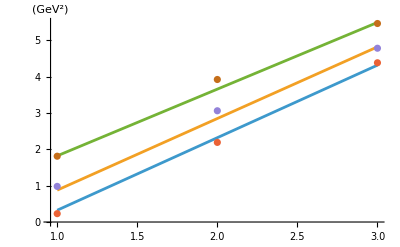

{0.13,0.13,0.099,0.24,0.0096,0.2,0.87,0.61,0.46,0.41}

```mathematica
Block[{n},ff[n_]=EulerMatrix[{α,β,γ}].v3/.fit["BestFitParameters"]];
data=Table[Table[{n,ff[n][[i]]},{n,1,3}],{i,1,3}]
m1={{1,0.23},{2,2.19},{3,4.38}}
m2={{1,0.98},{2,3.06},{3,4.78}}
m3={{1,1.81},{2,3.92},{3,5.46}}
data=Join[data,{m1},{m2},{m3}];
ListPlot[data,Joined->{True,True,True,False,False,False},AxesLabel->{"","(GeV^2)"}]
δm
```

OMG HOW BEAUTIFUL IT IS!!
Get now the mathematical trajectories:

```mathematica
mathmass=v3/.fit["BestFitParameters"]
Table[mathmass[[1]]/.{n->i},{i,1,3}]
Table[mathmass[[2]]/.{n->i},{i,1,3}]
Table[mathmass[[3]]/.{n->i},{i,1,3}]
```

{0.0846319+1.43 n,-0.240586+1.43 n,-1.98068+2.67179 n}

{1.51463,2.94463,4.37463}

{1.18941,2.61941,4.04941}

{0.691112,3.36291,6.0347}

Get also the standard error for the parameters

```mathematica
params={m02,m02s,m02p,μp,μ,α,β,γ}/.fit["BestFitParameters"]
δparams=Sqrt[Diagonal[fit["CovarianceMatrix"]]]
```

{0.0846319,-0.240586,-1.98068,2.67179,1.43,0.686752,1.63339,2.22804}

{0.124496,0.112209,0.140079,0.142274,0.0697368,0.045359,0.0603055,0.0288705}

Issue: The third trajectory that is supposed to be the most massive is the one with lowest widths, and they are proportional to the mass, so they should be the largest.

```mathematica
r=params[[4]]/params[[5]]
r^2
0.13/δparams[[4]]
```

1.86839

3.49087

0.913732